```mathematica
randomDirection:=Module[{cosTheta,sinTheta,phi},
cosTheta=RandomReal[{-1,1}];
phi=RandomReal[2π];
sinTheta=√(1-cosTheta^2);
{cosTheta,sinTheta Sin[phi],sinTheta Cos[phi]}];
```

```mathematica
x3Gaussian:=√(-Log[RandomReal[]RandomReal[]]);
```

```mathematica
test$x3Gaussian[n_]:=Module[{h,d},
h=HistogramList[Table[x3Gaussian,n],{0,4,0.01},"PDF"];d=Transpose[{Drop[h[[1]],-1],h[[2]]}];Show[ListStepPlot[d,Filling->Axis],Plot[2 x^3 Exp[-x^2],{x,0,4},PlotStyle->Red]]]
```

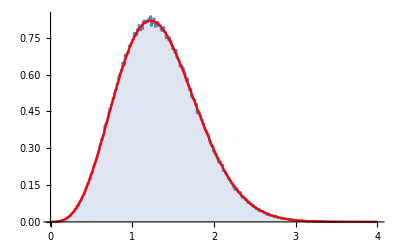

```mathematica
test$x3Gaussian[1000000]
```

```mathematica
x2Gaussian:=√(1/2(RandomVariate[NormalDistribution[0,1]])^2-Log[RandomReal[]]);
```

```mathematica
test$x2Gaussian[n_]:=Module[{h,d},
h=HistogramList[Table[x2Gaussian,n],{0,4,0.01},"PDF"];d=Transpose[{Drop[h[[1]],-1],h[[2]]}];Show[ListStepPlot[d,Filling->Axis],Plot[4/(√π)x^2 Exp[-x^2],{x,0,4},PlotStyle->Red]]]
```

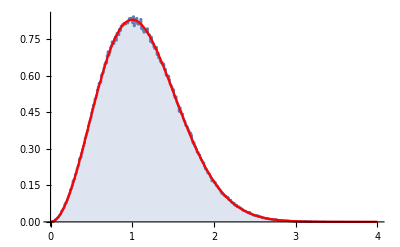

```mathematica
test$x2Gaussian[1000000]
```

```mathematica
getVpAndCosine[vpRms_,vn_]:=
Module[{β,y,x,μ,vp},
β=1/(√2 vpRms);
y=β vn;
While[True,
x=If[RandomReal[]<2/(√π y+2),x3Gaussian,x2Gaussian];
vp=x/β;
μ=RandomReal[{-1,1}];
If[RandomReal[]<(√(vn^2+vp^2-2vn vp μ))/(vn+vp),Break[]];
];
{vp,μ}
]
```

```mathematica
scatterE[erg0_]:=Module[{vecVn,vecVp,vecVcm,vecVnout,vn,vp,μ,mn=939.565,mp=938.272,kT=2.53*^-8},
vn=√(2 erg0/mn);
{vp,μ}=getVpAndCosine[√(kT/mp),vn];
vecVn=vn{1,0,0};
vecVp=vp{μ,√(1-μ^2),0};
vecVcm=-(mn vecVn+mp vecVp)/(mn+mp);
vecVnout=Norm[vecVn+vecVcm]randomDirection-vecVcm;
1/2 mn vecVnout.vecVnout];
```

```mathematica
getCsvTallyFromClipboard[]:=Module[{eList,nList,errList,toPlot},{eList,nList}=Transpose[ImportString[ NotebookGet[ClipboardNotebook[]][[1,1,1]],"CSV"]];toPlot = Transpose[{Drop[eList,-1],Drop[nList,1]}];{eList,nList,errList,toPlot}]
```

```mathematica
getTallyFromClipboard[]:=Module[{eList,nList,errList,toPlot},{eList,nList,errList}=Transpose[ImportString[ NotebookGet[ClipboardNotebook[]][[1,1,1]],"Table"]];toPlot = Transpose[{10^6 Drop[eList,-1],Drop[nList,1]}];{eList,nList,errList,toPlot}]
```

```mathematica
myLinearHist[tally_,title_]:=Module[{eList,nList,errList,toPlot},{eList,nList,errList,toPlot}=tally;ListStepPlot[toPlot,PlotRange->{xRange,yRange},
AxesLabel->{"eV","(n/cm^2)/src"},Filling->Axis,PlotLabel->title<>"
Total = "<>ToString[Total[nList],TraditionalForm]<>"(n/cm^2)/src"]]
```

```mathematica
SetAttributes[newTally,HoldFirst];
newTally[t_,n_,bin_]:=With[{BINS=1,BINSIZE=2,SUMS=3,SUMSX=4,SUMSXX=5},Clear[t];t={Table[0,n],bin,0,0};];
SetAttributes[scoreTally,HoldFirst];
scoreTally[t_,x_,score_]:=With[{BINS=1,BINSIZE=2,SUMS=3,SUMSX=4,SUMSXX=5},Module[{ibin},ibin=Ceiling[x/t[[BINSIZE]]];If[ibin>0 && ibin≤Length[t[[BINS]]],t[[BINS,ibin]]+=score];t[[SUMS]]+=score;t[[SUMSX]]+=score x;]];
SetAttributes[clearTally,HoldFirst];
clearTally[t_]:=With[{BINS=1,BINSIZE=2,SUMS=3,SUMSX=4,SUMSXX=5},Module[{n=Length[t[[BINS]]],binsize=t[[BINSIZE]]},newTally[t,n,binsize]]];
listToPlotTally[t_,scale_:1]:=With[{BINS=1,BINSIZE=2,SUMS=3,SUMSX=4,SUMSXX=5},Module[{n=Length[t[[BINS]]],binsize=t[[BINSIZE]]},Table[{(i-1) binsize,scale t[[BINS,i]]},{i,1,n}]]];
meanTally[t_]:=With[{BINS=1,BINSIZE=2,SUMS=3,SUMSX=4,SUMSXX=5},t[[SUMSX]]/t[[SUMS]]];
totalTally[t_]:=With[{BINS=1,BINSIZE=2,SUMS=3,SUMSX=4,SUMSXX=5},t[[SUMS]]];
```

```mathematica
(* Tallies with Covariance *)
With[{BINS=1,NBINS=2,BINSIZE=3,COUNT=4,TEMPBINS=5,COV=6,SUMF=7,SUMFF=8},
newTallyWithCovariance[nbins_,binsize_]:=Module[{},
{Table[0,nbins],nbins,binsize,0,Table[0,nbins],Table[0,nbins,nbins],0,0}];
SetAttributes[{scoreTallyWithCovariance,accumulateTallyWithCovariance},HoldFirst];
scoreTallyWithCovariance[t_,x_,score_]:=Module[{ibin},ibin=Ceiling[x/t[[BINSIZE]]];
If[ibin>0 && ibin≤t[[NBINS]],t[[TEMPBINS,ibin]]+=score];];
accumulateTallyWithCovariance[t_]:=Module[{f},
f=Total[t[[TEMPBINS]]];
t[[SUMF]]+=f;
t[[SUMFF]]+=f^2;
t[[BINS]]+=t[[TEMPBINS]];
t[[COV]]+=Outer[Times,t[[TEMPBINS]],t[[TEMPBINS]]];
t[[TEMPBINS]]=Table[0,t[[NBINS]]];
t[[COUNT]]++;
];
listToPlotTallyWithCovariance[t_,scale_:1]:=Module[{n=t[[NBINS]],binsize=t[[BINSIZE]],k=t[[COUNT]]},
Table[{(i-1) binsize,scale t[[BINS,i]]/k},{i,1,n}]];
errTallyWithCovariance[t_]:=Module[{n=t[[NBINS]],binsize=t[[BINSIZE]],k=t[[COUNT]],sumX=t[[BINS]],sumXX=Diagonal[t[[COV]]],meanX,errX},
meanX=sumX/k; errX=Sqrt[(sumXX/k-meanX^2)/(k)];
Transpose[{binsize Range[0,n],Join[{0},meanX],Join[{0},errX/(meanX+10^-99)]}]];meanTallyWithCovariance[t_]:=Module[{n=t[[NBINS]],binsize=t[[BINSIZE]],k=t[[COUNT]],sumX=t[[BINS]],meanX},
meanX=sumX/k];
countTallyWithCovariance[t_]:=t[[COUNT]];
fTallyWithCovariance[t_]:=t[[SUMF]]/t[[COUNT]];
varFTallyWithCovariance[t_]:=t[[SUMFF]]/t[[COUNT]]-(t[[SUMF]]/t[[COUNT]])^2;
corTallyWithCovariance[t_]:=Module[{n=t[[NBINS]],binsize=t[[BINSIZE]],k=t[[COUNT]],sumX=t[[BINS]],sumXX=t[[COV]],meanX,sigX,cov,cor},
meanX=sumX/k; 
cov=sumXX/k-Outer[Times,meanX,meanX];
sigX =Sqrt[Diagonal[cov]];
cor=cov Outer[Times,1/sigX,1/sigX];
cor
];
covTallyWithCovariance[t_]:=Module[{n=t[[NBINS]],binsize=t[[BINSIZE]],k=t[[COUNT]],sumX=t[[BINS]],sumXX=t[[COV]],meanX,sigX,cov,cor},
meanX=sumX/k; 
cov=sumXX/k-Outer[Times,meanX,meanX];
cov
];
];
```

```mathematica
(* Tallies without Covariance *)
With[{BINS=1,NBINS=2,BINSIZE=3,COUNT=4,TEMPBINS=5},
newTally[nbins_,binsize_]:=Module[{},
{Table[0,nbins],nbins,binsize,0,Table[0,nbins]}];
SetAttributes[{scoreTally,accumulateTally},HoldFirst];
scoreTally[t_,x_,score_]:=Module[{ibin},ibin=Ceiling[x/t[[BINSIZE]]];
If[ibin>0 && ibin≤t[[NBINS]],t[[TEMPBINS,ibin]]+=score];];
accumulateTally[t_]:=Module[{},
t[[BINS]]+=t[[TEMPBINS]];
t[[TEMPBINS]]=Table[0,t[[NBINS]]];
t[[COUNT]]++;
];
listToPlotTally[t_,scale_:1]:=Module[{n=t[[NBINS]],binsize=t[[BINSIZE]],k=t[[COUNT]]},
Table[{(i-1) binsize,scale t[[BINS,i]]/k},{i,1,n}]];
meanTally[t_]:=Module[{n=t[[NBINS]],binsize=t[[BINSIZE]],k=t[[COUNT]],sumX=t[[BINS]],meanX},
meanX=sumX/k];
countTally[t_]:=t[[COUNT]];
];
```

```mathematica
cov3=covTallyWithCovariance[tallyFlux3];
```

```mathematica
mmm3=Inverse[cov3];
```

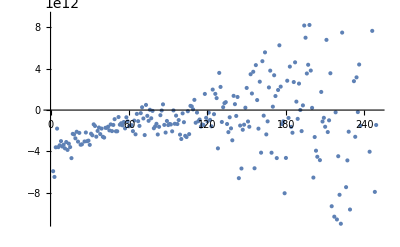

```mathematica
ListPlot[mmm3[[25]]]
```

```mathematica
mmm3[[25]]
```

```mathematica
MatrixForm[errTallyWithCovariance[tallyFlux3]]
```

```mathematica
cor3=corTallyWithCovariance[tallyFlux3];
```

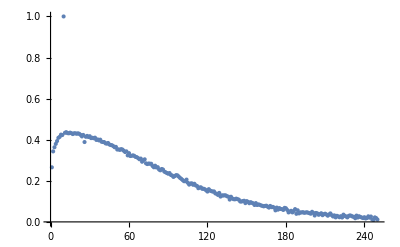

```mathematica
ListPlot[cor3[[10]]]
```

```mathematica
runNeutronPrisonHWax[nParticles_]:=Module[{volume=200^3,erg0=2.53 10^-8,density=0.082572,
erg,pathLength,captured,σs,σa,Σtot,tally,i},
tally=newTallyWithCovariance[250,0.001];
For[i=0, i<nParticles,i++,
erg=erg0;
captured=False;
While[!captured,
σs=csElasticH[erg];σa=csAbsH[erg];Σtot=density(σs+σa);
pathLength=-Log[RandomReal[]]/Σtot;
scoreTallyWithCovariance[tally,10^6 erg,pathLength/volume];
erg=scatterE[erg];
captured=RandomReal[]<σa/(σs+σa);
];
accumulateTallyWithCovariance[tally];
];
tally
]
```

```mathematica
runNeutronPrisonHWaxQuick[nParticles_]:=Module[{volume=200^3,erg0=2.53 10^-8,density=0.082572,
erg,pathLength,captured,σs,σa,Σtot,tally,i},
tally=newTally[250,0.001];
For[i=0, i<nParticles,i++,
erg=erg0;
captured=False;
While[!captured,
σs=csElasticH[erg];σa=csAbsH[erg];Σtot=density(σs+σa);
pathLength=-Log[RandomReal[]]/Σtot;
scoreTally[tally,10^6 erg,pathLength/volume];
erg=scatterE[erg];
captured=RandomReal[]<σa/(σs+σa);
];
accumulateTally[tally];
];
tally
]
```

```mathematica
Timing[tallyFlux9=runNeutronPrisonHWaxQuick[1000];]
```

{16.7701,Null}

```mathematica
Timing[tallyFlux5=runNeutronPrisonHWax[10000];]
```

{349.349,Null}

```mathematica
mmm5=Inverse[covTallyWithCovariance[tallyFlux5]];
```

```mathematica
f4=meanTallyWithCovariance[tallyFlux4];
f5=meanTallyWithCovariance[tallyFlux5];
```

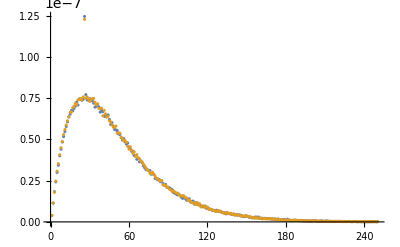

```mathematica
ListPlot[{f4,f5}]
```

```mathematica
chiSq=1/(1/10000+1/10000)(f4-f5).mmm5.(f4-f5)/250
```

1.41039

```mathematica
CDF[ChiSquareDistribution[250],352.598]
```

0.99998

```mathematica
CDF[ChiSquareDistribution[250],284.]
```

0.931372

```mathematica
tallyFlux6=runNeutronPrisonHWax[1000];
```

```mathematica
tallyFlux7=runNeutronPrisonHWax[1000];
```

```mathematica
f6=meanTallyWithCovariance[tallyFlux6];f7=meanTallyWithCovariance[tallyFlux7];
```

```mathematica
chiSq=1/(1/1000+1/1000)(f6-f7).mmm5.(f6-f7)/250
```

1.13685

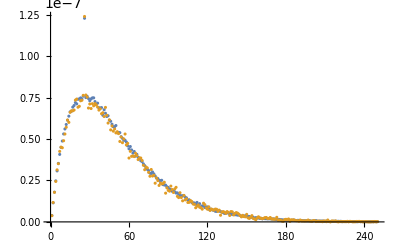

```mathematica
ListPlot[{f5,f6}]
```

```mathematica
chiSq=1/(1/1000+1/10000)(f5-f6).mmm5.(f5-f6)/250
```

1.06408

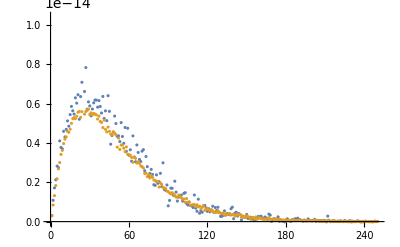

```mathematica
ListPlot[{covTallyWithCovariance[tallyFlux6][[25]],covTallyWithCovariance[tallyFlux5][[25]]}]
```

```mathematica
tallyFlux8=runNeutronPrisonHWax[100000];
```

```mathematica
mmm8=Inverse[covTallyWithCovariance[tallyFlux8]];
```

```mathematica
f8=meanTallyWithCovariance[tallyFlux8];
```

```mathematica
k8=countTallyWithCovariance[tallyFlux8]
```

```mathematica
k6=countTallyWithCovariance[tallyFlux6]
```

1000

```mathematica
chiSq=1/(1/k6+1/k8)(f8-f6).mmm8.(f8-f6)/250
```

0.977298

```mathematica
chiSq8[t_]:=Module[{f=meanTallyWithCovariance[t],k=countTallyWithCovariance[t]},
1/(1/k+1/k8)(f8-f).mmm8.(f8-f)/250];
```

```mathematica
chiSq8[tallyFlux6]
```

1000

0.977298

```mathematica
chiSq8[tallyFlux5]
```

10000

1.24029

```mathematica
chiSq8[tallyFlux4]
```

10000

1.28217

```mathematica
cs10k=Reap[
Module[{n=100,k=10000,i,t,cs},
For[i=1,i≤n,i++,
t=runNeutronPrisonHWaxQuick[k];
cs=chiSq8[t];
Print[i," ",cs];
Sow[cs];
]
]
]
```

1 0.902973

2 0.769126

3 0.98066

4 1.09668

5 1.11431

6 0.999553

7 0.998848

8 1.03499

9 1.08141

10 1.02578

11 1.00831

12 0.779877

13 1.22229

14 1.1718

15 1.05237

16 0.869902

17 1.0106

18 0.980671

19 1.05088

20 1.20227

21 1.00848

22 1.0521

23 1.30564

24 0.828189

25 1.02745

26 1.01698

27 1.14149

28 0.965558

29 1.0661

30 0.994329

31 1.12045

32 0.996784

33 1.00831

34 1.02449

35 1.0359

36 1.06898

37 1.12341

38 0.893936

39 1.16669

40 0.920352

41 0.974967

42 1.01083

43 1.03664

44 1.05401

45 0.982542

46 1.27958

47 1.11182

48 0.958144

49 0.979558

50 1.23938

51 1.03338

52 1.00294

53 0.987862

54 1.05602

55 1.02642

56 0.991014

57 0.962038

58 1.01529

59 0.794775

60 0.965798

61 1.06391

62 0.933109

63 1.12344

64 0.997699

65 1.07636

66 1.14491

67 1.03999

68 1.07094

69 1.05502

70 1.04765

71 1.00336

72 1.08773

73 0.994414

74 0.996645

75 0.958722

76 1.07974

77 0.999745

78 0.94571

79 1.32814

80 0.892154

81 0.938645

82 0.765281

83 1.18195

84 0.962688

85 1.08454

86 0.876419

87 0.994092

88 0.92664

89 0.993251

90 1.0391

91 1.06422

92 1.05078

93 0.919887

94 1.08725

95 0.955968

96 0.894153

97 1.11491

98 0.869872

99 0.888033

100 0.858996

{Null,{{0.902973,0.769126,0.98066,1.09668,1.11431,0.999553,0.998848,1.03499,1.08141,1.02578,1.00831,0.779877,1.22229,1.1718,1.05237,0.869902,1.0106,0.980671,1.05088,1.20227,1.00848,1.0521,1.30564,0.828189,1.02745,1.01698,1.14149,0.965558,1.0661,0.994329,1.12045,0.996784,1.00831,1.02449,1.0359,1.06898,1.12341,0.893936,1.16669,0.920352,0.974967,1.01083,1.03664,1.05401,0.982542,1.27958,1.11182,0.958144,0.979558,1.23938,1.03338,1.00294,0.987862,1.05602,1.02642,0.991014,0.962038,1.01529,0.794775,0.965798,1.06391,0.933109,1.12344,0.997699,1.07636,1.14491,1.03999,1.07094,1.05502,1.04765,1.00336,1.08773,0.994414,0.996645,0.958722,1.07974,0.999745,0.94571,1.32814,0.892154,0.938645,0.765281,1.18195,0.962688,1.08454,0.876419,0.994092,0.92664,0.993251,1.0391,1.06422,1.05078,0.919887,1.08725,0.955968,0.894153,1.11491,0.869872,0.888033,0.858996}}}

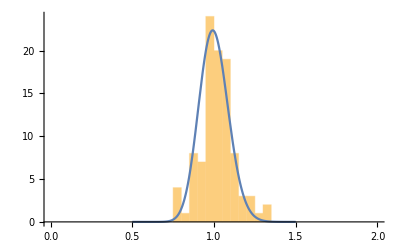

```mathematica
Show[Histogram[cs10k[[2,1]],{0,2,0.05}],Plot[100 0.05 250PDF[ChiSquareDistribution[250],250 x],{x,0.5,1.5},PlotRange->All]]
```

```mathematica
{Mean[cs10k[[2,1]]],StandardDeviation[cs10k[[2,1]]]}
```

{1.01888,0.105846}

```mathematica
N[StandardDeviation[ChiSquareDistribution[250]]/250]
```

0.0894427

```mathematica
{Mean[cs1ka[[2,1]]],StandardDeviation[cs1ka[[2,1]]]}
```

{1.01012,0.111872}

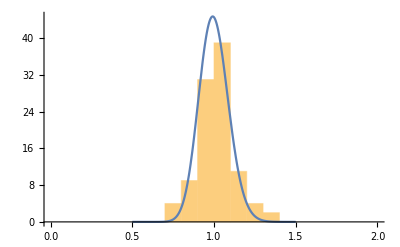

```mathematica
Show[Histogram[cs10k[[2,1]],{0,2,0.1}],Plot[100 0.1 250PDF[ChiSquareDistribution[250],250 x],{x,0.5,1.5},PlotRange->All]]
```

```mathematica
Mean[cs10k[[2,1]]]
```

1.01888

```mathematica
StandardDeviation[cs10k[[2,1]]]
```

0.105846

```mathematica
cs1ka=Reap[
Module[{n=100,k=1000,i,t,cs},
For[i=1,i≤n,i++,
t=runNeutronPrisonHWaxQuick[k];
cs=chiSq8[t];
Print[i," ",cs];
Sow[cs];
]
]
]
```

{Null,{{1.08954,1.03196,1.01973,1.06804,1.10653,0.941427,1.23457,0.894095,1.23742,0.934586,1.08035,0.916208,0.826524,1.09382,0.811709,0.91497,1.05811,0.815484,0.878174,1.05603,1.21113,0.780031,0.975914,1.11401,0.935159,0.952901,1.11777,0.900568,1.03869,1.18722,1.08539,1.16665,1.00177,1.07557,0.883701,1.03823,1.18738,1.05295,1.00635,0.972577,1.02529,1.34368,1.05657,0.937166,1.08206,1.05254,0.996741,0.905408,0.892835,0.807492,0.980903,0.936679,0.981097,1.07205,0.939393,1.13138,1.06681,1.2141,0.988109,0.975862,0.926083,0.94138,0.889915,1.09607,0.974471,1.05475,1.14994,1.00829,1.09304,0.826287,0.839271,1.01086,0.940079,0.947284,1.02372,0.872173,1.01217,1.0298,1.19947,1.11336,0.982033,1.02675,0.909166,0.99227,1.06007,1.03312,1.13863,0.776968,0.898926,0.922391,1.20075,0.930965,0.919933,0.980056,0.931358,0.996281,1.13224,1.14627,1.06484,0.94144}}}

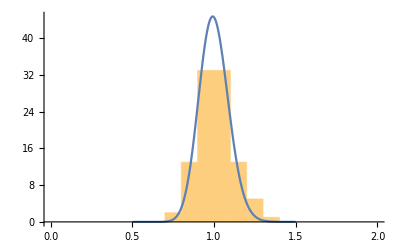

```mathematica
Show[Histogram[cs1ka[[2,1]],{0,2,0.1}],Plot[100 0.1 250PDF[ChiSquareDistribution[250],250 x],{x,0.5,1.5},PlotRange->All]]
```

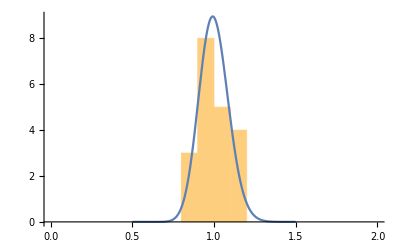

```mathematica
Show[Histogram[cs1k[[2,1]],{0,2,0.1}],Plot[20 0.1 250PDF[ChiSquareDistribution[250],250 x],{x,0.5,1.5},PlotRange->All]]
```

```mathematica
cs1k
```

{Null,{{1.05576,0.992243,0.91954,0.826214,1.08263,0.913727,0.94715,0.963906,0.90082,1.14608,1.02757,1.03843,1.0681,1.15815,0.89362,0.904716,0.961758,0.8862,1.18319,1.19039}}}

```mathematica
MatrixForm[errTallyWithCovariance[tallyFlux8]]
```

(0. | 0 | 0
0.001 | 3.78569×10^-9 | 0.0080011
0.002 | 1.1126×10^-8 | 0.00620809
0.003 | 1.77805×10^-8 | 0.00570326
0.004 | 2.3895×10^-8 | 0.00547453
0.005 | 2.97021×10^-8 | 0.0052789
0.006 | 3.49529×10^-8 | 0.00517092
0.007 | 3.93377×10^-8 | 0.00508091
0.008 | 4.38633×10^-8 | 0.00500983
0.009 | 4.79804×10^-8 | 0.00495319
0.01 | 5.14081×10^-8 | 0.00489342
0.011 | 5.44468×10^-8 | 0.00487172
0.012 | 5.79196×10^-8 | 0.00483475
0.013 | 6.05672×10^-8 | 0.00481883
0.014 | 6.2992×10^-8 | 0.00479912
0.015 | 6.4343×10^-8 | 0.00482132
0.016 | 6.6772×10^-8 | 0.0048121
0.017 | 6.83118×10^-8 | 0.00477085
0.018 | 6.97179×10^-8 | 0.00477622
0.019 | 7.04889×10^-8 | 0.00480329
0.02 | 7.14714×10^-8 | 0.00479063
0.021 | 7.19942×10^-8 | 0.00479325
0.022 | 7.32495×10^-8 | 0.0047965
0.023 | 7.33038×10^-8 | 0.00482042
0.024 | 7.34328×10^-8 | 0.00484017
0.025 | 7.37322×10^-8 | 0.00485026
0.026 | 1.23207×10^-7 | 0.00317581
0.027 | 7.39465×10^-8 | 0.00485887
0.028 | 7.34667×10^-8 | 0.00487131
0.029 | 7.35179×10^-8 | 0.00491073
0.03 | 7.28208×10^-8 | 0.00493812
0.031 | 7.21288×10^-8 | 0.00492898
0.032 | 7.1751×10^-8 | 0.00499454
0.033 | 7.13421×10^-8 | 0.00502207
0.034 | 7.05548×10^-8 | 0.00501911
0.035 | 6.99755×10^-8 | 0.00507718
0.036 | 6.92328×10^-8 | 0.00507132
0.037 | 6.8755×10^-8 | 0.0051301
0.038 | 6.80001×10^-8 | 0.00515318
0.039 | 6.62724×10^-8 | 0.00522388
0.04 | 6.54481×10^-8 | 0.00519944
0.041 | 6.47621×10^-8 | 0.00525843
0.042 | 6.41089×10^-8 | 0.00528482
0.043 | 6.21424×10^-8 | 0.00533608
0.044 | 6.21293×10^-8 | 0.00533817
0.045 | 6.08808×10^-8 | 0.00538533
0.046 | 5.95346×10^-8 | 0.00542293
0.047 | 5.8396×10^-8 | 0.00547366
0.048 | 5.75693×10^-8 | 0.00553261
0.049 | 5.65341×10^-8 | 0.00554695
0.05 | 5.52074×10^-8 | 0.00559264
0.051 | 5.46954×10^-8 | 0.0056285
0.052 | 5.27848×10^-8 | 0.00573509
0.053 | 5.17834×10^-8 | 0.00577375
0.054 | 5.08568×10^-8 | 0.00579348
0.055 | 4.99405×10^-8 | 0.00583306
0.056 | 4.87812×10^-8 | 0.0058938
0.057 | 4.75189×10^-8 | 0.00591537
0.058 | 4.67474×10^-8 | 0.00601541
0.059 | 4.5874×10^-8 | 0.00605726
0.06 | 4.44623×10^-8 | 0.00612
0.061 | 4.36058×10^-8 | 0.00620728
0.062 | 4.26901×10^-8 | 0.00620302
0.063 | 4.20384×10^-8 | 0.0062892
0.064 | 4.0514×10^-8 | 0.00633543
0.065 | 3.95624×10^-8 | 0.0064331
0.066 | 3.91165×10^-8 | 0.00648853
0.067 | 3.78145×10^-8 | 0.00655472
0.068 | 3.70405×10^-8 | 0.00662732
0.069 | 3.59167×10^-8 | 0.00663581
0.07 | 3.52303×10^-8 | 0.00675467
0.071 | 3.44626×10^-8 | 0.00683573
0.072 | 3.35784×10^-8 | 0.0069401
0.073 | 3.26897×10^-8 | 0.00700032
0.074 | 3.1879×10^-8 | 0.00703015
0.075 | 3.08284×10^-8 | 0.00715155
0.076 | 3.02225×10^-8 | 0.00725506
0.077 | 2.94987×10^-8 | 0.00733029
0.078 | 2.82934×10^-8 | 0.00745473
0.079 | 2.76884×10^-8 | 0.00753595
0.08 | 2.71688×10^-8 | 0.00749865
0.081 | 2.60621×10^-8 | 0.00772091
0.082 | 2.57546×10^-8 | 0.0077863
0.083 | 2.50768×10^-8 | 0.00790419
0.084 | 2.41058×10^-8 | 0.00794159
0.085 | 2.38209×10^-8 | 0.00806088
0.086 | 2.30027×10^-8 | 0.00814281
0.087 | 2.23462×10^-8 | 0.00829264
0.088 | 2.15184×10^-8 | 0.00836111
0.089 | 2.11677×10^-8 | 0.0084212
0.09 | 2.02507×10^-8 | 0.00858587
0.091 | 1.98044×10^-8 | 0.00865303
0.092 | 1.94238×10^-8 | 0.00883673
0.093 | 1.88919×10^-8 | 0.00899088
0.094 | 1.82281×10^-8 | 0.00902679
0.095 | 1.79783×10^-8 | 0.00912197
0.096 | 1.73283×10^-8 | 0.00926941
0.097 | 1.66875×10^-8 | 0.00933401
0.098 | 1.6356×10^-8 | 0.0095007
0.099 | 1.56481×10^-8 | 0.00971603
0.1 | 1.52005×10^-8 | 0.0097636
0.101 | 1.50411×10^-8 | 0.00998661
0.102 | 1.42183×10^-8 | 0.0101835
0.103 | 1.42074×10^-8 | 0.0101715
0.104 | 1.39432×10^-8 | 0.0103189
0.105 | 1.30459×10^-8 | 0.0104929
0.106 | 1.28142×10^-8 | 0.0106508
0.107 | 1.24758×10^-8 | 0.0108418
0.108 | 1.22022×10^-8 | 0.0109457
0.109 | 1.17591×10^-8 | 0.0110562
0.11 | 1.13798×10^-8 | 0.011291
0.111 | 1.0941×10^-8 | 0.0114741
0.112 | 1.0833×10^-8 | 0.011522
0.113 | 1.04513×10^-8 | 0.0119194
0.114 | 1.00561×10^-8 | 0.0120406
0.115 | 9.7821×10^-9 | 0.0121654
0.116 | 9.26432×10^-9 | 0.0123106
0.117 | 9.39589×10^-9 | 0.0126154
0.118 | 8.8986×10^-9 | 0.0126934
0.119 | 8.65082×10^-9 | 0.0129586
0.12 | 8.42872×10^-9 | 0.0131715
0.121 | 8.10185×10^-9 | 0.0132298
0.122 | 7.91753×10^-9 | 0.0134408
0.123 | 7.62366×10^-9 | 0.0137527
0.124 | 7.40199×10^-9 | 0.0137458
0.125 | 7.03576×10^-9 | 0.0142428
0.126 | 6.99739×10^-9 | 0.0142217
0.127 | 6.68447×10^-9 | 0.0145589
0.128 | 6.47099×10^-9 | 0.0148901
0.129 | 6.23268×10^-9 | 0.0150853
0.13 | 6.04175×10^-9 | 0.015229
0.131 | 5.79176×10^-9 | 0.0154679
0.132 | 5.68686×10^-9 | 0.0158567
0.133 | 5.53719×10^-9 | 0.0158715
0.134 | 5.44598×10^-9 | 0.0162839
0.135 | 5.2131×10^-9 | 0.0166116
0.136 | 5.03174×10^-9 | 0.0168054
0.137 | 4.90519×10^-9 | 0.0169575
0.138 | 4.49954×10^-9 | 0.0174
0.139 | 4.60012×10^-9 | 0.0175658
0.14 | 4.39757×10^-9 | 0.0180706
0.141 | 4.29366×10^-9 | 0.0178584
0.142 | 4.23414×10^-9 | 0.0187345
0.143 | 4.048×10^-9 | 0.0187022
0.144 | 3.83651×10^-9 | 0.0190893
0.145 | 3.80727×10^-9 | 0.019091
0.146 | 3.67801×10^-9 | 0.0192874
0.147 | 3.47427×10^-9 | 0.0201662
0.148 | 3.42705×10^-9 | 0.0200476
0.149 | 3.34548×10^-9 | 0.0206091
0.15 | 3.21876×10^-9 | 0.0206103
0.151 | 3.05973×10^-9 | 0.0212617
0.152 | 3.07462×10^-9 | 0.0217207
0.153 | 2.84444×10^-9 | 0.0220615
0.154 | 2.75178×10^-9 | 0.022627
0.155 | 2.7582×10^-9 | 0.0227667
0.156 | 2.66651×10^-9 | 0.0229158
0.157 | 2.54503×10^-9 | 0.0233022
0.158 | 2.46031×10^-9 | 0.0237034
0.159 | 2.34011×10^-9 | 0.0240574
0.16 | 2.2801×10^-9 | 0.0251645
0.161 | 2.14751×10^-9 | 0.0255048
0.162 | 2.25975×10^-9 | 0.0253663
0.163 | 1.98794×10^-9 | 0.0265867
0.164 | 2.09507×10^-9 | 0.0261542
0.165 | 1.9818×10^-9 | 0.0272064
0.166 | 1.82575×10^-9 | 0.0272933
0.167 | 1.86869×10^-9 | 0.027553
0.168 | 1.78616×10^-9 | 0.0285485
0.169 | 1.66856×10^-9 | 0.0284406
0.17 | 1.67829×10^-9 | 0.0286065
0.171 | 1.61549×10^-9 | 0.029678
0.172 | 1.47921×10^-9 | 0.02993
0.173 | 1.55737×10^-9 | 0.0296733
0.174 | 1.43621×10^-9 | 0.0320053
0.175 | 1.30711×10^-9 | 0.0318964
0.176 | 1.36991×10^-9 | 0.03222
0.177 | 1.29771×10^-9 | 0.0338232
0.178 | 1.30772×10^-9 | 0.0331498
0.179 | 1.20711×10^-9 | 0.0334553
0.18 | 1.13737×10^-9 | 0.0346327
0.181 | 1.19043×10^-9 | 0.0347981
0.182 | 1.11296×10^-9 | 0.0356951
0.183 | 1.04446×10^-9 | 0.0363904
0.184 | 1.04932×10^-9 | 0.0373876
0.185 | 1.03646×10^-9 | 0.0377943
0.186 | 9.46537×10^-10 | 0.0381748
0.187 | 9.15946×10^-10 | 0.0386257
0.188 | 8.92221×10^-10 | 0.0396221
0.189 | 8.80456×10^-10 | 0.0395766
0.19 | 8.55235×10^-10 | 0.0404992
0.191 | 7.86844×10^-10 | 0.0416972
0.192 | 7.23719×10^-10 | 0.0441789
0.193 | 8.20992×10^-10 | 0.0420274
0.194 | 6.95759×10^-10 | 0.0434266
0.195 | 7.2561×10^-10 | 0.046058
0.196 | 6.27588×10^-10 | 0.0469713
0.197 | 6.16437×10^-10 | 0.0467391
0.198 | 6.46072×10^-10 | 0.0469913
0.199 | 6.26055×10^-10 | 0.0483136
0.2 | 6.17921×10^-10 | 0.0498866
0.201 | 5.6617×10^-10 | 0.0516863
0.202 | 5.77455×10^-10 | 0.048673
0.203 | 4.95×10^-10 | 0.0539734
0.204 | 5.10365×10^-10 | 0.0519602
0.205 | 5.2114×10^-10 | 0.0527815
0.206 | 4.50383×10^-10 | 0.0578841
0.207 | 4.53206×10^-10 | 0.0552875
0.208 | 4.01885×10^-10 | 0.0601185
0.209 | 4.6045×10^-10 | 0.0577963
0.21 | 4.00281×10^-10 | 0.0603236
0.211 | 4.27024×10^-10 | 0.0602367
0.212 | 4.09909×10^-10 | 0.0603655
0.213 | 3.85712×10^-10 | 0.058561
0.214 | 3.51381×10^-10 | 0.0635084
0.215 | 3.69497×10^-10 | 0.0649484
0.216 | 3.22753×10^-10 | 0.0659761
0.217 | 3.10001×10^-10 | 0.065159
0.218 | 3.25384×10^-10 | 0.0642351
0.219 | 2.78419×10^-10 | 0.0698489
0.22 | 2.64487×10^-10 | 0.0729747
0.221 | 2.87321×10^-10 | 0.0686022
0.222 | 2.972×10^-10 | 0.0693691
0.223 | 2.87023×10^-10 | 0.0703215
0.224 | 2.66702×10^-10 | 0.0714831
0.225 | 2.11214×10^-10 | 0.0781606
0.226 | 2.57405×10^-10 | 0.0764711
0.227 | 2.01523×10^-10 | 0.0769668
0.228 | 2.18418×10^-10 | 0.0778691
0.229 | 2.23569×10^-10 | 0.0787249
0.23 | 1.96879×10^-10 | 0.0850757
0.231 | 1.94657×10^-10 | 0.0882931
0.232 | 1.79198×10^-10 | 0.0893692
0.233 | 2.12215×10^-10 | 0.0897546
0.234 | 1.84736×10^-10 | 0.0856048
0.235 | 1.81456×10^-10 | 0.0837665
0.236 | 1.77654×10^-10 | 0.089608
0.237 | 1.58676×10^-10 | 0.0965982
0.238 | 1.62375×10^-10 | 0.0905661
0.239 | 1.56463×10^-10 | 0.0954023
0.24 | 1.6607×10^-10 | 0.0954888
0.241 | 1.28876×10^-10 | 0.0979369
0.242 | 1.2893×10^-10 | 0.0995753
0.243 | 1.3677×10^-10 | 0.0947167
0.244 | 1.11415×10^-10 | 0.10385
0.245 | 1.21924×10^-10 | 0.117592
0.246 | 1.08572×10^-10 | 0.109151
0.247 | 1.17127×10^-10 | 0.112178
0.248 | 8.65377×10^-11 | 0.115975
0.249 | 1.00426×10^-10 | 0.121662
0.25 | 9.41248×10^-11 | 0.130891)

```mathematica
fTallyWithCovariance[tallyFlux5]
```

5.19401×10^-6

```mathematica
varFTallyWithCovariance[tallyFlux5]//Sqrt
```

5.19751×10^-6

```mathematica
Total[covTallyWithCovariance[tallyFlux5],2]//Sqrt
```

5.19751×10^-6

```mathematica
cov5=covTallyWithCovariance[tallyFlux5];
```

```mathematica
bigF=Total[meanTallyWithCovariance[tallyFlux5]]
```

5.19401×10^-6

```mathematica
f=meanTallyWithCovariance[tallyFlux5];
```

```mathematica
p=f/bigF;
```

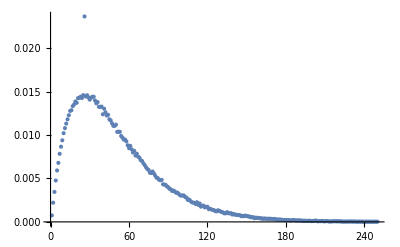

```mathematica
ListPlot[p]
```

```mathematica
p[[25]]
```

0.0145877

```mathematica
f[[25]]
```

7.57688×10^-8

```mathematica
covTallyWithCovariance[tallyFlux5][[25,25]]
```

1.30682×10^-14

```mathematica
Total[covTallyWithCovariance[tallyFlux5][[25]]]
```

3.92021×10^-13

```mathematica
Total[covTallyWithCovariance[tallyFlux5],2]
```

2.70141×10^-11

```mathematica
With[{k=25},Sum[(i,k-p[[k]])(j,k-p[[k]])cov5[[i,j]],{i,1,250},{j,1,250}]]
```

7.37943×10^-15

```mathematica
With[{k=25},Sum[(p[[k]])(p[[k]])cov5[[i,j]],{i,1,250},{j,1,250}]]
```

5.74863×10^-15

```mathematica
covTallyWithCovariance[tallyFlux5][[25]]
```

```mathematica
varP=1/bigF^2 Table[Sum[(i,k-p[[k]])(j,k-p[[k]])cov5[[i,j]],{i,1,250},{j,1,250}],{k,250}]
```

{3.04773×10^-6,0.0000141821,0.0000277728,0.0000440163,0.0000624857,0.0000767556,0.0000924057,0.000111013,0.00012412,0.000141713,0.000156267,0.000168891,0.000181572,0.00020222,0.000213258,0.000206739,0.000218644,0.000237363,0.000234299,0.000249913,0.000256179,0.000254768,0.000262445,0.000260111,0.000273537,0.000451674,0.000279572,0.000287787,0.000286417,0.000273308,0.000295156,0.000281894,0.000288007,0.000278776,0.000300719,0.000290789,0.000275295,0.000275505,0.000287174,0.000271945,0.000283516,0.000260087,0.000266878,0.000267084,0.000258814,0.000259346,0.000253103,0.000235544,0.00023953,0.000253613,0.000236506,0.000245451,0.000234201,0.000229561,0.00021116,0.00021719,0.000211255,0.000216319,0.000203957,0.000187259,0.000207802,0.000193171,0.000186868,0.000197791,0.000184438,0.000190685,0.000180858,0.000179037,0.000173939,0.000179617,0.000158439,0.000160251,0.000156493,0.000149322,0.000151506,0.000134963,0.000134535,0.000139433,0.000133004,0.000137773,0.000127575,0.000117096,0.000119874,0.000122196,0.000125095,0.000105651,0.000101612,0.000103878,0.000104373,0.0000959932,0.0000923143,0.0000889199,0.000089696,0.0000893418,0.0000826761,0.0000830236,0.0000878356,0.0000844629,0.0000770659,0.0000764916,0.0000762746,0.000080585,0.0000745235,0.0000714255,0.0000640093,0.0000677923,0.0000610284,0.0000556141,0.0000576626,0.0000546965,0.0000511187,0.0000558173,0.0000489311,0.0000553154,0.0000426428,0.0000474457,0.0000483308,0.0000433465,0.0000458486,0.0000424405,0.0000350195,0.0000380941,0.0000355918,0.0000337416,0.0000338512,0.0000304631,0.0000287873,0.0000350931,0.0000341024,0.0000291759,0.0000283947,0.0000281492,0.0000252326,0.0000249761,0.0000303659,0.0000243706,0.0000266161,0.0000268002,0.0000211465,0.0000236597,0.0000221681,0.000022034,0.000020995,0.0000220789,0.0000218507,0.0000156387,0.0000187435,0.0000172232,0.0000205187,0.0000176214,0.0000154759,0.0000164012,0.0000145498,0.0000138008,0.0000126054,0.0000110109,0.0000113567,0.000011376,0.0000119524,0.0000104578,0.000010506,8.44383×10^-6,9.65055×10^-6,8.83844×10^-6,9.02094×10^-6,0.000010599,9.69382×10^-6,9.41359×10^-6,8.60476×10^-6,8.27167×10^-6,9.74371×10^-6,7.51614×10^-6,7.53455×10^-6,5.41863×10^-6,8.03365×10^-6,6.53253×10^-6,6.50372×10^-6,5.49992×10^-6,5.40347×10^-6,6.3893×10^-6,4.92145×10^-6,5.49331×10^-6,4.8219×10^-6,3.70659×10^-6,6.72834×10^-6,5.06515×10^-6,5.4882×10^-6,3.24011×10^-6,4.61875×10^-6,6.68108×10^-6,4.19146×10^-6,4.10032×10^-6,3.64642×10^-6,3.17117×10^-6,4.31055×10^-6,3.08391×10^-6,2.60517×10^-6,3.93725×10^-6,2.76526×10^-6,2.2175×10^-6,3.83858×10^-6,3.79521×10^-6,4.40455×10^-6,2.8792×10^-6,1.67345×10^-6,2.41919×10^-6,1.95516×10^-6,3.58999×10^-6,1.94025×10^-6,1.09553×10^-6,3.03331×10^-6,1.93508×10^-6,9.9494×10^-7,9.16644×10^-7,1.48009×10^-6,1.65168×10^-6,2.20756×10^-6,2.5557×10^-6,1.49219×10^-6,1.66197×10^-6,1.35662×10^-6,2.01907×10^-6,3.20997×10^-7,9.29744×10^-7,7.01942×10^-7,8.34345×10^-7,1.05011×10^-6,8.32746×10^-7,1.33648×10^-6,1.22165×10^-6,8.16181×10^-7,7.7577×10^-7,1.14699×10^-6,4.18061×10^-7,2.44682×10^-7,1.56579×10^-6,4.02108×10^-7,7.70474×10^-7,5.13617×10^-7,2.73855×10^-7,9.43063×10^-7,3.60416×10^-7,7.19119×10^-7,4.85551×10^-7,5.97347×10^-7,3.67344×10^-7,9.53794×10^-7,1.04502×10^-6,4.75254×10^-7,8.01337×10^-7}

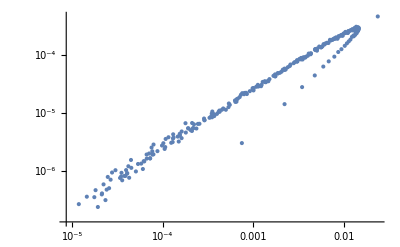

```mathematica
ListLogLogPlot[Transpose[{p,varP}]]
```

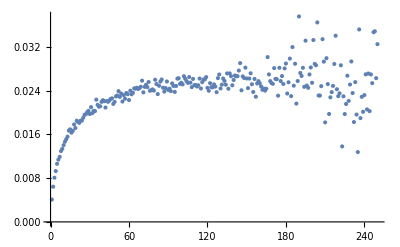

```mathematica
ListPlot[varP/p/(1-p)]
```

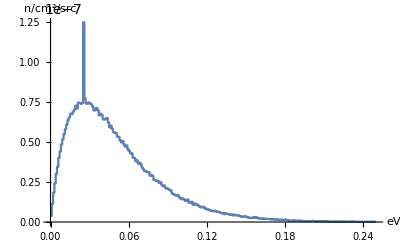

```mathematica
ListStepPlot[listToPlotTallyWithCovariance[tallyFlux4],AxesLabel->{"eV","n/cm^2/src"}]
```

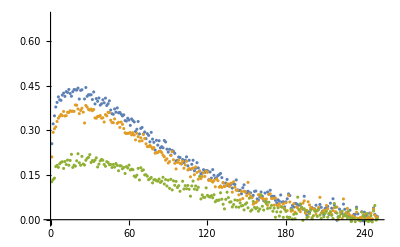

```mathematica
ListPlot[{corTallyWithCovariance[tallyFlux4][[25]],corTallyWithCovariance[tallyFlux4][[50]],corTallyWithCovariance[tallyFlux4][[100]]}]
```

```mathematica
Total[covTallyWithCovariance[tallyFlux4],2]
```

2.65438×10^-11

```mathematica
Total[meanTallyWithCovariance[tallyFlux4]]
```

5.15412×10^-6

```mathematica
Sqrt[Total[covTallyWithCovariance[tallyFlux4],2]/countTallyWithCovariance[tallyFlux4]]
```

5.15207×10^-8

```mathematica
countTallyWithCovariance[tallyFlux4]
```

10000

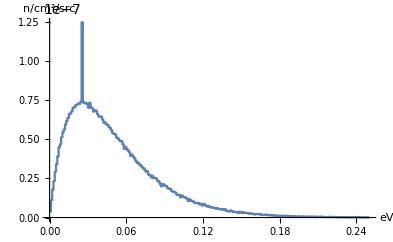

```mathematica
ListStepPlot[listToPlotTallyWithCovariance[tallyFlux2],AxesLabel->{"eV","n/cm^2/src"}]
```

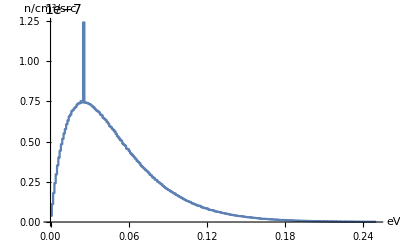

```mathematica
ListStepPlot[listToPlotTallyWithCovariance[tallyFlux3],AxesLabel->{"eV","n/cm^2/src"}]
```

```mathematica
xRange={0,0.23};yRange=All;
```

```mathematica
Export["c:\\git\\fusor-stuff\\mcnp\\hwaxprison.txt",
Join[{{"H-wax Neutron Prison, Standard Fluences"},
{countTallyWithCovariance[tallyFlux8],"neutrons"},
{250,"bins"},
{0.001,"linear","binsize"},
{250,"fluences"},
SetPrecision[f8,7],
{250,"by", 250,"inverse","covariance","matrix"}},
SetPrecision[mmm8,7]],"Table","FieldSeparators"->" "];
```

```mathematica
tallyFlux8
```

{{0.000378569,0.0011126,0.00177805,0.0023895,0.00297021,0.00349529,0.00393377,0.00438633,0.00479804,0.00514081,0.00544468,0.00579196,0.00605672,0.0062992,0.0064343,0.0066772,0.00683118,0.00697179,0.00704889,0.00714714,0.00719942,0.00732495,0.00733038,0.00734328,0.00737322,0.0123207,0.00739465,0.00734667,0.00735179,0.00728208,0.00721288,0.0071751,0.00713421,0.00705548,0.00699755,0.00692328,0.0068755,0.00680001,0.00662724,0.00654481,0.00647621,0.00641089,0.00621424,0.00621293,0.00608808,0.00595346,0.0058396,0.00575693,0.00565341,0.00552074,0.00546954,0.00527848,0.00517834,0.00508568,0.00499405,0.00487812,0.00475189,0.00467474,0.0045874,0.00444623,0.00436058,0.00426901,0.00420384,0.0040514,0.00395624,0.00391165,0.00378145,0.00370405,0.00359167,0.00352303,0.00344626,0.00335784,0.00326897,0.0031879,0.00308284,0.00302225,0.00294987,0.00282934,0.00276884,0.00271688,0.00260621,0.00257546,0.00250768,0.00241058,0.00238209,0.00230027,0.00223462,0.00215184,0.00211677,0.00202507,0.00198044,0.00194238,0.00188919,0.00182281,0.00179783,0.00173283,0.00166875,0.0016356,0.00156481,0.00152005,0.00150411,0.00142183,0.00142074,0.00139432,0.00130459,0.00128142,0.00124758,0.00122022,0.00117591,0.00113798,0.0010941,0.0010833,0.00104513,0.00100561,0.00097821,0.000926432,0.000939589,0.00088986,0.000865082,0.000842872,0.000810185,0.000791753,0.000762366,0.000740199,0.000703576,0.000699739,0.000668447,0.000647099,0.000623268,0.000604175,0.000579176,0.000568686,0.000553719,0.000544598,0.00052131,0.000503174,0.000490519,0.000449954,0.000460012,0.000439757,0.000429366,0.000423414,0.0004048,0.000383651,0.000380727,0.000367801,0.000347427,0.000342705,0.000334548,0.000321876,0.000305973,0.000307462,0.000284444,0.000275178,0.00027582,0.000266651,0.000254503,0.000246031,0.000234011,0.00022801,0.000214751,0.000225975,0.000198794,0.000209507,0.00019818,0.000182575,0.000186869,0.000178616,0.000166856,0.000167829,0.000161549,0.000147921,0.000155737,0.000143621,0.000130711,0.000136991,0.000129771,0.000130772,0.000120711,0.000113737,0.000119043,0.000111296,0.000104446,0.000104932,0.000103646,0.0000946537,0.0000915946,0.0000892221,0.0000880456,0.0000855235,0.0000786844,0.0000723719,0.0000820992,0.0000695759,0.000072561,0.0000627588,0.0000616437,0.0000646072,0.0000626055,0.0000617921,0.000056617,0.0000577455,0.0000495,0.0000510365,0.000052114,0.0000450383,0.0000453206,0.0000401885,0.000046045,0.0000400281,0.0000427024,0.0000409909,0.0000385712,0.0000351381,0.0000369497,0.0000322753,0.0000310001,0.0000325384,0.0000278419,0.0000264487,0.0000287321,0.00002972,0.0000287023,0.0000266702,0.0000211214,0.0000257405,0.0000201523,0.0000218418,0.0000223569,0.0000196879,0.0000194657,0.0000179198,0.0000212215,0.0000184736,0.0000181456,0.0000177654,0.0000158676,0.0000162375,0.0000156463,0.000016607,0.0000128876,0.000012893,0.000013677,0.0000111415,0.0000121924,0.0000108572,0.0000117127,8.65377×10^-6,0.0000100426,9.41248×10^-6},250,0.001,100000,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{{1.06078×10^-11,8.71127×10^-12,1.38489×10^-11,1.87237×10^-11,2.2957×10^-11,2.71325×10^-11,3.04266×10^-11,3.35278×10^-11,3.63103×10^-11,3.93007×10^-11,4.22545×10^-11,4.47128×10^-11,4.60888×10^-11,4.83054×10^-11,4.91682×10^-11,5.10744×10^-11,5.14169×10^-11,5.27187×10^-11,5.35956×10^-11,5.39756×10^-11,5.43279×10^-11,5.50639×10^-11,5.52238×10^-11,5.57558×10^-11,5.64005×10^-11,7.44125×10^-11,5.62698×10^-11,5.4913×10^-11,5.45629×10^-11,5.48873×10^-11,5.43339×10^-11,5.45506×10^-11,5.42547×10^-11,5.26811×10^-11,5.32777×10^-11,5.16735×10^-11,5.22788×10^-11,5.16202×10^-11,5.05764×10^-11,4.88079×10^-11,4.89096×10^-11,4.90035×10^-11,4.63835×10^-11,4.64314×10^-11,4.56318×10^-11,4.46589×10^-11,4.39243×10^-11,4.32019×10^-11,4.19378×10^-11,4.12121×10^-11,4.1005×10^-11,4.01224×10^-11,3.90899×10^-11,3.88127×10^-11,3.76425×10^-11,3.69946×10^-11,3.56884×10^-11,3.51173×10^-11,3.47781×10^-11,3.3913×10^-11,3.30528×10^-11,3.20781×10^-11,3.19441×10^-11,3.02339×10^-11,2.99483×10^-11,2.98196×10^-11,2.8453×10^-11,2.79057×10^-11,2.66095×10^-11,2.67441×10^-11,2.57508×10^-11,2.52209×10^-11,2.41853×10^-11,2.38409×10^-11,2.38583×10^-11,2.24622×10^-11,2.20869×10^-11,2.12646×10^-11,2.12369×10^-11,1.97891×10^-11,1.92325×10^-11,1.97566×10^-11,1.87164×10^-11,1.80152×10^-11,1.76162×10^-11,1.73404×10^-11,1.70241×10^-11,1.60272×10^-11,1.57064×10^-11,1.48845×10^-11,1.49663×10^-11,1.45293×10^-11,1.45819×10^-11,1.36516×10^-11,1.35911×10^-11,1.29022×10^-11,1.23599×10^-11,1.23196×10^-11,1.20729×10^-11,1.15073×10^-11,1.15821×10^-11,1.08213×10^-11,1.04628×10^-11,1.04787×10^-11,9.78691×10^-12,9.43336×10^-12,9.36116×10^-12,9.03545×10^-12,8.59408×10^-12,8.60428×10^-12,8.57368×10^-12,8.091×10^-12,7.44059×10^-12,7.5044×10^-12,7.19544×10^-12,6.82073×10^-12,7.14462×10^-12,6.67465×10^-12,6.54233×10^-12,6.43233×10^-12,6.21345×10^-12,5.84221×10^-12,5.77474×10^-12,5.44597×10^-12,5.2855×10^-12,5.38309×10^-12,5.13534×10^-12,5.00096×10^-12,4.73046×10^-12,4.71755×10^-12,4.28037×10^-12,4.31251×10^-12,4.19713×10^-12,4.24157×10^-12,3.86875×10^-12,3.98577×10^-12,3.69935×10^-12,3.31012×10^-12,3.49933×10^-12,3.40052×10^-12,3.22622×10^-12,3.08485×10^-12,3.06597×10^-12,2.87638×10^-12,2.91012×10^-12,2.79695×10^-12,2.58647×10^-12,2.49615×10^-12,2.5056×10^-12,2.41851×10^-12,2.34612×10^-12,2.28503×10^-12,2.18282×10^-12,2.04129×10^-12,2.07401×10^-12,2.14634×10^-12,1.8821×10^-12,1.74339×10^-12,1.70066×10^-12,1.77059×10^-12,1.61442×10^-12,1.62553×10^-12,1.35061×10^-12,1.60588×10^-12,1.45907×10^-12,1.3045×10^-12,1.28401×10^-12,1.34975×10^-12,1.16695×10^-12,1.25942×10^-12,1.30128×10^-12,1.09252×10^-12,1.22078×10^-12,1.01644×10^-12,1.02837×10^-12,1.1016×10^-12,1.03723×10^-12,9.79233×10^-13,8.47268×10^-13,8.75152×10^-13,9.34017×10^-13,8.42919×10^-13,7.56019×10^-13,8.10582×10^-13,7.55327×10^-13,7.54211×10^-13,6.65897×10^-13,6.73124×10^-13,6.47885×10^-13,6.08609×10^-13,6.22286×10^-13,5.15461×10^-13,6.16505×10^-13,4.92378×10^-13,5.46891×10^-13,4.54274×10^-13,5.4691×10^-13,5.06893×10^-13,4.6502×10^-13,5.39581×10^-13,4.42476×10^-13,4.42947×10^-13,3.51797×10^-13,3.66388×10^-13,3.76928×10^-13,3.89981×10^-13,3.64995×10^-13,3.04065×10^-13,4.21179×10^-13,3.01723×10^-13,3.10566×10^-13,2.82122×10^-13,2.60407×10^-13,2.44393×10^-13,2.93331×10^-13,2.60369×10^-13,2.58554×10^-13,2.53276×10^-13,2.24358×10^-13,1.66905×10^-13,1.80334×10^-13,2.41314×10^-13,2.66072×10^-13,1.90639×10^-13,1.26927×10^-13,2.05873×10^-13,1.23345×10^-13,1.38196×10^-13,1.81449×10^-13,1.19433×10^-13,1.31664×10^-13,1.06576×10^-13,1.77271×10^-13,1.33081×10^-13,1.38043×10^-13,1.44204×10^-13,1.38275×10^-13,1.37917×10^-13,1.11006×10^-13,1.68913×10^-13,1.24868×10^-13,9.73384×10^-14,9.86675×10^-14,9.25441×10^-14,7.19665×10^-14,6.0842×10^-14,1.04573×10^-13,4.93627×10^-14,5.29515×10^-14,5.5163×10^-14},{8.71127×10^-12,6.00875×10^-11,4.03873×10^-11,5.48512×10^-11,6.78406×10^-11,7.95508×10^-11,8.9162×10^-11,9.9163×10^-11,1.08168×10^-10,1.15724×10^-10,1.22908×10^-10,1.30141×10^-10,1.3524×10^-10,1.40746×10^-10,1.43471×10^-10,1.50252×10^-10,1.51305×10^-10,1.56088×10^-10,1.58799×10^-10,1.59539×10^-10,1.61839×10^-10,1.62059×10^-10,1.64471×10^-10,1.63547×10^-10,1.63867×10^-10,2.2086×10^-10,1.64062×10^-10,1.62539×10^-10,1.63304×10^-10,1.63305×10^-10,1.58137×10^-10,1.59283×10^-10,1.58513×10^-10,1.57142×10^-10,1.55053×10^-10,1.51927×10^-10,1.53304×10^-10,1.49244×10^-10,1.47841×10^-10,1.45449×10^-10,1.43911×10^-10,1.41×10^-10,1.38374×10^-10,1.37801×10^-10,1.37069×10^-10,1.32687×10^-10,1.28296×10^-10,1.27885×10^-10,1.25337×10^-10,1.22367×10^-10,1.22361×10^-10,1.17903×10^-10,1.15329×10^-10,1.12957×10^-10,1.1038×10^-10,1.07512×10^-10,1.05292×10^-10,1.03583×10^-10,1.01291×10^-10,9.84549×10^-11,9.68656×10^-11,9.45423×10^-11,9.33677×10^-11,8.9734×10^-11,8.71757×10^-11,8.60891×10^-11,8.37399×10^-11,8.16853×10^-11,7.92149×10^-11,7.71217×10^-11,7.61076×10^-11,7.3885×10^-11,7.27933×10^-11,6.99164×10^-11,6.88179×10^-11,6.72831×10^-11,6.4533×10^-11,6.31384×10^-11,6.10085×10^-11,5.95903×10^-11,5.73358×10^-11,5.76611×10^-11,5.55954×10^-11,5.2082×10^-11,5.31228×10^-11,5.09556×10^-11,4.96079×10^-11,4.77774×10^-11,4.58244×10^-11,4.47067×10^-11,4.35682×10^-11,4.33032×10^-11,4.1712×10^-11,3.98755×10^-11,3.94322×10^-11,3.84844×10^-11,3.704×10^-11,3.58055×10^-11,3.48585×10^-11,3.43912×10^-11,3.3132×10^-11,3.17875×10^-11,3.16242×10^-11,3.10829×10^-11,2.90679×10^-11,2.80816×10^-11,2.73271×10^-11,2.57688×10^-11,2.64945×10^-11,2.48565×10^-11,2.50063×10^-11,2.36474×10^-11,2.31305×10^-11,2.26671×10^-11,2.16339×10^-11,2.00196×10^-11,2.09368×10^-11,1.95719×10^-11,1.92253×10^-11,1.86318×10^-11,1.75555×10^-11,1.77173×10^-11,1.70175×10^-11,1.63161×10^-11,1.56457×10^-11,1.55887×10^-11,1.47453×10^-11,1.4352×10^-11,1.37623×10^-11,1.29875×10^-11,1.27606×10^-11,1.20313×10^-11,1.22837×10^-11,1.20653×10^-11,1.14766×10^-11,1.12496×10^-11,1.09833×10^-11,9.66988×10^-12,1.01176×10^-11,9.8208×10^-12,9.21252×10^-12,9.54875×10^-12,8.92046×10^-12,8.36243×10^-12,8.9504×10^-12,8.06989×10^-12,7.62883×10^-12,7.59304×10^-12,7.42055×10^-12,7.283×10^-12,6.44627×10^-12,6.52254×10^-12,6.18808×10^-12,6.20294×10^-12,6.05587×10^-12,5.89682×10^-12,5.86828×10^-12,5.26833×10^-12,4.91416×10^-12,5.02026×10^-12,5.02161×10^-12,4.93351×10^-12,4.54101×10^-12,4.6984×10^-12,4.28434×10^-12,4.17712×10^-12,4.15742×10^-12,3.78833×10^-12,3.73712×10^-12,3.68196×10^-12,3.48552×10^-12,3.2949×10^-12,3.57404×10^-12,3.15723×10^-12,2.87147×10^-12,2.96619×10^-12,3.0657×10^-12,2.8924×10^-12,2.73494×10^-12,2.53862×10^-12,2.55599×10^-12,2.34438×10^-12,2.20286×10^-12,2.32437×10^-12,2.45077×10^-12,2.16174×10^-12,1.92172×10^-12,1.97504×10^-12,2.09476×10^-12,1.8371×10^-12,1.74217×10^-12,1.63952×10^-12,1.77309×10^-12,1.50006×10^-12,1.63965×10^-12,1.57082×10^-12,1.56437×10^-12,1.48165×10^-12,1.50839×10^-12,1.27474×10^-12,1.307×10^-12,1.25587×10^-12,1.13977×10^-12,1.07537×10^-12,1.10441×10^-12,1.06679×10^-12,9.84663×10^-13,8.2808×10^-13,1.07031×10^-12,8.70753×10^-13,1.0198×10^-12,9.80769×10^-13,9.90505×10^-13,7.77177×10^-13,7.91677×10^-13,9.43239×10^-13,5.78937×10^-13,7.81449×10^-13,6.15901×10^-13,5.9231×10^-13,6.27035×10^-13,7.48612×10^-13,5.5615×10^-13,6.03892×10^-13,4.72086×10^-13,5.86064×10^-13,4.191×10^-13,5.36592×10^-13,5.24653×10^-13,4.25201×10^-13,4.42331×10^-13,4.52108×10^-13,4.89277×10^-13,3.56864×10^-13,3.16077×10^-13,3.34089×10^-13,4.07881×10^-13,3.69379×10^-13,3.69824×10^-13,4.62779×10^-13,3.09641×10^-13,2.65515×10^-13,3.34804×10^-13,1.73242×10^-13,2.5948×10^-13,1.96916×10^-13,2.36002×10^-13,1.49355×10^-13,2.78814×10^-13,2.42372×10^-13},{1.38489×10^-11,4.03873×10^-11,1.34447×10^-10,8.6937×10^-11,1.0702×10^-10,1.2711×10^-10,1.41802×10^-10,1.57161×10^-10,1.71937×10^-10,1.85155×10^-10,1.95739×10^-10,2.06126×10^-10,2.1724×10^-10,2.25534×10^-10,2.29746×10^-10,2.38435×10^-10,2.42602×10^-10,2.46264×10^-10,2.51819×10^-10,2.5263×10^-10,2.55021×10^-10,2.59133×10^-10,2.58848×10^-10,2.58813×10^-10,2.62142×10^-10,3.47626×10^-10,2.61126×10^-10,2.58409×10^-10,2.61084×10^-10,2.57453×10^-10,2.55295×10^-10,2.54369×10^-10,2.51789×10^-10,2.47762×10^-10,2.46408×10^-10,2.44602×10^-10,2.4245×10^-10,2.4261×10^-10,2.36874×10^-10,2.31506×10^-10,2.29701×10^-10,2.27845×10^-10,2.2054×10^-10,2.18813×10^-10,2.15798×10^-10,2.09638×10^-10,2.04407×10^-10,2.04385×10^-10,1.99552×10^-10,1.9441×10^-10,1.9221×10^-10,1.87143×10^-10,1.83126×10^-10,1.7903×10^-10,1.75507×10^-10,1.72657×10^-10,1.65474×10^-10,1.63161×10^-10,1.61634×10^-10,1.58811×10^-10,1.53176×10^-10,1.50152×10^-10,1.496×10^-10,1.41957×10^-10,1.38386×10^-10,1.3898×10^-10,1.34303×10^-10,1.30441×10^-10,1.26585×10^-10,1.23557×10^-10,1.22193×10^-10,1.18149×10^-10,1.15477×10^-10,1.11881×10^-10,1.09453×10^-10,1.06602×10^-10,1.04415×10^-10,9.93382×10^-11,9.92219×10^-11,9.60095×10^-11,9.25833×10^-11,9.05438×10^-11,8.92495×10^-11,8.5329×10^-11,8.32071×10^-11,8.19923×10^-11,8.00201×10^-11,7.61257×10^-11,7.31412×10^-11,7.02957×10^-11,6.91888×10^-11,6.87492×10^-11,6.75553×10^-11,6.56947×10^-11,6.32543×10^-11,6.13863×10^-11,5.85281×10^-11,5.79454×10^-11,5.52893×10^-11,5.37542×10^-11,5.34322×10^-11,5.07882×10^-11,5.00743×10^-11,4.95093×10^-11,4.64297×10^-11,4.53742×10^-11,4.48985×10^-11,4.23264×10^-11,4.15095×10^-11,3.94768×10^-11,3.95849×10^-11,3.8566×10^-11,3.71116×10^-11,3.54268×10^-11,3.4621×10^-11,3.13282×10^-11,3.35939×10^-11,3.23645×10^-11,3.04567×10^-11,2.95858×10^-11,2.79106×10^-11,2.77425×10^-11,2.63903×10^-11,2.6122×10^-11,2.44134×10^-11,2.50218×10^-11,2.33468×10^-11,2.31836×10^-11,2.23944×10^-11,2.21696×10^-11,2.05776×10^-11,1.95389×10^-11,1.96269×10^-11,1.96003×10^-11,1.74578×10^-11,1.80272×10^-11,1.74538×10^-11,1.55237×10^-11,1.62829×10^-11,1.57255×10^-11,1.51804×10^-11,1.49878×10^-11,1.41677×10^-11,1.34819×10^-11,1.31206×10^-11,1.27091×10^-11,1.23452×10^-11,1.21532×10^-11,1.16026×10^-11,1.12219×10^-11,1.11013×10^-11,1.06022×10^-11,9.94566×10^-12,9.77781×10^-12,9.65072×10^-12,9.48331×10^-12,9.30984×10^-12,8.53126×10^-12,7.96662×10^-12,7.97919×10^-12,7.69198×10^-12,7.88666×10^-12,6.87206×10^-12,7.56491×10^-12,6.76604×10^-12,6.39706×10^-12,6.38534×10^-12,6.11177×10^-12,5.63843×10^-12,6.10967×10^-12,5.76673×10^-12,5.1732×10^-12,5.44096×10^-12,4.94093×10^-12,4.50571×10^-12,4.85016×10^-12,4.82351×10^-12,4.30323×10^-12,4.0298×10^-12,3.85758×10^-12,4.11933×10^-12,3.9135×10^-12,3.67483×10^-12,3.60008×10^-12,3.97581×10^-12,3.36378×10^-12,3.16869×10^-12,2.91556×10^-12,3.06173×10^-12,2.92209×10^-12,2.99484×10^-12,2.61997×10^-12,3.03156×10^-12,2.60762×10^-12,2.43307×10^-12,2.29759×10^-12,2.18146×10^-12,2.10944×10^-12,2.33453×10^-12,2.15476×10^-12,2.15797×10^-12,2.03234×10^-12,1.80952×10^-12,1.63156×10^-12,1.63636×10^-12,1.48029×10^-12,1.68511×10^-12,1.35594×10^-12,1.44576×10^-12,1.57125×10^-12,1.53661×10^-12,1.42998×10^-12,1.37731×10^-12,1.28911×10^-12,1.27123×10^-12,1.53853×10^-12,1.17237×10^-12,1.31548×10^-12,1.00898×10^-12,9.12629×10^-13,1.02766×10^-12,1.12878×10^-12,9.88829×10^-13,9.75867×10^-13,6.78293×10^-13,9.07964×10^-13,6.71076×10^-13,7.72945×10^-13,7.8793×10^-13,6.62016×10^-13,7.06395×10^-13,6.69176×10^-13,7.23603×10^-13,6.5068×10^-13,6.27312×10^-13,6.2876×10^-13,6.68932×10^-13,6.81273×10^-13,6.21329×10^-13,5.8353×10^-13,4.73788×10^-13,3.57274×10^-13,6.43402×10^-13,3.53149×10^-13,3.63731×10^-13,4.33207×10^-13,4.39242×10^-13,2.00727×10^-13,4.3586×10^-13,2.44139×10^-13},{1.87237×10^-11,5.48512×10^-11,8.6937×10^-11,2.2822×10^-10,1.45794×10^-10,1.71659×10^-10,1.91618×10^-10,2.12163×10^-10,2.32457×10^-10,2.4965×10^-10,2.64677×10^-10,2.81297×10^-10,2.92271×10^-10,3.0446×10^-10,3.10785×10^-10,3.22328×10^-10,3.29037×10^-10,3.33035×10^-10,3.40321×10^-10,3.4414×10^-10,3.44494×10^-10,3.50828×10^-10,3.50904×10^-10,3.5157×10^-10,3.53907×10^-10,4.69125×10^-10,3.53083×10^-10,3.49601×10^-10,3.50032×10^-10,3.48821×10^-10,3.40379×10^-10,3.4382×10^-10,3.43237×10^-10,3.36836×10^-10,3.34508×10^-10,3.27326×10^-10,3.28499×10^-10,3.25556×10^-10,3.17051×10^-10,3.11632×10^-10,3.09995×10^-10,3.07212×10^-10,2.99691×10^-10,2.95332×10^-10,2.91522×10^-10,2.85562×10^-10,2.78051×10^-10,2.74532×10^-10,2.68953×10^-10,2.65556×10^-10,2.59022×10^-10,2.51136×10^-10,2.45684×10^-10,2.4054×10^-10,2.35105×10^-10,2.33384×10^-10,2.23802×10^-10,2.23844×10^-10,2.20384×10^-10,2.10371×10^-10,2.0937×10^-10,2.02497×10^-10,2.00193×10^-10,1.92048×10^-10,1.87891×10^-10,1.86441×10^-10,1.793×10^-10,1.75924×10^-10,1.70397×10^-10,1.68781×10^-10,1.62439×10^-10,1.58439×10^-10,1.54819×10^-10,1.50127×10^-10,1.45413×10^-10,1.44338×10^-10,1.397×10^-10,1.35279×10^-10,1.32334×10^-10,1.28883×10^-10,1.25152×10^-10,1.22811×10^-10,1.18833×10^-10,1.14181×10^-10,1.1338×10^-10,1.09057×10^-10,1.08124×10^-10,1.02377×10^-10,1.00683×10^-10,9.49156×10^-11,9.42137×10^-11,9.27284×10^-11,8.99344×10^-11,8.53851×10^-11,8.45763×10^-11,8.25794×10^-11,7.83052×10^-11,7.69012×10^-11,7.51596×10^-11,7.34243×10^-11,7.22435×10^-11,6.84495×10^-11,6.66378×10^-11,6.70506×10^-11,6.30586×10^-11,6.26886×10^-11,6.08028×10^-11,5.75084×10^-11,5.6353×10^-11,5.2796×10^-11,5.20996×10^-11,5.06102×10^-11,5.01236×10^-11,4.74855×10^-11,4.66109×10^-11,4.41841×10^-11,4.44264×10^-11,4.3421×10^-11,4.02738×10^-11,4.0167×10^-11,3.71647×10^-11,3.81099×10^-11,3.61521×10^-11,3.49263×10^-11,3.31259×10^-11,3.39311×10^-11,3.14405×10^-11,3.13564×10^-11,2.9471×10^-11,2.97163×10^-11,2.8061×10^-11,2.65312×10^-11,2.51763×10^-11,2.68717×10^-11,2.46429×10^-11,2.42722×10^-11,2.34608×10^-11,2.16535×10^-11,2.24265×10^-11,2.09946×10^-11,1.99393×10^-11,1.98689×10^-11,1.91614×10^-11,1.82179×10^-11,1.81772×10^-11,1.76033×10^-11,1.67702×10^-11,1.6539×10^-11,1.64902×10^-11,1.46279×10^-11,1.46304×10^-11,1.43828×10^-11,1.33133×10^-11,1.30329×10^-11,1.33692×10^-11,1.29039×10^-11,1.264×10^-11,1.14132×10^-11,1.08015×10^-11,1.10004×10^-11,1.07517×10^-11,1.0264×10^-11,9.23846×10^-12,1.01896×10^-11,9.63625×10^-12,8.81487×10^-12,8.94925×10^-12,8.2619×10^-12,7.7861×10^-12,7.81887×10^-12,7.83238×10^-12,6.56044×10^-12,7.34462×10^-12,7.03681×10^-12,6.28533×10^-12,6.6975×10^-12,6.58718×10^-12,5.90085×10^-12,5.33736×10^-12,5.35435×10^-12,6.06593×10^-12,5.15243×10^-12,4.70631×10^-12,5.07008×10^-12,4.97989×10^-12,4.52245×10^-12,4.18321×10^-12,4.11371×10^-12,4.11544×10^-12,4.5474×10^-12,3.91592×10^-12,3.60568×10^-12,3.79697×10^-12,3.22379×10^-12,3.29085×10^-12,3.07954×10^-12,3.09569×10^-12,3.19959×10^-12,3.15517×10^-12,3.09648×10^-12,2.90249×10^-12,2.9895×10^-12,2.46803×10^-12,2.24242×10^-12,2.62584×10^-12,1.96981×10^-12,2.37361×10^-12,1.82847×10^-12,2.29003×10^-12,2.16424×10^-12,2.01484×10^-12,1.83559×10^-12,1.9009×10^-12,1.6615×10^-12,1.72315×10^-12,1.54156×10^-12,1.48842×10^-12,1.43254×10^-12,1.39493×10^-12,1.21307×10^-12,1.3115×10^-12,1.47517×10^-12,1.32176×10^-12,1.30862×10^-12,9.81516×10^-13,1.28579×10^-12,9.32437×10^-13,8.99747×10^-13,9.60314×10^-13,8.89989×10^-13,1.02195×10^-12,8.05371×10^-13,1.0347×10^-12,8.79706×10^-13,8.08572×10^-13,7.79462×10^-13,8.30678×10^-13,8.34277×10^-13,6.90863×10^-13,8.38841×10^-13,6.24408×10^-13,5.31207×10^-13,7.72783×10^-13,4.77714×10^-13,4.54633×10^-13,4.96948×10^-13,5.09679×10^-13,3.05283×10^-13,5.56638×10^-13,2.82281×10^-13},{2.2957×10^-11,6.78406×10^-11,1.0702×10^-10,1.45794×10^-10,3.34066×10^-10,2.13584×10^-10,2.37444×10^-10,2.6449×10^-10,2.91133×10^-10,3.08224×10^-10,3.26152×10^-10,3.47693×10^-10,3.6187×10^-10,3.76469×10^-10,3.84861×10^-10,3.98135×10^-10,4.05204×10^-10,4.14644×10^-10,4.2329×10^-10,4.22763×10^-10,4.29253×10^-10,4.3224×10^-10,4.36134×10^-10,4.36737×10^-10,4.40258×10^-10,5.80115×10^-10,4.38882×10^-10,4.32315×10^-10,4.34774×10^-10,4.30892×10^-10,4.25992×10^-10,4.27611×10^-10,4.22189×10^-10,4.11757×10^-10,4.14487×10^-10,4.05714×10^-10,4.06956×10^-10,4.01391×10^-10,3.93097×10^-10,3.85462×10^-10,3.84899×10^-10,3.81015×10^-10,3.63363×10^-10,3.67353×10^-10,3.61759×10^-10,3.50979×10^-10,3.42671×10^-10,3.41166×10^-10,3.29444×10^-10,3.26553×10^-10,3.26424×10^-10,3.13119×10^-10,3.04345×10^-10,2.98771×10^-10,2.94677×10^-10,2.90661×10^-10,2.77329×10^-10,2.77314×10^-10,2.70686×10^-10,2.63598×10^-10,2.56757×10^-10,2.51451×10^-10,2.49533×10^-10,2.39806×10^-10,2.34031×10^-10,2.3093×10^-10,2.24807×10^-10,2.18705×10^-10,2.10761×10^-10,2.0751×10^-10,2.00652×10^-10,1.95857×10^-10,1.91326×10^-10,1.86773×10^-10,1.83662×10^-10,1.7865×10^-10,1.73579×10^-10,1.66255×10^-10,1.63779×10^-10,1.59216×10^-10,1.54107×10^-10,1.52881×10^-10,1.4721×10^-10,1.41702×10^-10,1.40623×10^-10,1.3532×10^-10,1.33624×10^-10,1.2596×10^-10,1.23888×10^-10,1.18382×10^-10,1.17361×10^-10,1.14059×10^-10,1.12761×10^-10,1.07651×10^-10,1.03374×10^-10,1.02634×10^-10,9.60654×10^-11,9.63174×10^-11,9.23572×10^-11,8.88192×10^-11,9.03027×10^-11,8.46097×10^-11,8.23395×10^-11,8.28978×10^-11,7.77802×10^-11,7.71311×10^-11,7.36529×10^-11,7.18×10^-11,6.92641×10^-11,6.70806×10^-11,6.44024×10^-11,6.44306×10^-11,6.14737×10^-11,5.93488×10^-11,5.81914×10^-11,5.34735×10^-11,5.55007×10^-11,5.29937×10^-11,5.09857×10^-11,5.02833×10^-11,4.74176×10^-11,4.66587×10^-11,4.45699×10^-11,4.34641×10^-11,4.18789×10^-11,4.14507×10^-11,3.87125×10^-11,3.89658×10^-11,3.73494×10^-11,3.71306×10^-11,3.50467×10^-11,3.34204×10^-11,3.24125×10^-11,3.31354×10^-11,2.98808×10^-11,3.07245×10^-11,2.91074×10^-11,2.62532×10^-11,2.66834×10^-11,2.60295×10^-11,2.54528×10^-11,2.44709×10^-11,2.38186×10^-11,2.2717×10^-11,2.26849×10^-11,2.24204×10^-11,2.083×10^-11,1.99993×10^-11,1.93504×10^-11,1.88977×10^-11,1.77312×10^-11,1.82515×10^-11,1.71272×10^-11,1.59874×10^-11,1.66975×10^-11,1.60546×10^-11,1.52524×10^-11,1.49286×10^-11,1.37529×10^-11,1.31984×10^-11,1.31187×10^-11,1.31845×10^-11,1.10939×10^-11,1.21217×10^-11,1.17025×10^-11,1.06979×10^-11,1.09428×10^-11,1.01853×10^-11,9.39681×10^-12,9.51706×10^-12,9.57649×10^-12,8.45691×10^-12,9.07592×10^-12,8.43658×10^-12,7.45534×10^-12,8.54989×10^-12,8.28164×10^-12,7.53795×10^-12,7.07001×10^-12,6.62468×10^-12,7.32417×10^-12,6.69956×10^-12,6.14947×10^-12,6.38042×10^-12,6.27317×10^-12,6.34834×10^-12,5.20192×10^-12,5.56201×10^-12,5.43585×10^-12,5.18193×10^-12,4.47671×10^-12,4.23552×10^-12,4.90563×10^-12,3.81732×10^-12,4.37168×10^-12,3.58336×10^-12,3.43821×10^-12,3.68583×10^-12,4.11051×10^-12,3.75484×10^-12,3.4266×10^-12,3.37782×10^-12,2.93662×10^-12,2.99897×10^-12,2.90138×10^-12,2.6557×10^-12,2.789×10^-12,2.50757×10^-12,2.74061×10^-12,2.78793×10^-12,2.58122×10^-12,2.43043×10^-12,2.40764×10^-12,2.0901×10^-12,2.10692×10^-12,1.86615×10^-12,1.84866×10^-12,1.94949×10^-12,1.92676×10^-12,1.51637×10^-12,1.37486×10^-12,1.91208×10^-12,1.79085×10^-12,1.53012×10^-12,1.43694×10^-12,1.69673×10^-12,1.15291×10^-12,1.10957×10^-12,1.32729×10^-12,1.18099×10^-12,1.04082×10^-12,1.11575×10^-12,1.3061×10^-12,1.13701×10^-12,9.92133×10^-13,1.07056×10^-12,1.05882×10^-12,1.05258×10^-12,8.76593×10^-13,1.07784×10^-12,8.30282×10^-13,6.51644×10^-13,9.09843×10^-13,7.39124×10^-13,6.73912×10^-13,5.84032×10^-13,7.196×10^-13,3.56335×10^-13,6.66919×10^-13,4.87646×10^-13},{2.71325×10^-11,7.95508×10^-11,1.2711×10^-10,1.71659×10^-10,2.13584×10^-10,4.48834×10^-10,2.7909×10^-10,3.11283×10^-10,3.39356×10^-10,3.63714×10^-10,3.83961×10^-10,4.11675×10^-10,4.30413×10^-10,4.43939×10^-10,4.56366×10^-10,4.71709×10^-10,4.77922×10^-10,4.88332×10^-10,4.97315×10^-10,5.01821×10^-10,5.07852×10^-10,5.12723×10^-10,5.17439×10^-10,5.12347×10^-10,5.16648×10^-10,6.8608×10^-10,5.16776×10^-10,5.0801×10^-10,5.17106×10^-10,5.10707×10^-10,4.99643×10^-10,5.05209×10^-10,4.98346×10^-10,4.8895×10^-10,4.8969×10^-10,4.80543×10^-10,4.81674×10^-10,4.76703×10^-10,4.65225×10^-10,4.54232×10^-10,4.55068×10^-10,4.48677×10^-10,4.33967×10^-10,4.3422×10^-10,4.24856×10^-10,4.16079×10^-10,4.05502×10^-10,4.00323×10^-10,3.94699×10^-10,3.84691×10^-10,3.82775×10^-10,3.67005×10^-10,3.61757×10^-10,3.53567×10^-10,3.48854×10^-10,3.42453×10^-10,3.28487×10^-10,3.24986×10^-10,3.20731×10^-10,3.15368×10^-10,3.03378×10^-10,2.96381×10^-10,2.94174×10^-10,2.84019×10^-10,2.73128×10^-10,2.73843×10^-10,2.60925×10^-10,2.5644×10^-10,2.49068×10^-10,2.45597×10^-10,2.37376×10^-10,2.33239×10^-10,2.25927×10^-10,2.20628×10^-10,2.13279×10^-10,2.09528×10^-10,2.02533×10^-10,1.97273×10^-10,1.9613×10^-10,1.88171×10^-10,1.8128×10^-10,1.8179×10^-10,1.73655×10^-10,1.67008×10^-10,1.66171×10^-10,1.59214×10^-10,1.58783×10^-10,1.48626×10^-10,1.47521×10^-10,1.40546×10^-10,1.38812×10^-10,1.34032×10^-10,1.31329×10^-10,1.26208×10^-10,1.22494×10^-10,1.21369×10^-10,1.15155×10^-10,1.13577×10^-10,1.11317×10^-10,1.03495×10^-10,1.06473×10^-10,1.00421×10^-10,9.85487×10^-11,9.80019×10^-11,8.99376×10^-11,9.05394×10^-11,8.73454×10^-11,8.46881×10^-11,8.13766×10^-11,7.85943×10^-11,7.76191×10^-11,7.48996×10^-11,7.22758×10^-11,7.03819×10^-11,6.79788×10^-11,6.43279×10^-11,6.55415×10^-11,6.21976×10^-11,6.02479×10^-11,5.87676×10^-11,5.50476×10^-11,5.4678×10^-11,5.17338×10^-11,5.06272×10^-11,4.90507×10^-11,4.99508×10^-11,4.67018×10^-11,4.60134×10^-11,4.35206×10^-11,4.29159×10^-11,4.1579×10^-11,3.84324×10^-11,3.81107×10^-11,3.90851×10^-11,3.64463×10^-11,3.56245×10^-11,3.52315×10^-11,3.09517×10^-11,3.31407×10^-11,3.15364×10^-11,2.96246×10^-11,3.07521×10^-11,2.79249×10^-11,2.61809×10^-11,2.63565×10^-11,2.50025×10^-11,2.42899×10^-11,2.31259×10^-11,2.34739×10^-11,2.2728×10^-11,2.14215×10^-11,2.09688×10^-11,1.91712×10^-11,1.87735×10^-11,1.8982×10^-11,1.8793×10^-11,1.79813×10^-11,1.77942×10^-11,1.60959×10^-11,1.64451×10^-11,1.49133×10^-11,1.59426×10^-11,1.39378×10^-11,1.46621×10^-11,1.41016×10^-11,1.2573×10^-11,1.19376×10^-11,1.22163×10^-11,1.15151×10^-11,1.20703×10^-11,1.08804×10^-11,9.91271×10^-12,1.0091×10^-11,9.66883×10^-12,8.54885×10^-12,9.74503×10^-12,9.23834×10^-12,8.67604×10^-12,7.86823×10^-12,7.94182×10^-12,8.80846×10^-12,7.50613×10^-12,7.14605×10^-12,7.38084×10^-12,7.63168×10^-12,7.00928×10^-12,5.93743×10^-12,6.49882×10^-12,5.80276×10^-12,6.29673×10^-12,5.87069×10^-12,5.33727×10^-12,5.43813×10^-12,4.57399×10^-12,4.84156×10^-12,4.95281×10^-12,4.34287×10^-12,4.5969×10^-12,4.78265×10^-12,3.91642×10^-12,4.00176×10^-12,4.12832×10^-12,3.78816×10^-12,3.4213×10^-12,3.48259×10^-12,3.21608×10^-12,3.32746×10^-12,3.05279×10^-12,3.61706×10^-12,3.33833×10^-12,2.93377×10^-12,3.01613×10^-12,2.59626×10^-12,2.79036×10^-12,2.69357×10^-12,2.06711×10^-12,2.19542×10^-12,2.23139×10^-12,1.9066×10^-12,1.92993×10^-12,1.90427×10^-12,2.02431×10^-12,2.00229×10^-12,1.95755×10^-12,1.68572×10^-12,2.00086×10^-12,1.41527×10^-12,1.58432×10^-12,1.64415×10^-12,1.07059×10^-12,1.19645×10^-12,1.43275×10^-12,1.58608×10^-12,1.42398×10^-12,1.08265×10^-12,1.18369×10^-12,1.22773×10^-12,1.25226×10^-12,1.1979×10^-12,1.29338×10^-12,1.01444×10^-12,7.06902×10^-13,1.12847×10^-12,6.90097×10^-13,7.75619×10^-13,6.5239×10^-13,9.72351×10^-13,4.98721×10^-13,9.37024×10^-13,5.84922×10^-13},{3.04266×10^-11,8.9162×10^-11,1.41802×10^-10,1.91618×10^-10,2.37444×10^-10,2.7909×10^-10,5.5423×10^-10,3.48671×10^-10,3.84319×10^-10,4.09824×10^-10,4.33112×10^-10,4.59098×10^-10,4.79705×10^-10,5.03454×10^-10,5.09099×10^-10,5.29691×10^-10,5.3626×10^-10,5.47252×10^-10,5.58401×10^-10,5.62126×10^-10,5.68667×10^-10,5.74327×10^-10,5.80884×10^-10,5.81997×10^-10,5.8184×10^-10,7.76015×10^-10,5.81915×10^-10,5.76021×10^-10,5.76507×10^-10,5.75041×10^-10,5.60605×10^-10,5.65348×10^-10,5.61122×10^-10,5.5378×10^-10,5.49886×10^-10,5.41725×10^-10,5.42104×10^-10,5.39546×10^-10,5.24133×10^-10,5.13477×10^-10,5.08291×10^-10,5.03215×10^-10,4.84588×10^-10,4.87856×10^-10,4.81413×10^-10,4.68113×10^-10,4.60129×10^-10,4.4991×10^-10,4.45825×10^-10,4.33337×10^-10,4.30608×10^-10,4.16684×10^-10,4.07857×10^-10,3.99626×10^-10,3.88802×10^-10,3.83817×10^-10,3.71567×10^-10,3.65593×10^-10,3.63998×10^-10,3.47626×10^-10,3.40999×10^-10,3.34434×10^-10,3.29484×10^-10,3.17586×10^-10,3.09012×10^-10,3.04804×10^-10,2.97116×10^-10,2.91762×10^-10,2.79762×10^-10,2.79492×10^-10,2.67914×10^-10,2.66048×10^-10,2.57609×10^-10,2.47675×10^-10,2.42836×10^-10,2.38142×10^-10,2.30725×10^-10,2.26227×10^-10,2.19297×10^-10,2.10996×10^-10,2.05864×10^-10,2.06366×10^-10,1.97134×10^-10,1.89504×10^-10,1.86453×10^-10,1.81275×10^-10,1.76953×10^-10,1.67252×10^-10,1.65289×10^-10,1.57425×10^-10,1.54269×10^-10,1.50608×10^-10,1.507×10^-10,1.41699×10^-10,1.40512×10^-10,1.38061×10^-10,1.28444×10^-10,1.26909×10^-10,1.23712×10^-10,1.19833×10^-10,1.22829×10^-10,1.12917×10^-10,1.09621×10^-10,1.10025×10^-10,1.02817×10^-10,1.00452×10^-10,9.88291×10^-11,9.41756×10^-11,9.25748×10^-11,8.87938×10^-11,8.56854×10^-11,8.43035×10^-11,8.21427×10^-11,7.91265×10^-11,7.70788×10^-11,7.08362×10^-11,7.21982×10^-11,7.0519×10^-11,6.80297×10^-11,6.61265×10^-11,6.28678×10^-11,6.21157×10^-11,5.9863×10^-11,5.7029×10^-11,5.51964×10^-11,5.57006×10^-11,5.18127×10^-11,5.10446×10^-11,4.86525×10^-11,4.9423×10^-11,4.63659×10^-11,4.41591×10^-11,4.3739×10^-11,4.29171×10^-11,4.00399×10^-11,4.03442×10^-11,3.84546×10^-11,3.5437×10^-11,3.63915×10^-11,3.42291×10^-11,3.37454×10^-11,3.29507×10^-11,3.20451×10^-11,3.05685×10^-11,2.85878×10^-11,2.86104×10^-11,2.71525×10^-11,2.66616×10^-11,2.61668×10^-11,2.49262×10^-11,2.37056×10^-11,2.33412×10^-11,2.28583×10^-11,2.13181×10^-11,2.22415×10^-11,2.10915×10^-11,2.00752×10^-11,1.97011×10^-11,1.75888×10^-11,1.743×10^-11,1.717×10^-11,1.70604×10^-11,1.60685×10^-11,1.6889×10^-11,1.60435×10^-11,1.4168×10^-11,1.4782×10^-11,1.37213×10^-11,1.21774×10^-11,1.40483×10^-11,1.27875×10^-11,1.15948×10^-11,1.26856×10^-11,1.11822×10^-11,1.02156×10^-11,1.03263×10^-11,1.07336×10^-11,9.68246×10^-12,8.99916×10^-12,9.3411×10^-12,9.12379×10^-12,8.9849×10^-12,7.67978×10^-12,8.51824×10^-12,8.35195×10^-12,7.76228×10^-12,6.73946×10^-12,6.61061×10^-12,6.31191×10^-12,6.64442×10^-12,6.33946×10^-12,5.76258×10^-12,6.15688×10^-12,5.0708×10^-12,5.89412×10^-12,5.26297×10^-12,5.0797×10^-12,4.64534×10^-12,5.05456×10^-12,4.58342×10^-12,4.44668×10^-12,4.5887×10^-12,4.0092×10^-12,3.66486×10^-12,3.87195×10^-12,3.23697×10^-12,3.53344×10^-12,3.02561×10^-12,4.06902×10^-12,3.34701×10^-12,3.4161×10^-12,3.14837×10^-12,3.12998×10^-12,2.86229×10^-12,2.81451×10^-12,2.7154×10^-12,2.23925×10^-12,2.62471×10^-12,2.32868×10^-12,2.18607×10^-12,2.41066×10^-12,2.46748×10^-12,2.10024×10^-12,2.24726×10^-12,1.9152×10^-12,2.10617×10^-12,1.57687×10^-12,1.74655×10^-12,1.83462×10^-12,1.26864×10^-12,1.34831×10^-12,1.21034×10^-12,1.75793×10^-12,1.54161×10^-12,1.23105×10^-12,1.3697×10^-12,1.50724×10^-12,1.30224×10^-12,1.30804×10^-12,1.32719×10^-12,1.0857×10^-12,7.57721×10^-13,1.07777×10^-12,9.51585×10^-13,7.85163×10^-13,7.38992×10^-13,8.16903×10^-13,5.49323×10^-13,8.42242×10^-13,6.49441×10^-13},{3.35278×10^-11,9.9163×10^-11,1.57161×10^-10,2.12163×10^-10,2.6449×10^-10,3.11283×10^-10,3.48671×10^-10,6.75291×10^-10,4.24446×10^-10,4.55596×10^-10,4.80908×10^-10,5.12136×10^-10,5.35997×10^-10,5.55504×10^-10,5.67224×10^-10,5.87459×10^-10,5.98927×10^-10,6.15463×10^-10,6.18986×10^-10,6.2764×10^-10,6.329×10^-10,6.43905×10^-10,6.44963×10^-10,6.44125×10^-10,6.48238×10^-10,8.58019×10^-10,6.44985×10^-10,6.37356×10^-10,6.45473×10^-10,6.35759×10^-10,6.27511×10^-10,6.29686×10^-10,6.23678×10^-10,6.13754×10^-10,6.13349×10^-10,6.02376×10^-10,5.98985×10^-10,5.94807×10^-10,5.83513×10^-10,5.71378×10^-10,5.70009×10^-10,5.60688×10^-10,5.41637×10^-10,5.43897×10^-10,5.32462×10^-10,5.20558×10^-10,5.0689×10^-10,5.01931×10^-10,4.90552×10^-10,4.81459×10^-10,4.75421×10^-10,4.62562×10^-10,4.53561×10^-10,4.39685×10^-10,4.32675×10^-10,4.2365×10^-10,4.12657×10^-10,4.1091×10^-10,3.98381×10^-10,3.89051×10^-10,3.78871×10^-10,3.68993×10^-10,3.68528×10^-10,3.52207×10^-10,3.42913×10^-10,3.42862×10^-10,3.30767×10^-10,3.22154×10^-10,3.12579×10^-10,3.09928×10^-10,3.00956×10^-10,2.91733×10^-10,2.82112×10^-10,2.77169×10^-10,2.71504×10^-10,2.63574×10^-10,2.55301×10^-10,2.47094×10^-10,2.43777×10^-10,2.35139×10^-10,2.28555×10^-10,2.23986×10^-10,2.1694×10^-10,2.10237×10^-10,2.08394×10^-10,2.00857×10^-10,1.94779×10^-10,1.85866×10^-10,1.83005×10^-10,1.74848×10^-10,1.71366×10^-10,1.69552×10^-10,1.65318×10^-10,1.58427×10^-10,1.54839×10^-10,1.5132×10^-10,1.44672×10^-10,1.41041×10^-10,1.37785×10^-10,1.33653×10^-10,1.3223×10^-10,1.26302×10^-10,1.22963×10^-10,1.22059×10^-10,1.13904×10^-10,1.11698×10^-10,1.09751×10^-10,1.05366×10^-10,1.02925×10^-10,9.97621×10^-11,9.55039×10^-11,9.38602×10^-11,9.17145×10^-11,8.86639×10^-11,8.52255×10^-11,7.92798×10^-11,8.30642×10^-11,7.86677×10^-11,7.43548×10^-11,7.35619×10^-11,6.9353×10^-11,6.99556×10^-11,6.58691×10^-11,6.48066×10^-11,6.0033×10^-11,6.18963×10^-11,5.89191×10^-11,5.69465×10^-11,5.33469×10^-11,5.36973×10^-11,5.13095×10^-11,4.89453×10^-11,4.75986×10^-11,4.91372×10^-11,4.46019×10^-11,4.45083×10^-11,4.40932×10^-11,3.89497×10^-11,3.93152×10^-11,3.90781×10^-11,3.77573×10^-11,3.70283×10^-11,3.55801×10^-11,3.24817×10^-11,3.26251×10^-11,3.18926×10^-11,3.04213×10^-11,3.00634×10^-11,2.98612×10^-11,2.81597×10^-11,2.59565×10^-11,2.64568×10^-11,2.59137×10^-11,2.36638×10^-11,2.48517×10^-11,2.35865×10^-11,2.28468×10^-11,2.18576×10^-11,2.00929×10^-11,1.95469×10^-11,1.85063×10^-11,1.97105×10^-11,1.74962×10^-11,1.82×10^-11,1.79215×10^-11,1.64022×10^-11,1.58265×10^-11,1.54294×10^-11,1.42346×10^-11,1.49194×10^-11,1.43253×10^-11,1.29557×10^-11,1.33684×10^-11,1.26728×10^-11,1.10937×10^-11,1.15983×10^-11,1.17185×10^-11,1.08585×10^-11,1.00828×10^-11,9.78398×10^-12,1.07415×10^-11,9.58397×10^-12,8.61523×10^-12,9.15842×10^-12,9.61109×10^-12,9.08338×10^-12,8.01654×10^-12,7.52828×10^-12,7.85904×10^-12,7.65936×10^-12,6.95012×10^-12,6.04242×10^-12,6.73342×10^-12,6.28394×10^-12,5.89429×10^-12,5.9278×10^-12,5.29199×10^-12,5.57542×10^-12,5.59315×10^-12,5.19533×10^-12,5.14862×10^-12,4.97499×10^-12,4.35923×10^-12,4.22055×10^-12,4.37531×10^-12,3.91437×10^-12,4.00081×10^-12,4.13033×10^-12,4.3691×10^-12,3.83716×10^-12,3.37019×10^-12,3.62067×10^-12,3.31454×10^-12,3.38946×10^-12,3.12746×10^-12,3.13313×10^-12,2.53552×10^-12,2.77944×10^-12,2.55716×10^-12,2.08804×10^-12,2.4304×10^-12,2.92175×10^-12,2.68052×10^-12,2.43×10^-12,2.03844×10^-12,2.27682×10^-12,1.70459×10^-12,1.72286×10^-12,2.08299×10^-12,1.5921×10^-12,1.71457×10^-12,1.49863×10^-12,1.86834×10^-12,1.80211×10^-12,1.3964×10^-12,1.35383×10^-12,1.60924×10^-12,1.53212×10^-12,1.42364×10^-12,1.41532×10^-12,1.30792×10^-12,1.00602×10^-12,1.2087×10^-12,9.94326×10^-13,1.00347×10^-12,9.57888×10^-13,8.09282×10^-13,5.82371×10^-13,1.03505×10^-12,5.58356×10^-13},{3.63103×10^-11,1.08168×10^-10,1.71937×10^-10,2.32457×10^-10,2.91133×10^-10,3.39356×10^-10,3.84319×10^-10,4.24446×10^-10,7.95015×10^-10,5.00844×10^-10,5.31467×10^-10,5.61975×10^-10,5.8661×10^-10,6.10747×10^-10,6.21518×10^-10,6.47459×10^-10,6.60158×10^-10,6.68301×10^-10,6.81397×10^-10,6.82621×10^-10,6.9673×10^-10,7.05362×10^-10,7.0859×10^-10,7.05012×10^-10,7.09979×10^-10,9.46734×10^-10,7.07476×10^-10,7.01605×10^-10,7.078×10^-10,6.97769×10^-10,6.88154×10^-10,6.94859×10^-10,6.8148×10^-10,6.74446×10^-10,6.70117×10^-10,6.63302×10^-10,6.6235×10^-10,6.52329×10^-10,6.35895×10^-10,6.28836×10^-10,6.21219×10^-10,6.1584×10^-10,5.94425×10^-10,5.98894×10^-10,5.89972×10^-10,5.73143×10^-10,5.64629×10^-10,5.47198×10^-10,5.45518×10^-10,5.28202×10^-10,5.26036×10^-10,5.10417×10^-10,4.99878×10^-10,4.87005×10^-10,4.73302×10^-10,4.70618×10^-10,4.56062×10^-10,4.48559×10^-10,4.39447×10^-10,4.24846×10^-10,4.14733×10^-10,4.07571×10^-10,4.05951×10^-10,3.85836×10^-10,3.77482×10^-10,3.71878×10^-10,3.63072×10^-10,3.57359×10^-10,3.41847×10^-10,3.3588×10^-10,3.28848×10^-10,3.20144×10^-10,3.12982×10^-10,3.04398×10^-10,2.95913×10^-10,2.90095×10^-10,2.79351×10^-10,2.71485×10^-10,2.67596×10^-10,2.58143×10^-10,2.5028×10^-10,2.49499×10^-10,2.40533×10^-10,2.30436×10^-10,2.24932×10^-10,2.18377×10^-10,2.16445×10^-10,2.0544×10^-10,2.02707×10^-10,1.91806×10^-10,1.90268×10^-10,1.85418×10^-10,1.80349×10^-10,1.74411×10^-10,1.73458×10^-10,1.67735×10^-10,1.57623×10^-10,1.56951×10^-10,1.50699×10^-10,1.43533×10^-10,1.48684×10^-10,1.36689×10^-10,1.32658×10^-10,1.3562×10^-10,1.26338×10^-10,1.2353×10^-10,1.20879×10^-10,1.16904×10^-10,1.1203×10^-10,1.09441×10^-10,1.05791×10^-10,1.05047×10^-10,9.96114×10^-11,9.63362×10^-11,9.34576×10^-11,8.69547×10^-11,8.84553×10^-11,8.53029×10^-11,8.42045×10^-11,7.94753×10^-11,7.53209×10^-11,7.66535×10^-11,7.21313×10^-11,7.20923×10^-11,6.51813×10^-11,6.68143×10^-11,6.39805×10^-11,6.41725×10^-11,6.05425×10^-11,5.93425×10^-11,5.6067×10^-11,5.32959×10^-11,5.27042×10^-11,5.20441×10^-11,4.7934×10^-11,4.89806×10^-11,4.75477×10^-11,4.22822×10^-11,4.38669×10^-11,4.33772×10^-11,4.03408×10^-11,4.01242×10^-11,3.79303×10^-11,3.66137×10^-11,3.58227×10^-11,3.58319×10^-11,3.33273×10^-11,3.24436×10^-11,3.1425×10^-11,3.06584×10^-11,2.8519×10^-11,2.89366×10^-11,2.82927×10^-11,2.67941×10^-11,2.68793×10^-11,2.69658×10^-11,2.46867×10^-11,2.38257×10^-11,2.15574×10^-11,2.11285×10^-11,2.07491×10^-11,2.16752×10^-11,1.87477×10^-11,1.98171×10^-11,1.93051×10^-11,1.72564×10^-11,1.78649×10^-11,1.64639×10^-11,1.57038×10^-11,1.63127×10^-11,1.57735×10^-11,1.37007×10^-11,1.52221×10^-11,1.38514×10^-11,1.23471×10^-11,1.3436×10^-11,1.27646×10^-11,1.22926×10^-11,1.11107×10^-11,1.0768×10^-11,1.16655×10^-11,1.03768×10^-11,1.05758×10^-11,1.03855×10^-11,1.01235×10^-11,9.3012×10^-12,8.25046×10^-12,8.52413×10^-12,8.40217×10^-12,8.54481×10^-12,8.20718×10^-12,7.44421×10^-12,8.09392×10^-12,7.01278×10^-12,6.89704×10^-12,6.31724×10^-12,5.99948×10^-12,6.01102×10^-12,6.40482×10^-12,5.73587×10^-12,5.29428×10^-12,6.13082×10^-12,4.8682×10^-12,4.29355×10^-12,4.35949×10^-12,4.1843×10^-12,4.55078×10^-12,4.21588×10^-12,4.72679×10^-12,4.01559×10^-12,4.13199×10^-12,3.5634×10^-12,3.63753×10^-12,3.44804×10^-12,3.51181×10^-12,3.30401×10^-12,3.23009×10^-12,3.15772×10^-12,2.68139×10^-12,2.35701×10^-12,2.73986×10^-12,3.10437×10^-12,2.82271×10^-12,2.7929×10^-12,2.24122×10^-12,2.63084×10^-12,2.04574×10^-12,1.80816×10^-12,2.29708×10^-12,1.67769×10^-12,1.79103×10^-12,1.78413×10^-12,2.08027×10^-12,1.76136×10^-12,1.46267×10^-12,1.36724×10^-12,2.01966×10^-12,1.46198×10^-12,1.39709×10^-12,1.80641×10^-12,1.33908×10^-12,9.51134×10^-13,1.46914×10^-12,1.06001×10^-12,1.03136×10^-12,7.67692×10^-13,1.0988×10^-12,7.44601×10^-13,1.11173×10^-12,7.51078×10^-13},{3.93007×10^-11,1.15724×10^-10,1.85155×10^-10,2.4965×10^-10,3.08224×10^-10,3.63714×10^-10,4.09824×10^-10,4.55596×10^-10,5.00844×10^-10,8.97109×10^-10,5.66199×10^-10,6.05342×10^-10,6.30678×10^-10,6.56195×10^-10,6.67191×10^-10,6.95705×10^-10,7.05052×10^-10,7.20341×10^-10,7.30247×10^-10,7.35085×10^-10,7.44554×10^-10,7.54897×10^-10,7.57249×10^-10,7.57273×10^-10,7.67591×10^-10,1.01136×10^-9,7.59147×10^-10,7.52638×10^-10,7.57775×10^-10,7.48708×10^-10,7.398×10^-10,7.39537×10^-10,7.34127×10^-10,7.20269×10^-10,7.21258×10^-10,7.06658×10^-10,7.08338×10^-10,6.97376×10^-10,6.86674×10^-10,6.7115×10^-10,6.64209×10^-10,6.55944×10^-10,6.35812×10^-10,6.31723×10^-10,6.33582×10^-10,6.13345×10^-10,5.9715×10^-10,5.93537×10^-10,5.77985×10^-10,5.68094×10^-10,5.61077×10^-10,5.40073×10^-10,5.29248×10^-10,5.20845×10^-10,5.08457×10^-10,5.02774×10^-10,4.8752×10^-10,4.8117×10^-10,4.71763×10^-10,4.59155×10^-10,4.45378×10^-10,4.37177×10^-10,4.31752×10^-10,4.15105×10^-10,4.05513×10^-10,4.03973×10^-10,3.87164×10^-10,3.77798×10^-10,3.67859×10^-10,3.63531×10^-10,3.51933×10^-10,3.46621×10^-10,3.32523×10^-10,3.23243×10^-10,3.16942×10^-10,3.11235×10^-10,3.02233×10^-10,2.88732×10^-10,2.86567×10^-10,2.74935×10^-10,2.6955×10^-10,2.6633×10^-10,2.56107×10^-10,2.47123×10^-10,2.41512×10^-10,2.3464×10^-10,2.32595×10^-10,2.20866×10^-10,2.1961×10^-10,2.06501×10^-10,2.01087×10^-10,1.9786×10^-10,1.96008×10^-10,1.8683×10^-10,1.82877×10^-10,1.79283×10^-10,1.67154×10^-10,1.68839×10^-10,1.59996×10^-10,1.51642×10^-10,1.58308×10^-10,1.47237×10^-10,1.41087×10^-10,1.4532×10^-10,1.35417×10^-10,1.32582×10^-10,1.2791×10^-10,1.24545×10^-10,1.19329×10^-10,1.16524×10^-10,1.11801×10^-10,1.12767×10^-10,1.07257×10^-10,1.04542×10^-10,1.00605×10^-10,9.41561×10^-11,9.45023×10^-11,9.33589×10^-11,8.80864×10^-11,8.64674×10^-11,8.28746×10^-11,8.18528×10^-11,7.64761×10^-11,7.68991×10^-11,7.26195×10^-11,7.2388×10^-11,6.82352×10^-11,6.74276×10^-11,6.26058×10^-11,6.45222×10^-11,6.10103×10^-11,5.66119×10^-11,5.68986×10^-11,5.75147×10^-11,5.30841×10^-11,5.18271×10^-11,5.0362×10^-11,4.41423×10^-11,4.70365×10^-11,4.58418×10^-11,4.38939×10^-11,4.35246×10^-11,4.10335×10^-11,3.92662×10^-11,3.78327×10^-11,3.80273×10^-11,3.56693×10^-11,3.52326×10^-11,3.42135×10^-11,3.3031×10^-11,3.15543×10^-11,3.07351×10^-11,2.90496×10^-11,2.80292×10^-11,2.9076×10^-11,2.66624×10^-11,2.64116×10^-11,2.53126×10^-11,2.3416×10^-11,2.36808×10^-11,2.2444×10^-11,2.23183×10^-11,2.0342×10^-11,2.22834×10^-11,2.07054×10^-11,1.92391×10^-11,1.92647×10^-11,1.83805×10^-11,1.66111×10^-11,1.70909×10^-11,1.63815×10^-11,1.50695×10^-11,1.5001×10^-11,1.50902×10^-11,1.27524×10^-11,1.4674×10^-11,1.36609×10^-11,1.32292×10^-11,1.17941×10^-11,1.19138×10^-11,1.25778×10^-11,1.07575×10^-11,1.03981×10^-11,1.13859×10^-11,1.10047×10^-11,9.66897×10^-12,9.616×10^-12,9.16271×10^-12,8.58207×10^-12,8.79794×10^-12,8.3179×10^-12,7.80517×10^-12,8.61091×10^-12,6.80488×10^-12,6.89906×10^-12,6.14938×10^-12,6.52646×10^-12,6.83596×10^-12,6.55142×10^-12,5.96957×10^-12,5.96675×10^-12,5.93133×10^-12,5.25035×10^-12,4.8015×10^-12,5.13651×10^-12,4.51698×10^-12,4.90876×10^-12,4.62844×10^-12,4.66363×10^-12,4.36435×10^-12,4.28827×10^-12,4.31836×10^-12,4.10177×10^-12,3.69991×10^-12,3.92154×10^-12,3.62757×10^-12,3.22087×10^-12,3.30219×10^-12,3.49578×10^-12,2.74342×10^-12,2.48408×10^-12,3.23601×10^-12,3.12088×10^-12,2.54673×10^-12,2.29327×10^-12,2.74872×10^-12,1.96431×10^-12,2.13305×10^-12,2.53456×10^-12,1.74086×10^-12,2.01152×10^-12,1.76604×10^-12,2.39912×10^-12,1.97826×10^-12,1.57892×10^-12,1.93765×10^-12,1.87455×10^-12,1.69714×10^-12,1.42673×10^-12,1.9759×10^-12,1.50381×10^-12,1.1621×10^-12,1.46864×10^-12,1.08012×10^-12,1.17768×10^-12,9.57952×10^-13,1.1459×10^-12,7.3474×10^-13,9.96611×10^-13,9.23202×10^-13},{4.22545×10^-11,1.22908×10^-10,1.95739×10^-10,2.64677×10^-10,3.26152×10^-10,3.83961×10^-10,4.33112×10^-10,4.80908×10^-10,5.31467×10^-10,5.66199×10^-10,1.00002×10^-9,6.38651×10^-10,6.67811×10^-10,6.94382×10^-10,7.07726×10^-10,7.34437×10^-10,7.49408×10^-10,7.60902×10^-10,7.72477×10^-10,7.80044×10^-10,7.8957×10^-10,8.00598×10^-10,8.03226×10^-10,8.04504×10^-10,8.05773×10^-10,1.08282×10^-9,8.00701×10^-10,7.97834×10^-10,8.05119×10^-10,7.96678×10^-10,7.85335×10^-10,7.86051×10^-10,7.75897×10^-10,7.66794×10^-10,7.62318×10^-10,7.48666×10^-10,7.46909×10^-10,7.41488×10^-10,7.30231×10^-10,7.13371×10^-10,7.07454×10^-10,6.98117×10^-10,6.75727×10^-10,6.74483×10^-10,6.62758×10^-10,6.47867×10^-10,6.35416×10^-10,6.25053×10^-10,6.15139×10^-10,5.97244×10^-10,5.95079×10^-10,5.79552×10^-10,5.65559×10^-10,5.55641×10^-10,5.43793×10^-10,5.28868×10^-10,5.17918×10^-10,5.09139×10^-10,5.03505×10^-10,4.83224×10^-10,4.74519×10^-10,4.61217×10^-10,4.59219×10^-10,4.39598×10^-10,4.29345×10^-10,4.31424×10^-10,4.14377×10^-10,4.02635×10^-10,3.90656×10^-10,3.82502×10^-10,3.72988×10^-10,3.63642×10^-10,3.52802×10^-10,3.44519×10^-10,3.36583×10^-10,3.2977×10^-10,3.23234×10^-10,3.06743×10^-10,3.03188×10^-10,2.91001×10^-10,2.86698×10^-10,2.858×10^-10,2.74533×10^-10,2.60676×10^-10,2.56355×10^-10,2.46906×10^-10,2.45322×10^-10,2.32621×10^-10,2.27806×10^-10,2.17797×10^-10,2.14821×10^-10,2.10264×10^-10,2.0874×10^-10,1.97821×10^-10,1.93147×10^-10,1.88037×10^-10,1.80084×10^-10,1.76981×10^-10,1.7049×10^-10,1.64156×10^-10,1.66833×10^-10,1.56161×10^-10,1.54812×10^-10,1.52738×10^-10,1.43058×10^-10,1.44448×10^-10,1.36755×10^-10,1.30916×10^-10,1.27004×10^-10,1.21675×10^-10,1.21068×10^-10,1.17618×10^-10,1.15268×10^-10,1.08536×10^-10,1.05309×10^-10,1.00936×10^-10,1.00596×10^-10,9.52031×10^-11,9.27784×10^-11,9.24467×10^-11,8.8361×10^-11,8.59958×10^-11,8.26458×10^-11,8.19139×10^-11,7.61027×10^-11,7.666×10^-11,7.20494×10^-11,7.21474×10^-11,6.70273×10^-11,6.71417×10^-11,6.32486×10^-11,6.06522×10^-11,6.0521×10^-11,6.06201×10^-11,5.65905×10^-11,5.53724×10^-11,5.23912×10^-11,4.78198×10^-11,4.97075×10^-11,4.81708×10^-11,4.69384×10^-11,4.57073×10^-11,4.34593×10^-11,4.15682×10^-11,4.09461×10^-11,4.06492×10^-11,3.81772×10^-11,3.6314×10^-11,3.71528×10^-11,3.4973×10^-11,3.33995×10^-11,3.27336×10^-11,3.10761×10^-11,2.94273×10^-11,3.05901×10^-11,2.8936×10^-11,2.82596×10^-11,2.7091×10^-11,2.51586×10^-11,2.46148×10^-11,2.40751×10^-11,2.35167×10^-11,2.11382×10^-11,2.28954×10^-11,2.19885×10^-11,2.03213×10^-11,1.9646×10^-11,1.94709×10^-11,1.78379×10^-11,1.75987×10^-11,1.74326×10^-11,1.57613×10^-11,1.65159×10^-11,1.65759×10^-11,1.38854×10^-11,1.47994×10^-11,1.41744×10^-11,1.39479×10^-11,1.22685×10^-11,1.20126×10^-11,1.28773×10^-11,1.18174×10^-11,1.05485×10^-11,1.13943×10^-11,1.10764×10^-11,1.04691×10^-11,9.88584×10^-12,9.79992×10^-12,9.03035×10^-12,9.63509×10^-12,9.01433×10^-12,8.13038×10^-12,9.24639×10^-12,7.43069×10^-12,7.94927×10^-12,6.83037×10^-12,6.85225×10^-12,7.32573×10^-12,7.22558×10^-12,6.89538×10^-12,6.63996×10^-12,6.31494×10^-12,5.88267×10^-12,4.82363×10^-12,5.71891×10^-12,4.92269×10^-12,5.26352×10^-12,4.51613×10^-12,5.16903×10^-12,4.4286×10^-12,4.92484×10^-12,4.41067×10^-12,4.35623×10^-12,3.62232×10^-12,3.87428×10^-12,3.61228×10^-12,3.23753×10^-12,3.58573×10^-12,3.46204×10^-12,2.75378×10^-12,3.01021×10^-12,3.46312×10^-12,2.88139×10^-12,3.03362×10^-12,2.45265×10^-12,2.80731×10^-12,2.0878×10^-12,2.50844×10^-12,2.3147×10^-12,1.98476×10^-12,1.82993×10^-12,1.79716×10^-12,2.49292×10^-12,2.08599×10^-12,1.4715×10^-12,1.80311×10^-12,2.13973×10^-12,1.83953×10^-12,1.50087×10^-12,1.88735×10^-12,1.38413×10^-12,1.32577×10^-12,1.53655×10^-12,1.10215×10^-12,1.13202×10^-12,1.20333×10^-12,1.12493×10^-12,6.86057×10^-13,1.16415×10^-12,1.02353×10^-12},{4.47128×10^-11,1.30141×10^-10,2.06126×10^-10,2.81297×10^-10,3.47693×10^-10,4.11675×10^-10,4.59098×10^-10,5.12136×10^-10,5.61975×10^-10,6.05342×10^-10,6.38651×10^-10,1.11962×10^-9,7.08146×10^-10,7.37204×10^-10,7.53889×10^-10,7.82543×10^-10,7.8972×10^-10,8.07369×10^-10,8.22838×10^-10,8.30977×10^-10,8.40844×10^-10,8.48035×10^-10,8.57384×10^-10,8.52281×10^-10,8.58992×10^-10,1.13946×10^-9,8.57498×10^-10,8.45512×10^-10,8.55577×10^-10,8.42932×10^-10,8.31975×10^-10,8.39334×10^-10,8.25412×10^-10,8.13841×10^-10,8.13895×10^-10,8.01178×10^-10,8.01154×10^-10,7.90557×10^-10,7.67923×10^-10,7.54707×10^-10,7.52886×10^-10,7.47111×10^-10,7.23234×10^-10,7.12179×10^-10,7.06439×10^-10,6.91592×10^-10,6.79646×10^-10,6.69616×10^-10,6.49213×10^-10,6.39106×10^-10,6.28133×10^-10,6.12694×10^-10,5.99548×10^-10,5.83572×10^-10,5.72143×10^-10,5.6612×10^-10,5.44915×10^-10,5.4131×10^-10,5.31352×10^-10,5.14514×10^-10,4.99848×10^-10,4.93247×10^-10,4.88518×10^-10,4.6838×10^-10,4.60259×10^-10,4.51483×10^-10,4.39546×10^-10,4.27752×10^-10,4.14291×10^-10,4.10625×10^-10,3.96379×10^-10,3.86828×10^-10,3.74864×10^-10,3.64493×10^-10,3.59345×10^-10,3.49257×10^-10,3.40625×10^-10,3.32468×10^-10,3.23074×10^-10,3.08983×10^-10,3.0497×10^-10,3.00819×10^-10,2.8899×10^-10,2.79533×10^-10,2.75225×10^-10,2.65646×10^-10,2.58139×10^-10,2.5206×10^-10,2.44037×10^-10,2.31623×10^-10,2.26484×10^-10,2.23305×10^-10,2.20931×10^-10,2.0858×10^-10,2.07686×10^-10,2.05185×10^-10,1.9208×10^-10,1.89697×10^-10,1.81965×10^-10,1.75601×10^-10,1.76552×10^-10,1.6503×10^-10,1.63629×10^-10,1.6321×10^-10,1.51923×10^-10,1.51207×10^-10,1.44894×10^-10,1.40666×10^-10,1.34381×10^-10,1.30929×10^-10,1.26791×10^-10,1.25857×10^-10,1.20831×10^-10,1.17462×10^-10,1.12994×10^-10,1.05149×10^-10,1.07114×10^-10,1.0405×10^-10,1.01258×10^-10,9.70443×10^-11,9.2826×10^-11,9.21539×10^-11,8.8999×10^-11,8.46099×10^-11,8.21253×10^-11,8.03394×10^-11,7.68426×10^-11,7.59798×10^-11,7.28817×10^-11,7.12595×10^-11,6.8369×10^-11,6.61373×10^-11,6.27545×10^-11,6.49254×10^-11,5.93306×10^-11,5.75598×10^-11,5.66266×10^-11,5.22102×10^-11,5.42393×10^-11,5.29919×10^-11,4.89423×10^-11,4.94957×10^-11,4.54112×10^-11,4.41104×10^-11,4.34302×10^-11,4.20926×10^-11,4.08667×10^-11,3.87106×10^-11,3.92896×10^-11,3.8246×10^-11,3.46208×10^-11,3.47159×10^-11,3.31996×10^-11,3.14501×10^-11,3.24274×10^-11,3.05515×10^-11,2.95022×10^-11,2.86236×10^-11,2.64086×10^-11,2.63912×10^-11,2.57076×10^-11,2.48895×10^-11,2.29097×10^-11,2.45548×10^-11,2.3455×10^-11,2.12271×10^-11,2.16021×10^-11,2.05349×10^-11,1.89757×10^-11,1.97761×10^-11,1.92388×10^-11,1.67437×10^-11,1.89121×10^-11,1.72924×10^-11,1.50068×10^-11,1.62211×10^-11,1.52615×10^-11,1.50648×10^-11,1.39906×10^-11,1.29282×10^-11,1.40234×10^-11,1.23675×10^-11,1.15603×10^-11,1.21678×10^-11,1.29289×10^-11,1.11905×10^-11,1.05018×10^-11,1.13705×10^-11,1.07484×10^-11,1.05634×10^-11,8.76466×10^-12,8.07344×10^-12,9.38429×10^-12,8.09389×10^-12,8.53158×10^-12,7.42799×10^-12,7.21453×10^-12,7.47386×10^-12,7.66292×10^-12,7.2433×10^-12,6.38899×10^-12,6.86512×10^-12,5.87103×10^-12,5.34051×10^-12,5.73847×10^-12,5.24157×10^-12,5.16367×10^-12,4.45347×10^-12,6.02385×10^-12,4.74875×10^-12,5.22152×10^-12,4.56373×10^-12,4.24843×10^-12,4.18823×10^-12,4.10693×10^-12,4.34252×10^-12,3.46135×10^-12,4.00394×10^-12,3.44111×10^-12,2.76393×10^-12,3.29223×10^-12,3.47472×10^-12,3.32977×10^-12,3.38368×10^-12,2.93557×10^-12,3.23434×10^-12,2.38005×10^-12,2.49776×10^-12,2.82746×10^-12,1.90168×10^-12,2.09926×10^-12,2.04496×10^-12,2.70034×10^-12,2.11303×10^-12,1.87783×10^-12,1.74322×10^-12,2.02537×10^-12,1.95042×10^-12,1.48767×10^-12,2.19596×10^-12,1.54564×10^-12,1.24184×10^-12,1.77472×10^-12,1.17923×10^-12,1.45191×10^-12,1.18274×10^-12,1.2697×10^-12,6.90609×10^-13,1.22571×10^-12,8.73697×10^-13},{4.60888×10^-11,1.3524×10^-10,2.1724×10^-10,2.92271×10^-10,3.6187×10^-10,4.30413×10^-10,4.79705×10^-10,5.35997×10^-10,5.8661×10^-10,6.30678×10^-10,6.67811×10^-10,7.08146×10^-10,1.21868×10^-9,7.69943×10^-10,7.91181×10^-10,8.15638×10^-10,8.33134×10^-10,8.45249×10^-10,8.62375×10^-10,8.69368×10^-10,8.80279×10^-10,8.90041×10^-10,8.94463×10^-10,8.89301×10^-10,8.97618×10^-10,1.19945×10^-9,8.93994×10^-10,8.90454×10^-10,8.95333×10^-10,8.81182×10^-10,8.72065×10^-10,8.77626×10^-10,8.63277×10^-10,8.48896×10^-10,8.48898×10^-10,8.30545×10^-10,8.32052×10^-10,8.25965×10^-10,8.08229×10^-10,7.89925×10^-10,7.8574×10^-10,7.7468×10^-10,7.51352×10^-10,7.52574×10^-10,7.3819×10^-10,7.18433×10^-10,7.06968×10^-10,6.99724×10^-10,6.85057×10^-10,6.65455×10^-10,6.62796×10^-10,6.42015×10^-10,6.31227×10^-10,6.16632×10^-10,6.04276×10^-10,5.91852×10^-10,5.71443×10^-10,5.65579×10^-10,5.59782×10^-10,5.39668×10^-10,5.32142×10^-10,5.16678×10^-10,5.09939×10^-10,4.89004×10^-10,4.76577×10^-10,4.76471×10^-10,4.60646×10^-10,4.44304×10^-10,4.31252×10^-10,4.28588×10^-10,4.17469×10^-10,4.07192×10^-10,3.94107×10^-10,3.84038×10^-10,3.75025×10^-10,3.65333×10^-10,3.55883×10^-10,3.40272×10^-10,3.36531×10^-10,3.22743×10^-10,3.16666×10^-10,3.1737×10^-10,3.05784×10^-10,2.95608×10^-10,2.87919×10^-10,2.78653×10^-10,2.73209×10^-10,2.62504×10^-10,2.5531×10^-10,2.44034×10^-10,2.39722×10^-10,2.34719×10^-10,2.29727×10^-10,2.18669×10^-10,2.19969×10^-10,2.11199×10^-10,1.99648×10^-10,2.00008×10^-10,1.8882×10^-10,1.82151×10^-10,1.83901×10^-10,1.75831×10^-10,1.70273×10^-10,1.69511×10^-10,1.59272×10^-10,1.56697×10^-10,1.50178×10^-10,1.46305×10^-10,1.41412×10^-10,1.37015×10^-10,1.32693×10^-10,1.31374×10^-10,1.25286×10^-10,1.21095×10^-10,1.1885×10^-10,1.0992×10^-10,1.161×10^-10,1.0959×10^-10,1.04893×10^-10,1.02048×10^-10,9.60077×10^-11,9.83814×10^-11,9.09841×10^-11,8.98603×10^-11,8.48893×10^-11,8.2931×10^-11,8.02956×10^-11,7.84244×10^-11,7.54485×10^-11,7.47669×10^-11,7.04038×10^-11,6.624×10^-11,6.53509×10^-11,6.74981×10^-11,6.32452×10^-11,6.09211×10^-11,6.00873×10^-11,5.34351×10^-11,5.55567×10^-11,5.34986×10^-11,5.11139×10^-11,5.19818×10^-11,4.83605×10^-11,4.58572×10^-11,4.43493×10^-11,4.48876×10^-11,4.23648×10^-11,4.04166×10^-11,4.10339×10^-11,3.87384×10^-11,3.79374×10^-11,3.63967×10^-11,3.37442×10^-11,3.24538×10^-11,3.35114×10^-11,3.26507×10^-11,3.13045×10^-11,3.08879×10^-11,2.75288×10^-11,2.71324×10^-11,2.64112×10^-11,2.66481×10^-11,2.23731×10^-11,2.59835×10^-11,2.42934×10^-11,2.28628×10^-11,2.27344×10^-11,2.22145×10^-11,1.97705×10^-11,1.93952×10^-11,1.89642×10^-11,1.75004×10^-11,1.90707×10^-11,1.85357×10^-11,1.51826×10^-11,1.71598×10^-11,1.54448×10^-11,1.51366×10^-11,1.41664×10^-11,1.42066×10^-11,1.45188×10^-11,1.26167×10^-11,1.22264×10^-11,1.26347×10^-11,1.26433×10^-11,1.15211×10^-11,1.05303×10^-11,1.07184×10^-11,1.02657×10^-11,1.05638×10^-11,1.01152×10^-11,8.53148×10^-12,9.59299×10^-12,8.15837×10^-12,8.51696×10^-12,8.16645×10^-12,8.11712×10^-12,7.92684×10^-12,8.05915×10^-12,7.66521×10^-12,7.17783×10^-12,7.14976×10^-12,6.00126×10^-12,5.75447×10^-12,6.23402×10^-12,5.18138×10^-12,5.7592×10^-12,5.08731×10^-12,6.28077×10^-12,5.01115×10^-12,5.07219×10^-12,5.19426×10^-12,5.05255×10^-12,4.37417×10^-12,5.01885×10^-12,4.29625×10^-12,3.54529×10^-12,4.21553×10^-12,3.90497×10^-12,2.92383×10^-12,3.34418×10^-12,3.51322×10^-12,3.80061×10^-12,3.20487×10^-12,2.6848×10^-12,3.09271×10^-12,2.33535×10^-12,2.55246×10^-12,2.65269×10^-12,2.16959×10^-12,2.38272×10^-12,1.80913×10^-12,3.23312×10^-12,2.26425×10^-12,1.80823×10^-12,2.13309×10^-12,2.36851×10^-12,2.01903×10^-12,1.65876×10^-12,2.08879×10^-12,1.54945×10^-12,1.38518×10^-12,1.92159×10^-12,1.53539×10^-12,1.21366×10^-12,1.13056×10^-12,1.40133×10^-12,7.62879×10^-13,1.22949×10^-12,1.07705×10^-12},{4.83054×10^-11,1.40746×10^-10,2.25534×10^-10,3.0446×10^-10,3.76469×10^-10,4.43939×10^-10,5.03454×10^-10,5.55504×10^-10,6.10747×10^-10,6.56195×10^-10,6.94382×10^-10,7.37204×10^-10,7.69943×10^-10,1.31069×10^-9,8.25587×10^-10,8.50124×10^-10,8.67655×10^-10,8.83626×10^-10,8.92421×10^-10,9.06151×10^-10,9.13288×10^-10,9.27003×10^-10,9.32115×10^-10,9.29211×10^-10,9.3351×10^-10,1.24859×10^-9,9.33894×10^-10,9.2998×10^-10,9.30049×10^-10,9.18575×10^-10,9.13294×10^-10,9.07702×10^-10,8.997×10^-10,8.91589×10^-10,8.86114×10^-10,8.73824×10^-10,8.62284×10^-10,8.57268×10^-10,8.40326×10^-10,8.22392×10^-10,8.14918×10^-10,8.11742×10^-10,7.80962×10^-10,7.80961×10^-10,7.73026×10^-10,7.49959×10^-10,7.37233×10^-10,7.26327×10^-10,7.12651×10^-10,6.93553×10^-10,6.8673×10^-10,6.66731×10^-10,6.53122×10^-10,6.40314×10^-10,6.24729×10^-10,6.12613×10^-10,5.91909×10^-10,5.90664×10^-10,5.75158×10^-10,5.57788×10^-10,5.48682×10^-10,5.44313×10^-10,5.31064×10^-10,5.06019×10^-10,4.98229×10^-10,4.9166×10^-10,4.78644×10^-10,4.68907×10^-10,4.49234×10^-10,4.46375×10^-10,4.31402×10^-10,4.21139×10^-10,4.09971×10^-10,3.99017×10^-10,3.93354×10^-10,3.79407×10^-10,3.68714×10^-10,3.57355×10^-10,3.52745×10^-10,3.36917×10^-10,3.2966×10^-10,3.26775×10^-10,3.18539×10^-10,3.05901×10^-10,2.99512×10^-10,2.86076×10^-10,2.82043×10^-10,2.70482×10^-10,2.67365×10^-10,2.52434×10^-10,2.50416×10^-10,2.453×10^-10,2.38769×10^-10,2.27707×10^-10,2.2643×10^-10,2.21349×10^-10,2.05487×10^-10,2.06286×10^-10,1.97183×10^-10,1.9137×10^-10,1.93033×10^-10,1.8369×10^-10,1.75153×10^-10,1.7806×10^-10,1.66432×10^-10,1.64543×10^-10,1.57127×10^-10,1.51574×10^-10,1.46251×10^-10,1.42691×10^-10,1.3695×10^-10,1.35339×10^-10,1.33994×10^-10,1.25532×10^-10,1.24268×10^-10,1.13282×10^-10,1.15995×10^-10,1.12352×10^-10,1.10088×10^-10,1.06354×10^-10,1.0058×10^-10,9.74932×10^-11,9.39148×10^-11,9.30895×10^-11,8.87643×10^-11,8.70983×10^-11,8.42371×10^-11,8.25504×10^-11,7.59017×10^-11,7.94573×10^-11,7.48994×10^-11,7.08594×10^-11,6.87217×10^-11,7.14233×10^-11,6.40713×10^-11,6.4108×10^-11,6.30908×10^-11,5.52954×10^-11,5.72456×10^-11,5.44648×10^-11,5.43911×10^-11,5.3861×10^-11,5.07379×10^-11,4.89761×10^-11,4.80604×10^-11,4.7269×10^-11,4.42521×10^-11,4.32876×10^-11,4.35524×10^-11,4.10399×10^-11,3.8139×10^-11,3.88663×10^-11,3.64845×10^-11,3.40882×10^-11,3.41793×10^-11,3.50137×10^-11,3.21207×10^-11,3.16351×10^-11,2.82291×10^-11,2.84239×10^-11,2.81006×10^-11,2.87912×10^-11,2.49822×10^-11,2.64909×10^-11,2.52783×10^-11,2.30316×10^-11,2.35325×10^-11,2.28617×10^-11,2.00537×10^-11,2.13054×10^-11,2.06101×10^-11,1.79239×10^-11,1.98188×10^-11,1.85922×10^-11,1.56837×10^-11,1.65439×10^-11,1.71502×10^-11,1.55167×10^-11,1.44625×10^-11,1.41022×10^-11,1.57499×10^-11,1.36794×10^-11,1.31135×10^-11,1.37004×10^-11,1.32527×10^-11,1.26118×10^-11,1.11227×10^-11,1.15696×10^-11,1.13049×10^-11,1.10651×10^-11,1.05183×10^-11,9.20735×10^-12,1.02939×10^-11,8.41714×10^-12,9.2186×10^-12,8.2361×10^-12,8.51175×10^-12,8.12733×10^-12,7.66466×10^-12,7.74626×10^-12,7.13199×10^-12,7.13326×10^-12,6.43139×10^-12,6.11931×10^-12,6.09249×10^-12,5.55331×10^-12,5.4886×10^-12,5.15631×10^-12,6.43258×10^-12,5.07851×10^-12,5.81925×10^-12,5.59174×10^-12,4.99738×10^-12,4.28197×10^-12,5.0045×10^-12,4.3158×10^-12,3.43792×10^-12,4.17038×10^-12,4.10601×10^-12,3.0433×10^-12,3.31778×10^-12,3.61282×10^-12,3.56874×10^-12,3.57047×10^-12,3.0782×10^-12,3.10327×10^-12,2.6894×10^-12,2.34438×10^-12,2.9349×10^-12,2.07805×10^-12,2.57597×10^-12,2.17375×10^-12,3.08217×10^-12,2.34249×10^-12,1.9625×10^-12,2.20386×10^-12,2.22241×10^-12,2.24385×10^-12,1.95726×10^-12,2.05718×10^-12,1.6748×10^-12,1.39275×10^-12,1.94775×10^-12,1.48353×10^-12,1.38882×10^-12,1.25911×10^-12,1.54782×10^-12,1.09346×10^-12,1.33062×10^-12,1.32988×10^-12},{4.91682×10^-11,1.43471×10^-10,2.29746×10^-10,3.10785×10^-10,3.84861×10^-10,4.56366×10^-10,5.09099×10^-10,5.67224×10^-10,6.21518×10^-10,6.67191×10^-10,7.07726×10^-10,7.53889×10^-10,7.91181×10^-10,8.25587×10^-10,1.37636×10^-9,8.72966×10^-10,8.85644×10^-10,9.02942×10^-10,9.1706×10^-10,9.2934×10^-10,9.35741×10^-10,9.50198×10^-10,9.55812×10^-10,9.4988×10^-10,9.59644×10^-10,1.27306×10^-9,9.48175×10^-10,9.43298×10^-10,9.55394×10^-10,9.40429×10^-10,9.31991×10^-10,9.34915×10^-10,9.19075×10^-10,9.09146×10^-10,9.03912×10^-10,8.86444×10^-10,8.85936×10^-10,8.80706×10^-10,8.59343×10^-10,8.46334×10^-10,8.39026×10^-10,8.29262×10^-10,8.01279×10^-10,7.9784×10^-10,7.93047×10^-10,7.68526×10^-10,7.53866×10^-10,7.36708×10^-10,7.22596×10^-10,7.14294×10^-10,7.02703×10^-10,6.81968×10^-10,6.67222×10^-10,6.55692×10^-10,6.39923×10^-10,6.28704×10^-10,6.07928×10^-10,6.02277×10^-10,5.90311×10^-10,5.71374×10^-10,5.58114×10^-10,5.50682×10^-10,5.42978×10^-10,5.22037×10^-10,5.09161×10^-10,5.05415×10^-10,4.88592×10^-10,4.73863×10^-10,4.58426×10^-10,4.57101×10^-10,4.42314×10^-10,4.32589×10^-10,4.18203×10^-10,4.07849×10^-10,4.02164×10^-10,3.94542×10^-10,3.79323×10^-10,3.64824×10^-10,3.63523×10^-10,3.44034×10^-10,3.36883×10^-10,3.36936×10^-10,3.22755×10^-10,3.12899×10^-10,3.01801×10^-10,2.95037×10^-10,2.89006×10^-10,2.74701×10^-10,2.7356×10^-10,2.60192×10^-10,2.54072×10^-10,2.4954×10^-10,2.46597×10^-10,2.33348×10^-10,2.29374×10^-10,2.25939×10^-10,2.14136×10^-10,2.11728×10^-10,2.03432×10^-10,1.95234×10^-10,1.96216×10^-10,1.84584×10^-10,1.80199×10^-10,1.80054×10^-10,1.69737×10^-10,1.65314×10^-10,1.59975×10^-10,1.56188×10^-10,1.48259×10^-10,1.46061×10^-10,1.41615×10^-10,1.40844×10^-10,1.35712×10^-10,1.27661×10^-10,1.26911×10^-10,1.1551×10^-10,1.19454×10^-10,1.15988×10^-10,1.10186×10^-10,1.09157×10^-10,1.0358×10^-10,1.00662×10^-10,9.70572×10^-11,9.55129×10^-11,9.16503×10^-11,8.91982×10^-11,8.49847×10^-11,8.46261×10^-11,8.18354×10^-11,7.99166×10^-11,7.75288×10^-11,7.3089×10^-11,7.22356×10^-11,7.26274×10^-11,6.51111×10^-11,6.63002×10^-11,6.29995×10^-11,5.70843×10^-11,5.88709×10^-11,5.65342×10^-11,5.46895×10^-11,5.40083×10^-11,5.2719×10^-11,4.84018×10^-11,4.90429×10^-11,4.66058×10^-11,4.43331×10^-11,4.37427×10^-11,4.43441×10^-11,4.08312×10^-11,3.8665×10^-11,3.91044×10^-11,3.6865×10^-11,3.47465×10^-11,3.49199×10^-11,3.55125×10^-11,3.27265×10^-11,3.1592×10^-11,2.98514×10^-11,2.87914×10^-11,2.83917×10^-11,2.80009×10^-11,2.57959×10^-11,2.69353×10^-11,2.57542×10^-11,2.35953×10^-11,2.36096×10^-11,2.33268×10^-11,2.14511×10^-11,2.26718×10^-11,2.07508×10^-11,1.88638×10^-11,2.02671×10^-11,1.8763×10^-11,1.6974×10^-11,1.80634×10^-11,1.68773×10^-11,1.70674×10^-11,1.50553×10^-11,1.44328×10^-11,1.58307×10^-11,1.40514×10^-11,1.25644×10^-11,1.40936×10^-11,1.36978×10^-11,1.27667×10^-11,1.16859×10^-11,1.20348×10^-11,1.12847×10^-11,1.1386×10^-11,9.6407×10^-12,9.75118×10^-12,1.05864×10^-11,8.92358×10^-12,9.36592×10^-12,8.85407×10^-12,8.01193×10^-12,8.67738×10^-12,7.70237×10^-12,7.8771×10^-12,7.62825×10^-12,7.92118×10^-12,6.73738×10^-12,6.36541×10^-12,6.94771×10^-12,5.42287×10^-12,6.17598×10^-12,5.04567×10^-12,6.18003×10^-12,5.72602×10^-12,5.71137×10^-12,5.6669×10^-12,5.5987×10^-12,4.50387×10^-12,4.98761×10^-12,4.48875×10^-12,3.75579×10^-12,4.23787×10^-12,4.17339×10^-12,3.10524×10^-12,3.43454×10^-12,3.61418×10^-12,3.6983×10^-12,3.38705×10^-12,3.1695×10^-12,3.24763×10^-12,2.52789×10^-12,2.92424×10^-12,3.00488×10^-12,2.39289×10^-12,2.51581×10^-12,2.14624×10^-12,2.94757×10^-12,2.44309×10^-12,1.78498×10^-12,1.9066×10^-12,2.44409×10^-12,2.40426×10^-12,1.89236×10^-12,2.28093×10^-12,1.54978×10^-12,1.49418×10^-12,1.8219×10^-12,1.44159×10^-12,1.4719×10^-12,1.39473×10^-12,1.49878×10^-12,9.29289×10^-13,1.47285×10^-12,1.11095×10^-12},{5.10744×10^-11,1.50252×10^-10,2.38435×10^-10,3.22328×10^-10,3.98135×10^-10,4.71709×10^-10,5.29691×10^-10,5.87459×10^-10,6.47459×10^-10,6.95705×10^-10,7.34437×10^-10,7.82543×10^-10,8.15638×10^-10,8.50124×10^-10,8.72966×10^-10,1.47827×10^-9,9.15301×10^-10,9.37893×10^-10,9.54813×10^-10,9.61633×10^-10,9.6818×10^-10,9.85281×10^-10,9.86768×10^-10,9.85512×10^-10,9.9751×10^-10,1.32074×10^-9,9.93056×10^-10,9.77774×10^-10,9.88157×10^-10,9.76097×10^-10,9.6322×10^-10,9.63503×10^-10,9.56593×10^-10,9.45284×10^-10,9.40537×10^-10,9.17666×10^-10,9.22332×10^-10,9.12128×10^-10,8.92909×10^-10,8.80181×10^-10,8.70114×10^-10,8.57879×10^-10,8.3299×10^-10,8.2284×10^-10,8.19041×10^-10,7.96294×10^-10,7.80123×10^-10,7.68163×10^-10,7.55328×10^-10,7.36889×10^-10,7.29949×10^-10,7.14453×10^-10,6.93423×10^-10,6.81777×10^-10,6.63087×10^-10,6.52311×10^-10,6.28725×10^-10,6.28748×10^-10,6.1968×10^-10,6.00116×10^-10,5.83417×10^-10,5.68155×10^-10,5.64764×10^-10,5.38479×10^-10,5.26362×10^-10,5.21891×10^-10,5.08414×10^-10,4.95968×10^-10,4.7342×10^-10,4.73419×10^-10,4.60085×10^-10,4.49884×10^-10,4.36332×10^-10,4.23505×10^-10,4.14821×10^-10,4.03813×10^-10,3.93353×10^-10,3.78866×10^-10,3.72916×10^-10,3.58036×10^-10,3.52092×10^-10,3.46944×10^-10,3.30924×10^-10,3.20377×10^-10,3.16114×10^-10,3.0557×10^-10,2.98066×10^-10,2.89498×10^-10,2.87118×10^-10,2.7034×10^-10,2.6513×10^-10,2.59047×10^-10,2.53314×10^-10,2.41025×10^-10,2.39453×10^-10,2.31961×10^-10,2.21815×10^-10,2.1703×10^-10,2.10129×10^-10,2.04047×10^-10,2.06018×10^-10,1.91718×10^-10,1.86194×10^-10,1.8828×10^-10,1.76541×10^-10,1.75353×10^-10,1.6845×10^-10,1.62581×10^-10,1.56916×10^-10,1.54234×10^-10,1.46332×10^-10,1.44284×10^-10,1.40435×10^-10,1.33679×10^-10,1.30849×10^-10,1.2132×10^-10,1.2358×10^-10,1.20797×10^-10,1.16435×10^-10,1.12537×10^-10,1.06493×10^-10,1.0821×10^-10,1.02066×10^-10,9.96545×10^-11,9.52955×10^-11,9.26077×10^-11,8.95445×10^-11,8.75049×10^-11,8.31576×10^-11,8.28815×10^-11,7.81333×10^-11,7.59761×10^-11,7.39724×10^-11,7.55568×10^-11,6.88916×10^-11,6.80866×10^-11,6.56102×10^-11,5.94222×10^-11,6.11648×10^-11,5.92456×10^-11,5.64504×10^-11,5.68496×10^-11,5.49716×10^-11,5.14357×10^-11,5.2131×10^-11,4.88408×10^-11,4.66976×10^-11,4.46712×10^-11,4.53948×10^-11,4.31531×10^-11,4.03221×10^-11,4.16354×10^-11,3.75502×10^-11,3.78024×10^-11,3.6657×10^-11,3.58981×10^-11,3.4271×10^-11,3.28321×10^-11,3.02666×10^-11,3.0498×10^-11,3.02891×10^-11,2.91978×10^-11,2.70656×10^-11,2.9092×10^-11,2.73736×10^-11,2.44931×10^-11,2.56342×10^-11,2.37476×10^-11,2.12256×10^-11,2.22101×10^-11,2.18473×10^-11,1.97269×10^-11,2.22005×10^-11,1.9956×10^-11,1.71035×10^-11,1.85212×10^-11,1.77982×10^-11,1.68591×10^-11,1.48359×10^-11,1.46649×10^-11,1.61862×10^-11,1.51331×10^-11,1.29772×10^-11,1.46684×10^-11,1.4365×10^-11,1.33975×10^-11,1.21473×10^-11,1.20762×10^-11,1.16091×10^-11,1.25472×10^-11,1.082×10^-11,1.04061×10^-11,1.10792×10^-11,9.29441×10^-12,9.67117×10^-12,8.71802×10^-12,8.51909×10^-12,9.1795×10^-12,9.25614×10^-12,8.81038×10^-12,7.74779×10^-12,8.00447×10^-12,6.48737×10^-12,6.47198×10^-12,6.81525×10^-12,6.37822×10^-12,6.08002×10^-12,5.6085×10^-12,6.54479×10^-12,5.96745×10^-12,6.14021×10^-12,5.80436×10^-12,5.5213×10^-12,4.63455×10^-12,5.22934×10^-12,4.61016×10^-12,4.45626×10^-12,4.35586×10^-12,4.31053×10^-12,3.40447×10^-12,3.57463×10^-12,3.85718×10^-12,3.62535×10^-12,3.73161×10^-12,3.64267×10^-12,3.86902×10^-12,2.58127×10^-12,2.52957×10^-12,3.24053×10^-12,2.21445×10^-12,2.61024×10^-12,2.2749×10^-12,2.89711×10^-12,2.25546×10^-12,1.86962×10^-12,2.15277×10^-12,2.82023×10^-12,2.29837×10^-12,2.12636×10^-12,2.32289×10^-12,1.80245×10^-12,1.45913×10^-12,2.09015×10^-12,1.37139×10^-12,1.46389×10^-12,1.2822×10^-12,1.82516×10^-12,7.67236×10^-13,1.31375×10^-12,1.14645×10^-12},{5.14169×10^-11,1.51305×10^-10,2.42602×10^-10,3.29037×10^-10,4.05204×10^-10,4.77922×10^-10,5.3626×10^-10,5.98927×10^-10,6.60158×10^-10,7.05052×10^-10,7.49408×10^-10,7.8972×10^-10,8.33134×10^-10,8.67655×10^-10,8.85644×10^-10,9.15301×10^-10,1.52879×10^-9,9.53137×10^-10,9.67036×10^-10,9.7747×10^-10,9.91352×10^-10,1.00222×10^-9,1.01244×10^-9,1.00796×10^-9,1.01461×10^-9,1.34923×10^-9,1.01583×10^-9,1.00095×10^-9,1.00191×10^-9,9.92713×10^-10,9.80937×10^-10,9.81316×10^-10,9.69776×10^-10,9.62497×10^-10,9.5725×10^-10,9.37747×10^-10,9.37926×10^-10,9.26702×10^-10,9.06521×10^-10,8.8806×10^-10,8.7977×10^-10,8.78818×10^-10,8.5209×10^-10,8.44005×10^-10,8.2358×10^-10,8.08378×10^-10,7.98946×10^-10,7.8349×10^-10,7.6886×10^-10,7.52517×10^-10,7.42158×10^-10,7.20811×10^-10,7.12722×10^-10,6.9573×10^-10,6.75959×10^-10,6.64096×10^-10,6.40074×10^-10,6.34421×10^-10,6.241×10^-10,6.04855×10^-10,5.94983×10^-10,5.71998×10^-10,5.69421×10^-10,5.50069×10^-10,5.40002×10^-10,5.2981×10^-10,5.13766×10^-10,5.01193×10^-10,4.8946×10^-10,4.82714×10^-10,4.64374×10^-10,4.58885×10^-10,4.42786×10^-10,4.31063×10^-10,4.22778×10^-10,4.13281×10^-10,4.00342×10^-10,3.82777×10^-10,3.7706×10^-10,3.65902×10^-10,3.60265×10^-10,3.55839×10^-10,3.42556×10^-10,3.29322×10^-10,3.22358×10^-10,3.10326×10^-10,3.06165×10^-10,2.92107×10^-10,2.86233×10^-10,2.73098×10^-10,2.66195×10^-10,2.64565×10^-10,2.5856×10^-10,2.46999×10^-10,2.4389×10^-10,2.34289×10^-10,2.23791×10^-10,2.22823×10^-10,2.1252×10^-10,2.06188×10^-10,2.06947×10^-10,1.94501×10^-10,1.90433×10^-10,1.90359×10^-10,1.78904×10^-10,1.77327×10^-10,1.71002×10^-10,1.63867×10^-10,1.5934×10^-10,1.55327×10^-10,1.50035×10^-10,1.50471×10^-10,1.43482×10^-10,1.37621×10^-10,1.33944×10^-10,1.252×10^-10,1.26653×10^-10,1.22077×10^-10,1.17729×10^-10,1.13455×10^-10,1.07098×10^-10,1.08615×10^-10,1.01922×10^-10,9.85633×10^-11,9.54998×10^-11,9.56324×10^-11,8.89195×10^-11,8.86051×10^-11,8.58872×10^-11,8.4514×10^-11,8.10065×10^-11,7.57826×10^-11,7.36295×10^-11,7.689×10^-11,6.89665×10^-11,6.9409×10^-11,6.71273×10^-11,5.94771×10^-11,6.31235×10^-11,6.07105×10^-11,5.85482×10^-11,5.72935×10^-11,5.37671×10^-11,5.15921×10^-11,5.11987×10^-11,5.03146×10^-11,4.85662×10^-11,4.51841×10^-11,4.65232×10^-11,4.39303×10^-11,4.11745×10^-11,4.20674×10^-11,3.96793×10^-11,3.74291×10^-11,3.74477×10^-11,3.69643×10^-11,3.46918×10^-11,3.45433×10^-11,3.057×10^-11,2.99246×10^-11,2.9971×10^-11,3.04711×10^-11,2.72226×10^-11,2.89058×10^-11,2.76904×10^-11,2.48261×10^-11,2.49186×10^-11,2.53331×10^-11,2.14292×10^-11,2.31042×10^-11,2.19919×10^-11,2.01061×10^-11,2.15271×10^-11,2.05188×10^-11,1.68697×10^-11,1.8559×10^-11,1.80094×10^-11,1.73467×10^-11,1.62678×10^-11,1.51585×10^-11,1.71054×10^-11,1.46101×10^-11,1.32629×10^-11,1.47649×10^-11,1.42517×10^-11,1.37515×10^-11,1.22169×10^-11,1.23132×10^-11,1.22211×10^-11,1.15787×10^-11,1.06564×10^-11,9.37296×10^-12,1.14105×10^-11,9.7079×10^-12,9.95227×10^-12,9.30272×10^-12,8.93785×10^-12,8.76123×10^-12,8.71392×10^-12,9.33066×10^-12,8.3454×10^-12,7.27567×10^-12,6.91684×10^-12,6.61157×10^-12,6.93111×10^-12,5.84744×10^-12,6.62295×10^-12,6.05198×10^-12,7.17786×10^-12,5.50219×10^-12,5.92703×10^-12,5.43767×10^-12,5.64992×10^-12,4.78433×10^-12,5.06026×10^-12,4.85856×10^-12,3.91622×10^-12,4.97138×10^-12,3.95355×10^-12,3.7123×10^-12,3.85114×10^-12,3.8981×10^-12,3.68477×10^-12,4.03462×10^-12,3.42582×10^-12,3.19568×10^-12,2.60114×10^-12,2.73207×10^-12,3.09051×10^-12,2.25553×10^-12,2.55021×10^-12,2.42123×10^-12,3.22703×10^-12,2.55643×10^-12,1.99014×10^-12,2.28762×10^-12,2.56256×10^-12,2.63746×10^-12,2.37889×10^-12,2.51842×10^-12,2.00716×10^-12,1.528×10^-12,1.9652×10^-12,1.41527×10^-12,1.3215×10^-12,1.39475×10^-12,1.55954×10^-12,9.24142×10^-13,1.46304×10^-12,1.34493×10^-12},{5.27187×10^-11,1.56088×10^-10,2.46264×10^-10,3.33035×10^-10,4.14644×10^-10,4.88332×10^-10,5.47252×10^-10,6.15463×10^-10,6.68301×10^-10,7.20341×10^-10,7.60902×10^-10,8.07369×10^-10,8.45249×10^-10,8.83626×10^-10,9.02942×10^-10,9.37893×10^-10,9.53137×10^-10,1.59487×10^-9,9.84333×10^-10,9.98568×10^-10,1.0048×10^-9,1.02187×10^-9,1.03022×10^-9,1.02535×10^-9,1.02819×10^-9,1.37209×10^-9,1.02622×10^-9,1.02006×10^-9,1.02086×10^-9,1.01053×10^-9,9.98919×10^-10,1.00912×10^-9,9.91437×10^-10,9.73478×10^-10,9.73797×10^-10,9.58775×10^-10,9.49722×10^-10,9.46333×10^-10,9.25984×10^-10,9.03569×10^-10,9.05747×10^-10,8.98139×10^-10,8.66893×10^-10,8.61843×10^-10,8.43472×10^-10,8.23633×10^-10,8.05559×10^-10,7.98008×10^-10,7.88174×10^-10,7.63676×10^-10,7.60541×10^-10,7.4014×10^-10,7.25908×10^-10,7.10742×10^-10,6.92229×10^-10,6.71006×10^-10,6.57396×10^-10,6.5125×10^-10,6.42236×10^-10,6.25518×10^-10,6.00449×10^-10,5.97344×10^-10,5.84733×10^-10,5.63885×10^-10,5.51368×10^-10,5.47274×10^-10,5.25245×10^-10,5.15403×10^-10,4.99552×10^-10,4.91371×10^-10,4.76953×10^-10,4.66647×10^-10,4.49054×10^-10,4.34574×10^-10,4.3347×10^-10,4.20247×10^-10,4.0634×10^-10,3.88825×10^-10,3.83454×10^-10,3.69697×10^-10,3.60025×10^-10,3.64774×10^-10,3.47825×10^-10,3.35279×10^-10,3.27823×10^-10,3.1421×10^-10,3.12304×10^-10,3.0099×10^-10,2.97013×10^-10,2.8243×10^-10,2.75369×10^-10,2.69628×10^-10,2.63158×10^-10,2.54356×10^-10,2.49321×10^-10,2.42956×10^-10,2.28296×10^-10,2.27476×10^-10,2.19102×10^-10,2.10703×10^-10,2.10977×10^-10,1.99288×10^-10,1.94881×10^-10,1.96753×10^-10,1.84936×10^-10,1.80961×10^-10,1.71887×10^-10,1.70237×10^-10,1.62939×10^-10,1.57449×10^-10,1.51318×10^-10,1.51602×10^-10,1.44489×10^-10,1.38527×10^-10,1.36431×10^-10,1.24737×10^-10,1.29051×10^-10,1.23271×10^-10,1.18429×10^-10,1.16889×10^-10,1.11188×10^-10,1.1074×10^-10,1.04552×10^-10,1.01544×10^-10,1.00347×10^-10,9.89319×10^-11,9.13618×10^-11,9.12481×10^-11,8.64086×10^-11,8.41501×10^-11,8.16415×10^-11,7.8385×10^-11,7.59177×10^-11,7.83074×10^-11,7.25376×10^-11,7.00401×10^-11,6.69806×10^-11,6.09482×10^-11,6.51779×10^-11,6.07103×10^-11,6.06492×10^-11,5.76827×10^-11,5.55053×10^-11,5.30433×10^-11,5.40153×10^-11,5.15209×10^-11,5.01433×10^-11,4.76739×10^-11,4.77759×10^-11,4.55899×10^-11,4.20058×10^-11,4.23303×10^-11,4.06601×10^-11,3.79822×10^-11,3.78286×10^-11,3.8398×10^-11,3.57715×10^-11,3.45027×10^-11,3.12345×10^-11,3.13483×10^-11,2.95295×10^-11,3.05292×10^-11,2.82475×10^-11,2.98331×10^-11,2.77052×10^-11,2.54282×10^-11,2.60859×10^-11,2.46641×10^-11,2.22553×10^-11,2.30005×10^-11,2.21218×10^-11,1.96943×10^-11,2.2001×10^-11,2.03668×10^-11,1.74874×10^-11,1.84123×10^-11,1.88143×10^-11,1.81904×10^-11,1.63071×10^-11,1.41994×10^-11,1.76046×10^-11,1.47708×10^-11,1.3333×10^-11,1.50877×10^-11,1.42083×10^-11,1.41653×10^-11,1.2991×10^-11,1.21142×10^-11,1.18107×10^-11,1.23067×10^-11,1.04941×10^-11,1.0025×10^-11,1.06718×10^-11,9.57676×10^-12,1.03675×10^-11,8.74052×10^-12,8.79708×10^-12,8.58042×10^-12,8.83489×10^-12,8.45286×10^-12,8.22005×10^-12,7.632×10^-12,6.82874×10^-12,6.94583×10^-12,6.94555×10^-12,6.16108×10^-12,6.41031×10^-12,6.35419×10^-12,6.59494×10^-12,5.90055×10^-12,5.51821×10^-12,6.53272×10^-12,5.68677×10^-12,4.57531×10^-12,5.25137×10^-12,4.96059×10^-12,3.81908×10^-12,4.30715×10^-12,4.27581×10^-12,3.54709×10^-12,3.87703×10^-12,4.53698×10^-12,4.14725×10^-12,3.66335×10^-12,3.01352×10^-12,3.58359×10^-12,2.74493×10^-12,3.09452×10^-12,3.33359×10^-12,2.26363×10^-12,2.71947×10^-12,2.30359×10^-12,3.21764×10^-12,2.73735×10^-12,1.93531×10^-12,2.11882×10^-12,2.58436×10^-12,2.74569×10^-12,2.11821×10^-12,2.69799×10^-12,1.61511×10^-12,1.60238×10^-12,1.86205×10^-12,1.55845×10^-12,1.80203×10^-12,1.33938×10^-12,1.45187×10^-12,9.4158×10^-13,1.27923×10^-12,1.32916×10^-12},{5.35956×10^-11,1.58799×10^-10,2.51819×10^-10,3.40321×10^-10,4.2329×10^-10,4.97315×10^-10,5.58401×10^-10,6.18986×10^-10,6.81397×10^-10,7.30247×10^-10,7.72477×10^-10,8.22838×10^-10,8.62375×10^-10,8.92421×10^-10,9.1706×10^-10,9.54813×10^-10,9.67036×10^-10,9.84333×10^-10,1.64322×10^-9,1.01663×10^-9,1.0273×10^-9,1.03794×10^-9,1.0477×10^-9,1.04125×10^-9,1.05048×10^-9,1.39419×10^-9,1.048×10^-9,1.03765×10^-9,1.04869×10^-9,1.03593×10^-9,1.01755×10^-9,1.0169×10^-9,1.01432×10^-9,9.89259×10^-10,9.90655×10^-10,9.72714×10^-10,9.76668×10^-10,9.58027×10^-10,9.42717×10^-10,9.22578×10^-10,9.18509×10^-10,9.07046×10^-10,8.80386×10^-10,8.78106×10^-10,8.62112×10^-10,8.40777×10^-10,8.26042×10^-10,8.22388×10^-10,8.00152×10^-10,7.88194×10^-10,7.73086×10^-10,7.50719×10^-10,7.35016×10^-10,7.18707×10^-10,7.01841×10^-10,6.86697×10^-10,6.58822×10^-10,6.58164×10^-10,6.46058×10^-10,6.28717×10^-10,6.13811×10^-10,6.00274×10^-10,5.97138×10^-10,5.66027×10^-10,5.61458×10^-10,5.50287×10^-10,5.36555×10^-10,5.25575×10^-10,5.05915×10^-10,5.02231×10^-10,4.86967×10^-10,4.7089×10^-10,4.58547×10^-10,4.47889×10^-10,4.36816×10^-10,4.31533×10^-10,4.15063×10^-10,4.0419×10^-10,3.93782×10^-10,3.79754×10^-10,3.6555×10^-10,3.71813×10^-10,3.54064×10^-10,3.43044×10^-10,3.33345×10^-10,3.25307×10^-10,3.16827×10^-10,3.03441×10^-10,3.00215×10^-10,2.8866×10^-10,2.78748×10^-10,2.7654×10^-10,2.70267×10^-10,2.56229×10^-10,2.52662×10^-10,2.46668×10^-10,2.33206×10^-10,2.30529×10^-10,2.21447×10^-10,2.14283×10^-10,2.13941×10^-10,2.03419×10^-10,2.0227×10^-10,2.00737×10^-10,1.83811×10^-10,1.84134×10^-10,1.75579×10^-10,1.69526×10^-10,1.65034×10^-10,1.60316×10^-10,1.54273×10^-10,1.52537×10^-10,1.47644×10^-10,1.42403×10^-10,1.40238×10^-10,1.2786×10^-10,1.31223×10^-10,1.26147×10^-10,1.22498×10^-10,1.1927×10^-10,1.12665×10^-10,1.0996×10^-10,1.06286×10^-10,1.02349×10^-10,9.87003×10^-11,9.94315×10^-11,9.38101×10^-11,9.26002×10^-11,9.02015×10^-11,8.97455×10^-11,8.40523×10^-11,7.90284×10^-11,7.83111×10^-11,7.83586×10^-11,7.21614×10^-11,7.13405×10^-11,7.05988×10^-11,6.32149×10^-11,6.41422×10^-11,6.35732×10^-11,6.10411×10^-11,6.02297×10^-11,5.69708×10^-11,5.3435×10^-11,5.35233×10^-11,5.24432×10^-11,4.97906×10^-11,4.8178×10^-11,4.81611×10^-11,4.62202×10^-11,4.2465×10^-11,4.3862×10^-11,4.21157×10^-11,3.96125×10^-11,3.74954×10^-11,3.83512×10^-11,3.68347×10^-11,3.54044×10^-11,3.1991×10^-11,3.22643×10^-11,3.12407×10^-11,3.05514×10^-11,2.83308×10^-11,2.99519×10^-11,2.83615×10^-11,2.54051×10^-11,2.66482×10^-11,2.60031×10^-11,2.34172×10^-11,2.32081×10^-11,2.27661×10^-11,2.12799×10^-11,2.24929×10^-11,2.05935×10^-11,1.82035×10^-11,2.05742×10^-11,1.85954×10^-11,1.85713×10^-11,1.62372×10^-11,1.59219×10^-11,1.7181×10^-11,1.59849×10^-11,1.4246×10^-11,1.53043×10^-11,1.4839×10^-11,1.38472×10^-11,1.17975×10^-11,1.3138×10^-11,1.26558×10^-11,1.24718×10^-11,1.14369×10^-11,1.02398×10^-11,1.12199×10^-11,9.96144×10^-12,9.84364×10^-12,9.57912×10^-12,9.31724×10^-12,9.46431×10^-12,8.9652×10^-12,8.49202×10^-12,9.15478×10^-12,8.27058×10^-12,6.91432×10^-12,6.96939×10^-12,6.94883×10^-12,6.50282×10^-12,6.66118×10^-12,5.66401×10^-12,7.10217×10^-12,6.07877×10^-12,5.99928×10^-12,6.14901×10^-12,5.71795×10^-12,4.75049×10^-12,5.40616×10^-12,4.76499×10^-12,4.13816×10^-12,4.68611×10^-12,4.20983×10^-12,3.72573×10^-12,3.59014×10^-12,4.004×10^-12,3.6089×10^-12,3.66894×10^-12,3.09726×10^-12,3.73515×10^-12,2.61876×10^-12,2.91922×10^-12,2.98361×10^-12,2.26795×10^-12,2.67284×10^-12,2.30549×10^-12,3.36665×10^-12,2.67781×10^-12,2.19882×10^-12,2.55756×10^-12,2.83714×10^-12,2.43829×10^-12,2.16751×10^-12,2.99089×10^-12,1.80264×10^-12,1.55195×10^-12,2.33622×10^-12,1.44991×10^-12,1.57191×10^-12,1.47561×10^-12,1.69145×10^-12,9.70142×10^-13,1.55372×10^-12,1.15584×10^-12},{5.39756×10^-11,1.59539×10^-10,2.5263×10^-10,3.4414×10^-10,4.22763×10^-10,5.01821×10^-10,5.62126×10^-10,6.2764×10^-10,6.82621×10^-10,7.35085×10^-10,7.80044×10^-10,8.30977×10^-10,8.69368×10^-10,9.06151×10^-10,9.2934×10^-10,9.61633×10^-10,9.7747×10^-10,9.98568×10^-10,1.01663×10^-9,1.68315×10^-9,1.03356×10^-9,1.05252×10^-9,1.06123×10^-9,1.06041×10^-9,1.07091×10^-9,1.41404×10^-9,1.06019×10^-9,1.04834×10^-9,1.05218×10^-9,1.03845×10^-9,1.03224×10^-9,1.03086×10^-9,1.01879×10^-9,1.00795×10^-9,1.00458×10^-9,9.84896×10^-10,9.85111×10^-10,9.73952×10^-10,9.52715×10^-10,9.36535×10^-10,9.28584×10^-10,9.18957×10^-10,8.90707×10^-10,8.82992×10^-10,8.72928×10^-10,8.45939×10^-10,8.37734×10^-10,8.23407×10^-10,8.02849×10^-10,7.84876×10^-10,7.78322×10^-10,7.5486×10^-10,7.42371×10^-10,7.23242×10^-10,7.09818×10^-10,7.03352×10^-10,6.75849×10^-10,6.66465×10^-10,6.56749×10^-10,6.36686×10^-10,6.18403×10^-10,6.06×10^-10,6.05081×10^-10,5.72249×10^-10,5.65552×10^-10,5.62084×10^-10,5.43092×10^-10,5.26674×10^-10,5.10586×10^-10,5.04046×10^-10,4.90659×10^-10,4.78351×10^-10,4.61627×10^-10,4.52651×10^-10,4.38807×10^-10,4.30939×10^-10,4.18273×10^-10,4.04617×10^-10,3.96231×10^-10,3.82821×10^-10,3.75487×10^-10,3.70013×10^-10,3.55442×10^-10,3.46772×10^-10,3.39573×10^-10,3.28101×10^-10,3.25009×10^-10,3.08554×10^-10,3.01508×10^-10,2.87212×10^-10,2.82928×10^-10,2.76318×10^-10,2.69845×10^-10,2.58604×10^-10,2.56096×10^-10,2.48827×10^-10,2.32962×10^-10,2.33804×10^-10,2.22016×10^-10,2.18327×10^-10,2.16168×10^-10,2.08077×10^-10,2.00989×10^-10,1.99375×10^-10,1.87815×10^-10,1.84834×10^-10,1.7975×10^-10,1.73483×10^-10,1.67951×10^-10,1.62311×10^-10,1.56218×10^-10,1.53231×10^-10,1.47292×10^-10,1.44596×10^-10,1.40856×10^-10,1.29219×10^-10,1.30846×10^-10,1.29651×10^-10,1.23961×10^-10,1.20237×10^-10,1.11838×10^-10,1.16359×10^-10,1.10003×10^-10,1.05204×10^-10,9.97539×10^-11,1.01547×10^-10,9.50289×10^-11,9.61698×10^-11,8.9153×10^-11,8.9884×10^-11,8.37362×10^-11,8.06739×10^-11,7.75615×10^-11,7.97841×10^-11,7.19988×10^-11,7.28285×10^-11,6.91983×10^-11,6.48459×10^-11,6.77125×10^-11,6.23187×10^-11,5.99696×10^-11,6.07812×10^-11,5.73074×10^-11,5.44824×10^-11,5.54295×10^-11,5.21905×10^-11,5.03236×10^-11,4.80087×10^-11,4.98459×10^-11,4.65342×10^-11,4.26997×10^-11,4.31611×10^-11,4.12473×10^-11,3.77035×10^-11,3.94276×10^-11,3.88922×10^-11,3.61609×10^-11,3.44415×10^-11,3.19542×10^-11,3.22561×10^-11,3.1801×10^-11,3.17323×10^-11,2.82388×10^-11,2.97467×10^-11,2.92403×10^-11,2.57513×10^-11,2.59082×10^-11,2.60066×10^-11,2.29064×10^-11,2.43541×10^-11,2.32281×10^-11,2.12829×10^-11,2.13688×10^-11,2.03439×10^-11,1.91865×10^-11,1.9164×10^-11,1.7563×10^-11,1.9381×10^-11,1.58919×10^-11,1.61306×10^-11,1.75893×10^-11,1.5309×10^-11,1.41655×10^-11,1.50125×10^-11,1.47395×10^-11,1.45166×10^-11,1.2505×10^-11,1.28766×10^-11,1.29043×10^-11,1.17599×10^-11,1.17121×10^-11,1.03247×10^-11,1.11935×10^-11,9.67746×10^-12,1.02578×10^-11,9.92734×10^-12,7.98512×10^-12,9.10602×10^-12,9.04366×10^-12,9.10188×10^-12,8.2088×10^-12,8.35775×10^-12,6.87606×10^-12,6.98185×10^-12,7.19134×10^-12,6.51339×10^-12,6.36259×10^-12,6.17797×10^-12,7.21724×10^-12,6.27092×10^-12,5.74146×10^-12,5.96827×10^-12,5.29485×10^-12,5.10288×10^-12,5.18859×10^-12,5.09795×10^-12,4.32959×10^-12,4.37156×10^-12,5.16848×10^-12,3.62976×10^-12,4.01265×10^-12,4.91636×10^-12,4.22478×10^-12,3.66305×10^-12,3.09116×10^-12,3.82862×10^-12,2.82547×10^-12,2.84536×10^-12,3.50254×10^-12,2.5825×10^-12,2.61389×10^-12,2.47011×10^-12,3.29596×10^-12,2.94495×10^-12,1.97678×10^-12,2.21206×10^-12,2.61497×10^-12,2.38445×10^-12,2.15599×10^-12,2.90896×10^-12,1.96842×10^-12,1.59491×10^-12,2.13957×10^-12,1.73361×10^-12,1.24484×10^-12,1.72115×10^-12,1.90636×10^-12,9.53855×10^-13,1.60977×10^-12,1.09983×10^-12},{5.43279×10^-11,1.61839×10^-10,2.55021×10^-10,3.44494×10^-10,4.29253×10^-10,5.07852×10^-10,5.68667×10^-10,6.329×10^-10,6.9673×10^-10,7.44554×10^-10,7.8957×10^-10,8.40844×10^-10,8.80279×10^-10,9.13288×10^-10,9.35741×10^-10,9.6818×10^-10,9.91352×10^-10,1.0048×10^-9,1.0273×10^-9,1.03356×10^-9,1.70916×10^-9,1.06304×10^-9,1.07299×10^-9,1.06047×10^-9,1.07087×10^-9,1.4207×10^-9,1.06756×10^-9,1.05702×10^-9,1.0659×10^-9,1.05564×10^-9,1.03864×10^-9,1.04665×10^-9,1.03064×10^-9,1.01709×10^-9,1.0143×10^-9,9.95671×10^-10,9.91086×10^-10,9.86272×10^-10,9.61127×10^-10,9.43244×10^-10,9.38121×10^-10,9.31927×10^-10,8.93523×10^-10,8.93829×10^-10,8.82312×10^-10,8.62071×10^-10,8.42995×10^-10,8.32418×10^-10,8.169×10^-10,7.94539×10^-10,7.89795×10^-10,7.69069×10^-10,7.50271×10^-10,7.35427×10^-10,7.14681×10^-10,7.01431×10^-10,6.80399×10^-10,6.77492×10^-10,6.63471×10^-10,6.45639×10^-10,6.26798×10^-10,6.14025×10^-10,6.08844×10^-10,5.844×10^-10,5.6977×10^-10,5.66491×10^-10,5.52406×10^-10,5.33165×10^-10,5.16903×10^-10,5.09052×10^-10,4.97569×10^-10,4.84045×10^-10,4.73973×10^-10,4.56789×10^-10,4.46361×10^-10,4.39064×10^-10,4.21028×10^-10,4.06998×10^-10,4.01498×10^-10,3.88562×10^-10,3.79249×10^-10,3.75853×10^-10,3.63157×10^-10,3.43747×10^-10,3.43203×10^-10,3.27244×10^-10,3.26204×10^-10,3.10612×10^-10,3.03301×10^-10,2.93659×10^-10,2.83492×10^-10,2.78631×10^-10,2.74774×10^-10,2.62054×10^-10,2.58019×10^-10,2.48391×10^-10,2.36649×10^-10,2.33481×10^-10,2.23753×10^-10,2.16427×10^-10,2.22876×10^-10,2.06508×10^-10,2.0193×10^-10,2.03869×10^-10,1.87955×10^-10,1.86422×10^-10,1.80294×10^-10,1.72509×10^-10,1.69155×10^-10,1.67422×10^-10,1.59625×10^-10,1.55302×10^-10,1.51137×10^-10,1.44733×10^-10,1.41212×10^-10,1.2964×10^-10,1.34403×10^-10,1.31545×10^-10,1.22846×10^-10,1.21368×10^-10,1.14827×10^-10,1.1541×10^-10,1.09695×10^-10,1.07161×10^-10,1.02317×10^-10,1.01803×10^-10,9.54456×10^-11,9.52995×10^-11,8.96001×10^-11,8.72157×10^-11,8.56262×10^-11,8.04529×10^-11,7.89684×10^-11,8.13585×10^-11,7.52077×10^-11,7.10723×10^-11,7.0366×10^-11,6.46849×10^-11,6.83632×10^-11,6.45804×10^-11,6.09398×10^-11,6.08385×10^-11,5.75978×10^-11,5.57863×10^-11,5.49537×10^-11,5.30846×10^-11,5.07038×10^-11,5.13812×10^-11,4.88706×10^-11,4.61705×10^-11,4.20987×10^-11,4.48374×10^-11,4.07415×10^-11,4.05701×10^-11,4.03737×10^-11,3.99336×10^-11,3.80098×10^-11,3.4713×10^-11,3.27236×10^-11,3.30456×10^-11,3.13513×10^-11,3.27873×10^-11,2.88285×10^-11,3.06439×10^-11,2.92529×10^-11,2.61827×10^-11,2.57587×10^-11,2.55007×10^-11,2.41183×10^-11,2.44164×10^-11,2.28107×10^-11,2.10899×10^-11,2.34935×10^-11,2.0682×10^-11,1.77286×10^-11,1.89864×10^-11,1.87444×10^-11,1.78279×10^-11,1.68259×10^-11,1.61927×10^-11,1.79456×10^-11,1.59341×10^-11,1.41347×10^-11,1.51355×10^-11,1.54481×10^-11,1.40184×10^-11,1.25788×10^-11,1.31651×10^-11,1.26412×10^-11,1.26299×10^-11,1.17423×10^-11,1.02422×10^-11,1.09501×10^-11,1.01417×10^-11,1.0403×10^-11,9.49841×10^-12,9.26572×10^-12,9.27855×10^-12,9.15661×10^-12,9.23213×10^-12,8.79283×10^-12,8.07907×10^-12,7.25367×10^-12,6.79951×10^-12,7.29827×10^-12,6.33597×10^-12,6.95293×10^-12,6.0826×10^-12,7.34678×10^-12,6.61315×10^-12,5.82405×10^-12,6.1388×10^-12,6.07947×10^-12,4.80321×10^-12,5.55784×10^-12,5.4818×10^-12,4.27076×10^-12,4.90646×10^-12,4.01939×10^-12,3.70347×10^-12,4.28986×10^-12,4.5684×10^-12,4.18453×10^-12,3.98749×10^-12,3.22276×10^-12,4.18667×10^-12,2.65079×10^-12,2.63541×10^-12,3.00922×10^-12,2.59729×10^-12,2.73808×10^-12,2.69×10^-12,3.13265×10^-12,2.58796×10^-12,1.68926×10^-12,2.40586×10^-12,2.77385×10^-12,2.33232×10^-12,2.10261×10^-12,2.48487×10^-12,2.13092×10^-12,1.61392×10^-12,1.96092×10^-12,1.48557×10^-12,1.50473×10^-12,1.53952×10^-12,1.59602×10^-12,1.10154×10^-12,1.40895×10^-12,9.33315×10^-13},{5.50639×10^-11,1.62059×10^-10,2.59133×10^-10,3.50828×10^-10,4.3224×10^-10,5.12723×10^-10,5.74327×10^-10,6.43905×10^-10,7.05362×10^-10,7.54897×10^-10,8.00598×10^-10,8.48035×10^-10,8.90041×10^-10,9.27003×10^-10,9.50198×10^-10,9.85281×10^-10,1.00222×10^-9,1.02187×10^-9,1.03794×10^-9,1.05252×10^-9,1.06304×10^-9,1.77096×10^-9,1.08422×10^-9,1.07698×10^-9,1.08489×10^-9,1.44363×10^-9,1.08146×10^-9,1.07263×10^-9,1.08398×10^-9,1.06281×10^-9,1.05516×10^-9,1.0589×10^-9,1.04811×10^-9,1.02782×10^-9,1.03078×10^-9,1.01018×10^-9,1.00749×10^-9,9.95614×10^-10,9.73763×10^-10,9.57697×10^-10,9.47763×10^-10,9.43353×10^-10,9.16096×10^-10,9.06826×10^-10,8.89731×10^-10,8.73349×10^-10,8.5205×10^-10,8.39985×10^-10,8.24223×10^-10,8.07617×10^-10,8.03207×10^-10,7.76253×10^-10,7.58021×10^-10,7.42181×10^-10,7.30672×10^-10,7.13133×10^-10,7.02582×10^-10,6.82312×10^-10,6.71198×10^-10,6.5277×10^-10,6.34848×10^-10,6.23517×10^-10,6.15926×10^-10,5.93032×10^-10,5.72449×10^-10,5.70767×10^-10,5.56351×10^-10,5.42151×10^-10,5.21716×10^-10,5.1828×10^-10,5.04132×10^-10,4.91726×10^-10,4.70533×10^-10,4.65429×10^-10,4.52827×10^-10,4.43059×10^-10,4.27434×10^-10,4.12921×10^-10,4.09705×10^-10,3.90079×10^-10,3.84993×10^-10,3.78489×10^-10,3.62447×10^-10,3.49731×10^-10,3.49861×10^-10,3.34295×10^-10,3.31057×10^-10,3.13268×10^-10,3.05059×10^-10,2.95219×10^-10,2.88118×10^-10,2.84129×10^-10,2.77901×10^-10,2.67168×10^-10,2.64643×10^-10,2.54441×10^-10,2.39281×10^-10,2.38477×10^-10,2.26951×10^-10,2.2191×10^-10,2.22615×10^-10,2.07581×10^-10,2.06148×10^-10,2.04338×10^-10,1.90702×10^-10,1.88748×10^-10,1.80079×10^-10,1.74362×10^-10,1.71374×10^-10,1.67806×10^-10,1.60362×10^-10,1.58599×10^-10,1.5365×10^-10,1.47784×10^-10,1.44353×10^-10,1.31747×10^-10,1.37188×10^-10,1.31269×10^-10,1.25512×10^-10,1.22169×10^-10,1.16093×10^-10,1.15022×10^-10,1.09651×10^-10,1.08911×10^-10,1.01977×10^-10,1.0231×10^-10,9.70413×10^-11,9.51912×10^-11,9.06847×10^-11,9.05486×10^-11,8.53358×10^-11,8.24508×10^-11,8.02881×10^-11,8.1019×10^-11,7.40993×10^-11,7.35023×10^-11,7.15359×10^-11,6.63823×10^-11,6.7323×10^-11,6.50124×10^-11,6.23448×10^-11,6.35936×10^-11,5.87513×10^-11,5.59184×10^-11,5.54228×10^-11,5.45294×10^-11,5.0217×10^-11,5.0273×10^-11,5.04016×10^-11,4.83268×10^-11,4.36562×10^-11,4.44461×10^-11,4.08813×10^-11,3.96954×10^-11,4.03834×10^-11,3.86245×10^-11,3.7868×10^-11,3.63896×10^-11,3.24841×10^-11,3.31583×10^-11,3.23303×10^-11,3.32811×10^-11,2.98227×10^-11,3.00789×10^-11,2.90667×10^-11,2.68135×10^-11,2.71654×10^-11,2.56956×10^-11,2.40499×10^-11,2.43581×10^-11,2.30696×10^-11,2.22134×10^-11,2.3624×10^-11,2.13513×10^-11,1.84067×10^-11,2.08743×10^-11,1.7896×10^-11,1.89731×10^-11,1.74584×10^-11,1.62605×10^-11,1.71526×10^-11,1.60375×10^-11,1.38019×10^-11,1.55242×10^-11,1.60303×10^-11,1.54666×10^-11,1.28798×10^-11,1.26086×10^-11,1.23363×10^-11,1.2882×10^-11,1.22435×10^-11,1.07946×10^-11,1.1917×10^-11,1.00947×10^-11,1.04099×10^-11,9.77049×10^-12,9.34237×10^-12,8.87535×10^-12,9.52811×10^-12,9.28356×10^-12,8.33082×10^-12,8.86047×10^-12,7.3211×10^-12,7.83049×10^-12,7.4729×10^-12,6.45956×10^-12,7.14982×10^-12,5.685×10^-12,6.872×10^-12,6.00595×10^-12,6.27667×10^-12,6.22028×10^-12,6.6454×10^-12,4.72234×10^-12,5.89212×10^-12,5.07342×10^-12,4.62407×10^-12,5.00325×10^-12,4.42629×10^-12,3.58895×10^-12,3.58795×10^-12,4.75987×10^-12,4.27662×10^-12,4.26625×10^-12,3.36759×10^-12,4.06673×10^-12,2.76176×10^-12,3.17504×10^-12,3.32738×10^-12,2.33471×10^-12,2.87592×10^-12,2.4378×10^-12,3.67611×10^-12,2.85674×10^-12,2.03073×10^-12,2.53539×10^-12,2.60515×10^-12,2.55909×10^-12,2.66657×10^-12,2.54491×10^-12,2.06814×10^-12,1.65972×10^-12,2.41022×10^-12,1.66435×10^-12,1.49466×10^-12,1.41363×10^-12,1.70061×10^-12,1.13612×10^-12,1.32347×10^-12,1.43768×10^-12},{5.52238×10^-11,1.64471×10^-10,2.58848×10^-10,3.50904×10^-10,4.36134×10^-10,5.17439×10^-10,5.80884×10^-10,6.44963×10^-10,7.0859×10^-10,7.57249×10^-10,8.03226×10^-10,8.57384×10^-10,8.94463×10^-10,9.32115×10^-10,9.55812×10^-10,9.86768×10^-10,1.01244×10^-9,1.03022×10^-9,1.0477×10^-9,1.06123×10^-9,1.07299×10^-9,1.08422×10^-9,1.78594×10^-9,1.08527×10^-9,1.0925×10^-9,1.45199×10^-9,1.08767×10^-9,1.08097×10^-9,1.08289×10^-9,1.07936×10^-9,1.05527×10^-9,1.06908×10^-9,1.05647×10^-9,1.0377×10^-9,1.03687×10^-9,1.02126×10^-9,1.02123×10^-9,1.00414×10^-9,9.86033×10^-10,9.66562×10^-10,9.62928×10^-10,9.54978×10^-10,9.12328×10^-10,9.11287×10^-10,8.99304×10^-10,8.85345×10^-10,8.62543×10^-10,8.53488×10^-10,8.32928×10^-10,8.11235×10^-10,8.05194×10^-10,7.7958×10^-10,7.6402×10^-10,7.49607×10^-10,7.29821×10^-10,7.16458×10^-10,6.96095×10^-10,6.8912×10^-10,6.77007×10^-10,6.60971×10^-10,6.45634×10^-10,6.27702×10^-10,6.2193×10^-10,5.96034×10^-10,5.88061×10^-10,5.76113×10^-10,5.6153×10^-10,5.43082×10^-10,5.26326×10^-10,5.19252×10^-10,5.06696×10^-10,4.93168×10^-10,4.79266×10^-10,4.60796×10^-10,4.57527×10^-10,4.4777×10^-10,4.30936×10^-10,4.1829×10^-10,4.06744×10^-10,4.00147×10^-10,3.86934×10^-10,3.88454×10^-10,3.64885×10^-10,3.54134×10^-10,3.50187×10^-10,3.33324×10^-10,3.31749×10^-10,3.14667×10^-10,3.11756×10^-10,2.96317×10^-10,2.89462×10^-10,2.8578×10^-10,2.80866×10^-10,2.65139×10^-10,2.61818×10^-10,2.57356×10^-10,2.44895×10^-10,2.40715×10^-10,2.30934×10^-10,2.24354×10^-10,2.27011×10^-10,2.1074×10^-10,2.10538×10^-10,2.08595×10^-10,1.94956×10^-10,1.90588×10^-10,1.83785×10^-10,1.77494×10^-10,1.72504×10^-10,1.66961×10^-10,1.62493×10^-10,1.59061×10^-10,1.54357×10^-10,1.47202×10^-10,1.42708×10^-10,1.3564×10^-10,1.39673×10^-10,1.31303×10^-10,1.26304×10^-10,1.23085×10^-10,1.17629×10^-10,1.17099×10^-10,1.12438×10^-10,1.10007×10^-10,1.03358×10^-10,1.0226×10^-10,9.90885×10^-11,9.58561×10^-11,9.37127×10^-11,9.16023×10^-11,8.82971×10^-11,8.16541×10^-11,8.14961×10^-11,8.2766×10^-11,7.59234×10^-11,7.44848×10^-11,7.38916×10^-11,6.55014×10^-11,6.85061×10^-11,6.50155×10^-11,6.26365×10^-11,6.29985×10^-11,6.00146×10^-11,5.51586×10^-11,5.44159×10^-11,5.26148×10^-11,5.25544×10^-11,4.89544×10^-11,5.01687×10^-11,4.76783×10^-11,4.46319×10^-11,4.52818×10^-11,4.22987×10^-11,3.95814×10^-11,4.04941×10^-11,4.09609×10^-11,3.86553×10^-11,3.70617×10^-11,3.43266×10^-11,3.29282×10^-11,3.33986×10^-11,3.33255×10^-11,2.89302×10^-11,3.12902×10^-11,3.06207×10^-11,2.69241×10^-11,2.63646×10^-11,2.76066×10^-11,2.44393×10^-11,2.41399×10^-11,2.40771×10^-11,2.14693×10^-11,2.32443×10^-11,2.10196×10^-11,1.84874×10^-11,1.9391×10^-11,1.91128×10^-11,1.92048×10^-11,1.70693×10^-11,1.67623×10^-11,1.81537×10^-11,1.55426×10^-11,1.40683×10^-11,1.57034×10^-11,1.59042×10^-11,1.42894×10^-11,1.28014×10^-11,1.32987×10^-11,1.29612×10^-11,1.30759×10^-11,1.148×10^-11,1.04831×10^-11,1.18147×10^-11,1.0059×10^-11,1.0719×10^-11,9.19064×10^-12,8.94238×10^-12,9.23611×10^-12,1.02561×10^-11,8.96685×10^-12,8.63975×10^-12,8.47278×10^-12,6.88547×10^-12,6.89728×10^-12,7.43041×10^-12,6.122×10^-12,7.04543×10^-12,6.21744×10^-12,7.25128×10^-12,6.52552×10^-12,6.55438×10^-12,6.11618×10^-12,6.45541×10^-12,5.0963×10^-12,5.5257×10^-12,5.23179×10^-12,4.39352×10^-12,4.96767×10^-12,4.66247×10^-12,3.64614×10^-12,4.39299×10^-12,4.41765×10^-12,4.38006×10^-12,4.12284×10^-12,3.39809×10^-12,4.33762×10^-12,2.84768×10^-12,2.86883×10^-12,3.45668×10^-12,2.71174×10^-12,3.24725×10^-12,2.55504×10^-12,3.28393×10^-12,2.76262×10^-12,2.37269×10^-12,2.23186×10^-12,3.14111×10^-12,2.7693×10^-12,2.09619×10^-12,2.46731×10^-12,1.87924×10^-12,1.64784×10^-12,2.1622×10^-12,1.62248×10^-12,1.70429×10^-12,1.38278×10^-12,1.71076×10^-12,8.727×10^-13,1.54943×10^-12,1.22552×10^-12},{5.57558×10^-11,1.63547×10^-10,2.58813×10^-10,3.5157×10^-10,4.36737×10^-10,5.12347×10^-10,5.81997×10^-10,6.44125×10^-10,7.05012×10^-10,7.57273×10^-10,8.04504×10^-10,8.52281×10^-10,8.89301×10^-10,9.29211×10^-10,9.4988×10^-10,9.85512×10^-10,1.00796×10^-9,1.02535×10^-9,1.04125×10^-9,1.06041×10^-9,1.06047×10^-9,1.07698×10^-9,1.08527×10^-9,1.80253×10^-9,1.09388×10^-9,1.45275×10^-9,1.09104×10^-9,1.07832×10^-9,1.08727×10^-9,1.07218×10^-9,1.05768×10^-9,1.0631×10^-9,1.04865×10^-9,1.03464×10^-9,1.03376×10^-9,1.01364×10^-9,1.01428×10^-9,9.98582×10^-10,9.78991×10^-10,9.60519×10^-10,9.61242×10^-10,9.46811×10^-10,9.13647×10^-10,9.12064×10^-10,8.97123×10^-10,8.76967×10^-10,8.59663×10^-10,8.46564×10^-10,8.30704×10^-10,8.15558×10^-10,8.06904×10^-10,7.82102×10^-10,7.69022×10^-10,7.49608×10^-10,7.30147×10^-10,7.18665×10^-10,6.96913×10^-10,6.90349×10^-10,6.79593×10^-10,6.52761×10^-10,6.38623×10^-10,6.20202×10^-10,6.19532×10^-10,5.91245×10^-10,5.83332×10^-10,5.72235×10^-10,5.57991×10^-10,5.45226×10^-10,5.26896×10^-10,5.2468×10^-10,5.03071×10^-10,4.93638×10^-10,4.77336×10^-10,4.6372×10^-10,4.55134×10^-10,4.41198×10^-10,4.37337×10^-10,4.18924×10^-10,4.10245×10^-10,3.93464×10^-10,3.84236×10^-10,3.76711×10^-10,3.66703×10^-10,3.54535×10^-10,3.45487×10^-10,3.36138×10^-10,3.3389×10^-10,3.18614×10^-10,3.11142×10^-10,2.95273×10^-10,2.90741×10^-10,2.86593×10^-10,2.80095×10^-10,2.70438×10^-10,2.60363×10^-10,2.58688×10^-10,2.43998×10^-10,2.42474×10^-10,2.32982×10^-10,2.25351×10^-10,2.22427×10^-10,2.12957×10^-10,2.06742×10^-10,2.06576×10^-10,1.93917×10^-10,1.90902×10^-10,1.84009×10^-10,1.79341×10^-10,1.71705×10^-10,1.68311×10^-10,1.60536×10^-10,1.63077×10^-10,1.54062×10^-10,1.46874×10^-10,1.46849×10^-10,1.34678×10^-10,1.35861×10^-10,1.34003×10^-10,1.26717×10^-10,1.2484×10^-10,1.16223×10^-10,1.17309×10^-10,1.13161×10^-10,1.0948×10^-10,1.05018×10^-10,1.0233×10^-10,9.85502×10^-11,9.61453×10^-11,9.15535×10^-11,9.05085×10^-11,8.78414×10^-11,8.39388×10^-11,7.99191×10^-11,8.24868×10^-11,7.61201×10^-11,7.63152×10^-11,7.36708×10^-11,6.60123×10^-11,6.76708×10^-11,6.64446×10^-11,6.28715×10^-11,6.22179×10^-11,5.98507×10^-11,5.7712×10^-11,5.62334×10^-11,5.33578×10^-11,5.18199×10^-11,5.13455×10^-11,5.15812×10^-11,4.6624×10^-11,4.54334×10^-11,4.55263×10^-11,4.1912×10^-11,4.0501×10^-11,3.99243×10^-11,3.98154×10^-11,3.76548×10^-11,3.60221×10^-11,3.4032×10^-11,3.2594×10^-11,3.17365×10^-11,3.24062×10^-11,2.94861×10^-11,3.11685×10^-11,2.96183×10^-11,2.60729×10^-11,2.64164×10^-11,2.69689×10^-11,2.35113×10^-11,2.49797×10^-11,2.5542×10^-11,2.08209×10^-11,2.35327×10^-11,2.17643×10^-11,1.90138×10^-11,1.95778×10^-11,1.98233×10^-11,1.8959×10^-11,1.69195×10^-11,1.63502×10^-11,1.75961×10^-11,1.65439×10^-11,1.4754×10^-11,1.68074×10^-11,1.56215×10^-11,1.3844×10^-11,1.26892×10^-11,1.29158×10^-11,1.34086×10^-11,1.19909×10^-11,1.22435×10^-11,1.12368×10^-11,1.24917×10^-11,1.045×10^-11,1.07624×10^-11,9.59574×10^-12,8.99721×10^-12,8.82545×10^-12,9.22009×10^-12,9.875×10^-12,8.54695×10^-12,9.13945×10^-12,7.71037×10^-12,7.95899×10^-12,7.20052×10^-12,6.53885×10^-12,6.81184×10^-12,6.22139×10^-12,7.13432×10^-12,6.64918×10^-12,6.57839×10^-12,6.1059×10^-12,6.20936×10^-12,5.34432×10^-12,5.24437×10^-12,5.30828×10^-12,4.56306×10^-12,4.38727×10^-12,4.41477×10^-12,3.63426×10^-12,4.19023×10^-12,4.65177×10^-12,4.3375×10^-12,3.76765×10^-12,3.41344×10^-12,4.12832×10^-12,2.93738×10^-12,3.0846×10^-12,3.31095×10^-12,2.68452×10^-12,2.80506×10^-12,2.42458×10^-12,3.35447×10^-12,2.77563×10^-12,2.43786×10^-12,2.74046×10^-12,2.77584×10^-12,2.78802×10^-12,2.3022×10^-12,2.59287×10^-12,1.98725×10^-12,1.65147×10^-12,2.11869×10^-12,1.47986×10^-12,1.53746×10^-12,1.74016×10^-12,1.8711×10^-12,1.00309×10^-12,1.3601×10^-12,1.13637×10^-12},{5.64005×10^-11,1.63867×10^-10,2.62142×10^-10,3.53907×10^-10,4.40258×10^-10,5.16648×10^-10,5.8184×10^-10,6.48238×10^-10,7.09979×10^-10,7.67591×10^-10,8.05773×10^-10,8.58992×10^-10,8.97618×10^-10,9.3351×10^-10,9.59644×10^-10,9.9751×10^-10,1.01461×10^-9,1.02819×10^-9,1.05048×10^-9,1.07091×10^-9,1.07087×10^-9,1.08489×10^-9,1.0925×10^-9,1.09388×10^-9,1.82257×10^-9,1.45607×10^-9,1.09411×10^-9,1.08308×10^-9,1.09236×10^-9,1.08192×10^-9,1.07187×10^-9,1.06625×10^-9,1.06105×10^-9,1.04438×10^-9,1.03816×10^-9,1.02737×10^-9,1.02501×10^-9,1.00921×10^-9,9.83932×10^-10,9.73878×10^-10,9.6276×10^-10,9.56666×10^-10,9.20171×10^-10,9.10976×10^-10,9.06308×10^-10,8.76167×10^-10,8.63862×10^-10,8.55343×10^-10,8.30904×10^-10,8.12536×10^-10,8.12289×10^-10,7.85182×10^-10,7.68069×10^-10,7.51072×10^-10,7.33003×10^-10,7.17782×10^-10,7.02626×10^-10,6.91277×10^-10,6.77677×10^-10,6.59587×10^-10,6.41222×10^-10,6.26081×10^-10,6.22548×10^-10,6.01547×10^-10,5.80986×10^-10,5.75588×10^-10,5.64779×10^-10,5.45979×10^-10,5.26488×10^-10,5.26115×10^-10,5.08001×10^-10,4.96634×10^-10,4.80335×10^-10,4.67476×10^-10,4.61022×10^-10,4.49132×10^-10,4.32611×10^-10,4.16426×10^-10,4.10165×10^-10,3.98846×10^-10,3.89528×10^-10,3.83968×10^-10,3.73704×10^-10,3.57137×10^-10,3.52545×10^-10,3.38202×10^-10,3.33176×10^-10,3.23271×10^-10,3.10754×10^-10,2.9505×10^-10,2.90822×10^-10,2.84469×10^-10,2.81734×10^-10,2.69225×10^-10,2.66466×10^-10,2.58243×10^-10,2.46186×10^-10,2.4188×10^-10,2.31287×10^-10,2.24109×10^-10,2.27387×10^-10,2.10791×10^-10,2.08987×10^-10,2.08889×10^-10,1.95006×10^-10,1.90424×10^-10,1.85554×10^-10,1.77055×10^-10,1.74426×10^-10,1.68644×10^-10,1.61629×10^-10,1.61138×10^-10,1.55802×10^-10,1.51028×10^-10,1.4153×10^-10,1.34598×10^-10,1.3936×10^-10,1.32909×10^-10,1.26668×10^-10,1.2149×10^-10,1.15365×10^-10,1.17688×10^-10,1.14938×10^-10,1.08109×10^-10,1.06484×10^-10,1.0174×10^-10,9.74767×10^-11,9.45667×10^-11,9.12579×10^-11,9.28997×10^-11,8.76091×10^-11,8.30445×10^-11,8.14217×10^-11,8.27013×10^-11,7.53586×10^-11,7.41162×10^-11,7.29218×10^-11,6.5095×10^-11,6.8202×10^-11,6.81947×10^-11,6.28146×10^-11,6.31259×10^-11,5.85222×10^-11,5.64222×10^-11,5.69099×10^-11,5.53683×10^-11,5.03184×10^-11,4.95271×10^-11,5.11009×10^-11,4.74145×10^-11,4.37944×10^-11,4.26743×10^-11,4.21702×10^-11,4.14728×10^-11,3.946×10^-11,4.06265×10^-11,3.79622×10^-11,3.70031×10^-11,3.22837×10^-11,3.33847×10^-11,3.16583×10^-11,3.17088×10^-11,2.99822×10^-11,3.20675×10^-11,2.9471×10^-11,2.77398×10^-11,2.72297×10^-11,2.59517×10^-11,2.45484×10^-11,2.50729×10^-11,2.31583×10^-11,2.14873×10^-11,2.29×10^-11,2.12496×10^-11,1.90834×10^-11,2.07539×10^-11,1.95557×10^-11,1.86061×10^-11,1.73882×10^-11,1.62052×10^-11,1.86452×10^-11,1.54964×10^-11,1.53038×10^-11,1.57897×10^-11,1.55336×10^-11,1.40282×10^-11,1.32337×10^-11,1.31478×10^-11,1.19376×10^-11,1.2788×10^-11,1.16427×10^-11,1.07647×10^-11,1.21923×10^-11,1.02763×10^-11,1.00241×10^-11,8.8691×10^-12,9.34905×10^-12,9.52325×10^-12,9.54588×10^-12,9.07853×10^-12,8.11153×10^-12,9.05803×10^-12,6.98765×10^-12,6.96983×10^-12,7.60839×10^-12,6.32196×10^-12,6.51981×10^-12,6.53615×10^-12,7.65128×10^-12,6.32166×10^-12,6.03866×10^-12,6.35828×10^-12,5.7531×10^-12,5.27756×10^-12,5.64758×10^-12,5.2907×10^-12,4.8164×10^-12,4.70559×10^-12,4.00746×10^-12,3.5838×10^-12,4.24375×10^-12,4.37891×10^-12,4.45512×10^-12,4.0677×10^-12,3.64994×10^-12,3.62173×10^-12,2.63244×10^-12,3.05362×10^-12,3.48135×10^-12,2.65923×10^-12,2.69805×10^-12,3.05065×10^-12,2.9735×10^-12,2.5532×10^-12,2.22115×10^-12,2.42596×10^-12,2.68075×10^-12,2.60047×10^-12,2.52773×10^-12,2.71617×10^-12,2.01577×10^-12,1.95765×10^-12,2.34379×10^-12,1.65514×10^-12,1.44865×10^-12,1.69572×10^-12,1.94132×10^-12,1.01717×10^-12,1.56989×10^-12,1.12364×10^-12},{7.44125×10^-11,2.2086×10^-10,3.47626×10^-10,4.69125×10^-10,5.80115×10^-10,6.8608×10^-10,7.76015×10^-10,8.58019×10^-10,9.46734×10^-10,1.01136×10^-9,1.08282×10^-9,1.13946×10^-9,1.19945×10^-9,1.24859×10^-9,1.27306×10^-9,1.32074×10^-9,1.34923×10^-9,1.37209×10^-9,1.39419×10^-9,1.41404×10^-9,1.4207×10^-9,1.44363×10^-9,1.45199×10^-9,1.45275×10^-9,1.45607×10^-9,3.04903×10^-9,1.46122×10^-9,1.45194×10^-9,1.45387×10^-9,1.44046×10^-9,1.4182×10^-9,1.42163×10^-9,1.41138×10^-9,1.38209×10^-9,1.38766×10^-9,1.36256×10^-9,1.35139×10^-9,1.34751×10^-9,1.31037×10^-9,1.2901×10^-9,1.27664×10^-9,1.26327×10^-9,1.22474×10^-9,1.22261×10^-9,1.19422×10^-9,1.17296×10^-9,1.14759×10^-9,1.14194×10^-9,1.11543×10^-9,1.08981×10^-9,1.08158×10^-9,1.04241×10^-9,1.02553×10^-9,1.01112×10^-9,9.79928×10^-10,9.61081×10^-10,9.30666×10^-10,9.23654×10^-10,9.05189×10^-10,8.80148×10^-10,8.59523×10^-10,8.36464×10^-10,8.30512×10^-10,7.97138×10^-10,7.82593×10^-10,7.75227×10^-10,7.52255×10^-10,7.26756×10^-10,7.09464×10^-10,6.9499×10^-10,6.79598×10^-10,6.643×10^-10,6.43692×10^-10,6.25825×10^-10,6.11447×10^-10,5.9604×10^-10,5.84402×10^-10,5.59543×10^-10,5.45267×10^-10,5.32632×10^-10,5.13946×10^-10,5.129×10^-10,4.93852×10^-10,4.78382×10^-10,4.7061×10^-10,4.48286×10^-10,4.41785×10^-10,4.27341×10^-10,4.15769×10^-10,4.00239×10^-10,3.90588×10^-10,3.81462×10^-10,3.7231×10^-10,3.581×10^-10,3.52433×10^-10,3.39516×10^-10,3.23307×10^-10,3.24663×10^-10,3.09617×10^-10,3.00257×10^-10,3.00253×10^-10,2.82988×10^-10,2.79416×10^-10,2.75621×10^-10,2.61885×10^-10,2.52114×10^-10,2.45015×10^-10,2.41383×10^-10,2.30552×10^-10,2.23903×10^-10,2.15423×10^-10,2.16329×10^-10,2.06422×10^-10,1.9863×10^-10,1.94117×10^-10,1.78677×10^-10,1.85447×10^-10,1.7672×10^-10,1.71737×10^-10,1.68286×10^-10,1.55301×10^-10,1.56868×10^-10,1.52234×10^-10,1.44908×10^-10,1.39809×10^-10,1.38486×10^-10,1.31364×10^-10,1.27834×10^-10,1.22897×10^-10,1.22255×10^-10,1.14416×10^-10,1.11151×10^-10,1.08364×10^-10,1.09326×10^-10,1.00925×10^-10,9.87783×10^-11,9.7594×10^-11,8.81881×10^-11,9.15957×10^-11,8.87767×10^-11,8.33425×10^-11,8.31748×10^-11,8.05752×10^-11,7.66586×10^-11,7.53403×10^-11,7.25389×10^-11,6.80377×10^-11,6.74326×10^-11,6.73696×10^-11,6.26879×10^-11,5.82326×10^-11,5.98624×10^-11,5.67893×10^-11,5.35181×10^-11,5.39072×10^-11,5.43166×10^-11,5.07577×10^-11,4.94051×10^-11,4.51649×10^-11,4.51324×10^-11,4.31888×10^-11,4.53684×10^-11,3.95647×10^-11,4.11933×10^-11,3.82275×10^-11,3.66093×10^-11,3.52632×10^-11,3.54743×10^-11,3.20846×10^-11,3.32667×10^-11,3.08599×10^-11,2.8409×10^-11,3.08274×10^-11,2.83728×10^-11,2.59255×10^-11,2.75396×10^-11,2.63709×10^-11,2.56903×10^-11,2.35858×10^-11,2.18827×10^-11,2.43286×10^-11,2.15745×10^-11,2.12624×10^-11,2.05239×10^-11,2.05038×10^-11,1.90683×10^-11,1.79674×10^-11,1.81539×10^-11,1.65584×10^-11,1.76959×10^-11,1.58757×10^-11,1.44255×10^-11,1.59808×10^-11,1.32094×10^-11,1.48417×10^-11,1.349×10^-11,1.22321×10^-11,1.26215×10^-11,1.24468×10^-11,1.19779×10^-11,1.18551×10^-11,1.14547×10^-11,9.61079×10^-12,1.00075×10^-11,1.05853×10^-11,8.45212×10^-12,9.54898×10^-12,8.61755×10^-12,9.24902×10^-12,8.66605×10^-12,8.37559×10^-12,8.65287×10^-12,7.91484×10^-12,6.74148×10^-12,7.55249×10^-12,6.54407×10^-12,6.25298×10^-12,7.11543×10^-12,6.00168×10^-12,4.67361×10^-12,5.24596×10^-12,6.10222×10^-12,5.81263×10^-12,5.59428×10^-12,4.49065×10^-12,5.05693×10^-12,3.41416×10^-12,4.56251×10^-12,4.67385×10^-12,3.67421×10^-12,3.99138×10^-12,3.52308×10^-12,4.58648×10^-12,3.74718×10^-12,2.90866×10^-12,3.06785×10^-12,3.40891×10^-12,3.38909×10^-12,3.16125×10^-12,3.89028×10^-12,2.65225×10^-12,2.39613×10^-12,2.51189×10^-12,2.34318×10^-12,2.47288×10^-12,2.13504×10^-12,2.11051×10^-12,1.33519×10^-12,2.10452×10^-12,1.70126×10^-12},{5.62698×10^-11,1.64062×10^-10,2.61126×10^-10,3.53083×10^-10,4.38882×10^-10,5.16776×10^-10,5.81915×10^-10,6.44985×10^-10,7.07476×10^-10,7.59147×10^-10,8.00701×10^-10,8.57498×10^-10,8.93994×10^-10,9.33894×10^-10,9.48175×10^-10,9.93056×10^-10,1.01583×10^-9,1.02622×10^-9,1.048×10^-9,1.06019×10^-9,1.06756×10^-9,1.08146×10^-9,1.08767×10^-9,1.09104×10^-9,1.09411×10^-9,1.46122×10^-9,1.83775×10^-9,1.0815×10^-9,1.09083×10^-9,1.0771×10^-9,1.06304×10^-9,1.06528×10^-9,1.05241×10^-9,1.03597×10^-9,1.0341×10^-9,1.02275×10^-9,1.02053×10^-9,1.00945×10^-9,9.82262×10^-10,9.68389×10^-10,9.61866×10^-10,9.47822×10^-10,9.23768×10^-10,9.15028×10^-10,8.95515×10^-10,8.76308×10^-10,8.60927×10^-10,8.54355×10^-10,8.34299×10^-10,8.17153×10^-10,8.10953×10^-10,7.84872×10^-10,7.6355×10^-10,7.49919×10^-10,7.36647×10^-10,7.21688×10^-10,6.94452×10^-10,6.9854×10^-10,6.74457×10^-10,6.56129×10^-10,6.41795×10^-10,6.2883×10^-10,6.20722×10^-10,5.96207×10^-10,5.80036×10^-10,5.81597×10^-10,5.59093×10^-10,5.43165×10^-10,5.30286×10^-10,5.23706×10^-10,5.04779×10^-10,4.91566×10^-10,4.755×10^-10,4.66848×10^-10,4.50731×10^-10,4.52594×10^-10,4.31558×10^-10,4.21992×10^-10,4.14372×10^-10,3.97718×10^-10,3.86066×10^-10,3.87782×10^-10,3.66273×10^-10,3.56655×10^-10,3.48082×10^-10,3.39793×10^-10,3.36125×10^-10,3.15391×10^-10,3.11113×10^-10,2.96098×10^-10,2.89153×10^-10,2.88363×10^-10,2.82425×10^-10,2.64871×10^-10,2.67258×10^-10,2.5659×10^-10,2.43814×10^-10,2.39106×10^-10,2.32951×10^-10,2.22518×10^-10,2.24228×10^-10,2.12251×10^-10,2.078×10^-10,2.05933×10^-10,1.93431×10^-10,1.91151×10^-10,1.86764×10^-10,1.77975×10^-10,1.74657×10^-10,1.68935×10^-10,1.60346×10^-10,1.59593×10^-10,1.55552×10^-10,1.50263×10^-10,1.47993×10^-10,1.34194×10^-10,1.36516×10^-10,1.30789×10^-10,1.26499×10^-10,1.24189×10^-10,1.18882×10^-10,1.19117×10^-10,1.15529×10^-10,1.09619×10^-10,1.04243×10^-10,1.05109×10^-10,9.98813×10^-11,9.73643×10^-11,9.12923×10^-11,9.07283×10^-11,8.72287×10^-11,8.17219×10^-11,8.02157×10^-11,8.24276×10^-11,7.48884×10^-11,7.50118×10^-11,7.287×10^-11,6.53913×10^-11,6.62752×10^-11,6.4995×10^-11,6.41112×10^-11,6.37379×10^-11,5.99641×10^-11,5.69799×10^-11,5.63701×10^-11,5.44942×10^-11,5.20904×10^-11,4.92432×10^-11,5.12655×10^-11,4.67852×10^-11,4.5614×10^-11,4.4675×10^-11,4.18878×10^-11,4.07402×10^-11,4.14432×10^-11,4.02102×10^-11,3.81398×10^-11,3.76595×10^-11,3.27412×10^-11,3.28247×10^-11,3.24408×10^-11,3.30865×10^-11,2.94239×10^-11,3.1831×10^-11,2.93384×10^-11,2.68517×10^-11,2.68244×10^-11,2.6163×10^-11,2.37573×10^-11,2.47233×10^-11,2.32557×10^-11,2.21312×10^-11,2.20878×10^-11,2.22392×10^-11,1.8721×10^-11,2.0654×10^-11,1.9562×10^-11,1.90663×10^-11,1.64787×10^-11,1.5756×10^-11,1.76606×10^-11,1.5699×10^-11,1.4671×10^-11,1.54015×10^-11,1.48104×10^-11,1.41251×10^-11,1.23041×10^-11,1.28866×10^-11,1.24084×10^-11,1.23571×10^-11,1.2551×10^-11,1.15613×10^-11,1.22917×10^-11,1.0325×10^-11,1.05742×10^-11,1.01871×10^-11,8.76626×10^-12,9.71574×10^-12,9.79677×10^-12,9.17907×10^-12,8.28968×10^-12,8.77977×10^-12,6.94405×10^-12,7.30661×10^-12,7.16681×10^-12,6.16216×10^-12,6.63365×10^-12,6.46513×10^-12,7.1552×10^-12,5.9845×10^-12,6.13232×10^-12,6.20377×10^-12,5.63876×10^-12,5.05763×10^-12,5.45767×10^-12,5.22271×10^-12,4.45694×10^-12,5.03375×10^-12,5.11003×10^-12,4.06293×10^-12,4.51579×10^-12,5.22022×10^-12,4.33706×10^-12,4.08248×10^-12,3.11887×10^-12,3.88879×10^-12,2.92825×10^-12,2.75508×10^-12,3.40664×10^-12,2.60495×10^-12,3.0583×10^-12,2.42418×10^-12,3.33861×10^-12,3.2697×10^-12,2.3414×10^-12,2.55592×10^-12,2.69317×10^-12,2.17405×10^-12,2.45686×10^-12,2.5608×10^-12,1.98742×10^-12,1.54063×10^-12,1.92111×10^-12,1.53716×10^-12,1.68376×10^-12,1.35405×10^-12,1.72323×10^-12,1.21948×10^-12,1.8179×10^-12,1.13547×10^-12},{5.4913×10^-11,1.62539×10^-10,2.58409×10^-10,3.49601×10^-10,4.32315×10^-10,5.0801×10^-10,5.76021×10^-10,6.37356×10^-10,7.01605×10^-10,7.52638×10^-10,7.97834×10^-10,8.45512×10^-10,8.90454×10^-10,9.2998×10^-10,9.43298×10^-10,9.77774×10^-10,1.00095×10^-9,1.02006×10^-9,1.03765×10^-9,1.04834×10^-9,1.05702×10^-9,1.07263×10^-9,1.08097×10^-9,1.07832×10^-9,1.08308×10^-9,1.45194×10^-9,1.0815×10^-9,1.82051×10^-9,1.08757×10^-9,1.07617×10^-9,1.05413×10^-9,1.06005×10^-9,1.04677×10^-9,1.0302×10^-9,1.0246×10^-9,1.00849×10^-9,1.00842×10^-9,1.00364×10^-9,9.79239×10^-10,9.61057×10^-10,9.55005×10^-10,9.47323×10^-10,9.17395×10^-10,9.10496×10^-10,8.92906×10^-10,8.73934×10^-10,8.58961×10^-10,8.41358×10^-10,8.29173×10^-10,8.06434×10^-10,8.0156×10^-10,7.73951×10^-10,7.62954×10^-10,7.4145×10^-10,7.28242×10^-10,7.15805×10^-10,6.91658×10^-10,6.83799×10^-10,6.77389×10^-10,6.56685×10^-10,6.37482×10^-10,6.23421×10^-10,6.19167×10^-10,5.90972×10^-10,5.82042×10^-10,5.74901×10^-10,5.54541×10^-10,5.41951×10^-10,5.23653×10^-10,5.12596×10^-10,5.02174×10^-10,4.91284×10^-10,4.77975×10^-10,4.68209×10^-10,4.57142×10^-10,4.40023×10^-10,4.32052×10^-10,4.16322×10^-10,4.12801×10^-10,3.93472×10^-10,3.82694×10^-10,3.80821×10^-10,3.67012×10^-10,3.546×10^-10,3.45165×10^-10,3.32521×10^-10,3.30647×10^-10,3.16426×10^-10,3.09198×10^-10,2.9054×10^-10,2.89795×10^-10,2.84839×10^-10,2.79272×10^-10,2.67852×10^-10,2.63463×10^-10,2.55688×10^-10,2.43518×10^-10,2.40699×10^-10,2.29862×10^-10,2.22165×10^-10,2.24109×10^-10,2.07783×10^-10,2.04757×10^-10,2.0554×10^-10,1.9371×10^-10,1.90584×10^-10,1.81465×10^-10,1.75914×10^-10,1.71844×10^-10,1.66701×10^-10,1.64109×10^-10,1.57845×10^-10,1.52305×10^-10,1.46663×10^-10,1.44177×10^-10,1.34851×10^-10,1.34992×10^-10,1.32633×10^-10,1.28827×10^-10,1.2401×10^-10,1.15369×10^-10,1.17765×10^-10,1.10834×10^-10,1.07155×10^-10,1.04259×10^-10,1.03808×10^-10,9.77232×10^-11,9.43669×10^-11,9.06484×10^-11,8.85593×10^-11,8.55426×10^-11,8.076×10^-11,7.8943×10^-11,8.21468×10^-11,7.40535×10^-11,7.37242×10^-11,7.33632×10^-11,6.65783×10^-11,6.64234×10^-11,6.54195×10^-11,6.23933×10^-11,6.18472×10^-11,5.62401×10^-11,5.66758×10^-11,5.58592×10^-11,5.18712×10^-11,5.10697×10^-11,5.11444×10^-11,5.03284×10^-11,4.73061×10^-11,4.28393×10^-11,4.53795×10^-11,4.20424×10^-11,3.87851×10^-11,3.93306×10^-11,3.99173×10^-11,3.89055×10^-11,3.60498×10^-11,3.39864×10^-11,3.34873×10^-11,3.22005×10^-11,3.28301×10^-11,3.05237×10^-11,3.08481×10^-11,2.82172×10^-11,2.80253×10^-11,2.66169×10^-11,2.66025×10^-11,2.50221×10^-11,2.40487×10^-11,2.41573×10^-11,2.1833×10^-11,2.18136×10^-11,2.1218×10^-11,1.89962×10^-11,2.0557×10^-11,1.84345×10^-11,1.86698×10^-11,1.75252×10^-11,1.64811×10^-11,1.81856×10^-11,1.55233×10^-11,1.44216×10^-11,1.54109×10^-11,1.50607×10^-11,1.39252×10^-11,1.32601×10^-11,1.36204×10^-11,1.31059×10^-11,1.2552×10^-11,1.20632×10^-11,1.10341×10^-11,1.18363×10^-11,1.02418×10^-11,9.67259×10^-12,9.39541×10^-12,9.24566×10^-12,9.62207×10^-12,9.27207×10^-12,9.08131×10^-12,9.34034×10^-12,8.95511×10^-12,7.68829×10^-12,6.34015×10^-12,6.90322×10^-12,6.07241×10^-12,7.25282×10^-12,6.26592×10^-12,6.45057×10^-12,6.16375×10^-12,6.23914×10^-12,6.38636×10^-12,5.90822×10^-12,5.06474×10^-12,5.00696×10^-12,5.15165×10^-12,4.43772×10^-12,4.95457×10^-12,4.47845×10^-12,3.7554×10^-12,4.32877×10^-12,4.61178×10^-12,4.2538×10^-12,4.19328×10^-12,3.0587×10^-12,3.53646×10^-12,2.85473×10^-12,3.05171×10^-12,3.26448×10^-12,3.13066×10^-12,2.88621×10^-12,2.75971×10^-12,2.92862×10^-12,2.67231×10^-12,1.98017×10^-12,2.57093×10^-12,2.47097×10^-12,2.92322×10^-12,2.44978×10^-12,2.89896×10^-12,1.95205×10^-12,1.58284×10^-12,2.178×10^-12,1.56809×10^-12,1.4271×10^-12,1.42298×10^-12,1.83203×10^-12,1.0215×10^-12,1.39485×10^-12,1.41759×10^-12},{5.45629×10^-11,1.63304×10^-10,2.61084×10^-10,3.50032×10^-10,4.34774×10^-10,5.17106×10^-10,5.76507×10^-10,6.45473×10^-10,7.078×10^-10,7.57775×10^-10,8.05119×10^-10,8.55577×10^-10,8.95333×10^-10,9.30049×10^-10,9.55394×10^-10,9.88157×10^-10,1.00191×10^-9,1.02086×10^-9,1.04869×10^-9,1.05218×10^-9,1.0659×10^-9,1.08398×10^-9,1.08289×10^-9,1.08727×10^-9,1.09236×10^-9,1.45387×10^-9,1.09083×10^-9,1.08757×10^-9,1.84389×10^-9,1.0776×10^-9,1.06329×10^-9,1.06617×10^-9,1.05722×10^-9,1.04077×10^-9,1.03755×10^-9,1.02048×10^-9,1.01415×10^-9,1.01101×10^-9,9.79667×10^-10,9.64401×10^-10,9.59362×10^-10,9.48049×10^-10,9.19645×10^-10,9.11698×10^-10,9.02629×10^-10,8.74811×10^-10,8.56816×10^-10,8.50689×10^-10,8.34536×10^-10,8.15729×10^-10,8.06375×10^-10,7.83152×10^-10,7.67468×10^-10,7.5564×10^-10,7.28058×10^-10,7.22606×10^-10,6.95045×10^-10,6.96425×10^-10,6.6862×10^-10,6.61349×10^-10,6.38172×10^-10,6.30361×10^-10,6.21994×10^-10,5.9691×10^-10,5.79231×10^-10,5.82184×10^-10,5.63663×10^-10,5.46152×10^-10,5.28224×10^-10,5.19069×10^-10,5.07766×10^-10,4.98044×10^-10,4.8216×10^-10,4.64811×10^-10,4.59577×10^-10,4.42283×10^-10,4.34872×10^-10,4.23631×10^-10,4.11271×10^-10,3.9236×10^-10,3.85675×10^-10,3.82253×10^-10,3.68269×10^-10,3.53474×10^-10,3.50194×10^-10,3.38923×10^-10,3.33596×10^-10,3.16583×10^-10,3.10465×10^-10,2.95519×10^-10,2.91191×10^-10,2.85858×10^-10,2.80192×10^-10,2.68462×10^-10,2.62422×10^-10,2.58038×10^-10,2.42515×10^-10,2.4272×10^-10,2.28675×10^-10,2.21979×10^-10,2.25022×10^-10,2.07698×10^-10,2.06733×10^-10,2.0773×10^-10,1.94238×10^-10,1.90653×10^-10,1.83098×10^-10,1.77787×10^-10,1.72402×10^-10,1.6966×10^-10,1.60759×10^-10,1.61299×10^-10,1.54404×10^-10,1.49402×10^-10,1.44915×10^-10,1.33812×10^-10,1.35321×10^-10,1.33186×10^-10,1.26766×10^-10,1.24504×10^-10,1.17371×10^-10,1.18627×10^-10,1.12244×10^-10,1.08974×10^-10,1.04154×10^-10,1.03539×10^-10,9.76522×10^-11,9.65473×10^-11,9.26317×10^-11,9.18234×10^-11,8.76546×10^-11,8.30944×10^-11,8.00048×10^-11,8.16671×10^-11,7.36371×10^-11,7.43789×10^-11,7.12436×10^-11,6.55774×10^-11,6.80504×10^-11,6.61188×10^-11,6.26979×10^-11,6.21062×10^-11,5.91399×10^-11,5.59525×10^-11,5.58458×10^-11,5.43437×10^-11,5.1829×10^-11,5.05233×10^-11,5.00136×10^-11,4.8733×10^-11,4.47597×10^-11,4.3318×10^-11,4.24488×10^-11,4.08642×10^-11,4.15654×10^-11,3.92496×10^-11,3.76005×10^-11,3.7055×10^-11,3.40912×10^-11,3.30683×10^-11,3.27701×10^-11,3.17624×10^-11,2.94022×10^-11,3.23997×10^-11,2.90559×10^-11,2.65974×10^-11,2.79568×10^-11,2.70556×10^-11,2.4983×10^-11,2.44572×10^-11,2.35648×10^-11,2.13463×10^-11,2.2877×10^-11,2.20831×10^-11,1.99979×10^-11,2.07637×10^-11,2.02174×10^-11,1.88065×10^-11,1.64144×10^-11,1.6934×10^-11,1.86383×10^-11,1.60784×10^-11,1.45935×10^-11,1.47194×10^-11,1.58996×10^-11,1.45533×10^-11,1.25159×10^-11,1.38628×10^-11,1.24218×10^-11,1.35846×10^-11,1.32442×10^-11,1.12074×10^-11,1.08672×10^-11,9.83511×10^-12,1.10798×10^-11,8.89651×10^-12,9.81898×10^-12,9.59088×10^-12,9.58234×10^-12,9.15156×10^-12,8.30428×10^-12,8.61261×10^-12,7.74529×10^-12,6.87159×10^-12,7.31509×10^-12,5.927×10^-12,6.69418×10^-12,6.21419×10^-12,6.9275×10^-12,5.7213×10^-12,6.63818×10^-12,6.10931×10^-12,5.70912×10^-12,5.28546×10^-12,5.44182×10^-12,4.55095×10^-12,4.49077×10^-12,4.7089×10^-12,4.57178×10^-12,3.48245×10^-12,3.96378×10^-12,4.65836×10^-12,4.22996×10^-12,4.25137×10^-12,3.33281×10^-12,4.09054×10^-12,2.51073×10^-12,2.86523×10^-12,3.46878×10^-12,2.2462×10^-12,2.7588×10^-12,2.75487×10^-12,3.37014×10^-12,2.78204×10^-12,2.12116×10^-12,2.35251×10^-12,2.85831×10^-12,2.71906×10^-12,1.91736×10^-12,2.15516×10^-12,2.10266×10^-12,1.93807×10^-12,2.04117×10^-12,1.39571×10^-12,1.65396×10^-12,1.23656×10^-12,1.72821×10^-12,1.04057×10^-12,1.2709×10^-12,1.18828×10^-12},{5.48873×10^-11,1.63305×10^-10,2.57453×10^-10,3.48821×10^-10,4.30892×10^-10,5.10707×10^-10,5.75041×10^-10,6.35759×10^-10,6.97769×10^-10,7.48708×10^-10,7.96678×10^-10,8.42932×10^-10,8.81182×10^-10,9.18575×10^-10,9.40429×10^-10,9.76097×10^-10,9.92713×10^-10,1.01053×10^-9,1.03593×10^-9,1.03845×10^-9,1.05564×10^-9,1.06281×10^-9,1.07936×10^-9,1.07218×10^-9,1.08192×10^-9,1.44046×10^-9,1.0771×10^-9,1.07617×10^-9,1.0776×10^-9,1.82339×10^-9,1.05539×10^-9,1.0528×10^-9,1.04471×10^-9,1.03379×10^-9,1.03136×10^-9,1.00507×10^-9,1.00941×10^-9,9.93813×10^-10,9.7414×10^-10,9.53966×10^-10,9.55148×10^-10,9.3594×10^-10,9.10723×10^-10,9.0734×10^-10,8.91219×10^-10,8.7287×10^-10,8.52737×10^-10,8.44864×10^-10,8.28124×10^-10,8.09692×10^-10,7.97017×10^-10,7.69023×10^-10,7.57618×10^-10,7.4017×10^-10,7.2846×10^-10,7.06986×10^-10,6.8858×10^-10,6.82351×10^-10,6.68266×10^-10,6.48079×10^-10,6.32595×10^-10,6.18704×10^-10,6.16037×10^-10,5.89255×10^-10,5.76001×10^-10,5.72157×10^-10,5.57118×10^-10,5.35365×10^-10,5.20467×10^-10,5.14677×10^-10,5.00673×10^-10,4.88811×10^-10,4.76685×10^-10,4.61839×10^-10,4.55864×10^-10,4.38918×10^-10,4.29329×10^-10,4.1061×10^-10,4.08921×10^-10,3.92438×10^-10,3.84021×10^-10,3.8542×10^-10,3.64923×10^-10,3.55235×10^-10,3.48198×10^-10,3.32413×10^-10,3.27335×10^-10,3.1601×10^-10,3.07541×10^-10,2.94839×10^-10,2.86475×10^-10,2.85309×10^-10,2.80128×10^-10,2.64443×10^-10,2.60733×10^-10,2.56051×10^-10,2.44305×10^-10,2.36834×10^-10,2.30934×10^-10,2.2128×10^-10,2.20472×10^-10,2.12365×10^-10,2.07165×10^-10,2.07821×10^-10,1.93497×10^-10,1.88983×10^-10,1.81785×10^-10,1.78022×10^-10,1.69876×10^-10,1.69386×10^-10,1.61993×10^-10,1.60337×10^-10,1.53601×10^-10,1.48161×10^-10,1.42642×10^-10,1.33483×10^-10,1.36284×10^-10,1.31332×10^-10,1.25663×10^-10,1.23717×10^-10,1.14657×10^-10,1.15903×10^-10,1.09949×10^-10,1.0842×10^-10,1.02787×10^-10,1.04268×10^-10,9.66828×10^-11,9.48643×10^-11,9.05969×10^-11,8.83714×10^-11,8.47141×10^-11,8.08818×10^-11,8.15826×10^-11,8.30749×10^-11,7.40078×10^-11,7.62012×10^-11,7.0461×10^-11,6.65644×10^-11,6.68855×10^-11,6.38394×10^-11,6.2392×10^-11,6.24439×10^-11,5.89046×10^-11,5.65608×10^-11,5.25598×10^-11,5.30897×10^-11,5.1745×10^-11,5.00175×10^-11,4.88768×10^-11,4.79113×10^-11,4.43807×10^-11,4.56108×10^-11,4.2713×10^-11,3.91002×10^-11,4.23476×10^-11,3.91967×10^-11,3.80242×10^-11,3.6245×10^-11,3.39066×10^-11,3.25602×10^-11,3.24737×10^-11,3.14475×10^-11,3.01547×10^-11,3.26121×10^-11,3.01681×10^-11,2.67096×10^-11,2.65904×10^-11,2.51875×10^-11,2.39779×10^-11,2.39013×10^-11,2.38922×10^-11,2.10945×10^-11,2.36579×10^-11,2.08408×10^-11,1.93563×10^-11,2.05127×10^-11,1.96078×10^-11,1.89522×10^-11,1.7112×10^-11,1.61534×10^-11,1.78053×10^-11,1.58577×10^-11,1.46937×10^-11,1.59698×10^-11,1.56345×10^-11,1.38987×10^-11,1.34723×10^-11,1.35114×10^-11,1.26158×10^-11,1.36697×10^-11,1.25012×10^-11,1.03602×10^-11,1.08279×10^-11,9.9816×10^-12,1.05591×10^-11,9.18634×10^-12,8.83398×10^-12,9.58052×10^-12,8.89072×10^-12,9.53941×10^-12,8.39252×10^-12,8.37376×10^-12,7.68676×10^-12,7.00247×10^-12,7.65734×10^-12,6.49425×10^-12,6.93842×10^-12,5.71762×10^-12,7.00764×10^-12,6.57487×10^-12,6.02759×10^-12,6.01111×10^-12,5.83117×10^-12,4.63722×10^-12,5.02293×10^-12,4.50202×10^-12,4.46627×10^-12,5.05159×10^-12,4.78565×10^-12,3.91075×10^-12,4.59454×10^-12,4.56422×10^-12,4.31325×10^-12,3.96826×10^-12,3.07489×10^-12,3.86794×10^-12,2.79588×10^-12,2.75988×10^-12,3.55858×10^-12,2.36579×10^-12,2.79516×10^-12,2.5219×10^-12,3.43255×10^-12,3.18193×10^-12,2.02316×10^-12,2.20158×10^-12,2.64973×10^-12,2.86596×10^-12,2.08731×10^-12,2.44006×10^-12,2.03374×10^-12,1.66944×10^-12,1.83796×10^-12,1.44009×10^-12,1.52028×10^-12,1.40775×10^-12,2.01944×10^-12,1.02123×10^-12,1.64456×10^-12,1.31746×10^-12},{5.43339×10^-11,1.58137×10^-10,2.55295×10^-10,3.40379×10^-10,4.25992×10^-10,4.99643×10^-10,5.60605×10^-10,6.27511×10^-10,6.88154×10^-10,7.398×10^-10,7.85335×10^-10,8.31975×10^-10,8.72065×10^-10,9.13294×10^-10,9.31991×10^-10,9.6322×10^-10,9.80937×10^-10,9.98919×10^-10,1.01755×10^-9,1.03224×10^-9,1.03864×10^-9,1.05516×10^-9,1.05527×10^-9,1.05768×10^-9,1.07187×10^-9,1.4182×10^-9,1.06304×10^-9,1.05413×10^-9,1.06329×10^-9,1.05539×10^-9,1.78421×10^-9,1.04011×10^-9,1.03039×10^-9,1.01855×10^-9,1.00739×10^-9,9.93114×10^-10,9.90035×10^-10,9.84843×10^-10,9.6712×10^-10,9.44127×10^-10,9.39541×10^-10,9.272×10^-10,9.03871×10^-10,8.9509×10^-10,8.79607×10^-10,8.59022×10^-10,8.42586×10^-10,8.33189×10^-10,8.15963×10^-10,8.00888×10^-10,7.87435×10^-10,7.67868×10^-10,7.43053×10^-10,7.34254×10^-10,7.20488×10^-10,7.09325×10^-10,6.81048×10^-10,6.73087×10^-10,6.57172×10^-10,6.44649×10^-10,6.27974×10^-10,6.14627×10^-10,6.1382×10^-10,5.87317×10^-10,5.67415×10^-10,5.65768×10^-10,5.47703×10^-10,5.33467×10^-10,5.14287×10^-10,5.08617×10^-10,4.923×10^-10,4.8156×10^-10,4.67763×10^-10,4.59541×10^-10,4.4707×10^-10,4.36142×10^-10,4.2845×10^-10,4.0956×10^-10,4.02399×10^-10,3.86261×10^-10,3.78016×10^-10,3.74406×10^-10,3.62057×10^-10,3.4899×10^-10,3.41823×10^-10,3.28998×10^-10,3.26261×10^-10,3.11226×10^-10,3.0568×10^-10,2.91616×10^-10,2.87329×10^-10,2.75867×10^-10,2.73094×10^-10,2.6294×10^-10,2.57832×10^-10,2.52081×10^-10,2.36598×10^-10,2.38518×10^-10,2.2792×10^-10,2.20314×10^-10,2.20281×10^-10,2.07148×10^-10,2.04384×10^-10,2.02614×10^-10,1.90019×10^-10,1.88987×10^-10,1.79462×10^-10,1.72412×10^-10,1.72652×10^-10,1.62454×10^-10,1.59591×10^-10,1.55577×10^-10,1.48367×10^-10,1.46783×10^-10,1.41152×10^-10,1.31233×10^-10,1.35215×10^-10,1.28873×10^-10,1.25308×10^-10,1.23219×10^-10,1.15647×10^-10,1.13944×10^-10,1.08861×10^-10,1.0634×10^-10,9.98576×10^-11,1.00924×10^-10,9.41638×10^-11,9.42075×10^-11,9.06878×10^-11,9.01304×10^-11,8.55004×10^-11,8.19524×10^-11,7.98985×10^-11,8.20498×10^-11,7.25265×10^-11,7.3802×10^-11,7.18595×10^-11,6.40748×10^-11,6.66066×10^-11,6.40674×10^-11,6.18492×10^-11,6.14311×10^-11,5.88247×10^-11,5.46606×10^-11,5.38297×10^-11,5.34875×10^-11,5.25767×10^-11,4.89111×10^-11,4.93509×10^-11,4.60633×10^-11,4.39819×10^-11,4.35938×10^-11,4.10733×10^-11,3.87424×10^-11,4.18277×10^-11,3.88803×10^-11,3.72781×10^-11,3.51787×10^-11,3.24827×10^-11,3.3185×10^-11,3.20981×10^-11,3.09348×10^-11,2.85064×10^-11,2.97149×10^-11,2.93996×10^-11,2.6068×10^-11,2.87491×10^-11,2.69969×10^-11,2.41349×10^-11,2.3998×10^-11,2.37462×10^-11,2.00849×10^-11,2.28681×10^-11,2.21552×10^-11,1.87029×10^-11,1.8903×10^-11,1.96963×10^-11,1.86167×10^-11,1.6706×10^-11,1.56477×10^-11,1.75832×10^-11,1.60111×10^-11,1.39549×10^-11,1.54038×10^-11,1.4606×10^-11,1.38324×10^-11,1.23152×10^-11,1.24835×10^-11,1.27906×10^-11,1.23567×10^-11,1.19486×10^-11,1.08255×10^-11,1.13655×10^-11,9.43341×10^-12,1.03952×10^-11,9.30685×10^-12,9.70009×10^-12,9.39475×10^-12,9.82763×10^-12,8.02523×10^-12,8.5757×10^-12,8.42191×10^-12,6.82206×10^-12,7.41402×10^-12,7.38377×10^-12,6.02847×10^-12,7.38042×10^-12,5.52232×10^-12,7.00354×10^-12,6.49928×10^-12,5.86647×10^-12,6.03173×10^-12,5.69654×10^-12,4.68468×10^-12,5.2985×10^-12,5.19201×10^-12,4.28022×10^-12,4.94373×10^-12,4.46777×10^-12,3.16163×10^-12,4.07536×10^-12,4.28202×10^-12,3.7346×10^-12,4.39973×10^-12,3.1378×10^-12,3.70489×10^-12,2.98405×10^-12,2.79084×10^-12,3.57801×10^-12,2.16271×10^-12,3.17587×10^-12,2.42733×10^-12,3.39899×10^-12,2.69342×10^-12,2.07107×10^-12,2.50494×10^-12,2.40103×10^-12,2.38167×10^-12,2.1534×10^-12,2.26434×10^-12,1.72946×10^-12,1.98644×10^-12,2.16438×10^-12,1.54872×10^-12,1.55507×10^-12,1.34856×10^-12,1.57085×10^-12,1.19255×10^-12,1.55976×10^-12,1.21456×10^-12},{5.45506×10^-11,1.59283×10^-10,2.54369×10^-10,3.4382×10^-10,4.27611×10^-10,5.05209×10^-10,5.65348×10^-10,6.29686×10^-10,6.94859×10^-10,7.39537×10^-10,7.86051×10^-10,8.39334×10^-10,8.77626×10^-10,9.07702×10^-10,9.34915×10^-10,9.63503×10^-10,9.81316×10^-10,1.00912×10^-9,1.0169×10^-9,1.03086×10^-9,1.04665×10^-9,1.0589×10^-9,1.06908×10^-9,1.0631×10^-9,1.06625×10^-9,1.42163×10^-9,1.06528×10^-9,1.06005×10^-9,1.06617×10^-9,1.0528×10^-9,1.04011×10^-9,1.79906×10^-9,1.03958×10^-9,1.02164×10^-9,1.02241×10^-9,9.99121×10^-10,9.93539×10^-10,9.8517×10^-10,9.7034×10^-10,9.49694×10^-10,9.37021×10^-10,9.33963×10^-10,9.04827×10^-10,8.93585×10^-10,8.8436×10^-10,8.62115×10^-10,8.46681×10^-10,8.34229×10^-10,8.16933×10^-10,7.94409×10^-10,7.94084×10^-10,7.69254×10^-10,7.53276×10^-10,7.36886×10^-10,7.22429×10^-10,7.06258×10^-10,6.88065×10^-10,6.78877×10^-10,6.65872×10^-10,6.49171×10^-10,6.32754×10^-10,6.13949×10^-10,6.11214×10^-10,5.85333×10^-10,5.71707×10^-10,5.6714×10^-10,5.50006×10^-10,5.32064×10^-10,5.18841×10^-10,5.10641×10^-10,4.95038×10^-10,4.85843×10^-10,4.68941×10^-10,4.58236×10^-10,4.51607×10^-10,4.38764×10^-10,4.2236×10^-10,4.09204×10^-10,4.02302×10^-10,3.90743×10^-10,3.77676×10^-10,3.76107×10^-10,3.638×10^-10,3.49619×10^-10,3.39976×10^-10,3.32158×10^-10,3.27635×10^-10,3.07801×10^-10,3.04042×10^-10,2.92427×10^-10,2.86703×10^-10,2.78738×10^-10,2.71489×10^-10,2.62392×10^-10,2.59754×10^-10,2.50222×10^-10,2.3988×10^-10,2.36077×10^-10,2.253×10^-10,2.19845×10^-10,2.21727×10^-10,2.04359×10^-10,2.03478×10^-10,2.02477×10^-10,1.89427×10^-10,1.89697×10^-10,1.79665×10^-10,1.74849×10^-10,1.69061×10^-10,1.63578×10^-10,1.5744×10^-10,1.57562×10^-10,1.53273×10^-10,1.47936×10^-10,1.43785×10^-10,1.32213×10^-10,1.35965×10^-10,1.30572×10^-10,1.26426×10^-10,1.2327×10^-10,1.15188×10^-10,1.17431×10^-10,1.09153×10^-10,1.04385×10^-10,1.01486×10^-10,1.00273×10^-10,9.7326×10^-11,9.65114×10^-11,9.0417×10^-11,8.8109×10^-11,8.4598×10^-11,8.12146×10^-11,7.8996×10^-11,7.96014×10^-11,7.34691×10^-11,7.16257×10^-11,7.12106×10^-11,6.43862×10^-11,6.8419×10^-11,6.40156×10^-11,6.30793×10^-11,5.98639×10^-11,5.75279×10^-11,5.46502×10^-11,5.37077×10^-11,5.32557×10^-11,4.99831×10^-11,4.83798×10^-11,4.95366×10^-11,4.59839×10^-11,4.22298×10^-11,4.39792×10^-11,4.14518×10^-11,3.8802×10^-11,3.96728×10^-11,4.04391×10^-11,3.87991×10^-11,3.67632×10^-11,3.24823×10^-11,3.23566×10^-11,3.13708×10^-11,3.10598×10^-11,3.09532×10^-11,2.94309×10^-11,2.79925×10^-11,2.60827×10^-11,2.60363×10^-11,2.53758×10^-11,2.35533×10^-11,2.36757×10^-11,2.40608×10^-11,2.04324×10^-11,2.30937×10^-11,2.17343×10^-11,1.88986×10^-11,1.94982×10^-11,1.85815×10^-11,1.84143×10^-11,1.70225×10^-11,1.56808×10^-11,1.84727×10^-11,1.59445×10^-11,1.39882×10^-11,1.60307×10^-11,1.51818×10^-11,1.39061×10^-11,1.33114×10^-11,1.29395×10^-11,1.2326×10^-11,1.18931×10^-11,1.16486×10^-11,1.08857×10^-11,1.1804×10^-11,9.99611×10^-12,1.10113×10^-11,9.46184×10^-12,8.92269×10^-12,9.85228×10^-12,9.26775×10^-12,8.81672×10^-12,7.83179×10^-12,8.20295×10^-12,7.19623×10^-12,6.58305×10^-12,7.4567×10^-12,6.0835×10^-12,6.22887×10^-12,5.85225×10^-12,7.01534×10^-12,6.01884×10^-12,6.17788×10^-12,6.00414×10^-12,6.05655×10^-12,4.72374×10^-12,5.53324×10^-12,5.02633×10^-12,4.38821×10^-12,4.81256×10^-12,4.32809×10^-12,3.60596×10^-12,4.12967×10^-12,4.60579×10^-12,4.38912×10^-12,3.71063×10^-12,3.11468×10^-12,3.841×10^-12,2.77234×10^-12,2.84807×10^-12,3.20296×10^-12,2.46327×10^-12,3.10174×10^-12,2.22518×10^-12,3.23417×10^-12,2.50426×10^-12,2.04683×10^-12,2.24964×10^-12,3.02337×10^-12,2.42868×10^-12,2.22902×10^-12,2.34549×10^-12,1.77637×10^-12,1.42714×10^-12,2.07195×10^-12,1.74872×10^-12,1.7267×10^-12,1.43338×10^-12,1.87073×10^-12,1.05256×10^-12,1.64011×10^-12,1.40826×10^-12},{5.42547×10^-11,1.58513×10^-10,2.51789×10^-10,3.43237×10^-10,4.22189×10^-10,4.98346×10^-10,5.61122×10^-10,6.23678×10^-10,6.8148×10^-10,7.34127×10^-10,7.75897×10^-10,8.25412×10^-10,8.63277×10^-10,8.997×10^-10,9.19075×10^-10,9.56593×10^-10,9.69776×10^-10,9.91437×10^-10,1.01432×10^-9,1.01879×10^-9,1.03064×10^-9,1.04811×10^-9,1.05647×10^-9,1.04865×10^-9,1.06105×10^-9,1.41138×10^-9,1.05241×10^-9,1.04677×10^-9,1.05722×10^-9,1.04471×10^-9,1.03039×10^-9,1.03958×10^-9,1.79265×10^-9,1.00971×10^-9,1.01066×10^-9,9.92312×10^-10,9.94627×10^-10,9.80292×10^-10,9.57322×10^-10,9.38033×10^-10,9.34197×10^-10,9.25278×10^-10,8.94315×10^-10,8.89189×10^-10,8.70406×10^-10,8.46619×10^-10,8.36295×10^-10,8.27619×10^-10,8.11819×10^-10,7.88474×10^-10,7.78755×10^-10,7.60904×10^-10,7.39556×10^-10,7.29436×10^-10,7.14191×10^-10,7.05282×10^-10,6.73585×10^-10,6.70857×10^-10,6.54651×10^-10,6.37537×10^-10,6.22375×10^-10,6.06038×10^-10,6.03631×10^-10,5.76719×10^-10,5.64882×10^-10,5.62421×10^-10,5.46329×10^-10,5.28118×10^-10,5.09772×10^-10,5.06209×10^-10,4.91586×10^-10,4.79407×10^-10,4.65323×10^-10,4.53676×10^-10,4.40447×10^-10,4.34011×10^-10,4.20155×10^-10,4.03329×10^-10,3.99963×10^-10,3.87151×10^-10,3.74499×10^-10,3.73286×10^-10,3.55192×10^-10,3.43753×10^-10,3.41451×10^-10,3.27279×10^-10,3.24477×10^-10,3.06233×10^-10,3.00941×10^-10,2.87262×10^-10,2.84049×10^-10,2.76882×10^-10,2.73889×10^-10,2.62038×10^-10,2.53644×10^-10,2.52045×10^-10,2.41477×10^-10,2.34957×10^-10,2.21478×10^-10,2.15297×10^-10,2.18056×10^-10,2.04538×10^-10,2.03023×10^-10,2.01452×10^-10,1.90186×10^-10,1.87265×10^-10,1.77987×10^-10,1.71961×10^-10,1.68529×10^-10,1.65101×10^-10,1.5566×10^-10,1.54387×10^-10,1.50807×10^-10,1.43865×10^-10,1.39057×10^-10,1.33169×10^-10,1.35115×10^-10,1.27592×10^-10,1.24237×10^-10,1.22464×10^-10,1.15113×10^-10,1.12225×10^-10,1.10445×10^-10,1.07676×10^-10,9.97309×10^-11,9.99852×10^-11,9.51648×10^-11,9.44725×10^-11,8.74756×10^-11,8.99583×10^-11,8.34077×10^-11,7.87787×10^-11,7.91809×10^-11,7.83269×10^-11,7.33148×10^-11,7.15696×10^-11,7.1738×10^-11,6.52687×10^-11,6.53993×10^-11,6.46172×10^-11,5.9971×10^-11,6.08215×10^-11,5.70067×10^-11,5.5486×10^-11,5.46444×10^-11,5.39772×10^-11,4.6937×10^-11,4.97767×10^-11,4.80827×10^-11,4.5637×10^-11,4.39148×10^-11,4.44789×10^-11,4.0649×10^-11,3.89653×10^-11,4.06571×10^-11,3.9492×10^-11,3.69362×10^-11,3.5964×10^-11,3.26299×10^-11,3.2473×10^-11,3.14792×10^-11,3.05166×10^-11,2.80198×10^-11,3.07642×10^-11,2.87732×10^-11,2.69288×10^-11,2.55758×10^-11,2.5839×10^-11,2.36443×10^-11,2.30731×10^-11,2.3062×10^-11,2.078×10^-11,2.2923×10^-11,2.13201×10^-11,1.83588×10^-11,1.96451×10^-11,1.87044×10^-11,1.91525×10^-11,1.60557×10^-11,1.64952×10^-11,1.72634×10^-11,1.52864×10^-11,1.4347×10^-11,1.54539×10^-11,1.54839×10^-11,1.38792×10^-11,1.29727×10^-11,1.28705×10^-11,1.13796×10^-11,1.28694×10^-11,1.18652×10^-11,1.00475×10^-11,1.17524×10^-11,1.00607×10^-11,9.68066×10^-12,9.47727×10^-12,8.78534×10^-12,9.71641×10^-12,9.06158×10^-12,9.68064×10^-12,8.23547×10^-12,7.90196×10^-12,7.33818×10^-12,6.98786×10^-12,7.32571×10^-12,5.88916×10^-12,6.92559×10^-12,6.22787×10^-12,7.80285×10^-12,6.52123×10^-12,6.93366×10^-12,6.43333×10^-12,5.9402×10^-12,4.91845×10^-12,5.35149×10^-12,4.92503×10^-12,4.23738×10^-12,4.74676×10^-12,4.68318×10^-12,3.64696×10^-12,3.7787×10^-12,4.05886×10^-12,4.1101×10^-12,3.93985×10^-12,3.35721×10^-12,3.47696×10^-12,2.93766×10^-12,3.24878×10^-12,2.97635×10^-12,2.51365×10^-12,3.00789×10^-12,2.3082×10^-12,3.10768×10^-12,2.83023×10^-12,2.17454×10^-12,2.68054×10^-12,2.62901×10^-12,2.63779×10^-12,2.21687×10^-12,2.54844×10^-12,2.00346×10^-12,1.75411×10^-12,2.17969×10^-12,1.47148×10^-12,1.50604×10^-12,1.4083×10^-12,1.73376×10^-12,8.28597×10^-13,1.78007×10^-12,1.11868×10^-12},{5.26811×10^-11,1.57142×10^-10,2.47762×10^-10,3.36836×10^-10,4.11757×10^-10,4.8895×10^-10,5.5378×10^-10,6.13754×10^-10,6.74446×10^-10,7.20269×10^-10,7.66794×10^-10,8.13841×10^-10,8.48896×10^-10,8.91589×10^-10,9.09146×10^-10,9.45284×10^-10,9.62497×10^-10,9.73478×10^-10,9.89259×10^-10,1.00795×10^-9,1.01709×10^-9,1.02782×10^-9,1.0377×10^-9,1.03464×10^-9,1.04438×10^-9,1.38209×10^-9,1.03597×10^-9,1.0302×10^-9,1.04077×10^-9,1.03379×10^-9,1.01855×10^-9,1.02164×10^-9,1.00971×10^-9,1.75182×10^-9,9.95659×10^-10,9.75679×10^-10,9.78795×10^-10,9.64879×10^-10,9.40225×10^-10,9.24472×10^-10,9.13519×10^-10,9.07272×10^-10,8.74836×10^-10,8.74176×10^-10,8.65702×10^-10,8.40248×10^-10,8.26921×10^-10,8.13068×10^-10,7.97163×10^-10,7.86751×10^-10,7.7195×10^-10,7.47296×10^-10,7.33578×10^-10,7.15316×10^-10,7.02499×10^-10,6.93597×10^-10,6.65527×10^-10,6.6449×10^-10,6.45882×10^-10,6.2884×10^-10,6.17028×10^-10,5.99798×10^-10,5.92234×10^-10,5.69409×10^-10,5.55023×10^-10,5.53373×10^-10,5.36054×10^-10,5.22262×10^-10,4.99722×10^-10,4.97548×10^-10,4.83025×10^-10,4.71903×10^-10,4.56658×10^-10,4.42965×10^-10,4.37263×10^-10,4.25834×10^-10,4.13884×10^-10,4.00408×10^-10,3.9223×10^-10,3.80235×10^-10,3.70305×10^-10,3.66914×10^-10,3.52995×10^-10,3.35132×10^-10,3.34909×10^-10,3.20266×10^-10,3.19548×10^-10,3.04347×10^-10,2.94831×10^-10,2.82521×10^-10,2.79497×10^-10,2.72721×10^-10,2.70037×10^-10,2.56374×10^-10,2.53583×10^-10,2.45569×10^-10,2.36407×10^-10,2.33246×10^-10,2.23079×10^-10,2.14786×10^-10,2.15328×10^-10,2.00062×10^-10,1.96551×10^-10,1.97402×10^-10,1.86299×10^-10,1.86393×10^-10,1.75968×10^-10,1.70511×10^-10,1.65828×10^-10,1.60206×10^-10,1.54005×10^-10,1.55983×10^-10,1.47057×10^-10,1.41275×10^-10,1.38336×10^-10,1.26849×10^-10,1.29791×10^-10,1.29463×10^-10,1.2023×10^-10,1.17342×10^-10,1.13455×10^-10,1.11391×10^-10,1.07096×10^-10,1.0277×10^-10,9.87448×10^-11,9.656×10^-11,9.78517×10^-11,9.29737×10^-11,8.91982×10^-11,8.79791×10^-11,8.17171×10^-11,7.84906×10^-11,7.80954×10^-11,7.92751×10^-11,7.26567×10^-11,7.18372×10^-11,6.95676×10^-11,6.27486×10^-11,6.41452×10^-11,6.18499×10^-11,5.98013×10^-11,5.94217×10^-11,5.63808×10^-11,5.25427×10^-11,5.24354×10^-11,5.16847×10^-11,4.92463×10^-11,4.72275×10^-11,4.85408×10^-11,4.5856×10^-11,4.24383×10^-11,4.25665×10^-11,4.03311×10^-11,3.87773×10^-11,3.85063×10^-11,3.77716×10^-11,3.63437×10^-11,3.68946×10^-11,3.16498×10^-11,3.0663×10^-11,3.11132×10^-11,3.13987×10^-11,2.96812×10^-11,2.93915×10^-11,2.73787×10^-11,2.64147×10^-11,2.66744×10^-11,2.62746×10^-11,2.25452×10^-11,2.31619×10^-11,2.29426×10^-11,2.03166×10^-11,2.14642×10^-11,2.18196×10^-11,1.83757×10^-11,1.97083×10^-11,1.935×10^-11,1.84026×10^-11,1.58484×10^-11,1.64405×10^-11,1.7399×10^-11,1.51348×10^-11,1.33917×10^-11,1.57089×10^-11,1.4783×10^-11,1.35479×10^-11,1.24884×10^-11,1.21418×10^-11,1.21071×10^-11,1.24315×10^-11,1.21469×10^-11,9.94911×10^-12,1.08389×10^-11,9.42125×10^-12,9.57188×10^-12,9.06703×10^-12,9.09155×10^-12,8.96746×10^-12,8.7472×10^-12,9.83956×10^-12,7.51427×10^-12,8.20976×10^-12,7.4449×10^-12,7.01085×10^-12,6.69238×10^-12,5.83056×10^-12,6.50004×10^-12,6.29623×10^-12,6.45608×10^-12,6.19723×10^-12,6.08585×10^-12,6.33531×10^-12,5.70311×10^-12,4.73376×10^-12,5.0494×10^-12,5.09912×10^-12,4.36021×10^-12,4.73167×10^-12,4.36858×10^-12,3.37497×10^-12,3.95821×10^-12,4.23708×10^-12,3.9937×10^-12,4.09746×10^-12,3.5542×10^-12,3.79561×10^-12,3.01936×10^-12,2.73309×10^-12,3.45606×10^-12,2.39234×10^-12,2.78194×10^-12,2.49252×10^-12,3.06984×10^-12,2.34824×10^-12,2.1837×10^-12,2.30474×10^-12,2.42294×10^-12,2.54221×10^-12,2.22307×10^-12,2.15056×10^-12,2.15386×10^-12,1.81192×10^-12,2.22478×10^-12,1.59368×10^-12,1.79606×10^-12,1.30651×10^-12,1.78706×10^-12,1.09334×10^-12,1.41234×10^-12,8.9442×10^-13},{5.32777×10^-11,1.55053×10^-10,2.46408×10^-10,3.34508×10^-10,4.14487×10^-10,4.8969×10^-10,5.49886×10^-10,6.13349×10^-10,6.70117×10^-10,7.21258×10^-10,7.62318×10^-10,8.13895×10^-10,8.48898×10^-10,8.86114×10^-10,9.03912×10^-10,9.40537×10^-10,9.5725×10^-10,9.73797×10^-10,9.90655×10^-10,1.00458×10^-9,1.0143×10^-9,1.03078×10^-9,1.03687×10^-9,1.03376×10^-9,1.03816×10^-9,1.38766×10^-9,1.0341×10^-9,1.0246×10^-9,1.03755×10^-9,1.03136×10^-9,1.00739×10^-9,1.02241×10^-9,1.01066×10^-9,9.95659×10^-10,1.75188×10^-9,9.70172×10^-10,9.72012×10^-10,9.61862×10^-10,9.43417×10^-10,9.14988×10^-10,9.1288×10^-10,9.06084×10^-10,8.77556×10^-10,8.70637×10^-10,8.66199×10^-10,8.47555×10^-10,8.24018×10^-10,8.11835×10^-10,7.96274×10^-10,7.82124×10^-10,7.74133×10^-10,7.45271×10^-10,7.36473×10^-10,7.20234×10^-10,7.0454×10^-10,6.85284×10^-10,6.63458×10^-10,6.59213×10^-10,6.46582×10^-10,6.29566×10^-10,6.14831×10^-10,6.03216×10^-10,5.90324×10^-10,5.6775×10^-10,5.63278×10^-10,5.56015×10^-10,5.35339×10^-10,5.19402×10^-10,4.99663×10^-10,5.01298×10^-10,4.88195×10^-10,4.72202×10^-10,4.59397×10^-10,4.45993×10^-10,4.38542×10^-10,4.22292×10^-10,4.11806×10^-10,4.00883×10^-10,3.90387×10^-10,3.77423×10^-10,3.71823×10^-10,3.66304×10^-10,3.54938×10^-10,3.3763×10^-10,3.33692×10^-10,3.22457×10^-10,3.13601×10^-10,2.9915×10^-10,3.0046×10^-10,2.85755×10^-10,2.76159×10^-10,2.74475×10^-10,2.704×10^-10,2.56199×10^-10,2.51443×10^-10,2.41268×10^-10,2.32767×10^-10,2.32705×10^-10,2.24434×10^-10,2.13413×10^-10,2.10333×10^-10,2.01651×10^-10,2.00647×10^-10,1.96082×10^-10,1.8799×10^-10,1.8232×10^-10,1.75464×10^-10,1.72271×10^-10,1.62915×10^-10,1.61371×10^-10,1.57548×10^-10,1.51704×10^-10,1.48796×10^-10,1.42944×10^-10,1.36391×10^-10,1.27928×10^-10,1.32145×10^-10,1.27392×10^-10,1.19439×10^-10,1.16744×10^-10,1.15508×10^-10,1.10728×10^-10,1.03016×10^-10,1.04024×10^-10,9.80245×10^-11,9.81461×10^-11,9.37079×10^-11,9.18074×10^-11,8.95282×10^-11,8.64545×10^-11,8.2343×10^-11,7.91752×10^-11,7.7306×10^-11,8.04112×10^-11,7.23227×10^-11,6.97563×10^-11,7.0469×10^-11,6.25361×10^-11,6.57653×10^-11,6.28462×10^-11,6.05891×10^-11,6.02351×10^-11,5.68×10^-11,5.39239×10^-11,5.29402×10^-11,5.19706×10^-11,5.16657×10^-11,4.90052×10^-11,4.66601×10^-11,4.52607×10^-11,4.36724×10^-11,4.28585×10^-11,4.13015×10^-11,3.88246×10^-11,3.83711×10^-11,3.85944×10^-11,3.64601×10^-11,3.57874×10^-11,3.20388×10^-11,3.13201×10^-11,3.19736×10^-11,3.1204×10^-11,2.63173×10^-11,3.0081×10^-11,2.83966×10^-11,2.56294×10^-11,2.64729×10^-11,2.58271×10^-11,2.40162×10^-11,2.36194×10^-11,2.27692×10^-11,2.07087×10^-11,2.33417×10^-11,2.07128×10^-11,1.89417×10^-11,1.92129×10^-11,1.78873×10^-11,1.74976×10^-11,1.61241×10^-11,1.56932×10^-11,1.68853×10^-11,1.53061×10^-11,1.41686×10^-11,1.53188×10^-11,1.43688×10^-11,1.40619×10^-11,1.30326×10^-11,1.30346×10^-11,1.25656×10^-11,1.20932×10^-11,1.15735×10^-11,1.07446×10^-11,1.12152×10^-11,9.38108×10^-12,9.88481×10^-12,8.90856×10^-12,9.47999×10^-12,9.18825×10^-12,9.07181×10^-12,8.94457×10^-12,8.18279×10^-12,8.28292×10^-12,7.26934×10^-12,6.86658×10^-12,7.15777×10^-12,5.5867×10^-12,6.33973×10^-12,6.08126×10^-12,6.7549×10^-12,6.28923×10^-12,5.66493×10^-12,6.36815×10^-12,5.88867×10^-12,5.16687×10^-12,5.31486×10^-12,4.82689×10^-12,4.36364×10^-12,4.54821×10^-12,3.92858×10^-12,3.1874×10^-12,3.88023×10^-12,4.6074×10^-12,4.23199×10^-12,3.73943×10^-12,3.05319×10^-12,3.72079×10^-12,2.94366×10^-12,2.60891×10^-12,3.23768×10^-12,2.26044×10^-12,2.91152×10^-12,2.61678×10^-12,3.30082×10^-12,2.68582×10^-12,2.2066×10^-12,2.48119×10^-12,2.30635×10^-12,2.75198×10^-12,2.47706×10^-12,2.47958×10^-12,2.05808×10^-12,1.60947×10^-12,1.9568×10^-12,1.39867×10^-12,1.63482×10^-12,1.54614×10^-12,1.6284×10^-12,1.00021×10^-12,1.58665×10^-12,1.09602×10^-12},{5.16735×10^-11,1.51927×10^-10,2.44602×10^-10,3.27326×10^-10,4.05714×10^-10,4.80543×10^-10,5.41725×10^-10,6.02376×10^-10,6.63302×10^-10,7.06658×10^-10,7.48666×10^-10,8.01178×10^-10,8.30545×10^-10,8.73824×10^-10,8.86444×10^-10,9.17666×10^-10,9.37747×10^-10,9.58775×10^-10,9.72714×10^-10,9.84896×10^-10,9.95671×10^-10,1.01018×10^-9,1.02126×10^-9,1.01364×10^-9,1.02737×10^-9,1.36256×10^-9,1.02275×10^-9,1.00849×10^-9,1.02048×10^-9,1.00507×10^-9,9.93114×10^-10,9.99121×10^-10,9.92312×10^-10,9.75679×10^-10,9.70172×10^-10,1.71204×10^-9,9.55863×10^-10,9.51661×10^-10,9.2935×10^-10,9.05948×10^-10,9.00328×10^-10,8.91895×10^-10,8.64775×10^-10,8.54772×10^-10,8.41693×10^-10,8.21011×10^-10,8.1147×10^-10,7.93446×10^-10,7.82827×10^-10,7.70114×10^-10,7.63912×10^-10,7.33839×10^-10,7.22103×10^-10,7.00551×10^-10,6.90206×10^-10,6.78275×10^-10,6.57037×10^-10,6.46174×10^-10,6.31683×10^-10,6.17253×10^-10,6.04079×10^-10,5.91436×10^-10,5.85773×10^-10,5.62327×10^-10,5.45411×10^-10,5.46067×10^-10,5.25343×10^-10,5.14852×10^-10,4.9983×10^-10,4.91839×10^-10,4.7886×10^-10,4.63761×10^-10,4.51791×10^-10,4.36873×10^-10,4.30982×10^-10,4.20289×10^-10,4.10236×10^-10,3.93931×10^-10,3.86603×10^-10,3.69353×10^-10,3.66705×10^-10,3.59202×10^-10,3.4877×10^-10,3.36087×10^-10,3.31958×10^-10,3.1504×10^-10,3.12225×10^-10,3.0086×10^-10,2.92382×10^-10,2.81447×10^-10,2.76333×10^-10,2.69393×10^-10,2.64526×10^-10,2.51976×10^-10,2.48637×10^-10,2.41665×10^-10,2.28472×10^-10,2.25096×10^-10,2.16804×10^-10,2.0979×10^-10,2.09292×10^-10,1.96344×10^-10,1.96593×10^-10,1.94161×10^-10,1.80141×10^-10,1.79256×10^-10,1.72256×10^-10,1.68513×10^-10,1.6426×10^-10,1.5902×10^-10,1.49625×10^-10,1.50614×10^-10,1.44562×10^-10,1.42552×10^-10,1.33243×10^-10,1.26686×10^-10,1.29215×10^-10,1.25238×10^-10,1.21316×10^-10,1.18953×10^-10,1.11397×10^-10,1.08831×10^-10,1.05689×10^-10,1.05219×10^-10,9.77227×10^-11,9.81182×10^-11,9.27554×10^-11,8.99248×10^-11,8.66882×10^-11,8.58758×10^-11,8.06251×10^-11,7.86856×10^-11,7.67052×10^-11,7.63537×10^-11,7.01526×10^-11,7.08748×10^-11,6.85893×10^-11,6.23528×10^-11,6.33708×10^-11,6.39245×10^-11,5.96618×10^-11,5.98753×10^-11,5.66476×10^-11,5.27862×10^-11,5.17256×10^-11,5.08784×10^-11,4.7049×10^-11,4.69276×10^-11,4.77397×10^-11,4.54337×10^-11,4.10965×10^-11,4.19476×10^-11,4.06455×10^-11,3.73216×10^-11,3.76825×10^-11,3.71286×10^-11,3.52701×10^-11,3.40812×10^-11,3.05143×10^-11,3.26724×10^-11,3.02155×10^-11,3.09978×10^-11,2.73378×10^-11,2.90738×10^-11,2.75622×10^-11,2.531×10^-11,2.54066×10^-11,2.58973×10^-11,2.26542×10^-11,2.35207×10^-11,2.25354×10^-11,2.06329×10^-11,2.1018×10^-11,1.97883×10^-11,1.77009×10^-11,1.84115×10^-11,1.87222×10^-11,1.78315×10^-11,1.59632×10^-11,1.63706×10^-11,1.68372×10^-11,1.4677×10^-11,1.34101×10^-11,1.50163×10^-11,1.44543×10^-11,1.35117×10^-11,1.22142×10^-11,1.27374×10^-11,1.08261×10^-11,1.16596×10^-11,1.07096×10^-11,1.06486×10^-11,1.1301×10^-11,9.44664×10^-12,9.80137×10^-12,8.59367×10^-12,8.49447×10^-12,8.83832×10^-12,9.06512×10^-12,8.80768×10^-12,7.64519×10^-12,7.93562×10^-12,7.54109×10^-12,6.66667×10^-12,7.16386×10^-12,6.20191×10^-12,6.43084×10^-12,6.10606×10^-12,6.42902×10^-12,5.56855×10^-12,5.90483×10^-12,5.59379×10^-12,5.06767×10^-12,4.59226×10^-12,5.1998×10^-12,5.3848×10^-12,4.50709×10^-12,4.19977×10^-12,4.41366×10^-12,3.48166×10^-12,3.96964×10^-12,4.51815×10^-12,3.65884×10^-12,3.81878×10^-12,3.0704×10^-12,3.59634×10^-12,2.53014×10^-12,2.89328×10^-12,3.44241×10^-12,2.49805×10^-12,2.72745×10^-12,2.57129×10^-12,3.11406×10^-12,2.53182×10^-12,2.09213×10^-12,2.64201×10^-12,2.19721×10^-12,2.41529×10^-12,1.95538×10^-12,2.72917×10^-12,1.73891×10^-12,1.68752×10^-12,2.04246×10^-12,1.72194×10^-12,1.51586×10^-12,1.10741×10^-12,1.52627×10^-12,1.12985×10^-12,1.46354×10^-12,9.96312×10^-13},{5.22788×10^-11,1.53304×10^-10,2.4245×10^-10,3.28499×10^-10,4.06956×10^-10,4.81674×10^-10,5.42104×10^-10,5.98985×10^-10,6.6235×10^-10,7.08338×10^-10,7.46909×10^-10,8.01154×10^-10,8.32052×10^-10,8.62284×10^-10,8.85936×10^-10,9.22332×10^-10,9.37926×10^-10,9.49722×10^-10,9.76668×10^-10,9.85111×10^-10,9.91086×10^-10,1.00749×10^-9,1.02123×10^-9,1.01428×10^-9,1.02501×10^-9,1.35139×10^-9,1.02053×10^-9,1.00842×10^-9,1.01415×10^-9,1.00941×10^-9,9.90035×10^-10,9.93539×10^-10,9.94627×10^-10,9.78795×10^-10,9.72012×10^-10,9.55863×10^-10,1.71684×10^-9,9.3765×10^-10,9.21925×10^-10,9.03583×10^-10,9.02038×10^-10,8.86324×10^-10,8.63035×10^-10,8.57956×10^-10,8.4437×10^-10,8.28704×10^-10,8.17168×10^-10,7.98041×10^-10,7.86015×10^-10,7.64177×10^-10,7.56045×10^-10,7.34763×10^-10,7.18109×10^-10,7.10087×10^-10,6.87891×10^-10,6.80777×10^-10,6.57905×10^-10,6.51056×10^-10,6.40247×10^-10,6.16188×10^-10,6.03002×10^-10,5.84297×10^-10,5.83145×10^-10,5.57417×10^-10,5.43324×10^-10,5.41929×10^-10,5.28186×10^-10,5.14685×10^-10,4.93492×10^-10,4.92625×10^-10,4.73114×10^-10,4.68618×10^-10,4.55793×10^-10,4.31461×10^-10,4.32842×10^-10,4.16468×10^-10,4.08613×10^-10,3.8733×10^-10,3.85534×10^-10,3.7224×10^-10,3.61403×10^-10,3.57173×10^-10,3.48451×10^-10,3.34374×10^-10,3.29849×10^-10,3.1634×10^-10,3.09825×10^-10,2.97877×10^-10,2.9166×10^-10,2.7596×10^-10,2.72042×10^-10,2.69617×10^-10,2.65082×10^-10,2.50432×10^-10,2.4645×10^-10,2.42707×10^-10,2.2972×10^-10,2.25093×10^-10,2.1688×10^-10,2.11338×10^-10,2.14329×10^-10,1.95052×10^-10,1.95233×10^-10,1.95095×10^-10,1.84434×10^-10,1.79895×10^-10,1.72245×10^-10,1.69868×10^-10,1.61469×10^-10,1.55439×10^-10,1.52804×10^-10,1.5176×10^-10,1.4349×10^-10,1.41604×10^-10,1.35413×10^-10,1.27081×10^-10,1.28796×10^-10,1.24027×10^-10,1.19122×10^-10,1.14568×10^-10,1.12256×10^-10,1.09223×10^-10,1.04015×10^-10,1.04983×10^-10,9.68561×10^-11,9.8718×10^-11,9.42933×10^-11,8.99596×10^-11,8.39596×10^-11,8.62784×10^-11,8.0834×10^-11,7.9932×10^-11,7.73435×10^-11,7.63806×10^-11,7.09938×10^-11,6.96437×10^-11,6.80168×10^-11,6.14828×10^-11,6.25986×10^-11,6.14696×10^-11,5.85334×10^-11,5.87457×10^-11,5.54957×10^-11,5.3911×10^-11,5.33842×10^-11,5.15835×10^-11,4.92915×10^-11,4.65614×10^-11,4.72879×10^-11,4.28606×10^-11,4.3858×10^-11,4.26875×10^-11,3.99451×10^-11,3.79996×10^-11,3.93213×10^-11,3.80726×10^-11,3.533×10^-11,3.36283×10^-11,3.16739×10^-11,3.18577×10^-11,2.95542×10^-11,2.98953×10^-11,2.79104×10^-11,2.9199×10^-11,2.76562×10^-11,2.57344×10^-11,2.56707×10^-11,2.49851×10^-11,2.20101×10^-11,2.34316×10^-11,2.24269×10^-11,2.01506×10^-11,2.11426×10^-11,1.88176×10^-11,1.66572×10^-11,1.96033×10^-11,1.95449×10^-11,1.69433×10^-11,1.63736×10^-11,1.59137×10^-11,1.76545×10^-11,1.50347×10^-11,1.40554×10^-11,1.51113×10^-11,1.40418×10^-11,1.27145×10^-11,1.21695×10^-11,1.30671×10^-11,1.16729×10^-11,1.20429×10^-11,1.13898×10^-11,9.4073×10^-12,1.08741×10^-11,9.28615×10^-12,1.03248×10^-11,8.26546×10^-12,8.5776×10^-12,9.29196×10^-12,8.89573×10^-12,8.42517×10^-12,8.07443×10^-12,8.34883×10^-12,6.52867×10^-12,6.31481×10^-12,6.79424×10^-12,5.89862×10^-12,6.28273×10^-12,6.0298×10^-12,6.52677×10^-12,5.21624×10^-12,5.75878×10^-12,5.59736×10^-12,5.29355×10^-12,4.73587×10^-12,5.13109×10^-12,4.72714×10^-12,4.25496×10^-12,4.80556×10^-12,3.75349×10^-12,3.56531×10^-12,3.76798×10^-12,4.31599×10^-12,4.11262×10^-12,3.95279×10^-12,3.27595×10^-12,3.4249×10^-12,2.68189×10^-12,2.58045×10^-12,3.19121×10^-12,2.55528×10^-12,2.36588×10^-12,2.56668×10^-12,2.76711×10^-12,2.33767×10^-12,1.96565×10^-12,2.24829×10^-12,2.41673×10^-12,2.08904×10^-12,2.26382×10^-12,2.17628×10^-12,2.02202×10^-12,1.508×10^-12,2.2119×10^-12,1.64336×10^-12,1.92847×10^-12,1.38498×10^-12,1.94998×10^-12,8.46193×10^-13,1.84409×10^-12,1.01829×10^-12},{5.16202×10^-11,1.49244×10^-10,2.4261×10^-10,3.25556×10^-10,4.01391×10^-10,4.76703×10^-10,5.39546×10^-10,5.94807×10^-10,6.52329×10^-10,6.97376×10^-10,7.41488×10^-10,7.90557×10^-10,8.25965×10^-10,8.57268×10^-10,8.80706×10^-10,9.12128×10^-10,9.26702×10^-10,9.46333×10^-10,9.58027×10^-10,9.73952×10^-10,9.86272×10^-10,9.95614×10^-10,1.00414×10^-9,9.98582×10^-10,1.00921×10^-9,1.34751×10^-9,1.00945×10^-9,1.00364×10^-9,1.01101×10^-9,9.93813×10^-10,9.84843×10^-10,9.8517×10^-10,9.80292×10^-10,9.64879×10^-10,9.61862×10^-10,9.51661×10^-10,9.3765×10^-10,1.69032×10^-9,9.17096×10^-10,9.01278×10^-10,8.88972×10^-10,8.84647×10^-10,8.58317×10^-10,8.51961×10^-10,8.39009×10^-10,8.2325×10^-10,8.06608×10^-10,7.9534×10^-10,7.77565×10^-10,7.60202×10^-10,7.4908×10^-10,7.29204×10^-10,7.12548×10^-10,6.96937×10^-10,6.83769×10^-10,6.67174×10^-10,6.48655×10^-10,6.38783×10^-10,6.28147×10^-10,6.12087×10^-10,6.0073×10^-10,5.83627×10^-10,5.77356×10^-10,5.51667×10^-10,5.42533×10^-10,5.36688×10^-10,5.214×10^-10,5.08341×10^-10,4.89448×10^-10,4.8602×10^-10,4.70434×10^-10,4.6068×10^-10,4.47981×10^-10,4.32554×10^-10,4.28649×10^-10,4.17722×10^-10,4.02328×10^-10,3.88627×10^-10,3.84618×10^-10,3.70261×10^-10,3.60505×10^-10,3.58327×10^-10,3.46395×10^-10,3.28391×10^-10,3.29116×10^-10,3.11813×10^-10,3.09235×10^-10,2.93116×10^-10,2.91082×10^-10,2.74967×10^-10,2.68397×10^-10,2.66977×10^-10,2.56965×10^-10,2.47457×10^-10,2.45943×10^-10,2.39254×10^-10,2.25379×10^-10,2.25049×10^-10,2.14597×10^-10,2.08436×10^-10,2.05331×10^-10,1.95862×10^-10,1.91414×10^-10,1.95673×10^-10,1.80542×10^-10,1.81616×10^-10,1.68208×10^-10,1.65128×10^-10,1.62945×10^-10,1.57769×10^-10,1.49762×10^-10,1.49957×10^-10,1.4333×10^-10,1.39369×10^-10,1.3502×10^-10,1.21941×10^-10,1.25427×10^-10,1.2542×10^-10,1.19025×10^-10,1.14816×10^-10,1.10067×10^-10,1.10758×10^-10,1.06202×10^-10,9.94428×10^-11,9.57442×10^-11,9.68315×10^-11,9.43313×10^-11,8.92172×10^-11,8.53579×10^-11,8.44059×10^-11,8.1013×10^-11,7.67442×10^-11,7.47156×10^-11,7.64491×10^-11,7.02262×10^-11,6.8419×10^-11,6.86075×10^-11,5.98492×10^-11,6.30682×10^-11,6.1283×10^-11,5.85493×10^-11,5.90277×10^-11,5.54547×10^-11,5.29696×10^-11,5.24269×10^-11,5.00967×10^-11,4.85348×10^-11,4.69272×10^-11,4.65186×10^-11,4.45826×10^-11,4.16524×10^-11,4.17689×10^-11,3.96336×10^-11,3.68744×10^-11,3.85462×10^-11,3.89003×10^-11,3.68319×10^-11,3.36696×10^-11,2.93085×10^-11,3.06842×10^-11,3.04462×10^-11,3.02164×10^-11,2.74062×10^-11,2.94196×10^-11,2.76388×10^-11,2.56372×10^-11,2.65245×10^-11,2.41654×10^-11,2.24158×10^-11,2.33763×10^-11,2.16809×10^-11,2.05055×10^-11,2.08108×10^-11,1.98752×10^-11,1.89146×10^-11,1.80224×10^-11,1.95234×10^-11,1.70965×10^-11,1.60825×10^-11,1.49034×10^-11,1.66779×10^-11,1.49411×10^-11,1.36015×10^-11,1.47355×10^-11,1.46731×10^-11,1.23443×10^-11,1.15277×10^-11,1.24045×10^-11,1.10971×10^-11,1.33427×10^-11,1.1379×10^-11,9.9316×10^-12,1.09352×10^-11,8.90947×10^-12,9.79882×10^-12,9.3521×10^-12,8.5778×10^-12,8.87926×10^-12,9.00694×10^-12,8.50401×10^-12,7.71746×10^-12,8.66169×10^-12,7.38176×10^-12,7.00223×10^-12,6.64295×10^-12,6.2752×10^-12,6.6104×10^-12,5.31037×10^-12,6.26689×10^-12,5.75782×10^-12,5.64201×10^-12,5.6762×10^-12,5.09715×10^-12,4.38616×10^-12,5.36532×10^-12,4.60626×10^-12,4.48989×10^-12,4.8869×10^-12,4.4211×10^-12,3.78063×10^-12,4.01178×10^-12,4.72642×10^-12,4.19164×10^-12,3.80791×10^-12,3.52478×10^-12,3.20265×10^-12,2.42872×10^-12,2.86398×10^-12,3.35317×10^-12,2.31174×10^-12,2.71868×10^-12,1.96545×10^-12,3.61829×10^-12,2.53628×10^-12,2.28655×10^-12,2.23358×10^-12,2.48774×10^-12,2.0513×10^-12,2.20652×10^-12,2.29246×10^-12,1.74471×10^-12,1.71992×10^-12,1.94396×10^-12,1.38367×10^-12,1.61661×10^-12,1.17571×10^-12,1.52094×10^-12,9.38373×10^-13,1.12632×10^-12,1.24537×10^-12},{5.05764×10^-11,1.47841×10^-10,2.36874×10^-10,3.17051×10^-10,3.93097×10^-10,4.65225×10^-10,5.24133×10^-10,5.83513×10^-10,6.35895×10^-10,6.86674×10^-10,7.30231×10^-10,7.67923×10^-10,8.08229×10^-10,8.40326×10^-10,8.59343×10^-10,8.92909×10^-10,9.06521×10^-10,9.25984×10^-10,9.42717×10^-10,9.52715×10^-10,9.61127×10^-10,9.73763×10^-10,9.86033×10^-10,9.78991×10^-10,9.83932×10^-10,1.31037×10^-9,9.82262×10^-10,9.79239×10^-10,9.79667×10^-10,9.7414×10^-10,9.6712×10^-10,9.7034×10^-10,9.57322×10^-10,9.40225×10^-10,9.43417×10^-10,9.2935×10^-10,9.21925×10^-10,9.17096×10^-10,1.63774×10^-9,8.8007×10^-10,8.70953×10^-10,8.64714×10^-10,8.39246×10^-10,8.3047×10^-10,8.16842×10^-10,8.01376×10^-10,7.91585×10^-10,7.77237×10^-10,7.58976×10^-10,7.4003×10^-10,7.34088×10^-10,7.13775×10^-10,6.97515×10^-10,6.89287×10^-10,6.66297×10^-10,6.60941×10^-10,6.29322×10^-10,6.28778×10^-10,6.13588×10^-10,5.97875×10^-10,5.82378×10^-10,5.75517×10^-10,5.66661×10^-10,5.45226×10^-10,5.31475×10^-10,5.29959×10^-10,5.1242×10^-10,4.98542×10^-10,4.7841×10^-10,4.71646×10^-10,4.63671×10^-10,4.5019×10^-10,4.40257×10^-10,4.22403×10^-10,4.14879×10^-10,4.07668×10^-10,3.95957×10^-10,3.83714×10^-10,3.76824×10^-10,3.6555×10^-10,3.50971×10^-10,3.46017×10^-10,3.37949×10^-10,3.19349×10^-10,3.16226×10^-10,3.04369×10^-10,3.0041×10^-10,2.89754×10^-10,2.80235×10^-10,2.67195×10^-10,2.65331×10^-10,2.61864×10^-10,2.55498×10^-10,2.43018×10^-10,2.41007×10^-10,2.38016×10^-10,2.27688×10^-10,2.2205×10^-10,2.11203×10^-10,2.0544×10^-10,2.04382×10^-10,1.92231×10^-10,1.87092×10^-10,1.89739×10^-10,1.79647×10^-10,1.73217×10^-10,1.68069×10^-10,1.60469×10^-10,1.59626×10^-10,1.53479×10^-10,1.47076×10^-10,1.46573×10^-10,1.41869×10^-10,1.35798×10^-10,1.32359×10^-10,1.22306×10^-10,1.26196×10^-10,1.20917×10^-10,1.14878×10^-10,1.13326×10^-10,1.06079×10^-10,1.06346×10^-10,1.03045×10^-10,9.81791×10^-11,9.35021×10^-11,9.52551×10^-11,8.92752×10^-11,8.74587×10^-11,8.40941×10^-11,8.28021×10^-11,7.95626×10^-11,7.65896×10^-11,7.43925×10^-11,7.38837×10^-11,6.87444×10^-11,6.78058×10^-11,6.63792×10^-11,5.93587×10^-11,6.3421×10^-11,5.75467×10^-11,5.65336×10^-11,5.6236×10^-11,5.44071×10^-11,5.0882×10^-11,5.03831×10^-11,4.99495×10^-11,4.62024×10^-11,4.48358×10^-11,4.63647×10^-11,4.377×10^-11,4.07512×10^-11,4.04548×10^-11,3.8663×10^-11,3.81409×10^-11,3.6995×10^-11,3.637×10^-11,3.62443×10^-11,3.23468×10^-11,3.03342×10^-11,3.09554×10^-11,2.96363×10^-11,2.9945×10^-11,2.7465×10^-11,2.97208×10^-11,2.58843×10^-11,2.44653×10^-11,2.59747×10^-11,2.52249×10^-11,2.21901×10^-11,2.37056×10^-11,2.20738×10^-11,1.96825×10^-11,2.225×10^-11,2.03199×10^-11,1.72925×10^-11,1.89231×10^-11,1.84428×10^-11,1.76816×10^-11,1.59177×10^-11,1.48482×10^-11,1.64377×10^-11,1.49476×10^-11,1.33287×10^-11,1.38085×10^-11,1.36003×10^-11,1.30725×10^-11,1.18344×10^-11,1.16184×10^-11,1.12226×10^-11,1.14975×10^-11,1.08622×10^-11,1.0064×10^-11,1.02491×10^-11,8.64428×10^-12,9.4178×10^-12,8.38154×10^-12,8.66864×10^-12,9.52013×10^-12,8.45451×10^-12,8.42687×10^-12,7.39538×10^-12,7.87204×10^-12,6.99505×10^-12,6.87567×10^-12,7.16584×10^-12,6.06981×10^-12,6.27979×10^-12,5.44727×10^-12,6.90894×10^-12,5.45675×10^-12,5.60356×10^-12,5.92527×10^-12,5.58759×10^-12,5.01046×10^-12,4.63055×10^-12,4.80925×10^-12,4.40198×10^-12,4.75897×10^-12,4.45431×10^-12,3.2355×10^-12,3.85934×10^-12,4.28369×10^-12,3.72332×10^-12,3.94076×10^-12,2.9115×10^-12,3.37485×10^-12,2.89278×10^-12,2.96831×10^-12,3.63519×10^-12,2.51264×10^-12,2.98243×10^-12,2.16569×10^-12,2.64391×10^-12,2.70866×10^-12,1.95177×10^-12,2.53082×10^-12,2.77351×10^-12,2.32245×10^-12,1.84248×10^-12,2.17726×10^-12,1.99561×10^-12,1.46186×10^-12,1.92138×10^-12,1.34981×10^-12,1.56519×10^-12,1.4926×10^-12,1.68468×10^-12,9.02535×10^-13,1.37486×10^-12,1.22972×10^-12},{4.88079×10^-11,1.45449×10^-10,2.31506×10^-10,3.11632×10^-10,3.85462×10^-10,4.54232×10^-10,5.13477×10^-10,5.71378×10^-10,6.28836×10^-10,6.7115×10^-10,7.13371×10^-10,7.54707×10^-10,7.89925×10^-10,8.22392×10^-10,8.46334×10^-10,8.80181×10^-10,8.8806×10^-10,9.03569×10^-10,9.22578×10^-10,9.36535×10^-10,9.43244×10^-10,9.57697×10^-10,9.66562×10^-10,9.60519×10^-10,9.73878×10^-10,1.2901×10^-9,9.68389×10^-10,9.61057×10^-10,9.64401×10^-10,9.53966×10^-10,9.44127×10^-10,9.49694×10^-10,9.38033×10^-10,9.24472×10^-10,9.14988×10^-10,9.05948×10^-10,9.03583×10^-10,9.01278×10^-10,8.8007×10^-10,1.58634×10^-9,8.57974×10^-10,8.46358×10^-10,8.2499×10^-10,8.19813×10^-10,7.99379×10^-10,7.84221×10^-10,7.7064×10^-10,7.58009×10^-10,7.42749×10^-10,7.30098×10^-10,7.23668×10^-10,6.97905×10^-10,6.87037×10^-10,6.71265×10^-10,6.5246×10^-10,6.42906×10^-10,6.23521×10^-10,6.16413×10^-10,6.01211×10^-10,5.857×10^-10,5.74066×10^-10,5.57683×10^-10,5.55323×10^-10,5.28985×10^-10,5.18113×10^-10,5.15683×10^-10,4.96592×10^-10,4.87137×10^-10,4.71063×10^-10,4.69045×10^-10,4.51134×10^-10,4.37547×10^-10,4.31111×10^-10,4.17418×10^-10,4.04144×10^-10,3.95121×10^-10,3.85922×10^-10,3.73368×10^-10,3.62086×10^-10,3.52872×10^-10,3.42587×10^-10,3.43283×10^-10,3.30239×10^-10,3.14075×10^-10,3.09716×10^-10,2.99131×10^-10,2.96829×10^-10,2.88825×10^-10,2.80201×10^-10,2.63562×10^-10,2.59968×10^-10,2.52484×10^-10,2.48566×10^-10,2.38656×10^-10,2.37047×10^-10,2.33219×10^-10,2.16605×10^-10,2.18104×10^-10,2.06989×10^-10,1.98808×10^-10,1.99978×10^-10,1.88011×10^-10,1.87254×10^-10,1.84825×10^-10,1.71897×10^-10,1.70942×10^-10,1.65855×10^-10,1.59303×10^-10,1.55163×10^-10,1.49586×10^-10,1.45369×10^-10,1.43509×10^-10,1.36651×10^-10,1.34874×10^-10,1.27746×10^-10,1.21863×10^-10,1.247×10^-10,1.16589×10^-10,1.12801×10^-10,1.10063×10^-10,1.03793×10^-10,1.04502×10^-10,9.8309×10^-11,9.80703×10^-11,9.14483×10^-11,9.11298×10^-11,8.79118×10^-11,8.56091×10^-11,8.2456×10^-11,7.99747×10^-11,8.01334×10^-11,7.56525×10^-11,7.13713×10^-11,7.1991×10^-11,6.80931×10^-11,6.69665×10^-11,6.36486×10^-11,5.82724×10^-11,6.12519×10^-11,6.0124×10^-11,5.59537×10^-11,5.61319×10^-11,5.42634×10^-11,4.84345×10^-11,5.09202×10^-11,4.84273×10^-11,4.63781×10^-11,4.4886×10^-11,4.51147×10^-11,4.3373×10^-11,3.90626×10^-11,4.06786×10^-11,3.86475×10^-11,3.6305×10^-11,3.63566×10^-11,3.57592×10^-11,3.55345×10^-11,3.209×10^-11,3.05478×10^-11,2.87371×10^-11,2.9475×10^-11,2.92789×10^-11,2.5314×10^-11,2.68784×10^-11,2.71459×10^-11,2.47953×10^-11,2.43761×10^-11,2.44237×10^-11,2.05194×10^-11,2.1958×10^-11,2.18356×10^-11,1.89893×10^-11,2.00738×10^-11,2.00346×10^-11,1.67394×10^-11,1.7931×10^-11,1.75489×10^-11,1.67644×10^-11,1.50208×10^-11,1.52834×10^-11,1.56089×10^-11,1.39751×10^-11,1.35269×10^-11,1.3972×10^-11,1.46736×10^-11,1.28298×10^-11,1.09791×10^-11,1.15824×10^-11,1.07717×10^-11,1.19664×10^-11,1.05507×10^-11,9.8416×10^-12,1.028×10^-11,9.36115×10^-12,9.27138×10^-12,8.71579×10^-12,8.61966×10^-12,8.93736×10^-12,8.2621×10^-12,7.57035×10^-12,7.46298×10^-12,7.34336×10^-12,6.72187×10^-12,6.10445×10^-12,6.33344×10^-12,5.98928×10^-12,6.12536×10^-12,5.74757×10^-12,6.2214×10^-12,5.53392×10^-12,6.26642×10^-12,5.17162×10^-12,5.30445×10^-12,4.31703×10^-12,4.9278×10^-12,4.33344×10^-12,4.18378×10^-12,4.72143×10^-12,3.86319×10^-12,3.31681×10^-12,3.53134×10^-12,3.76862×10^-12,3.77014×10^-12,3.41241×10^-12,2.87005×10^-12,3.3238×10^-12,2.27307×10^-12,2.62482×10^-12,2.84029×10^-12,2.28802×10^-12,2.38458×10^-12,2.34494×10^-12,2.90975×10^-12,2.22542×10^-12,1.84476×10^-12,2.31284×10^-12,2.39757×10^-12,1.93649×10^-12,2.16981×10^-12,2.35703×10^-12,1.64792×10^-12,1.39757×10^-12,1.97361×10^-12,1.5354×10^-12,1.63146×10^-12,1.49756×10^-12,2.02495×10^-12,9.47542×10^-13,1.45471×10^-12,1.03121×10^-12},{4.89096×10^-11,1.43911×10^-10,2.29701×10^-10,3.09995×10^-10,3.84899×10^-10,4.55068×10^-10,5.08291×10^-10,5.70009×10^-10,6.21219×10^-10,6.64209×10^-10,7.07454×10^-10,7.52886×10^-10,7.8574×10^-10,8.14918×10^-10,8.39026×10^-10,8.70114×10^-10,8.7977×10^-10,9.05747×10^-10,9.18509×10^-10,9.28584×10^-10,9.38121×10^-10,9.47763×10^-10,9.62928×10^-10,9.61242×10^-10,9.6276×10^-10,1.27664×10^-9,9.61866×10^-10,9.55005×10^-10,9.59362×10^-10,9.55148×10^-10,9.39541×10^-10,9.37021×10^-10,9.34197×10^-10,9.13519×10^-10,9.1288×10^-10,9.00328×10^-10,9.02038×10^-10,8.88972×10^-10,8.70953×10^-10,8.57974×10^-10,1.57913×10^-9,8.40995×10^-10,8.14979×10^-10,8.09662×10^-10,7.96918×10^-10,7.79658×10^-10,7.6549×10^-10,7.56791×10^-10,7.35291×10^-10,7.19284×10^-10,7.13057×10^-10,6.94037×10^-10,6.83948×10^-10,6.67075×10^-10,6.52788×10^-10,6.40862×10^-10,6.19256×10^-10,6.12127×10^-10,6.02879×10^-10,5.91837×10^-10,5.72589×10^-10,5.53794×10^-10,5.53092×10^-10,5.30451×10^-10,5.14473×10^-10,5.11791×10^-10,4.93485×10^-10,4.8191×10^-10,4.68645×10^-10,4.64451×10^-10,4.47837×10^-10,4.41641×10^-10,4.27659×10^-10,4.09051×10^-10,4.02558×10^-10,3.98781×10^-10,3.83944×10^-10,3.71496×10^-10,3.6512×10^-10,3.53012×10^-10,3.40896×10^-10,3.41551×10^-10,3.28836×10^-10,3.14137×10^-10,3.08846×10^-10,3.00125×10^-10,2.97065×10^-10,2.85153×10^-10,2.74259×10^-10,2.61931×10^-10,2.54201×10^-10,2.54395×10^-10,2.49295×10^-10,2.37559×10^-10,2.34439×10^-10,2.28075×10^-10,2.15512×10^-10,2.11732×10^-10,2.05945×10^-10,1.97504×10^-10,1.99903×10^-10,1.84585×10^-10,1.85449×10^-10,1.81291×10^-10,1.74833×10^-10,1.69935×10^-10,1.65366×10^-10,1.59262×10^-10,1.5526×10^-10,1.48885×10^-10,1.43403×10^-10,1.42064×10^-10,1.38193×10^-10,1.32512×10^-10,1.28919×10^-10,1.18234×10^-10,1.23095×10^-10,1.14923×10^-10,1.13172×10^-10,1.10668×10^-10,1.03539×10^-10,1.03938×10^-10,1.01057×10^-10,9.52401×10^-11,9.29301×10^-11,9.28486×10^-11,8.81007×10^-11,8.53746×10^-11,8.07832×10^-11,8.00362×10^-11,7.69647×10^-11,7.39018×10^-11,7.16885×10^-11,7.16565×10^-11,6.73983×10^-11,6.75124×10^-11,6.31968×10^-11,5.80986×10^-11,6.04495×10^-11,5.8628×10^-11,5.63233×10^-11,5.75504×10^-11,5.23535×10^-11,4.97468×10^-11,5.0038×10^-11,4.71055×10^-11,4.62862×10^-11,4.43203×10^-11,4.59613×10^-11,4.25324×10^-11,3.93976×10^-11,3.79147×10^-11,3.83287×10^-11,3.54613×10^-11,3.75226×10^-11,3.53926×10^-11,3.42974×10^-11,3.33644×10^-11,2.95618×10^-11,2.98679×10^-11,2.81972×10^-11,2.89607×10^-11,2.5295×10^-11,2.76013×10^-11,2.52995×10^-11,2.39774×10^-11,2.44612×10^-11,2.36502×10^-11,2.09033×10^-11,2.13757×10^-11,2.11775×10^-11,1.89055×10^-11,2.12669×10^-11,2.02604×10^-11,1.72379×10^-11,1.85109×10^-11,1.70921×10^-11,1.67364×10^-11,1.52985×10^-11,1.44948×10^-11,1.61153×10^-11,1.44298×10^-11,1.35188×10^-11,1.38844×10^-11,1.34082×10^-11,1.22734×10^-11,1.09962×10^-11,1.18565×10^-11,1.06654×10^-11,1.15898×10^-11,1.03669×10^-11,9.7573×10^-12,9.74039×10^-12,8.79145×10^-12,9.1076×10^-12,8.00588×10^-12,8.43911×10^-12,8.18879×10^-12,7.9238×10^-12,8.20992×10^-12,7.05113×10^-12,7.7626×10^-12,6.65774×10^-12,6.25071×10^-12,6.15617×10^-12,6.10389×10^-12,6.42815×10^-12,5.76327×10^-12,6.72622×10^-12,6.17987×10^-12,5.01941×10^-12,5.55644×10^-12,4.90604×10^-12,4.36351×10^-12,4.99499×10^-12,4.48178×10^-12,4.29276×10^-12,3.95569×10^-12,3.99167×10^-12,3.31909×10^-12,3.80665×10^-12,4.79851×10^-12,3.62623×10^-12,3.26618×10^-12,3.27571×10^-12,3.00823×10^-12,2.7434×10^-12,2.65824×10^-12,2.87653×10^-12,2.39733×10^-12,2.73708×10^-12,2.1685×10^-12,2.94669×10^-12,2.16792×10^-12,2.06507×10^-12,2.25166×10^-12,2.59067×10^-12,2.44202×10^-12,2.26453×10^-12,2.15702×10^-12,1.8379×10^-12,1.33407×10^-12,2.07523×10^-12,1.505×10^-12,1.41508×10^-12,1.43633×10^-12,1.61752×10^-12,8.04198×10^-13,1.10189×10^-12,1.00081×10^-12},{4.90035×10^-11,1.41×10^-10,2.27845×10^-10,3.07212×10^-10,3.81015×10^-10,4.48677×10^-10,5.03215×10^-10,5.60688×10^-10,6.1584×10^-10,6.55944×10^-10,6.98117×10^-10,7.47111×10^-10,7.7468×10^-10,8.11742×10^-10,8.29262×10^-10,8.57879×10^-10,8.78818×10^-10,8.98139×10^-10,9.07046×10^-10,9.18957×10^-10,9.31927×10^-10,9.43353×10^-10,9.54978×10^-10,9.46811×10^-10,9.56666×10^-10,1.26327×10^-9,9.47822×10^-10,9.47323×10^-10,9.48049×10^-10,9.3594×10^-10,9.272×10^-10,9.33963×10^-10,9.25278×10^-10,9.07272×10^-10,9.06084×10^-10,8.91895×10^-10,8.86324×10^-10,8.84647×10^-10,8.64714×10^-10,8.46358×10^-10,8.40995×10^-10,1.55888×10^-9,8.06811×10^-10,8.03967×10^-10,7.91613×10^-10,7.78503×10^-10,7.57096×10^-10,7.50931×10^-10,7.28733×10^-10,7.12969×10^-10,7.04737×10^-10,6.89117×10^-10,6.74315×10^-10,6.58682×10^-10,6.4082×10^-10,6.31842×10^-10,6.14351×10^-10,6.02692×10^-10,5.98368×10^-10,5.72135×10^-10,5.63449×10^-10,5.50053×10^-10,5.47516×10^-10,5.19684×10^-10,5.12694×10^-10,5.08616×10^-10,4.89427×10^-10,4.76092×10^-10,4.63549×10^-10,4.56053×10^-10,4.46143×10^-10,4.29551×10^-10,4.22961×10^-10,4.1076×10^-10,4.01768×10^-10,3.92743×10^-10,3.79971×10^-10,3.63947×10^-10,3.61402×10^-10,3.46785×10^-10,3.39305×10^-10,3.3598×10^-10,3.21266×10^-10,3.12811×10^-10,3.09249×10^-10,2.94598×10^-10,2.93033×10^-10,2.78396×10^-10,2.76175×10^-10,2.62499×10^-10,2.55331×10^-10,2.5262×10^-10,2.45378×10^-10,2.32915×10^-10,2.30536×10^-10,2.2604×10^-10,2.13328×10^-10,2.11195×10^-10,2.02771×10^-10,1.9738×10^-10,2.00327×10^-10,1.84753×10^-10,1.83975×10^-10,1.8386×10^-10,1.72397×10^-10,1.67841×10^-10,1.62148×10^-10,1.59426×10^-10,1.51267×10^-10,1.47985×10^-10,1.44786×10^-10,1.40404×10^-10,1.37561×10^-10,1.30871×10^-10,1.25348×10^-10,1.20492×10^-10,1.20483×10^-10,1.1596×10^-10,1.11312×10^-10,1.09218×10^-10,1.05203×10^-10,1.04819×10^-10,1.0098×10^-10,9.51128×10^-11,9.22254×10^-11,9.0846×10^-11,8.52266×10^-11,8.53206×10^-11,8.02879×10^-11,8.0303×10^-11,7.4283×10^-11,7.40791×10^-11,7.10713×10^-11,7.21661×10^-11,6.61156×10^-11,6.55436×10^-11,6.38168×10^-11,5.90312×10^-11,5.89473×10^-11,5.74298×10^-11,5.74052×10^-11,5.35326×10^-11,5.24184×10^-11,4.86172×10^-11,4.92806×10^-11,4.76534×10^-11,4.54912×10^-11,4.45045×10^-11,4.40745×10^-11,4.19361×10^-11,3.9096×10^-11,3.95112×10^-11,3.66104×10^-11,3.56555×10^-11,3.43551×10^-11,3.44622×10^-11,3.27169×10^-11,3.30502×10^-11,2.89254×10^-11,2.91468×10^-11,2.80406×10^-11,2.94933×10^-11,2.64768×10^-11,2.84001×10^-11,2.50091×10^-11,2.3652×10^-11,2.39684×10^-11,2.31118×10^-11,2.06276×10^-11,2.10492×10^-11,2.13062×10^-11,1.8384×10^-11,1.97976×10^-11,1.89921×10^-11,1.7088×10^-11,1.81728×10^-11,1.72499×10^-11,1.65099×10^-11,1.45904×10^-11,1.50491×10^-11,1.61476×10^-11,1.41346×10^-11,1.27267×10^-11,1.40961×10^-11,1.47868×10^-11,1.28907×10^-11,1.09632×10^-11,1.20002×10^-11,1.15002×10^-11,1.19045×10^-11,1.07022×10^-11,9.93777×10^-12,1.0321×10^-11,8.28247×10^-12,8.20643×10^-12,8.9013×10^-12,8.40899×10^-12,8.17825×10^-12,8.62691×10^-12,8.41811×10^-12,7.91013×10^-12,7.56666×10^-12,6.59565×10^-12,6.28667×10^-12,6.397×10^-12,5.97299×10^-12,5.91368×10^-12,5.19166×10^-12,6.07315×10^-12,6.19525×10^-12,6.08436×10^-12,5.18239×10^-12,5.43961×10^-12,4.34759×10^-12,4.32711×10^-12,4.43639×10^-12,3.73301×10^-12,4.22582×10^-12,4.09407×10^-12,3.13585×10^-12,3.8024×10^-12,4.57927×10^-12,4.29126×10^-12,3.52184×10^-12,3.11631×10^-12,3.45971×10^-12,2.62081×10^-12,2.84055×10^-12,3.08483×10^-12,2.20044×10^-12,2.66269×10^-12,2.37334×10^-12,2.7382×10^-12,2.41918×10^-12,1.92968×10^-12,2.02248×10^-12,2.46055×10^-12,2.36051×10^-12,2.48587×10^-12,2.01663×10^-12,1.73525×10^-12,1.39866×10^-12,1.97136×10^-12,1.24769×10^-12,1.46954×10^-12,1.39625×10^-12,1.47119×10^-12,9.57757×10^-13,1.36548×10^-12,9.36038×10^-13},{4.63835×10^-11,1.38374×10^-10,2.2054×10^-10,2.99691×10^-10,3.63363×10^-10,4.33967×10^-10,4.84588×10^-10,5.41637×10^-10,5.94425×10^-10,6.35812×10^-10,6.75727×10^-10,7.23234×10^-10,7.51352×10^-10,7.80962×10^-10,8.01279×10^-10,8.3299×10^-10,8.5209×10^-10,8.66893×10^-10,8.80386×10^-10,8.90707×10^-10,8.93523×10^-10,9.16096×10^-10,9.12328×10^-10,9.13647×10^-10,9.20171×10^-10,1.22474×10^-9,9.23768×10^-10,9.17395×10^-10,9.19645×10^-10,9.10723×10^-10,9.03871×10^-10,9.04827×10^-10,8.94315×10^-10,8.74836×10^-10,8.77556×10^-10,8.64775×10^-10,8.63035×10^-10,8.58317×10^-10,8.39246×10^-10,8.2499×10^-10,8.14979×10^-10,8.06811×10^-10,1.48573×10^-9,7.79351×10^-10,7.64075×10^-10,7.51744×10^-10,7.32035×10^-10,7.25618×10^-10,7.1097×10^-10,6.98692×10^-10,6.89992×10^-10,6.63408×10^-10,6.52982×10^-10,6.36315×10^-10,6.24406×10^-10,6.14122×10^-10,5.89784×10^-10,5.89261×10^-10,5.85436×10^-10,5.61451×10^-10,5.44647×10^-10,5.3212×10^-10,5.34795×10^-10,5.0889×10^-10,4.95755×10^-10,4.96244×10^-10,4.76682×10^-10,4.65538×10^-10,4.53206×10^-10,4.43494×10^-10,4.28565×10^-10,4.17542×10^-10,4.09797×10^-10,3.93295×10^-10,3.92791×10^-10,3.82711×10^-10,3.63744×10^-10,3.54547×10^-10,3.54574×10^-10,3.37824×10^-10,3.2916×10^-10,3.28318×10^-10,3.20657×10^-10,3.00761×10^-10,2.99309×10^-10,2.83463×10^-10,2.83588×10^-10,2.69547×10^-10,2.61676×10^-10,2.57656×10^-10,2.45204×10^-10,2.4349×10^-10,2.38604×10^-10,2.26093×10^-10,2.2432×10^-10,2.20259×10^-10,2.05326×10^-10,2.06203×10^-10,1.96563×10^-10,1.89524×10^-10,1.91736×10^-10,1.80813×10^-10,1.75797×10^-10,1.75562×10^-10,1.63214×10^-10,1.62634×10^-10,1.5893×10^-10,1.52501×10^-10,1.45362×10^-10,1.45487×10^-10,1.37023×10^-10,1.34769×10^-10,1.35675×10^-10,1.26534×10^-10,1.22195×10^-10,1.12275×10^-10,1.19277×10^-10,1.13839×10^-10,1.06348×10^-10,1.05732×10^-10,9.96426×10^-11,9.99095×10^-11,9.63166×10^-11,9.39666×10^-11,8.89081×10^-11,8.74322×10^-11,8.20404×10^-11,8.03473×10^-11,8.05832×10^-11,7.52517×10^-11,7.43066×10^-11,7.35608×10^-11,6.82605×10^-11,7.03377×10^-11,6.45543×10^-11,6.55716×10^-11,6.12933×10^-11,5.65662×10^-11,5.73299×10^-11,5.72399×10^-11,5.40883×10^-11,5.16343×10^-11,5.0333×10^-11,4.91157×10^-11,5.01881×10^-11,4.65437×10^-11,4.41895×10^-11,4.14078×10^-11,4.40005×10^-11,3.96362×10^-11,3.93071×10^-11,3.7132×10^-11,3.59674×10^-11,3.35194×10^-11,3.50326×10^-11,3.33456×10^-11,3.24784×10^-11,3.14501×10^-11,2.87655×10^-11,2.89928×10^-11,2.75782×10^-11,2.74786×10^-11,2.47922×10^-11,2.76962×10^-11,2.50163×10^-11,2.25501×10^-11,2.40738×10^-11,2.22499×10^-11,2.0267×10^-11,2.1866×10^-11,2.04212×10^-11,1.73246×10^-11,1.91837×10^-11,1.84759×10^-11,1.70704×10^-11,1.78312×10^-11,1.68301×10^-11,1.61333×10^-11,1.45414×10^-11,1.43331×10^-11,1.52598×10^-11,1.37351×10^-11,1.2301×10^-11,1.23099×10^-11,1.30557×10^-11,1.12096×10^-11,1.07143×10^-11,1.09029×10^-11,1.0649×10^-11,1.08144×10^-11,1.01666×10^-11,9.15487×10^-12,1.04267×10^-11,8.47093×10^-12,8.87799×10^-12,9.06113×10^-12,8.22826×10^-12,8.82344×10^-12,8.28308×10^-12,7.96214×10^-12,7.29235×10^-12,7.47407×10^-12,6.81475×10^-12,5.80563×10^-12,7.31946×10^-12,5.32551×10^-12,5.96622×10^-12,6.01153×10^-12,5.71473×10^-12,5.28967×10^-12,5.22459×10^-12,5.01668×10^-12,5.46104×10^-12,3.65876×10^-12,4.66237×10^-12,4.37104×10^-12,3.66874×10^-12,4.34022×10^-12,3.4665×10^-12,3.1045×10^-12,3.54585×10^-12,4.21427×10^-12,3.8437×10^-12,3.51719×10^-12,2.75086×10^-12,2.63504×10^-12,2.48016×10^-12,2.78296×10^-12,2.90921×10^-12,2.03404×10^-12,2.71096×10^-12,2.23915×10^-12,2.82725×10^-12,2.45592×10^-12,2.12758×10^-12,2.09579×10^-12,2.37861×10^-12,2.31561×10^-12,1.79054×10^-12,2.07061×10^-12,1.93086×10^-12,1.42666×10^-12,1.80786×10^-12,1.2109×10^-12,1.53971×10^-12,1.50122×10^-12,1.57034×10^-12,9.75553×10^-13,1.12597×10^-12,1.0213×10^-12},{4.64314×10^-11,1.37801×10^-10,2.18813×10^-10,2.95332×10^-10,3.67353×10^-10,4.3422×10^-10,4.87856×10^-10,5.43897×10^-10,5.98894×10^-10,6.31723×10^-10,6.74483×10^-10,7.12179×10^-10,7.52574×10^-10,7.80961×10^-10,7.9784×10^-10,8.2284×10^-10,8.44005×10^-10,8.61843×10^-10,8.78106×10^-10,8.82992×10^-10,8.93829×10^-10,9.06826×10^-10,9.11287×10^-10,9.12064×10^-10,9.10976×10^-10,1.22261×10^-9,9.15028×10^-10,9.10496×10^-10,9.11698×10^-10,9.0734×10^-10,8.9509×10^-10,8.93585×10^-10,8.89189×10^-10,8.74176×10^-10,8.70637×10^-10,8.54772×10^-10,8.57956×10^-10,8.51961×10^-10,8.3047×10^-10,8.19813×10^-10,8.09662×10^-10,8.03967×10^-10,7.79351×10^-10,1.48597×10^-9,7.62941×10^-10,7.45109×10^-10,7.3092×10^-10,7.2093×10^-10,7.07119×10^-10,6.89523×10^-10,6.85031×10^-10,6.61827×10^-10,6.47585×10^-10,6.31857×10^-10,6.20804×10^-10,6.07687×10^-10,5.96458×10^-10,5.88955×10^-10,5.79017×10^-10,5.58151×10^-10,5.41795×10^-10,5.36445×10^-10,5.30234×10^-10,5.0553×10^-10,4.95543×10^-10,4.93824×10^-10,4.74889×10^-10,4.64042×10^-10,4.48972×10^-10,4.40975×10^-10,4.3129×10^-10,4.23709×10^-10,4.07723×10^-10,3.96593×10^-10,3.84579×10^-10,3.76794×10^-10,3.64925×10^-10,3.56649×10^-10,3.50599×10^-10,3.33529×10^-10,3.28464×10^-10,3.26198×10^-10,3.12198×10^-10,3.0428×10^-10,2.97638×10^-10,2.83202×10^-10,2.80164×10^-10,2.68364×10^-10,2.67367×10^-10,2.51643×10^-10,2.45118×10^-10,2.42606×10^-10,2.36812×10^-10,2.27729×10^-10,2.24343×10^-10,2.16802×10^-10,2.06755×10^-10,2.02759×10^-10,1.97888×10^-10,1.88091×10^-10,1.91811×10^-10,1.78953×10^-10,1.78489×10^-10,1.76176×10^-10,1.65958×10^-10,1.61442×10^-10,1.57594×10^-10,1.51032×10^-10,1.46094×10^-10,1.41369×10^-10,1.40587×10^-10,1.35732×10^-10,1.30084×10^-10,1.26925×10^-10,1.19809×10^-10,1.12042×10^-10,1.18051×10^-10,1.11732×10^-10,1.06344×10^-10,1.08244×10^-10,1.00907×10^-10,1.0042×10^-10,9.57546×10^-11,9.35354×10^-11,8.8164×10^-11,8.71498×10^-11,8.46193×10^-11,8.29171×10^-11,7.93948×10^-11,7.90041×10^-11,7.27875×10^-11,7.24762×10^-11,7.02143×10^-11,7.00431×10^-11,6.65515×10^-11,6.28659×10^-11,6.02898×10^-11,5.36559×10^-11,5.80022×10^-11,5.82824×10^-11,5.42148×10^-11,5.30122×10^-11,5.00117×10^-11,4.76771×10^-11,4.87149×10^-11,4.57405×10^-11,4.44314×10^-11,4.30004×10^-11,4.15866×10^-11,3.88279×10^-11,3.78361×10^-11,3.6756×10^-11,3.60271×10^-11,3.33433×10^-11,3.39858×10^-11,3.47099×10^-11,3.34823×10^-11,3.16267×10^-11,2.87016×10^-11,2.80954×10^-11,2.63301×10^-11,2.88267×10^-11,2.44532×10^-11,2.62521×10^-11,2.52788×10^-11,2.36867×10^-11,2.34405×10^-11,2.26008×10^-11,2.0714×10^-11,2.06066×10^-11,1.99176×10^-11,1.92012×10^-11,1.9662×10^-11,1.90025×10^-11,1.54212×10^-11,1.76654×10^-11,1.74436×10^-11,1.47396×10^-11,1.40991×10^-11,1.44724×10^-11,1.50004×10^-11,1.31408×10^-11,1.19005×10^-11,1.3779×10^-11,1.43198×10^-11,1.17193×10^-11,1.0906×10^-11,1.12278×10^-11,9.98071×10^-12,1.2061×10^-11,9.54874×10^-12,9.16854×10^-12,9.99575×10^-12,8.05592×10^-12,8.55397×10^-12,7.83505×10^-12,7.88275×10^-12,8.32051×10^-12,7.73892×10^-12,7.83694×10^-12,6.85711×10^-12,7.61554×10^-12,5.46497×10^-12,5.71297×10^-12,6.17469×10^-12,5.26239×10^-12,5.31484×10^-12,5.06067×10^-12,5.64156×10^-12,5.54004×10^-12,5.43405×10^-12,5.27611×10^-12,5.6382×10^-12,4.39372×10^-12,4.20984×10^-12,4.30298×10^-12,3.94933×10^-12,3.92095×10^-12,3.91655×10^-12,2.91212×10^-12,3.59515×10^-12,3.85969×10^-12,3.1332×10^-12,3.38403×10^-12,2.88947×10^-12,3.41891×10^-12,2.4779×10^-12,2.5503×10^-12,2.78615×10^-12,2.12222×10^-12,2.21888×10^-12,1.9462×10^-12,2.63132×10^-12,2.19873×10^-12,1.70583×10^-12,2.32244×10^-12,2.06944×10^-12,2.27964×10^-12,1.97222×10^-12,1.85999×10^-12,1.82378×10^-12,1.54661×10^-12,1.8031×10^-12,1.50371×10^-12,1.33354×10^-12,1.45453×10^-12,1.40114×10^-12,6.81933×10^-13,1.57522×10^-12,1.15316×10^-12},{4.56318×10^-11,1.37069×10^-10,2.15798×10^-10,2.91522×10^-10,3.61759×10^-10,4.24856×10^-10,4.81413×10^-10,5.32462×10^-10,5.89972×10^-10,6.33582×10^-10,6.62758×10^-10,7.06439×10^-10,7.3819×10^-10,7.73026×10^-10,7.93047×10^-10,8.19041×10^-10,8.2358×10^-10,8.43472×10^-10,8.62112×10^-10,8.72928×10^-10,8.82312×10^-10,8.89731×10^-10,8.99304×10^-10,8.97123×10^-10,9.06308×10^-10,1.19422×10^-9,8.95515×10^-10,8.92906×10^-10,9.02629×10^-10,8.91219×10^-10,8.79607×10^-10,8.8436×10^-10,8.70406×10^-10,8.65702×10^-10,8.66199×10^-10,8.41693×10^-10,8.4437×10^-10,8.39009×10^-10,8.16842×10^-10,7.99379×10^-10,7.96918×10^-10,7.91613×10^-10,7.64075×10^-10,7.62941×10^-10,1.44559×10^-9,7.3147×10^-10,7.22916×10^-10,7.09409×10^-10,6.96827×10^-10,6.79717×10^-10,6.72139×10^-10,6.58064×10^-10,6.36335×10^-10,6.28344×10^-10,6.13269×10^-10,6.01953×10^-10,5.83776×10^-10,5.80905×10^-10,5.67972×10^-10,5.51295×10^-10,5.34298×10^-10,5.28954×10^-10,5.16548×10^-10,4.94837×10^-10,4.86667×10^-10,4.80724×10^-10,4.7275×10^-10,4.54732×10^-10,4.39006×10^-10,4.34439×10^-10,4.25045×10^-10,4.15761×10^-10,4.0193×10^-10,3.89113×10^-10,3.84516×10^-10,3.7106×10^-10,3.65049×10^-10,3.50845×10^-10,3.44441×10^-10,3.28652×10^-10,3.22429×10^-10,3.20843×10^-10,3.05686×10^-10,2.97148×10^-10,2.90286×10^-10,2.81763×10^-10,2.80699×10^-10,2.65714×10^-10,2.60465×10^-10,2.45773×10^-10,2.44485×10^-10,2.38797×10^-10,2.3353×10^-10,2.24889×10^-10,2.21637×10^-10,2.14969×10^-10,2.07117×10^-10,2.03292×10^-10,1.92726×10^-10,1.87764×10^-10,1.87065×10^-10,1.76485×10^-10,1.74364×10^-10,1.74013×10^-10,1.6251×10^-10,1.58662×10^-10,1.53398×10^-10,1.47459×10^-10,1.44395×10^-10,1.40904×10^-10,1.36321×10^-10,1.32535×10^-10,1.32187×10^-10,1.23966×10^-10,1.19493×10^-10,1.12523×10^-10,1.14453×10^-10,1.11166×10^-10,1.05614×10^-10,1.03123×10^-10,9.78459×10^-11,9.60212×10^-11,9.64489×10^-11,8.99624×10^-11,8.82554×10^-11,8.5334×10^-11,8.03345×10^-11,8.09613×10^-11,7.76567×10^-11,7.59275×10^-11,7.39953×10^-11,6.76064×10^-11,6.86753×10^-11,6.81079×10^-11,6.27143×10^-11,6.17909×10^-11,5.90721×10^-11,5.44978×10^-11,5.69899×10^-11,5.55452×10^-11,5.2714×10^-11,5.33617×10^-11,5.04301×10^-11,4.57174×10^-11,4.67343×10^-11,4.39514×10^-11,4.28233×10^-11,4.07305×10^-11,4.19205×10^-11,4.0123×10^-11,3.73092×10^-11,3.83263×10^-11,3.56325×10^-11,3.32618×10^-11,3.40617×10^-11,3.26806×10^-11,3.23276×10^-11,3.13386×10^-11,2.79514×10^-11,2.80327×10^-11,2.86684×10^-11,2.65224×10^-11,2.38652×10^-11,2.6527×10^-11,2.39378×10^-11,2.1955×10^-11,2.27912×10^-11,2.30456×10^-11,1.96823×10^-11,1.99465×10^-11,2.05778×10^-11,1.89905×10^-11,1.93681×10^-11,1.82818×10^-11,1.57007×10^-11,1.72819×10^-11,1.69589×10^-11,1.52821×10^-11,1.39026×10^-11,1.36508×10^-11,1.51585×10^-11,1.43873×10^-11,1.22692×10^-11,1.33226×10^-11,1.29088×10^-11,1.2261×10^-11,1.01161×10^-11,1.12243×10^-11,1.06608×10^-11,1.09591×10^-11,9.73337×10^-12,9.44975×10^-12,1.02859×10^-11,8.50299×10^-12,8.62542×10^-12,7.50259×10^-12,8.11863×10^-12,7.50112×10^-12,8.52233×10^-12,7.95677×10^-12,7.35896×10^-12,7.90238×10^-12,5.84012×10^-12,6.22894×10^-12,6.7328×10^-12,5.89047×10^-12,5.52855×10^-12,4.65579×10^-12,6.18761×10^-12,5.36328×10^-12,5.98153×10^-12,4.87889×10^-12,4.64462×10^-12,3.5946×10^-12,4.71305×10^-12,4.3806×10^-12,3.77443×10^-12,3.92883×10^-12,3.62743×10^-12,3.12109×10^-12,3.63028×10^-12,4.00438×10^-12,3.21712×10^-12,3.11839×10^-12,2.8353×10^-12,3.43849×10^-12,2.35654×10^-12,2.4829×10^-12,2.56×10^-12,2.08163×10^-12,2.65055×10^-12,2.10721×10^-12,3.28691×10^-12,2.37781×10^-12,2.14804×10^-12,2.06299×10^-12,2.00933×10^-12,1.80861×10^-12,2.00784×10^-12,2.1905×10^-12,1.67754×10^-12,1.53182×10^-12,1.8574×10^-12,1.29016×10^-12,1.07802×10^-12,1.17867×10^-12,1.16595×10^-12,8.5555×10^-13,1.0785×10^-12,9.4806×10^-13},{4.46589×10^-11,1.32687×10^-10,2.09638×10^-10,2.85562×10^-10,3.50979×10^-10,4.16079×10^-10,4.68113×10^-10,5.20558×10^-10,5.73143×10^-10,6.13345×10^-10,6.47867×10^-10,6.91592×10^-10,7.18433×10^-10,7.49959×10^-10,7.68526×10^-10,7.96294×10^-10,8.08378×10^-10,8.23633×10^-10,8.40777×10^-10,8.45939×10^-10,8.62071×10^-10,8.73349×10^-10,8.85345×10^-10,8.76967×10^-10,8.76167×10^-10,1.17296×10^-9,8.76308×10^-10,8.73934×10^-10,8.74811×10^-10,8.7287×10^-10,8.59022×10^-10,8.62115×10^-10,8.46619×10^-10,8.40248×10^-10,8.47555×10^-10,8.21011×10^-10,8.28704×10^-10,8.2325×10^-10,8.01376×10^-10,7.84221×10^-10,7.79658×10^-10,7.78503×10^-10,7.51744×10^-10,7.45109×10^-10,7.3147×10^-10,1.39677×10^-9,7.01847×10^-10,6.97615×10^-10,6.83781×10^-10,6.62352×10^-10,6.54506×10^-10,6.39393×10^-10,6.24468×10^-10,6.1486×10^-10,5.98474×10^-10,5.8949×10^-10,5.70377×10^-10,5.60738×10^-10,5.52986×10^-10,5.38943×10^-10,5.20261×10^-10,5.12212×10^-10,5.06465×10^-10,4.84721×10^-10,4.76132×10^-10,4.71389×10^-10,4.58825×10^-10,4.46399×10^-10,4.27957×10^-10,4.2861×10^-10,4.17531×10^-10,4.01518×10^-10,3.97122×10^-10,3.78976×10^-10,3.74458×10^-10,3.64235×10^-10,3.53171×10^-10,3.42138×10^-10,3.33817×10^-10,3.21392×10^-10,3.13883×10^-10,3.14493×10^-10,2.9755×10^-10,2.8714×10^-10,2.84997×10^-10,2.74453×10^-10,2.73435×10^-10,2.60861×10^-10,2.54973×10^-10,2.43817×10^-10,2.37101×10^-10,2.35069×10^-10,2.2862×10^-10,2.1711×10^-10,2.15835×10^-10,2.07845×10^-10,1.98307×10^-10,2.0079×10^-10,1.87871×10^-10,1.83608×10^-10,1.85676×10^-10,1.75189×10^-10,1.73624×10^-10,1.70292×10^-10,1.60182×10^-10,1.56613×10^-10,1.51302×10^-10,1.48515×10^-10,1.42035×10^-10,1.36662×10^-10,1.32444×10^-10,1.30031×10^-10,1.28042×10^-10,1.23699×10^-10,1.18483×10^-10,1.10102×10^-10,1.15273×10^-10,1.07839×10^-10,1.03827×10^-10,1.00463×10^-10,9.53466×10^-11,9.66575×10^-11,9.2702×10^-11,8.82795×10^-11,8.48799×10^-11,8.47381×10^-11,8.01066×10^-11,7.7711×10^-11,7.59869×10^-11,7.23301×10^-11,7.00003×10^-11,6.71525×10^-11,6.72655×10^-11,6.75377×10^-11,6.15587×10^-11,6.18455×10^-11,5.83921×10^-11,5.30274×10^-11,5.64111×10^-11,5.2829×10^-11,5.07935×10^-11,5.02541×10^-11,4.73115×10^-11,4.6419×10^-11,4.52887×10^-11,4.37909×10^-11,4.25264×10^-11,3.97646×10^-11,4.2321×10^-11,4.08663×10^-11,3.55627×10^-11,3.52741×10^-11,3.60088×10^-11,3.34311×10^-11,3.28352×10^-11,3.31723×10^-11,3.0612×10^-11,3.18775×10^-11,2.77137×10^-11,2.66419×10^-11,2.56823×10^-11,2.72527×10^-11,2.44321×10^-11,2.60172×10^-11,2.45685×10^-11,2.13473×10^-11,2.21223×10^-11,2.23253×10^-11,1.95421×10^-11,1.9774×10^-11,1.87438×10^-11,1.77026×10^-11,1.87773×10^-11,1.82251×10^-11,1.61402×10^-11,1.60399×10^-11,1.66017×10^-11,1.58845×10^-11,1.40765×10^-11,1.27404×10^-11,1.41249×10^-11,1.26489×10^-11,1.25766×10^-11,1.23389×10^-11,1.23359×10^-11,1.16506×10^-11,1.02946×10^-11,1.09289×10^-11,1.04267×10^-11,1.07767×10^-11,1.05546×10^-11,8.54414×10^-12,1.02382×10^-11,7.65974×10^-12,8.91193×10^-12,7.31468×10^-12,7.38641×10^-12,8.0994×10^-12,8.26325×10^-12,7.88436×10^-12,6.59456×10^-12,6.94853×10^-12,6.39793×10^-12,6.06419×10^-12,6.54076×10^-12,5.49969×10^-12,5.37424×10^-12,5.17846×10^-12,6.30711×10^-12,5.34621×10^-12,5.13196×10^-12,4.64517×10^-12,4.63025×10^-12,4.12116×10^-12,4.47654×10^-12,4.23187×10^-12,3.75553×10^-12,3.41862×10^-12,3.4398×10^-12,2.82796×10^-12,3.00338×10^-12,3.44065×10^-12,3.44183×10^-12,3.48023×10^-12,2.48687×10^-12,3.32783×10^-12,2.537×10^-12,2.90454×10^-12,2.77481×10^-12,2.21237×10^-12,2.27923×10^-12,1.80442×10^-12,2.61603×10^-12,2.01577×10^-12,1.77387×10^-12,1.96533×10^-12,2.20414×10^-12,1.94489×10^-12,2.14182×10^-12,2.34985×10^-12,1.53307×10^-12,1.35311×10^-12,1.83244×10^-12,1.38846×10^-12,1.20894×10^-12,1.0263×10^-12,1.55499×10^-12,8.28198×10^-13,1.22938×10^-12,9.72405×10^-13},{4.39243×10^-11,1.28296×10^-10,2.04407×10^-10,2.78051×10^-10,3.42671×10^-10,4.05502×10^-10,4.60129×10^-10,5.0689×10^-10,5.64629×10^-10,5.9715×10^-10,6.35416×10^-10,6.79646×10^-10,7.06968×10^-10,7.37233×10^-10,7.53866×10^-10,7.80123×10^-10,7.98946×10^-10,8.05559×10^-10,8.26042×10^-10,8.37734×10^-10,8.42995×10^-10,8.5205×10^-10,8.62543×10^-10,8.59663×10^-10,8.63862×10^-10,1.14759×10^-9,8.60927×10^-10,8.58961×10^-10,8.56816×10^-10,8.52737×10^-10,8.42586×10^-10,8.46681×10^-10,8.36295×10^-10,8.26921×10^-10,8.24018×10^-10,8.1147×10^-10,8.17168×10^-10,8.06608×10^-10,7.91585×10^-10,7.7064×10^-10,7.6549×10^-10,7.57096×10^-10,7.32035×10^-10,7.3092×10^-10,7.22916×10^-10,7.01847×10^-10,1.36271×10^-9,6.793×10^-10,6.65932×10^-10,6.48993×10^-10,6.49488×10^-10,6.30647×10^-10,6.17015×10^-10,6.01374×10^-10,5.87938×10^-10,5.71634×10^-10,5.58486×10^-10,5.45547×10^-10,5.44931×10^-10,5.25077×10^-10,5.15538×10^-10,5.02993×10^-10,5.00593×10^-10,4.74619×10^-10,4.70924×10^-10,4.59467×10^-10,4.48265×10^-10,4.38447×10^-10,4.21912×10^-10,4.16212×10^-10,4.07682×10^-10,3.97728×10^-10,3.8528×10^-10,3.73564×10^-10,3.66318×10^-10,3.54305×10^-10,3.48901×10^-10,3.37048×10^-10,3.2965×10^-10,3.17067×10^-10,3.07727×10^-10,3.06638×10^-10,2.93301×10^-10,2.87064×10^-10,2.81415×10^-10,2.70723×10^-10,2.65063×10^-10,2.53615×10^-10,2.46189×10^-10,2.37694×10^-10,2.31769×10^-10,2.28242×10^-10,2.23214×10^-10,2.14209×10^-10,2.12806×10^-10,2.05922×10^-10,1.95766×10^-10,1.9145×10^-10,1.83532×10^-10,1.78378×10^-10,1.78856×10^-10,1.66818×10^-10,1.65104×10^-10,1.65731×10^-10,1.57444×10^-10,1.53924×10^-10,1.44212×10^-10,1.43221×10^-10,1.39575×10^-10,1.36012×10^-10,1.29397×10^-10,1.2859×10^-10,1.2403×10^-10,1.20638×10^-10,1.14843×10^-10,1.06702×10^-10,1.12179×10^-10,1.05728×10^-10,1.0231×10^-10,9.99228×10^-11,9.56668×10^-11,9.37983×10^-11,8.96772×10^-11,8.81986×10^-11,8.09916×10^-11,8.41127×10^-11,8.03128×10^-11,7.69189×10^-11,7.35918×10^-11,7.23106×10^-11,6.95351×10^-11,6.69196×10^-11,6.34649×10^-11,6.61919×10^-11,6.10573×10^-11,6.03542×10^-11,5.82248×10^-11,5.21765×10^-11,5.53484×10^-11,5.10211×10^-11,5.02228×10^-11,5.01436×10^-11,4.85716×10^-11,4.46544×10^-11,4.43368×10^-11,4.27026×10^-11,4.12542×10^-11,4.05549×10^-11,4.01402×10^-11,3.82544×10^-11,3.46038×10^-11,3.63834×10^-11,3.4156×10^-11,3.17559×10^-11,3.24922×10^-11,3.30703×10^-11,3.11028×10^-11,3.11624×10^-11,2.6265×10^-11,2.63672×10^-11,2.58319×10^-11,2.62566×10^-11,2.38635×10^-11,2.55791×10^-11,2.43079×10^-11,2.13659×10^-11,2.14626×10^-11,2.09416×10^-11,1.86715×10^-11,2.04394×10^-11,1.90093×10^-11,1.69608×10^-11,1.91113×10^-11,1.7033×10^-11,1.61567×10^-11,1.55596×10^-11,1.60152×10^-11,1.51433×10^-11,1.28837×10^-11,1.26847×10^-11,1.37266×10^-11,1.31498×10^-11,1.17966×10^-11,1.13697×10^-11,1.23143×10^-11,1.16768×10^-11,9.45539×10^-12,1.09612×10^-11,1.047×10^-11,1.02464×10^-11,9.30499×10^-12,8.69626×10^-12,9.67866×10^-12,7.84221×10^-12,8.31113×10^-12,7.99888×10^-12,7.70475×10^-12,7.77852×10^-12,7.69331×10^-12,7.58757×10^-12,6.56698×10^-12,6.66465×10^-12,6.24768×10^-12,5.41208×10^-12,5.92074×10^-12,4.97717×10^-12,5.73214×10^-12,5.1888×10^-12,5.5657×10^-12,4.96597×10^-12,5.33218×10^-12,4.62382×10^-12,4.78635×10^-12,4.10021×10^-12,4.6333×10^-12,4.1779×10^-12,3.0683×10^-12,4.41231×10^-12,3.73995×10^-12,3.31996×10^-12,3.04775×10^-12,3.53706×10^-12,3.43628×10^-12,3.00829×10^-12,2.68771×10^-12,3.06822×10^-12,2.24909×10^-12,2.31919×10^-12,2.69274×10^-12,1.95686×10^-12,2.1249×10^-12,1.68971×10^-12,2.72756×10^-12,2.19648×10^-12,1.55458×10^-12,1.83861×10^-12,2.30605×10^-12,2.01388×10^-12,1.79139×10^-12,2.05481×10^-12,1.62881×10^-12,1.28994×10^-12,1.7205×10^-12,1.00599×10^-12,1.2948×10^-12,1.20989×10^-12,1.51129×10^-12,7.3587×10^-13,1.14737×10^-12,8.7677×10^-13},{4.32019×10^-11,1.27885×10^-10,2.04385×10^-10,2.74532×10^-10,3.41166×10^-10,4.00323×10^-10,4.4991×10^-10,5.01931×10^-10,5.47198×10^-10,5.93537×10^-10,6.25053×10^-10,6.69616×10^-10,6.99724×10^-10,7.26327×10^-10,7.36708×10^-10,7.68163×10^-10,7.8349×10^-10,7.98008×10^-10,8.22388×10^-10,8.23407×10^-10,8.32418×10^-10,8.39985×10^-10,8.53488×10^-10,8.46564×10^-10,8.55343×10^-10,1.14194×10^-9,8.54355×10^-10,8.41358×10^-10,8.50689×10^-10,8.44864×10^-10,8.33189×10^-10,8.34229×10^-10,8.27619×10^-10,8.13068×10^-10,8.11835×10^-10,7.93446×10^-10,7.98041×10^-10,7.9534×10^-10,7.77237×10^-10,7.58009×10^-10,7.56791×10^-10,7.50931×10^-10,7.25618×10^-10,7.2093×10^-10,7.09409×10^-10,6.97615×10^-10,6.793×10^-10,1.3459×10^-9,6.62893×10^-10,6.44348×10^-10,6.3908×10^-10,6.19329×10^-10,6.05762×10^-10,5.95958×10^-10,5.79429×10^-10,5.75147×10^-10,5.50067×10^-10,5.48186×10^-10,5.37824×10^-10,5.22298×10^-10,5.08845×10^-10,4.98822×10^-10,4.92118×10^-10,4.72387×10^-10,4.59677×10^-10,4.57021×10^-10,4.39054×10^-10,4.34131×10^-10,4.14798×10^-10,4.11838×10^-10,3.99418×10^-10,3.9137×10^-10,3.83506×10^-10,3.70463×10^-10,3.6184×10^-10,3.51431×10^-10,3.38865×10^-10,3.36974×10^-10,3.25264×10^-10,3.1561×10^-10,3.05736×10^-10,3.02746×10^-10,2.90796×10^-10,2.81898×10^-10,2.76786×10^-10,2.66393×10^-10,2.62339×10^-10,2.53853×10^-10,2.46592×10^-10,2.34197×10^-10,2.30852×10^-10,2.25336×10^-10,2.19522×10^-10,2.10186×10^-10,2.11727×10^-10,2.04225×10^-10,1.93271×10^-10,1.90083×10^-10,1.81658×10^-10,1.76971×10^-10,1.79986×10^-10,1.66203×10^-10,1.65879×10^-10,1.63997×10^-10,1.54212×10^-10,1.5109×10^-10,1.45267×10^-10,1.40836×10^-10,1.38108×10^-10,1.33643×10^-10,1.29669×10^-10,1.27202×10^-10,1.22127×10^-10,1.17586×10^-10,1.13953×10^-10,1.06682×10^-10,1.08967×10^-10,1.05593×10^-10,1.01151×10^-10,9.91934×10^-11,9.4056×10^-11,9.17174×10^-11,8.92046×10^-11,8.79873×10^-11,8.35876×10^-11,8.25264×10^-11,7.64619×10^-11,7.65145×10^-11,7.24228×10^-11,7.17372×10^-11,7.04808×10^-11,6.25071×10^-11,6.38585×10^-11,6.48439×10^-11,6.06794×10^-11,6.0685×10^-11,5.75828×10^-11,5.25422×10^-11,5.24688×10^-11,5.23345×10^-11,4.99021×10^-11,5.05973×10^-11,4.54339×10^-11,4.6812×10^-11,4.42958×10^-11,4.21353×10^-11,4.04832×10^-11,3.96903×10^-11,4.11368×10^-11,3.75377×10^-11,3.64818×10^-11,3.57593×10^-11,3.41939×10^-11,3.20884×10^-11,3.24333×10^-11,3.2335×10^-11,2.91469×10^-11,3.03718×10^-11,2.64416×10^-11,2.66996×10^-11,2.73768×10^-11,2.762×10^-11,2.34271×10^-11,2.60318×10^-11,2.34787×10^-11,2.08255×10^-11,2.14578×10^-11,2.07114×10^-11,1.90071×10^-11,1.95061×10^-11,1.94895×10^-11,1.6714×10^-11,1.79437×10^-11,1.74007×10^-11,1.43608×10^-11,1.58898×10^-11,1.56409×10^-11,1.49558×10^-11,1.29831×10^-11,1.39422×10^-11,1.40256×10^-11,1.23264×10^-11,1.11929×10^-11,1.19736×10^-11,1.18612×10^-11,1.04588×10^-11,9.7079×10^-12,1.02735×10^-11,9.89887×10^-12,1.03724×10^-11,9.25933×10^-12,8.67183×10^-12,9.67567×10^-12,8.3599×10^-12,8.34607×10^-12,7.60698×10^-12,7.71085×10^-12,7.32589×10^-12,6.89879×10^-12,7.62392×10^-12,7.24116×10^-12,6.80198×10^-12,5.96278×10^-12,5.62603×10^-12,5.74835×10^-12,5.13993×10^-12,5.27448×10^-12,5.17112×10^-12,5.57572×10^-12,4.8408×10^-12,4.85092×10^-12,4.64825×10^-12,4.72219×10^-12,4.233×10^-12,4.61031×10^-12,4.20724×10^-12,3.44824×10^-12,3.83317×10^-12,3.3233×10^-12,2.82874×10^-12,3.40703×10^-12,3.74635×10^-12,3.41388×10^-12,3.32097×10^-12,3.07023×10^-12,2.72382×10^-12,2.07516×10^-12,2.18897×10^-12,2.6377×10^-12,2.11996×10^-12,2.30853×10^-12,2.32155×10^-12,2.73373×10^-12,2.26096×10^-12,1.73555×10^-12,1.67415×10^-12,2.00286×10^-12,2.07267×10^-12,1.82824×10^-12,2.02498×10^-12,1.65489×10^-12,1.2603×10^-12,1.63177×10^-12,1.37881×10^-12,1.22695×10^-12,1.2062×10^-12,1.40067×10^-12,6.95908×10^-13,1.16063×10^-12,1.04125×10^-12},{4.19378×10^-11,1.25337×10^-10,1.99552×10^-10,2.68953×10^-10,3.29444×10^-10,3.94699×10^-10,4.45825×10^-10,4.90552×10^-10,5.45518×10^-10,5.77985×10^-10,6.15139×10^-10,6.49213×10^-10,6.85057×10^-10,7.12651×10^-10,7.22596×10^-10,7.55328×10^-10,7.6886×10^-10,7.88174×10^-10,8.00152×10^-10,8.02849×10^-10,8.169×10^-10,8.24223×10^-10,8.32928×10^-10,8.30704×10^-10,8.30904×10^-10,1.11543×10^-9,8.34299×10^-10,8.29173×10^-10,8.34536×10^-10,8.28124×10^-10,8.15963×10^-10,8.16933×10^-10,8.11819×10^-10,7.97163×10^-10,7.96274×10^-10,7.82827×10^-10,7.86015×10^-10,7.77565×10^-10,7.58976×10^-10,7.42749×10^-10,7.35291×10^-10,7.28733×10^-10,7.1097×10^-10,7.07119×10^-10,6.96827×10^-10,6.83781×10^-10,6.65932×10^-10,6.62893×10^-10,1.30301×10^-9,6.35742×10^-10,6.32795×10^-10,6.11423×10^-10,5.9326×10^-10,5.858×10^-10,5.65535×10^-10,5.5815×10^-10,5.39515×10^-10,5.34145×10^-10,5.31597×10^-10,5.04705×10^-10,4.93793×10^-10,4.90568×10^-10,4.86999×10^-10,4.64487×10^-10,4.52707×10^-10,4.47706×10^-10,4.34051×10^-10,4.22691×10^-10,4.06155×10^-10,4.09286×10^-10,3.94706×10^-10,3.80908×10^-10,3.70358×10^-10,3.63082×10^-10,3.56373×10^-10,3.46431×10^-10,3.37544×10^-10,3.23696×10^-10,3.16214×10^-10,3.09319×10^-10,3.03234×10^-10,2.95283×10^-10,2.87176×10^-10,2.77591×10^-10,2.69595×10^-10,2.62535×10^-10,2.55462×10^-10,2.48225×10^-10,2.42958×10^-10,2.32757×10^-10,2.28178×10^-10,2.22977×10^-10,2.15561×10^-10,2.10483×10^-10,2.07947×10^-10,2.03099×10^-10,1.88931×10^-10,1.91402×10^-10,1.79577×10^-10,1.75635×10^-10,1.73114×10^-10,1.64896×10^-10,1.60959×10^-10,1.58215×10^-10,1.52169×10^-10,1.47846×10^-10,1.42775×10^-10,1.38419×10^-10,1.35311×10^-10,1.32472×10^-10,1.25619×10^-10,1.24072×10^-10,1.21439×10^-10,1.14434×10^-10,1.13184×10^-10,1.03325×10^-10,1.04973×10^-10,1.02823×10^-10,9.9512×10^-11,9.70062×10^-11,9.04209×10^-11,9.04758×10^-11,8.57146×10^-11,8.39525×10^-11,7.95507×10^-11,8.10222×10^-11,7.67451×10^-11,7.60775×10^-11,7.10217×10^-11,7.14509×10^-11,6.69591×10^-11,6.36279×10^-11,6.24114×10^-11,6.4066×10^-11,5.96633×10^-11,5.74359×10^-11,5.69943×10^-11,5.07709×10^-11,5.19513×10^-11,5.21162×10^-11,4.98696×10^-11,4.88726×10^-11,4.70381×10^-11,4.40086×10^-11,4.31902×10^-11,4.10019×10^-11,4.14385×10^-11,3.952×10^-11,3.86139×10^-11,3.64874×10^-11,3.38024×10^-11,3.5064×10^-11,3.36389×10^-11,3.19513×10^-11,3.11799×10^-11,3.02771×10^-11,2.9864×10^-11,2.8182×10^-11,2.65891×10^-11,2.61456×10^-11,2.49684×10^-11,2.5662×10^-11,2.35055×10^-11,2.42728×10^-11,2.32894×10^-11,2.10899×10^-11,2.09156×10^-11,2.04855×10^-11,1.90733×10^-11,1.85571×10^-11,1.89159×10^-11,1.6893×10^-11,1.76304×10^-11,1.60088×10^-11,1.5062×10^-11,1.6232×10^-11,1.43582×10^-11,1.45826×10^-11,1.38704×10^-11,1.28884×10^-11,1.39168×10^-11,1.16068×10^-11,1.14731×10^-11,1.16562×10^-11,1.27301×10^-11,1.08488×10^-11,9.99243×10^-12,1.06289×10^-11,1.03427×10^-11,9.47998×10^-12,9.49127×10^-12,8.88598×10^-12,8.67337×10^-12,7.1306×10^-12,8.49563×10^-12,7.24771×10^-12,7.59823×10^-12,7.26028×10^-12,7.76386×10^-12,7.39421×10^-12,7.07191×10^-12,6.72217×10^-12,5.81328×10^-12,4.98469×10^-12,5.57223×10^-12,5.19429×10^-12,5.35439×10^-12,4.94976×10^-12,4.928×10^-12,4.73863×10^-12,5.04716×10^-12,4.7335×10^-12,5.11786×10^-12,4.13053×10^-12,4.27812×10^-12,3.62518×10^-12,3.3505×10^-12,3.8252×10^-12,3.60075×10^-12,3.0662×10^-12,3.1055×10^-12,3.88235×10^-12,3.48088×10^-12,2.55227×10^-12,2.34548×10^-12,2.69271×10^-12,2.1252×10^-12,2.35705×10^-12,2.61055×10^-12,2.11649×10^-12,2.18109×10^-12,1.90008×10^-12,2.27763×10^-12,2.0658×10^-12,1.73113×10^-12,1.91659×10^-12,2.05215×10^-12,1.8722×10^-12,1.85717×10^-12,2.08364×10^-12,1.42784×10^-12,1.17813×10^-12,1.70103×10^-12,1.55041×10^-12,1.16938×10^-12,1.30396×10^-12,1.4995×10^-12,6.81445×10^-13,1.27226×10^-12,1.09094×10^-12},{4.12121×10^-11,1.22367×10^-10,1.9441×10^-10,2.65556×10^-10,3.26553×10^-10,3.84691×10^-10,4.33337×10^-10,4.81459×10^-10,5.28202×10^-10,5.68094×10^-10,5.97244×10^-10,6.39106×10^-10,6.65455×10^-10,6.93553×10^-10,7.14294×10^-10,7.36889×10^-10,7.52517×10^-10,7.63676×10^-10,7.88194×10^-10,7.84876×10^-10,7.94539×10^-10,8.07617×10^-10,8.11235×10^-10,8.15558×10^-10,8.12536×10^-10,1.08981×10^-9,8.17153×10^-10,8.06434×10^-10,8.15729×10^-10,8.09692×10^-10,8.00888×10^-10,7.94409×10^-10,7.88474×10^-10,7.86751×10^-10,7.82124×10^-10,7.70114×10^-10,7.64177×10^-10,7.60202×10^-10,7.4003×10^-10,7.30098×10^-10,7.19284×10^-10,7.12969×10^-10,6.98692×10^-10,6.89523×10^-10,6.79717×10^-10,6.62352×10^-10,6.48993×10^-10,6.44348×10^-10,6.35742×10^-10,1.25808×10^-9,6.11111×10^-10,5.91318×10^-10,5.78351×10^-10,5.71583×10^-10,5.56763×10^-10,5.4942×10^-10,5.24701×10^-10,5.24099×10^-10,5.13825×10^-10,4.96507×10^-10,4.94739×10^-10,4.79916×10^-10,4.69941×10^-10,4.51234×10^-10,4.4041×10^-10,4.4255×10^-10,4.27822×10^-10,4.14718×10^-10,3.94647×10^-10,3.97064×10^-10,3.83855×10^-10,3.74271×10^-10,3.68066×10^-10,3.51628×10^-10,3.46011×10^-10,3.36798×10^-10,3.31185×10^-10,3.20104×10^-10,3.12758×10^-10,2.97536×10^-10,2.92542×10^-10,2.88092×10^-10,2.81431×10^-10,2.66985×10^-10,2.65998×10^-10,2.5495×10^-10,2.47504×10^-10,2.44236×10^-10,2.3446×10^-10,2.24642×10^-10,2.20766×10^-10,2.17976×10^-10,2.10296×10^-10,2.01958×10^-10,1.98591×10^-10,1.92454×10^-10,1.84122×10^-10,1.87085×10^-10,1.73842×10^-10,1.67352×10^-10,1.67653×10^-10,1.60237×10^-10,1.56245×10^-10,1.55703×10^-10,1.47899×10^-10,1.45775×10^-10,1.39067×10^-10,1.34838×10^-10,1.28762×10^-10,1.27353×10^-10,1.20395×10^-10,1.19867×10^-10,1.17229×10^-10,1.11649×10^-10,1.09886×10^-10,1.0452×10^-10,1.03013×10^-10,1.01454×10^-10,9.58939×10^-11,9.47401×10^-11,8.95232×10^-11,8.84788×10^-11,8.53674×10^-11,8.26014×10^-11,7.74459×10^-11,7.78215×10^-11,7.35266×10^-11,7.32659×10^-11,7.00264×10^-11,6.80181×10^-11,6.43478×10^-11,6.42137×10^-11,6.02212×10^-11,6.23824×10^-11,5.52387×10^-11,5.60999×10^-11,5.46104×10^-11,4.85059×10^-11,5.1294×10^-11,5.02032×10^-11,4.73985×10^-11,4.73928×10^-11,4.49041×10^-11,4.27585×10^-11,4.14531×10^-11,4.13506×10^-11,4.00567×10^-11,3.72688×10^-11,3.85267×10^-11,3.57555×10^-11,3.40395×10^-11,3.19003×10^-11,3.08286×10^-11,3.04164×10^-11,3.08433×10^-11,2.95157×10^-11,2.97462×10^-11,2.80214×10^-11,2.49389×10^-11,2.56587×10^-11,2.50162×10^-11,2.51282×10^-11,2.31667×10^-11,2.34838×10^-11,2.26394×10^-11,2.0438×10^-11,2.13668×10^-11,1.99791×10^-11,1.86005×10^-11,1.84329×10^-11,1.79265×10^-11,1.62654×10^-11,1.72715×10^-11,1.60892×10^-11,1.46009×10^-11,1.56026×10^-11,1.48378×10^-11,1.45408×10^-11,1.27229×10^-11,1.28893×10^-11,1.40661×10^-11,1.23728×10^-11,1.11031×10^-11,1.16017×10^-11,1.15005×10^-11,1.08088×10^-11,9.36058×10^-12,1.01654×10^-11,1.02382×10^-11,9.11219×10^-12,9.25268×10^-12,7.94546×10^-12,9.03119×10^-12,7.44124×10^-12,7.99568×10^-12,7.22881×10^-12,7.03941×10^-12,6.72148×10^-12,7.22731×10^-12,7.06232×10^-12,6.6163×10^-12,6.28899×10^-12,5.43677×10^-12,5.96267×10^-12,5.81423×10^-12,4.89064×10^-12,5.49587×10^-12,4.95949×10^-12,5.40833×10^-12,4.79794×10^-12,5.19726×10^-12,4.60405×10^-12,4.37419×10^-12,3.54369×10^-12,4.0672×10^-12,3.49806×10^-12,3.49141×10^-12,4.15934×10^-12,3.68567×10^-12,2.7293×10^-12,2.83275×10^-12,3.60191×10^-12,3.25285×10^-12,3.10155×10^-12,2.87633×10^-12,2.95042×10^-12,2.42917×10^-12,2.48147×10^-12,2.95257×10^-12,1.92151×10^-12,1.96311×10^-12,2.20747×10^-12,2.59557×10^-12,1.92997×10^-12,1.50904×10^-12,1.90163×10^-12,1.90602×10^-12,2.14724×10^-12,1.63104×10^-12,1.92272×10^-12,1.62011×10^-12,1.20334×10^-12,1.59949×10^-12,1.26671×10^-12,1.10115×10^-12,1.30842×10^-12,1.53735×10^-12,8.39394×10^-13,8.72488×10^-13,9.85289×10^-13},{4.1005×10^-11,1.22361×10^-10,1.9221×10^-10,2.59022×10^-10,3.26424×10^-10,3.82775×10^-10,4.30608×10^-10,4.75421×10^-10,5.26036×10^-10,5.61077×10^-10,5.95079×10^-10,6.28133×10^-10,6.62796×10^-10,6.8673×10^-10,7.02703×10^-10,7.29949×10^-10,7.42158×10^-10,7.60541×10^-10,7.73086×10^-10,7.78322×10^-10,7.89795×10^-10,8.03207×10^-10,8.05194×10^-10,8.06904×10^-10,8.12289×10^-10,1.08158×10^-9,8.10953×10^-10,8.0156×10^-10,8.06375×10^-10,7.97017×10^-10,7.87435×10^-10,7.94084×10^-10,7.78755×10^-10,7.7195×10^-10,7.74133×10^-10,7.63912×10^-10,7.56045×10^-10,7.4908×10^-10,7.34088×10^-10,7.23668×10^-10,7.13057×10^-10,7.04737×10^-10,6.89992×10^-10,6.85031×10^-10,6.72139×10^-10,6.54506×10^-10,6.49488×10^-10,6.3908×10^-10,6.32795×10^-10,6.11111×10^-10,1.24689×10^-9,5.94291×10^-10,5.78169×10^-10,5.58622×10^-10,5.57428×10^-10,5.40705×10^-10,5.23002×10^-10,5.15764×10^-10,5.08169×10^-10,4.95913×10^-10,4.82474×10^-10,4.72053×10^-10,4.64776×10^-10,4.50988×10^-10,4.36169×10^-10,4.37663×10^-10,4.22497×10^-10,4.06369×10^-10,3.90092×10^-10,3.92278×10^-10,3.76685×10^-10,3.67931×10^-10,3.63476×10^-10,3.5171×10^-10,3.45631×10^-10,3.36704×10^-10,3.26206×10^-10,3.17088×10^-10,3.10394×10^-10,2.99205×10^-10,2.86218×10^-10,2.90646×10^-10,2.77368×10^-10,2.65736×10^-10,2.6028×10^-10,2.51685×10^-10,2.49296×10^-10,2.43718×10^-10,2.33923×10^-10,2.25326×10^-10,2.21046×10^-10,2.16376×10^-10,2.12352×10^-10,2.03145×10^-10,1.97516×10^-10,1.95519×10^-10,1.83223×10^-10,1.84963×10^-10,1.72889×10^-10,1.67976×10^-10,1.70174×10^-10,1.58832×10^-10,1.59249×10^-10,1.56492×10^-10,1.45623×10^-10,1.43354×10^-10,1.36971×10^-10,1.39703×10^-10,1.33282×10^-10,1.28553×10^-10,1.21203×10^-10,1.18508×10^-10,1.15819×10^-10,1.13707×10^-10,1.10021×10^-10,1.00515×10^-10,1.04685×10^-10,9.80604×10^-11,9.6928×10^-11,9.31955×10^-11,8.59776×10^-11,8.82947×10^-11,8.6098×10^-11,8.13759×10^-11,7.82383×10^-11,7.88164×10^-11,7.48334×10^-11,7.17725×10^-11,7.02804×10^-11,6.92569×10^-11,6.62377×10^-11,6.32239×10^-11,6.22408×10^-11,6.23165×10^-11,5.82448×10^-11,5.65948×10^-11,5.44245×10^-11,4.64037×10^-11,5.25029×10^-11,4.94904×10^-11,4.74997×10^-11,4.7495×10^-11,4.38636×10^-11,4.32351×10^-11,4.17874×10^-11,4.14843×10^-11,3.93642×10^-11,3.84978×10^-11,3.82764×10^-11,3.55109×10^-11,3.4395×10^-11,3.34361×10^-11,3.1295×10^-11,3.05217×10^-11,3.00632×10^-11,2.96665×10^-11,2.78865×10^-11,2.89537×10^-11,2.53501×10^-11,2.53083×10^-11,2.44279×10^-11,2.60278×10^-11,2.17825×10^-11,2.32419×10^-11,2.24851×10^-11,2.01319×10^-11,2.00477×10^-11,2.05988×10^-11,1.81136×10^-11,1.84802×10^-11,1.87238×10^-11,1.60008×10^-11,1.75883×10^-11,1.58355×10^-11,1.38573×10^-11,1.39737×10^-11,1.41275×10^-11,1.44357×10^-11,1.31801×10^-11,1.26752×10^-11,1.42538×10^-11,1.23472×10^-11,1.13708×10^-11,1.16768×10^-11,1.20201×10^-11,1.14049×10^-11,9.78531×10^-12,9.89045×10^-12,9.82062×10^-12,9.78413×10^-12,9.59395×10^-12,8.0741×10^-12,8.86901×10^-12,7.3259×10^-12,7.98712×10^-12,6.83707×10^-12,7.08037×10^-12,6.9483×10^-12,7.2798×10^-12,7.22433×10^-12,6.14944×10^-12,6.19858×10^-12,5.44826×10^-12,5.35992×10^-12,5.61642×10^-12,4.75334×10^-12,5.18836×10^-12,4.8531×10^-12,5.29438×10^-12,4.30686×10^-12,4.69565×10^-12,4.31434×10^-12,4.16394×10^-12,3.73484×10^-12,4.03233×10^-12,3.56297×10^-12,3.3011×10^-12,3.99896×10^-12,2.92847×10^-12,2.87476×10^-12,2.96351×10^-12,3.65726×10^-12,3.19235×10^-12,2.75351×10^-12,2.29978×10^-12,2.9373×10^-12,2.1848×10^-12,2.49624×10^-12,2.89318×10^-12,1.87399×10^-12,1.8882×10^-12,1.88416×10^-12,2.53424×10^-12,2.06431×10^-12,1.73089×10^-12,1.91372×10^-12,2.2026×10^-12,1.92764×10^-12,1.84261×10^-12,1.96751×10^-12,1.57886×10^-12,1.4077×10^-12,1.63191×10^-12,1.42525×10^-12,9.96476×10^-13,1.15744×10^-12,1.0996×10^-12,5.90223×10^-13,1.03711×10^-12,8.88918×10^-13},{4.01224×10^-11,1.17903×10^-10,1.87143×10^-10,2.51136×10^-10,3.13119×10^-10,3.67005×10^-10,4.16684×10^-10,4.62562×10^-10,5.10417×10^-10,5.40073×10^-10,5.79552×10^-10,6.12694×10^-10,6.42015×10^-10,6.66731×10^-10,6.81968×10^-10,7.14453×10^-10,7.20811×10^-10,7.4014×10^-10,7.50719×10^-10,7.5486×10^-10,7.69069×10^-10,7.76253×10^-10,7.7958×10^-10,7.82102×10^-10,7.85182×10^-10,1.04241×10^-9,7.84872×10^-10,7.73951×10^-10,7.83152×10^-10,7.69023×10^-10,7.67868×10^-10,7.69254×10^-10,7.60904×10^-10,7.47296×10^-10,7.45271×10^-10,7.33839×10^-10,7.34763×10^-10,7.29204×10^-10,7.13775×10^-10,6.97905×10^-10,6.94037×10^-10,6.89117×10^-10,6.63408×10^-10,6.61827×10^-10,6.58064×10^-10,6.39393×10^-10,6.30647×10^-10,6.19329×10^-10,6.11423×10^-10,5.91318×10^-10,5.94291×10^-10,1.19505×10^-9,5.58368×10^-10,5.46991×10^-10,5.36079×10^-10,5.31039×10^-10,5.0904×10^-10,4.99728×10^-10,4.9795×10^-10,4.7991×10^-10,4.67034×10^-10,4.59299×10^-10,4.57428×10^-10,4.32091×10^-10,4.22879×10^-10,4.2289×10^-10,4.01985×10^-10,3.92945×10^-10,3.83516×10^-10,3.79129×10^-10,3.75328×10^-10,3.63905×10^-10,3.53369×10^-10,3.39333×10^-10,3.37448×10^-10,3.25871×10^-10,3.20938×10^-10,3.00771×10^-10,2.99727×10^-10,2.87439×10^-10,2.80976×10^-10,2.80296×10^-10,2.71998×10^-10,2.56459×10^-10,2.56799×10^-10,2.44861×10^-10,2.4156×10^-10,2.28019×10^-10,2.25541×10^-10,2.1562×10^-10,2.13591×10^-10,2.07072×10^-10,2.02958×10^-10,1.93958×10^-10,1.95947×10^-10,1.84198×10^-10,1.77068×10^-10,1.79019×10^-10,1.68819×10^-10,1.65082×10^-10,1.61001×10^-10,1.55627×10^-10,1.55343×10^-10,1.51709×10^-10,1.43131×10^-10,1.36517×10^-10,1.34411×10^-10,1.32401×10^-10,1.27756×10^-10,1.24465×10^-10,1.19492×10^-10,1.18108×10^-10,1.09185×10^-10,1.10043×10^-10,1.05992×10^-10,9.68704×10^-11,9.97518×10^-11,9.62386×10^-11,9.17291×10^-11,9.21672×10^-11,8.54954×10^-11,8.66048×10^-11,8.20716×10^-11,8.1175×10^-11,7.5544×10^-11,7.67619×10^-11,7.15319×10^-11,7.05237×10^-11,6.61966×10^-11,6.70597×10^-11,6.19739×10^-11,5.985×10^-11,5.88845×10^-11,5.9102×10^-11,5.47514×10^-11,5.55475×10^-11,5.34888×10^-11,4.70568×10^-11,4.97616×10^-11,4.67834×10^-11,4.66653×10^-11,4.58594×10^-11,4.25739×10^-11,4.0099×10^-11,4.20604×10^-11,3.8982×10^-11,3.89001×10^-11,3.71428×10^-11,3.65164×10^-11,3.38417×10^-11,3.21575×10^-11,3.19229×10^-11,3.20828×10^-11,3.06586×10^-11,3.08911×10^-11,2.79848×10^-11,2.79131×10^-11,2.70085×10^-11,2.48577×10^-11,2.59718×10^-11,2.43113×10^-11,2.43607×10^-11,2.12356×10^-11,2.25772×10^-11,2.10061×10^-11,1.9061×10^-11,1.96258×10^-11,1.97024×10^-11,1.73334×10^-11,1.74528×10^-11,1.81153×10^-11,1.55404×10^-11,1.66502×10^-11,1.55815×10^-11,1.32852×10^-11,1.48317×10^-11,1.40947×10^-11,1.40824×10^-11,1.22258×10^-11,1.2528×10^-11,1.35676×10^-11,1.20087×10^-11,1.12474×10^-11,1.11809×10^-11,1.09742×10^-11,1.10498×10^-11,9.1182×10^-12,9.10209×10^-12,9.63629×10^-12,8.75786×10^-12,8.47527×10^-12,8.1245×10^-12,8.03715×10^-12,7.36341×10^-12,7.89235×10^-12,6.36903×10^-12,6.74798×10^-12,6.64598×10^-12,7.24102×10^-12,6.60769×10^-12,6.96275×10^-12,6.31924×10^-12,5.85189×10^-12,5.2372×10^-12,5.84253×10^-12,4.4492×10^-12,5.33459×10^-12,3.98537×10^-12,5.41208×10^-12,4.87557×10^-12,4.72493×10^-12,4.99543×10^-12,3.99827×10^-12,3.75454×10^-12,3.99221×10^-12,3.76412×10^-12,3.8956×10^-12,3.27391×10^-12,3.33782×10^-12,2.43934×10^-12,2.99276×10^-12,3.71233×10^-12,3.2616×10^-12,3.00839×10^-12,2.32577×10^-12,2.65673×10^-12,1.97655×10^-12,2.19944×10^-12,2.51184×10^-12,2.00751×10^-12,1.91842×10^-12,2.00228×10^-12,2.55006×10^-12,1.97959×10^-12,1.70759×10^-12,1.94491×10^-12,1.90632×10^-12,1.61361×10^-12,1.71426×10^-12,1.55591×10^-12,1.44807×10^-12,1.29137×10^-12,1.3034×10^-12,1.02378×10^-12,1.16043×10^-12,1.15681×10^-12,1.05101×10^-12,8.00274×10^-13,1.0081×10^-12,7.60144×10^-13},{3.90899×10^-11,1.15329×10^-10,1.83126×10^-10,2.45684×10^-10,3.04345×10^-10,3.61757×10^-10,4.07857×10^-10,4.53561×10^-10,4.99878×10^-10,5.29248×10^-10,5.65559×10^-10,5.99548×10^-10,6.31227×10^-10,6.53122×10^-10,6.67222×10^-10,6.93423×10^-10,7.12722×10^-10,7.25908×10^-10,7.35016×10^-10,7.42371×10^-10,7.50271×10^-10,7.58021×10^-10,7.6402×10^-10,7.69022×10^-10,7.68069×10^-10,1.02553×10^-9,7.6355×10^-10,7.62954×10^-10,7.67468×10^-10,7.57618×10^-10,7.43053×10^-10,7.53276×10^-10,7.39556×10^-10,7.33578×10^-10,7.36473×10^-10,7.22103×10^-10,7.18109×10^-10,7.12548×10^-10,6.97515×10^-10,6.87037×10^-10,6.83948×10^-10,6.74315×10^-10,6.52982×10^-10,6.47585×10^-10,6.36335×10^-10,6.24468×10^-10,6.17015×10^-10,6.05762×10^-10,5.9326×10^-10,5.78351×10^-10,5.78169×10^-10,5.58368×10^-10,1.16207×10^-9,5.37253×10^-10,5.21997×10^-10,5.15592×10^-10,5.04566×10^-10,4.95671×10^-10,4.87749×10^-10,4.71221×10^-10,4.61071×10^-10,4.44257×10^-10,4.40831×10^-10,4.25209×10^-10,4.16656×10^-10,4.15795×10^-10,3.99193×10^-10,3.86861×10^-10,3.75487×10^-10,3.74845×10^-10,3.60549×10^-10,3.56984×10^-10,3.46459×10^-10,3.34872×10^-10,3.29596×10^-10,3.1983×10^-10,3.1401×10^-10,3.01011×10^-10,2.91303×10^-10,2.85567×10^-10,2.74497×10^-10,2.71216×10^-10,2.68415×10^-10,2.57813×10^-10,2.49852×10^-10,2.4082×10^-10,2.36476×10^-10,2.28715×10^-10,2.20056×10^-10,2.09603×10^-10,2.06973×10^-10,2.04642×10^-10,2.00557×10^-10,1.90244×10^-10,1.90436×10^-10,1.83065×10^-10,1.71075×10^-10,1.7497×10^-10,1.66919×10^-10,1.60164×10^-10,1.62627×10^-10,1.52304×10^-10,1.49476×10^-10,1.48266×10^-10,1.37209×10^-10,1.34852×10^-10,1.33776×10^-10,1.25581×10^-10,1.25022×10^-10,1.18955×10^-10,1.14291×10^-10,1.13406×10^-10,1.11697×10^-10,1.05166×10^-10,1.02432×10^-10,9.64098×10^-11,1.00433×10^-10,9.22865×10^-11,9.38743×10^-11,8.87563×10^-11,8.42731×10^-11,8.15899×10^-11,7.87365×10^-11,7.81251×10^-11,7.62091×10^-11,7.44979×10^-11,6.95706×10^-11,6.77899×10^-11,6.34945×10^-11,6.39542×10^-11,6.07439×10^-11,5.88258×10^-11,5.72405×10^-11,5.88407×10^-11,5.45685×10^-11,5.24796×10^-11,5.18865×10^-11,4.677×10^-11,4.92569×10^-11,4.68318×10^-11,4.43146×10^-11,4.40983×10^-11,4.21151×10^-11,4.0619×10^-11,4.06119×10^-11,3.95902×10^-11,3.80543×10^-11,3.57849×10^-11,3.63158×10^-11,3.47024×10^-11,3.10242×10^-11,3.25518×10^-11,3.10963×10^-11,2.73973×10^-11,2.96441×10^-11,2.86894×10^-11,2.73338×10^-11,2.75916×10^-11,2.28371×10^-11,2.38252×10^-11,2.32347×10^-11,2.32093×10^-11,2.12931×10^-11,2.25254×10^-11,2.0625×10^-11,1.93213×10^-11,2.00999×10^-11,1.81834×10^-11,1.77181×10^-11,1.82902×10^-11,1.68862×10^-11,1.63879×10^-11,1.72858×10^-11,1.53171×10^-11,1.36438×10^-11,1.51969×10^-11,1.36141×10^-11,1.33576×10^-11,1.28957×10^-11,1.15601×10^-11,1.28633×10^-11,1.11872×10^-11,1.05816×10^-11,1.05182×10^-11,1.10419×10^-11,1.02258×10^-11,9.33649×10^-12,9.74861×10^-12,8.61528×10^-12,8.93543×10^-12,8.42374×10^-12,8.13852×10^-12,8.30326×10^-12,6.88262×10^-12,7.26856×10^-12,7.28529×10^-12,6.88497×10^-12,6.83972×10^-12,7.13747×10^-12,6.66971×10^-12,5.56771×10^-12,6.35344×10^-12,5.19876×10^-12,4.89988×10^-12,5.48373×10^-12,4.85668×10^-12,5.18525×10^-12,4.95458×10^-12,4.62149×10^-12,4.20984×10^-12,4.45874×10^-12,4.63967×10^-12,4.26346×10^-12,3.26366×10^-12,4.40266×10^-12,3.76374×10^-12,3.19185×10^-12,3.97372×10^-12,2.86404×10^-12,2.9

```mathematica
csElasticH=Interpolation[ImportString["1.00000000e-11      1.16053e+03
1.03125000e-11      1.14282e+03
1.06250000e-11      1.12589e+03
1.09375000e-11      1.10969e+03
1.12500000e-11      1.09418e+03
1.15625000e-11      1.07930e+03
1.18750000e-11      1.06500e+03
1.21875000e-11      1.05127e+03
1.25000000e-11      1.03805e+03
1.28125000e-11      1.02531e+03
1.31250000e-11      1.01304e+03
1.34375000e-11      1.00119e+03
1.37500000e-11      9.89753e+02
1.43750000e-11      9.68006e+02
1.50000000e-11      9.47632e+02
1.56250000e-11      9.28494e+02
1.62500000e-11      9.10471e+02
1.68750000e-11      8.93458e+02
1.75000000e-11      8.77366e+02
1.81250000e-11      8.62113e+02
1.87500000e-11      8.47630e+02
1.93750000e-11      8.33853e+02
2.00000000e-11      8.20727e+02
2.09375000e-11      8.02152e+02
2.18750000e-11      7.84785e+02
2.28125000e-11      7.68499e+02
2.37500000e-11      7.53188e+02
2.46875000e-11      7.38758e+02
2.56250000e-11      7.25127e+02
2.65625000e-11      7.12224e+02
2.75000000e-11      6.99988e+02
2.84375000e-11      6.88361e+02
2.93750000e-11      6.77296e+02
3.03125000e-11      6.66748e+02
3.12500000e-11      6.56679e+02
3.21875000e-11      6.47053e+02
3.31250000e-11      6.37839e+02
3.40625000e-11      6.29007e+02
3.50000000e-11      6.20534e+02
3.59375000e-11      6.12394e+02
3.68750000e-11      6.04567e+02
3.78125000e-11      5.97032e+02
3.87500000e-11      5.89773e+02
3.96875000e-11      5.82773e+02
4.06250000e-11      5.76016e+02
4.25000000e-11      5.63181e+02
4.43750000e-11      5.51168e+02
4.62500000e-11      5.39893e+02
4.81250000e-11      5.29285e+02
5.00000000e-11      5.19278e+02
5.15625000e-11      5.11361e+02
5.31250000e-11      5.03795e+02
5.46875000e-11      4.96556e+02
5.62500000e-11      4.89621e+02
5.78125000e-11      4.82969e+02
5.93750000e-11      4.76581e+02
6.09375000e-11      4.70441e+02
6.25000000e-11      4.64533e+02
6.40625000e-11      4.58842e+02
6.56250000e-11      4.53356e+02
6.71875000e-11      4.48063e+02
6.87500000e-11      4.42951e+02
7.18750000e-11      4.33233e+02
7.50000000e-11      4.24128e+02
7.81250000e-11      4.15576e+02
8.12500000e-11      4.07523e+02
8.43750000e-11      3.99921e+02
8.75000000e-11      3.92731e+02
9.06250000e-11      3.85916e+02
9.37500000e-11      3.79445e+02
9.68750000e-11      3.73290e+02
1.00000000e-10      3.67426e+02
1.03125000e-10      3.61831e+02
1.06250000e-10      3.56485e+02
1.09375000e-10      3.51370e+02
1.12500000e-10      3.46470e+02
1.15625000e-10      3.41770e+02
1.18750000e-10      3.37257e+02
1.21875000e-10      3.32918e+02
1.25000000e-10      3.28744e+02
1.28125000e-10      3.24724e+02
1.31250000e-10      3.20848e+02
1.34375000e-10      3.17108e+02
1.37500000e-10      3.13497e+02
1.43750000e-10      3.06631e+02
1.50000000e-10      3.00199e+02
1.56250000e-10      2.94158e+02
1.62500000e-10      2.88470e+02
1.68750000e-10      2.83100e+02
1.75000000e-10      2.78022e+02
1.81250000e-10      2.73209e+02
1.87500000e-10      2.68639e+02
1.93750000e-10      2.64292e+02
2.00000000e-10      2.60151e+02
2.09375000e-10      2.54291e+02
2.18750000e-10      2.48813e+02
2.28125000e-10      2.43677e+02
2.37500000e-10      2.38848e+02
2.46875000e-10      2.34298e+02
2.56250000e-10      2.30000e+02
2.65625000e-10      2.25933e+02
2.75000000e-10      2.22076e+02
2.84375000e-10      2.18411e+02
2.93750000e-10      2.14924e+02
3.03125000e-10      2.11600e+02
3.12500000e-10      2.08428e+02
3.21875000e-10      2.05395e+02
3.31250000e-10      2.02492e+02
3.40625000e-10      1.99711e+02
3.50000000e-10      1.97042e+02
3.59375000e-10      1.94479e+02
3.68750000e-10      1.92014e+02
3.78125000e-10      1.89642e+02
3.87500000e-10      1.87357e+02
3.96875000e-10      1.85154e+02
4.06250000e-10      1.83027e+02
4.25000000e-10      1.78988e+02
4.43750000e-10      1.75209e+02
4.62500000e-10      1.71662e+02
4.81250000e-10      1.68326e+02
5.00000000e-10      1.65180e+02
5.15625000e-10      1.62691e+02
5.31250000e-10      1.60314e+02
5.46875000e-10      1.58039e+02
5.62500000e-10      1.55860e+02
5.78125000e-10      1.53771e+02
5.93750000e-10      1.51765e+02
6.09375000e-10      1.49837e+02
6.25000000e-10      1.47982e+02
6.40625000e-10      1.46196e+02
6.56250000e-10      1.44474e+02
6.71875000e-10      1.42814e+02
6.87500000e-10      1.41210e+02
7.18750000e-10      1.38162e+02
7.50000000e-10      1.35308e+02
7.81250000e-10      1.32628e+02
8.12500000e-10      1.30105e+02
8.43750000e-10      1.27724e+02
8.75000000e-10      1.25474e+02
9.06250000e-10      1.23341e+02
9.37500000e-10      1.21317e+02
9.68750000e-10      1.19392e+02
1.00000000e-09      1.17559e+02
1.03125000e-09      1.15811e+02
1.06250000e-09      1.14141e+02
1.09375000e-09      1.12544e+02
1.12500000e-09      1.11015e+02
1.15625000e-09      1.09548e+02
1.18750000e-09      1.08140e+02
1.21875000e-09      1.06788e+02
1.25000000e-09      1.05487e+02
1.28125000e-09      1.04234e+02
1.31250000e-09      1.03027e+02
1.34375000e-09      1.01863e+02
1.37500000e-09      1.00739e+02
1.43750000e-09      9.86033e+01
1.50000000e-09      9.66042e+01
1.56250000e-09      9.47279e+01
1.62500000e-09      9.29623e+01
1.68750000e-09      9.12971e+01
1.75000000e-09      8.97232e+01
1.81250000e-09      8.82326e+01
1.87500000e-09      8.68183e+01
1.93750000e-09      8.54741e+01
2.00000000e-09      8.41944e+01
2.09375000e-09      8.23853e+01
2.18750000e-09      8.06958e+01
2.28125000e-09      7.91134e+01
2.37500000e-09      7.76275e+01
2.46875000e-09      7.62287e+01
2.56250000e-09      7.49090e+01
2.65625000e-09      7.36613e+01
2.75000000e-09      7.24794e+01
2.84375000e-09      7.13578e+01
2.93750000e-09      7.02915e+01
3.03125000e-09      6.92764e+01
3.12500000e-09      6.83084e+01
3.21875000e-09      6.73841e+01
3.31250000e-09      6.65005e+01
3.40625000e-09      6.56545e+01
3.50000000e-09      6.48438e+01
3.59375000e-09      6.40659e+01
3.68750000e-09      6.33187e+01
3.78125000e-09      6.26004e+01
3.87500000e-09      6.19091e+01
3.96875000e-09      6.12433e+01
4.06250000e-09      6.06014e+01
4.25000000e-09      5.93840e+01
4.43750000e-09      5.82473e+01
4.62500000e-09      5.71830e+01
4.81250000e-09      5.61839e+01
5.00000000e-09      5.52437e+01
5.15625000e-09      5.45013e+01
5.31250000e-09      5.37933e+01
5.46875000e-09      5.31171e+01
5.62500000e-09      5.24706e+01
5.78125000e-09      5.18517e+01
5.93750000e-09      5.12585e+01
6.09375000e-09      5.06894e+01
6.25000000e-09      5.01428e+01
6.40625000e-09      4.96174e+01
6.56250000e-09      4.91118e+01
6.71875000e-09      4.86249e+01
6.87500000e-09      4.81555e+01
7.18750000e-09      4.72658e+01
7.50000000e-09      4.64354e+01
7.81250000e-09      4.56583e+01
8.12500000e-09      4.49292e+01
8.43750000e-09      4.42436e+01
8.75000000e-09      4.35976e+01
9.06250000e-09      4.29875e+01
9.37500000e-09      4.24103e+01
9.68750000e-09      4.18634e+01
1.00000000e-08      4.13442e+01
1.03125000e-08      4.08506e+01
1.06250000e-08      4.03807e+01
1.09375000e-08      3.99328e+01
1.12500000e-08      3.95052e+01
1.15625000e-08      3.90965e+01
1.18750000e-08      3.87055e+01
1.21875000e-08      3.83310e+01
1.25000000e-08      3.79720e+01
1.28125000e-08      3.76274e+01
1.31250000e-08      3.72964e+01
1.34375000e-08      3.69781e+01
1.37500000e-08      3.66718e+01
1.43750000e-08      3.60926e+01
1.50000000e-08      3.55538e+01
1.56250000e-08      3.50512e+01
1.62500000e-08      3.45811e+01
1.68750000e-08      3.41405e+01
1.75000000e-08      3.37265e+01
1.81250000e-08      3.33368e+01
1.87500000e-08      3.29693e+01
1.93750000e-08      3.26220e+01
2.00000000e-08      3.22933e+01
2.06625000e-08      3.19636e+01
2.13250000e-08      3.16516e+01
2.19875000e-08      3.13558e+01
2.26500000e-08      3.10751e+01
2.33125000e-08      3.08082e+01
2.39750000e-08      3.05542e+01
2.46375000e-08      3.03122e+01
2.53000000e-08      3.00812e+01
2.64578200e-08      2.97021e+01
2.76156300e-08      2.93512e+01
2.87734400e-08      2.90253e+01
2.99312500e-08      2.87220e+01
3.10890700e-08      2.84389e+01
3.22468800e-08      2.81741e+01
3.34046900e-08      2.79258e+01
3.45625000e-08      2.76927e+01
3.55273500e-08      2.75089e+01
3.64921900e-08      2.73340e+01
3.74570400e-08      2.71674e+01
3.84218800e-08      2.70084e+01
3.93867300e-08      2.68566e+01
4.03515700e-08      2.67114e+01
4.13164100e-08      2.65725e+01
4.22812500e-08      2.64395e+01
4.42109400e-08      2.61897e+01
4.61406300e-08      2.59594e+01
4.80703200e-08      2.57464e+01
5.00000000e-08      2.55489e+01
5.15625000e-08      2.53991e+01
5.31250000e-08      2.52578e+01
5.46875000e-08      2.51240e+01
5.62500000e-08      2.49974e+01
5.78125000e-08      2.48773e+01
5.93750000e-08      2.47632e+01
6.09375000e-08      2.46547e+01
6.25000000e-08      2.45515e+01
6.40625000e-08      2.44531e+01
6.56250000e-08      2.43592e+01
6.71875000e-08      2.42695e+01
6.87500000e-08      2.41838e+01
7.18750000e-08      2.40232e+01
7.50000000e-08      2.38756e+01
7.81250000e-08      2.37395e+01
8.12500000e-08      2.36137e+01
8.43750000e-08      2.34970e+01
8.75000000e-08      2.33885e+01
9.06250000e-08      2.32873e+01
9.37500000e-08      2.31928e+01
9.68750000e-08      2.31044e+01
1.00000000e-07      2.30213e+01
1.03125000e-07      2.29433e+01
1.06250000e-07      2.28698e+01
1.09375000e-07      2.28005e+01
1.12500000e-07      2.27350e+01
1.15625000e-07      2.26730e+01
1.18750000e-07      2.26142e+01
1.21875000e-07      2.25585e+01
1.25000000e-07      2.25055e+01
1.28125000e-07      2.24551e+01
1.31250000e-07      2.24071e+01
1.34375000e-07      2.23613e+01
1.37500000e-07      2.23175e+01
1.43750000e-07      2.22358e+01
1.50000000e-07      2.21609e+01
1.56250000e-07      2.20919e+01
1.62500000e-07      2.20282e+01
1.68750000e-07      2.19693e+01
1.75000000e-07      2.19145e+01
1.81250000e-07      2.18635e+01
1.87500000e-07      2.18160e+01
1.93750000e-07      2.17715e+01
2.00000000e-07      2.17297e+01
2.09375000e-07      2.16718e+01
2.18750000e-07      2.16188e+01
2.28125000e-07      2.15702e+01
2.37500000e-07      2.15255e+01
2.46875000e-07      2.14841e+01
2.56250000e-07      2.14457e+01
2.65625000e-07      2.14101e+01
2.75000000e-07      2.13769e+01
2.84375000e-07      2.13459e+01
2.93750000e-07      2.13168e+01
3.03125000e-07      2.12896e+01
3.12500000e-07      2.12640e+01
3.21875000e-07      2.12399e+01
3.31250000e-07      2.12171e+01
3.40625000e-07      2.11956e+01
3.50000000e-07      2.11753e+01
3.59375000e-07      2.11560e+01
3.68750000e-07      2.11377e+01
3.78125000e-07      2.11203e+01
3.87500000e-07      2.11037e+01
3.96875000e-07      2.10880e+01
4.06250000e-07      2.10729e+01
4.25000000e-07      2.10448e+01
4.43750000e-07      2.10191e+01
4.62500000e-07      2.09954e+01
5.00000000e-07      2.09535e+01
5.31250000e-07      2.09230e+01
5.62500000e-07      2.08960e+01
5.93750000e-07      2.08718e+01
6.25000000e-07      2.08500e+01
6.87500000e-07      2.08123e+01
7.50000000e-07      2.07810e+01
8.12500000e-07      2.07544e+01
8.75000000e-07      2.07317e+01
9.37500000e-07      2.07119e+01
1.00000000e-06      2.06947e+01
1.06250000e-06      2.06795e+01
1.12500000e-06      2.06659e+01
1.18750000e-06      2.06538e+01
1.25000000e-06      2.06429e+01
1.37500000e-06      2.06241e+01
1.50000000e-06      2.06084e+01
1.62500000e-06      2.05951e+01
1.75000000e-06      2.05837e+01
1.87500000e-06      2.05738e+01
2.00000000e-06      2.05652e+01
2.18750000e-06      2.05541e+01
2.37500000e-06      2.05447e+01
2.56250000e-06      2.05367e+01
2.75000000e-06      2.05298e+01
2.93750000e-06      2.05238e+01
3.12500000e-06      2.05185e+01
3.31250000e-06      2.05137e+01
3.50000000e-06      2.05095e+01
3.87500000e-06      2.05023e+01
4.25000000e-06      2.04964e+01
4.62500000e-06      2.04914e+01
5.00000000e-06      2.04872e+01
5.31250000e-06      2.04841e+01
5.62500000e-06      2.04813e+01
5.93750000e-06      2.04789e+01
6.25000000e-06      2.04766e+01
6.87500000e-06      2.04728e+01
7.50000000e-06      2.04696e+01
8.12500000e-06      2.04668e+01
8.75000000e-06      2.04645e+01
9.37500000e-06      2.04624e+01
1.00000000e-05      2.04606e+01
1.06250000e-05      2.04590e+01
1.12500000e-05      2.04576e+01
1.18750000e-05      2.04563e+01
1.25000000e-05      2.04551e+01
1.37500000e-05      2.04530e+01
1.50000000e-05      2.04513e+01
1.62500000e-05      2.04498e+01
1.75000000e-05      2.04485e+01
1.87500000e-05      2.04474e+01
2.00000000e-05      2.04463e+01
2.18750000e-05      2.04450e+01
2.37500000e-05      2.04438e+01
2.56250000e-05      2.04427e+01
2.75000000e-05      2.04418e+01
2.93750000e-05      2.04409e+01
3.12500000e-05      2.04402e+01
3.31250000e-05      2.04394e+01
3.50000000e-05      2.04388e+01
3.87500000e-05      2.04375e+01
4.25000000e-05      2.04364e+01
4.62500000e-05      2.04354e+01
5.00000000e-05      2.04345e+01
5.31250000e-05      2.04338e+01
5.62500000e-05      2.04331e+01
5.93750000e-05      2.04324e+01
6.25000000e-05      2.04318e+01
6.87500000e-05      2.04306e+01
7.50000000e-05      2.04294e+01
8.12500000e-05      2.04283e+01
8.75000000e-05      2.04273e+01
9.37500000e-05      2.04262e+01
1.00000000e-04      2.04252e+01
1.06250000e-04      2.04242e+01
1.12500000e-04      2.04232e+01
1.18750000e-04      2.04223e+01
1.25000000e-04      2.04213e+01
1.37500000e-04      2.04195e+01
1.50000000e-04      2.04176e+01
1.62500000e-04      2.04158e+01
1.75000000e-04      2.04140e+01
1.87500000e-04      2.04122e+01
2.00000000e-04      2.04105e+01
2.18750000e-04      2.04079e+01
2.37500000e-04      2.04053e+01
2.56250000e-04      2.04027e+01
2.75000000e-04      2.04001e+01
2.93750000e-04      2.03975e+01
3.12500000e-04      2.03950e+01
3.31250000e-04      2.03924e+01
3.50000000e-04      2.03898e+01
3.87500000e-04      2.03848e+01
4.25000000e-04      2.03797e+01
4.62500000e-04      2.03746e+01
5.00000000e-04      2.03695e+01
5.31250000e-04      2.03654e+01
5.62500000e-04      2.03612e+01
5.93750000e-04      2.03570e+01
6.25000000e-04      2.03528e+01
6.87500000e-04      2.03444e+01
7.50000000e-04      2.03361e+01
8.12500000e-04      2.03278e+01
8.75000000e-04      2.03194e+01
9.37500000e-04      2.03111e+01
1.00000000e-03      2.03027e+01
1.06250000e-03      2.02945e+01
1.12500000e-03      2.02863e+01
1.18750000e-03      2.02780e+01
1.25000000e-03      2.02698e+01
1.37500000e-03      2.02533e+01
1.50000000e-03      2.02368e+01
1.62500000e-03      2.02204e+01
1.75000000e-03      2.02039e+01
1.87500000e-03      2.01875e+01
2.00000000e-03      2.01710e+01
2.12500000e-03      2.01548e+01
2.25000000e-03      2.01386e+01
2.37500000e-03      2.01223e+01
2.50000000e-03      2.01061e+01
2.75000000e-03      2.00737e+01
3.00000000e-03      2.00413e+01
3.25000000e-03      2.00093e+01
3.50000000e-03      1.99774e+01
3.75000000e-03      1.99454e+01
4.00000000e-03      1.99135e+01
4.25000000e-03      1.98820e+01
4.50000000e-03      1.98505e+01
4.75000000e-03      1.98190e+01
5.00000000e-03      1.97876e+01
5.25000000e-03      1.97565e+01
5.50000000e-03      1.97255e+01
5.75000000e-03      1.96945e+01
6.00000000e-03      1.96634e+01
6.25000000e-03      1.96328e+01
6.50000000e-03      1.96023e+01
6.75000000e-03      1.95717e+01
7.00000000e-03      1.95411e+01
7.50000000e-03      1.94808e+01
8.00000000e-03      1.94205e+01
8.50000000e-03      1.93610e+01
9.00000000e-03      1.93016e+01
9.50000000e-03      1.92429e+01
1.00000000e-02      1.91843e+01
1.05000000e-02      1.91269e+01
1.10000000e-02      1.90695e+01
1.15000000e-02      1.90121e+01
1.20000000e-02      1.89547e+01
1.25000000e-02      1.88988e+01
1.30000000e-02      1.88430e+01
1.35000000e-02      1.87871e+01
1.40000000e-02      1.87313e+01
1.50000000e-02      1.86226e+01
1.60000000e-02      1.85139e+01
1.70000000e-02      1.84080e+01
1.80000000e-02      1.83022e+01
1.90000000e-02      1.81992e+01
2.00000000e-02      1.80961e+01
2.10000000e-02      1.79957e+01
2.20000000e-02      1.78953e+01
2.30000000e-02      1.77974e+01
2.40000000e-02      1.76996e+01
2.50000000e-02      1.76041e+01
2.60000000e-02      1.75088e+01
2.70000000e-02      1.74157e+01
2.80000000e-02      1.73227e+01
3.00000000e-02      1.71412e+01
3.25000000e-02      1.69237e+01
3.50000000e-02      1.67063e+01
3.75000000e-02      1.65013e+01
4.00000000e-02      1.62964e+01
4.25000000e-02      1.61029e+01
4.50000000e-02      1.59095e+01
4.75000000e-02      1.57265e+01
5.00000000e-02      1.55436e+01
5.25000000e-02      1.53703e+01
5.50000000e-02      1.51971e+01
5.75000000e-02      1.50327e+01
6.00000000e-02      1.48684e+01
6.25000000e-02      1.47123e+01
6.50000000e-02      1.45563e+01
6.75000000e-02      1.44078e+01
7.00000000e-02      1.42594e+01
7.50000000e-02      1.39767e+01
8.00000000e-02      1.37071e+01
8.50000000e-02      1.34499e+01
9.00000000e-02      1.32040e+01
9.50000000e-02      1.29689e+01
1.00000000e-01      1.27438e+01
1.05000000e-01      1.25323e+01
1.10000000e-01      1.23210e+01
1.15000000e-01      1.21260e+01
1.20000000e-01      1.19312e+01
1.25000000e-01      1.17509e+01
1.30000000e-01      1.15707e+01
1.35000000e-01      1.14034e+01
1.40000000e-01      1.12363e+01
1.50000000e-01      1.09251e+01
1.60000000e-01      1.06348e+01
1.70000000e-01      1.03634e+01
1.80000000e-01      1.01089e+01
1.90000000e-01      9.86993e+00
2.00000000e-01      9.64500e+00
2.10000000e-01      9.43866e+00
2.20000000e-01      9.23249e+00
2.30000000e-01      9.04771e+00
2.40000000e-01      8.86309e+00
2.50000000e-01      8.69659e+00
2.60000000e-01      8.53025e+00
2.70000000e-01      8.37938e+00
2.80000000e-01      8.22865e+00
3.00000000e-01      7.95398e+00
3.20000000e-01      7.70268e+00
3.40000000e-01      7.47178e+00
3.60000000e-01      7.25882e+00
3.80000000e-01      7.06169e+00
4.00000000e-01      6.87863e+00
4.20000000e-01      6.70812e+00
4.40000000e-01      6.54885e+00
4.60000000e-01      6.39968e+00
4.80000000e-01      6.25964e+00
5.00000000e-01      6.12788e+00
5.25000000e-01      5.97884e+00
5.50000000e-01      5.82990e+00
5.75000000e-01      5.69966e+00
6.00000000e-01      5.56952e+00
6.25000000e-01      5.45455e+00
6.50000000e-01      5.33965e+00
6.75000000e-01      5.23721e+00
7.00000000e-01      5.13485e+00
7.50000000e-01      4.95093e+00
8.00000000e-01      4.78460e+00
8.50000000e-01      4.63323e+00
9.00000000e-01      4.49469e+00
9.50000000e-01      4.36726e+00
1.00000000e+00      4.24951e+00
1.10000000e+00      4.03846e+00
1.20000000e+00      3.85418e+00
1.30000000e+00      3.69127e+00
1.40000000e+00      3.54578e+00
1.50000000e+00      3.41466e+00
1.60000000e+00      3.29561e+00
1.70000000e+00      3.18678e+00
1.80000000e+00      3.08672e+00
1.90000000e+00      2.99424e+00
2.00000000e+00      2.90838e+00
2.20000000e+00      2.75345e+00
2.40000000e+00      2.61697e+00
2.60000000e+00      2.49537e+00
2.80000000e+00      2.38600e+00
3.00000000e+00      2.28686e+00
3.20000000e+00      2.19638e+00
3.40000000e+00      2.11334e+00
3.60000000e+00      2.03675e+00
3.80000000e+00      1.96579e+00
4.00000000e+00      1.89979e+00
4.20000000e+00      1.83821e+00
4.40000000e+00      1.78057e+00
4.60000000e+00      1.72646e+00
4.80000000e+00      1.67556e+00
5.00000000e+00      1.62755e+00
5.20000000e+00      1.58218e+00
5.40000000e+00      1.53923e+00
5.60000000e+00      1.49849e+00
5.80000000e+00      1.45979e+00
6.00000000e+00      1.42297e+00
6.20000000e+00      1.38790e+00
6.40000000e+00      1.35443e+00
6.60000000e+00      1.32247e+00
6.80000000e+00      1.29191e+00
7.00000000e+00      1.26265e+00
7.50000000e+00      1.19469e+00
8.00000000e+00      1.13326e+00
8.50000000e+00      1.07744e+00
9.00000000e+00      1.02650e+00
9.50000000e+00      9.79812e-01
1.00000000e+01      9.36875e-01
1.05000000e+01      8.97253e-01
1.10000000e+01      8.60580e-01
1.15000000e+01      8.26542e-01
1.20000000e+01      7.94868e-01
1.25000000e+01      7.65326e-01
1.30000000e+01      7.37709e-01
1.35000000e+01      7.11841e-01
1.40000000e+01      6.87562e-01
1.45000000e+01      6.64735e-01
1.50000000e+01      6.43236e-01
1.55000000e+01      6.22955e-01
1.60000000e+01      6.03793e-01
1.65000000e+01      5.85662e-01
1.70000000e+01      5.68484e-01
1.75000000e+01      5.52186e-01
1.80000000e+01      5.36705e-01
1.85000000e+01      5.21980e-01
1.90000000e+01      5.07960e-01
1.95000000e+01      4.94595e-01
2.00000000e+01      4.81841e-01","Table"]];
```

```mathematica
csAbsH=Interpolation[ImportString["1.00000000e-11      1.67299e+01
1.03125000e-11      1.64744e+01
1.06250000e-11      1.62304e+01
1.09375000e-11      1.59968e+01
1.12500000e-11      1.57731e+01
1.15625000e-11      1.55585e+01
1.18750000e-11      1.53524e+01
1.21875000e-11      1.51543e+01
1.25000000e-11      1.49637e+01
1.28125000e-11      1.47800e+01
1.31250000e-11      1.46030e+01
1.34375000e-11      1.44322e+01
1.37500000e-11      1.42673e+01
1.43750000e-11      1.39537e+01
1.50000000e-11      1.36599e+01
1.56250000e-11      1.33839e+01
1.62500000e-11      1.31240e+01
1.68750000e-11      1.28787e+01
1.75000000e-11      1.26466e+01
1.81250000e-11      1.24266e+01
1.87500000e-11      1.22178e+01
1.93750000e-11      1.20191e+01
2.00000000e-11      1.18298e+01
2.09375000e-11      1.15619e+01
2.18750000e-11      1.13115e+01
2.28125000e-11      1.10766e+01
2.37500000e-11      1.08558e+01
2.46875000e-11      1.06477e+01
2.56250000e-11      1.04511e+01
2.65625000e-11      1.02650e+01
2.75000000e-11      1.00885e+01
2.84375000e-11      9.92080e+00
2.93750000e-11      9.76120e+00
3.03125000e-11      9.60907e+00
3.12500000e-11      9.46384e+00
3.21875000e-11      9.32500e+00
3.31250000e-11      9.19209e+00
3.40625000e-11      9.06471e+00
3.50000000e-11      8.94249e+00
3.59375000e-11      8.82507e+00
3.68750000e-11      8.71217e+00
3.78125000e-11      8.60349e+00
3.87500000e-11      8.49878e+00
3.96875000e-11      8.39780e+00
4.06250000e-11      8.30033e+00
4.25000000e-11      8.11517e+00
4.43750000e-11      7.94188e+00
4.62500000e-11      7.77923e+00
4.81250000e-11      7.62618e+00
5.00000000e-11      7.48182e+00
5.15625000e-11      7.36759e+00
5.31250000e-11      7.25843e+00
5.46875000e-11      7.15399e+00
5.62500000e-11      7.05393e+00
5.78125000e-11      6.95795e+00
5.93750000e-11      6.86579e+00
6.09375000e-11      6.77720e+00
6.25000000e-11      6.69194e+00
6.40625000e-11      6.60983e+00
6.56250000e-11      6.53067e+00
6.71875000e-11      6.45428e+00
6.87500000e-11      6.38052e+00
7.18750000e-11      6.24027e+00
7.50000000e-11      6.10888e+00
7.81250000e-11      5.98546e+00
8.12500000e-11      5.86922e+00
8.43750000e-11      5.75951e+00
8.75000000e-11      5.65573e+00
9.06250000e-11      5.55736e+00
9.37500000e-11      5.46395e+00
9.68750000e-11      5.37510e+00
1.00000000e-10      5.29045e+00
1.03125000e-10      5.20967e+00
1.06250000e-10      5.13249e+00
1.09375000e-10      5.05863e+00
1.12500000e-10      4.98788e+00
1.15625000e-10      4.92002e+00
1.18750000e-10      4.85485e+00
1.21875000e-10      4.79220e+00
1.25000000e-10      4.73192e+00
1.28125000e-10      4.67386e+00
1.31250000e-10      4.61788e+00
1.34375000e-10      4.56387e+00
1.37500000e-10      4.51171e+00
1.43750000e-10      4.41254e+00
1.50000000e-10      4.31963e+00
1.56250000e-10      4.23236e+00
1.62500000e-10      4.15017e+00
1.68750000e-10      4.07259e+00
1.75000000e-10      3.99920e+00
1.81250000e-10      3.92964e+00
1.87500000e-10      3.86360e+00
1.93750000e-10      3.80077e+00
2.00000000e-10      3.74091e+00
2.09375000e-10      3.65620e+00
2.18750000e-10      3.57699e+00
2.28125000e-10      3.50272e+00
2.37500000e-10      3.43290e+00
2.46875000e-10      3.36708e+00
2.56250000e-10      3.30492e+00
2.65625000e-10      3.24607e+00
2.75000000e-10      3.19026e+00
2.84375000e-10      3.13723e+00
2.93750000e-10      3.08676e+00
3.03125000e-10      3.03866e+00
3.12500000e-10      2.99273e+00
3.21875000e-10      2.94882e+00
3.31250000e-10      2.90680e+00
3.40625000e-10      2.86651e+00
3.50000000e-10      2.82786e+00
3.59375000e-10      2.79073e+00
3.68750000e-10      2.75503e+00
3.78125000e-10      2.72066e+00
3.87500000e-10      2.68755e+00
3.96875000e-10      2.65562e+00
4.06250000e-10      2.62480e+00
4.25000000e-10      2.56624e+00
4.43750000e-10      2.51144e+00
4.62500000e-10      2.46001e+00
4.81250000e-10      2.41161e+00
5.00000000e-10      2.36596e+00
5.15625000e-10      2.32984e+00
5.31250000e-10      2.29532e+00
5.46875000e-10      2.26229e+00
5.62500000e-10      2.23065e+00
5.78125000e-10      2.20030e+00
5.93750000e-10      2.17115e+00
6.09375000e-10      2.14314e+00
6.25000000e-10      2.11618e+00
6.40625000e-10      2.09021e+00
6.56250000e-10      2.06518e+00
6.71875000e-10      2.04102e+00
6.87500000e-10      2.01770e+00
7.18750000e-10      1.97335e+00
7.50000000e-10      1.93180e+00
7.81250000e-10      1.89277e+00
8.12500000e-10      1.85601e+00
8.43750000e-10      1.82132e+00
8.75000000e-10      1.78850e+00
9.06250000e-10      1.75739e+00
9.37500000e-10      1.72785e+00
9.68750000e-10      1.69976e+00
1.00000000e-09      1.67299e+00
1.03125000e-09      1.64744e+00
1.06250000e-09      1.62304e+00
1.09375000e-09      1.59968e+00
1.12500000e-09      1.57731e+00
1.15625000e-09      1.55585e+00
1.18750000e-09      1.53524e+00
1.21875000e-09      1.51543e+00
1.25000000e-09      1.49636e+00
1.28125000e-09      1.47800e+00
1.31250000e-09      1.46030e+00
1.34375000e-09      1.44322e+00
1.37500000e-09      1.42673e+00
1.43750000e-09      1.39537e+00
1.50000000e-09      1.36599e+00
1.56250000e-09      1.33839e+00
1.62500000e-09      1.31240e+00
1.68750000e-09      1.28787e+00
1.75000000e-09      1.26466e+00
1.81250000e-09      1.24266e+00
1.87500000e-09      1.22178e+00
1.93750000e-09      1.20191e+00
2.00000000e-09      1.18298e+00
2.09375000e-09      1.15619e+00
2.18750000e-09      1.13115e+00
2.28125000e-09      1.10766e+00
2.37500000e-09      1.08558e+00
2.46875000e-09      1.06477e+00
2.56250000e-09      1.04511e+00
2.65625000e-09      1.02650e+00
2.75000000e-09      1.00885e+00
2.84375000e-09      9.92080e-01
2.93750000e-09      9.76120e-01
3.03125000e-09      9.60907e-01
3.12500000e-09      9.46384e-01
3.21875000e-09      9.32500e-01
3.31250000e-09      9.19209e-01
3.40625000e-09      9.06471e-01
3.50000000e-09      8.94249e-01
3.59375000e-09      8.82507e-01
3.68750000e-09      8.71217e-01
3.78125000e-09      8.60349e-01
3.87500000e-09      8.49878e-01
3.96875000e-09      8.39780e-01
4.06250000e-09      8.30033e-01
4.25000000e-09      8.11517e-01
4.43750000e-09      7.94188e-01
4.62500000e-09      7.77923e-01
4.81250000e-09      7.62618e-01
5.00000000e-09      7.48182e-01
5.15625000e-09      7.36759e-01
5.31250000e-09      7.25843e-01
5.46875000e-09      7.15399e-01
5.62500000e-09      7.05393e-01
5.78125000e-09      6.95795e-01
5.93750000e-09      6.86579e-01
6.09375000e-09      6.77720e-01
6.25000000e-09      6.69194e-01
6.40625000e-09      6.60983e-01
6.56250000e-09      6.53067e-01
6.71875000e-09      6.45428e-01
6.87500000e-09      6.38052e-01
7.18750000e-09      6.24027e-01
7.50000000e-09      6.10888e-01
7.81250000e-09      5.98546e-01
8.12500000e-09      5.86922e-01
8.43750000e-09      5.75951e-01
8.75000000e-09      5.65573e-01
9.06250000e-09      5.55736e-01
9.37500000e-09      5.46395e-01
9.68750000e-09      5.37510e-01
1.00000000e-08      5.29045e-01
1.03125000e-08      5.20967e-01
1.06250000e-08      5.13249e-01
1.09375000e-08      5.05863e-01
1.12500000e-08      4.98788e-01
1.15625000e-08      4.92002e-01
1.18750000e-08      4.85485e-01
1.21875000e-08      4.79220e-01
1.25000000e-08      4.73192e-01
1.28125000e-08      4.67386e-01
1.31250000e-08      4.61788e-01
1.34375000e-08      4.56387e-01
1.37500000e-08      4.51171e-01
1.43750000e-08      4.41254e-01
1.50000000e-08      4.31963e-01
1.56250000e-08      4.23236e-01
1.62500000e-08      4.15017e-01
1.68750000e-08      4.07259e-01
1.75000000e-08      3.99920e-01
1.81250000e-08      3.92965e-01
1.87500000e-08      3.86360e-01
1.93750000e-08      3.80077e-01
2.00000000e-08      3.74091e-01
2.06625000e-08      3.68045e-01
2.13250000e-08      3.62283e-01
2.19875000e-08      3.56783e-01
2.26500000e-08      3.51527e-01
2.33125000e-08      3.46496e-01
2.39750000e-08      3.41675e-01
2.46375000e-08      3.37050e-01
2.53000000e-08      3.32608e-01
2.64578200e-08      3.25249e-01
2.76156300e-08      3.18358e-01
2.87734400e-08      3.11887e-01
2.99312500e-08      3.05795e-01
3.10890700e-08      3.00047e-01
3.22468800e-08      2.94611e-01
3.34046900e-08      2.89460e-01
3.45625000e-08      2.84571e-01
3.55273500e-08      2.80680e-01
3.64921900e-08      2.76945e-01
3.74570400e-08      2.73354e-01
3.84218800e-08      2.69900e-01
3.93867300e-08      2.66574e-01
4.03515700e-08      2.63368e-01
4.13164100e-08      2.60274e-01
4.22812500e-08      2.57288e-01
4.42109400e-08      2.51610e-01
4.61406300e-08      2.46293e-01
4.80703200e-08      2.41298e-01
5.00000000e-08      2.36596e-01
5.15625000e-08      2.32984e-01
5.31250000e-08      2.29532e-01
5.46875000e-08      2.26229e-01
5.62500000e-08      2.23065e-01
5.78125000e-08      2.20030e-01
5.93750000e-08      2.17116e-01
6.09375000e-08      2.14314e-01
6.25000000e-08      2.11618e-01
6.40625000e-08      2.09022e-01
6.56250000e-08      2.06518e-01
6.71875000e-08      2.04103e-01
6.87500000e-08      2.01770e-01
7.18750000e-08      1.97335e-01
7.50000000e-08      1.93180e-01
7.81250000e-08      1.89277e-01
8.12500000e-08      1.85602e-01
8.43750000e-08      1.82132e-01
8.75000000e-08      1.78851e-01
9.06250000e-08      1.75740e-01
9.37500000e-08      1.72786e-01
9.68750000e-08      1.69976e-01
1.00000000e-07      1.67300e-01
1.03125000e-07      1.64745e-01
1.06250000e-07      1.62304e-01
1.09375000e-07      1.59969e-01
1.12500000e-07      1.57732e-01
1.15625000e-07      1.55586e-01
1.18750000e-07      1.53525e-01
1.21875000e-07      1.51544e-01
1.25000000e-07      1.49637e-01
1.28125000e-07      1.47801e-01
1.31250000e-07      1.46031e-01
1.34375000e-07      1.44323e-01
1.37500000e-07      1.42674e-01
1.43750000e-07      1.39538e-01
1.50000000e-07      1.36600e-01
1.56250000e-07      1.33840e-01
1.62500000e-07      1.31241e-01
1.68750000e-07      1.28788e-01
1.75000000e-07      1.26467e-01
1.81250000e-07      1.24267e-01
1.87500000e-07      1.22179e-01
1.93750000e-07      1.20192e-01
2.00000000e-07      1.18299e-01
2.09375000e-07      1.15620e-01
2.18750000e-07      1.13116e-01
2.28125000e-07      1.10767e-01
2.37500000e-07      1.08559e-01
2.46875000e-07      1.06478e-01
2.56250000e-07      1.04512e-01
2.65625000e-07      1.02651e-01
2.75000000e-07      1.00886e-01
2.84375000e-07      9.92094e-02
2.93750000e-07      9.76135e-02
3.03125000e-07      9.60923e-02
3.12500000e-07      9.46401e-02
3.21875000e-07      9.32518e-02
3.31250000e-07      9.19229e-02
3.40625000e-07      9.06492e-02
3.50000000e-07      8.94271e-02
3.59375000e-07      8.82531e-02
3.68750000e-07      8.71242e-02
3.78125000e-07      8.60375e-02
3.87500000e-07      8.49905e-02
3.96875000e-07      8.39809e-02
4.06250000e-07      8.30064e-02
4.25000000e-07      8.11551e-02
4.43750000e-07      7.94223e-02
4.62500000e-07      7.77961e-02
5.00000000e-07      7.48224e-02
5.31250000e-07      7.25888e-02
5.62500000e-07      7.05439e-02
5.93750000e-07      6.86627e-02
6.25000000e-07      6.69244e-02
6.87500000e-07      6.38103e-02
7.50000000e-07      6.10942e-02
8.12500000e-07      5.86978e-02
8.75000000e-07      5.65629e-02
9.37500000e-07      5.46452e-02
1.00000000e-06      5.29100e-02
1.06250000e-06      5.13301e-02
1.12500000e-06      4.98836e-02
1.18750000e-06      4.85528e-02
1.25000000e-06      4.73231e-02
1.37500000e-06      4.51204e-02
1.50000000e-06      4.31994e-02
1.62500000e-06      4.15048e-02
1.75000000e-06      3.99952e-02
1.87500000e-06      3.86390e-02
2.00000000e-06      3.74118e-02
2.18750000e-06      3.57721e-02
2.37500000e-06      3.43308e-02
2.56250000e-06      3.30512e-02
2.75000000e-06      3.19051e-02
2.93750000e-06      3.08705e-02
3.12500000e-06      2.99302e-02
3.31250000e-06      2.90707e-02
3.50000000e-06      2.82809e-02
3.87500000e-06      2.68769e-02
4.25000000e-06      2.56633e-02
4.62500000e-06      2.46009e-02
5.00000000e-06      2.36609e-02
5.31250000e-06      2.29547e-02
5.62500000e-06      2.23080e-02
5.93750000e-06      2.17128e-02
6.25000000e-06      2.11627e-02
6.87500000e-06      2.01772e-02
7.50000000e-06      1.93178e-02
8.12500000e-06      1.85602e-02
8.75000000e-06      1.78860e-02
9.37500000e-06      1.72803e-02
1.00000000e-05      1.67315e-02
1.06250000e-05      1.62315e-02
1.12500000e-05      1.57737e-02
1.18750000e-05      1.53527e-02
1.25000000e-05      1.49636e-02
1.37500000e-05      1.42667e-02
1.50000000e-05      1.36589e-02
1.62500000e-05      1.31230e-02
1.75000000e-05      1.26465e-02
1.87500000e-05      1.22183e-02
2.00000000e-05      1.18296e-02
2.18750000e-05      1.13102e-02
2.37500000e-05      1.08541e-02
2.56250000e-05      1.04493e-02
2.75000000e-05      1.00874e-02
2.93750000e-05      9.76070e-03
3.12500000e-05      9.46304e-03
3.31250000e-05      9.19097e-03
3.50000000e-05      8.94109e-03
3.87500000e-05      8.49697e-03
4.25000000e-05      8.11308e-03
4.62500000e-05      7.77693e-03
5.00000000e-05      7.47988e-03
5.31250000e-05      7.25674e-03
5.62500000e-05      7.05194e-03
5.93750000e-05      6.86353e-03
6.25000000e-05      6.68946e-03
6.87500000e-05      6.37767e-03
7.50000000e-05      6.10576e-03
8.12500000e-05      5.86590e-03
8.75000000e-05      5.65282e-03
9.37500000e-05      5.46139e-03
1.00000000e-04      5.28762e-03
1.06250000e-04      5.12933e-03
1.12500000e-04      4.98442e-03
1.18750000e-04      4.85113e-03
1.25000000e-04      4.72798e-03
1.37500000e-04      4.50740e-03
1.50000000e-04      4.31505e-03
1.62500000e-04      4.14537e-03
1.75000000e-04      3.99456e-03
1.87500000e-04      3.85910e-03
2.00000000e-04      3.73607e-03
2.18750000e-04      3.57146e-03
2.37500000e-04      3.42689e-03
2.56250000e-04      3.29852e-03
2.75000000e-04      3.18375e-03
2.93750000e-04      3.08017e-03
3.12500000e-04      2.98586e-03
3.31250000e-04      2.89969e-03
3.50000000e-04      2.82056e-03
3.87500000e-04      2.67993e-03
4.25000000e-04      2.55839e-03
4.62500000e-04      2.45198e-03
5.00000000e-04      2.35786e-03
5.31250000e-04      2.28685e-03
5.62500000e-04      2.22176e-03
5.93750000e-04      2.16190e-03
6.25000000e-04      2.10660e-03
6.87500000e-04      2.00758e-03
7.50000000e-04      1.92126e-03
8.12500000e-04      1.84514e-03
8.75000000e-04      1.77742e-03
9.37500000e-04      1.71661e-03
1.00000000e-03      1.66152e-03
1.06250000e-03      1.61096e-03
1.12500000e-03      1.56467e-03
1.18750000e-03      1.52211e-03
1.25000000e-03      1.48281e-03
1.37500000e-03      1.41246e-03
1.50000000e-03      1.35115e-03
1.62500000e-03      1.29711e-03
1.75000000e-03      1.24904e-03
1.87500000e-03      1.20589e-03
2.00000000e-03      1.16683e-03
2.12500000e-03      1.13085e-03
2.25000000e-03      1.09793e-03
2.37500000e-03      1.06767e-03
2.50000000e-03      1.03974e-03
2.75000000e-03      9.89768e-04
3.00000000e-03      9.46236e-04
3.25000000e-03      9.07421e-04
3.50000000e-03      8.72914e-04
3.75000000e-03      8.41970e-04
4.00000000e-03      8.13993e-04
4.25000000e-03      7.88264e-04
4.50000000e-03      7.64746e-04
4.75000000e-03      7.43145e-04
5.00000000e-03      7.23212e-04
5.25000000e-03      7.04541e-04
5.50000000e-03      6.87182e-04
5.75000000e-03      6.70995e-04
6.00000000e-03      6.55850e-04
6.25000000e-03      6.41490e-04
6.50000000e-03      6.27986e-04
6.75000000e-03      6.15259e-04
7.00000000e-03      6.03245e-04
7.50000000e-03      5.80852e-04
8.00000000e-03      5.60642e-04
8.50000000e-03      5.42108e-04
9.00000000e-03      5.25190e-04
9.50000000e-03      5.09516e-04
1.00000000e-02      4.95097e-04
1.05000000e-02      4.82862e-04
1.10000000e-02      4.70667e-04
1.15000000e-02      4.58473e-04
1.20000000e-02      4.46330e-04
1.25000000e-02      4.36734e-04
1.30000000e-02      4.27191e-04
1.35000000e-02      4.17647e-04
1.40000000e-02      4.08141e-04
1.50000000e-02      3.92622e-04
1.60000000e-02      3.77170e-04
1.70000000e-02      3.64248e-04
1.80000000e-02      3.51379e-04
1.90000000e-02      3.40399e-04
2.00000000e-02      3.29460e-04
2.10000000e-02      3.19976e-04
2.20000000e-02      3.10526e-04
2.30000000e-02      3.02227e-04
2.40000000e-02      2.93956e-04
2.50000000e-02      2.86612e-04
2.60000000e-02      2.79294e-04
2.70000000e-02      2.72737e-04
2.80000000e-02      2.66202e-04
3.00000000e-02      2.54425e-04
3.25000000e-02      2.41934e-04
3.50000000e-02      2.29474e-04
3.75000000e-02      2.19387e-04
4.00000000e-02      2.09330e-04
4.25000000e-02      2.00982e-04
4.50000000e-02      1.92657e-04
4.75000000e-02      1.85614e-04
5.00000000e-02      1.78588e-04
5.25000000e-02      1.72553e-04
5.50000000e-02      1.66532e-04
5.75000000e-02      1.61295e-04
6.00000000e-02      1.56071e-04
6.25000000e-02      1.51480e-04
6.50000000e-02      1.46900e-04
6.75000000e-02      1.42839e-04
7.00000000e-02      1.38788e-04
7.50000000e-02      1.31560e-04
8.00000000e-02      1.25078e-04
8.50000000e-02      1.19232e-04
9.00000000e-02      1.13932e-04
9.50000000e-02      1.09107e-04
1.00000000e-01      1.04698e-04
1.05000000e-01      1.00810e-04
1.10000000e-01      9.69286e-05
1.15000000e-01      9.36157e-05
1.20000000e-01      9.03090e-05
1.25000000e-01      8.74572e-05
1.30000000e-01      8.46107e-05
1.35000000e-01      8.21340e-05
1.40000000e-01      7.96617e-05
1.50000000e-01      7.53307e-05
1.60000000e-01      7.15153e-05
1.70000000e-01      6.81345e-05
1.80000000e-01      6.51235e-05
1.90000000e-01      6.24295e-05
2.00000000e-01      6.00097e-05
2.10000000e-01      5.79302e-05
2.20000000e-01      5.58537e-05
2.30000000e-01      5.41417e-05
2.40000000e-01      5.24325e-05
2.50000000e-01      5.10086e-05
2.60000000e-01      4.95871e-05
2.70000000e-01      4.83926e-05
2.80000000e-01      4.72001e-05
3.00000000e-01      4.51832e-05
3.20000000e-01      4.34690e-05
3.40000000e-01      4.20047e-05
3.60000000e-01      4.07490e-05
3.80000000e-01      3.96686e-05
4.00000000e-01      3.87369e-05
4.20000000e-01      3.79319e-05
4.40000000e-01      3.72356e-05
4.60000000e-01      3.66332e-05
4.80000000e-01      3.61120e-05
5.00000000e-01      3.56617e-05
5.25000000e-01      3.52254e-05
5.50000000e-01      3.47898e-05
5.75000000e-01      3.44944e-05
6.00000000e-01      3.41997e-05
6.25000000e-01      3.40079e-05
6.50000000e-01      3.38166e-05
6.75000000e-01      3.37019e-05
7.00000000e-01      3.35876e-05
7.50000000e-01      3.34741e-05
8.00000000e-01      3.34473e-05
8.50000000e-01      3.34856e-05
9.00000000e-01      3.35728e-05
9.50000000e-01      3.36959e-05
1.00000000e+00      3.38452e-05
1.10000000e+00      3.41928e-05
1.20000000e+00      3.45712e-05
1.30000000e+00      3.49524e-05
1.40000000e+00      3.53192e-05
1.50000000e+00      3.56612e-05
1.60000000e+00      3.59723e-05
1.70000000e+00      3.62496e-05
1.80000000e+00      3.64922e-05
1.90000000e+00      3.67003e-05
2.00000000e+00      3.68754e-05
2.20000000e+00      3.71337e-05
2.40000000e+00      3.72842e-05
2.60000000e+00      3.73451e-05
2.80000000e+00      3.73334e-05
3.00000000e+00      3.72642e-05
3.20000000e+00      3.71504e-05
3.40000000e+00      3.70025e-05
3.60000000e+00      3.68293e-05
3.80000000e+00      3.66379e-05
4.00000000e+00      3.64338e-05
4.20000000e+00      3.62216e-05
4.40000000e+00      3.60048e-05
4.60000000e+00      3.57861e-05
4.80000000e+00      3.55677e-05
5.00000000e+00      3.53511e-05
5.20000000e+00      3.51376e-05
5.40000000e+00      3.49280e-05
5.60000000e+00      3.47230e-05
5.80000000e+00      3.45230e-05
6.00000000e+00      3.43283e-05
6.20000000e+00      3.41391e-05
6.40000000e+00      3.39554e-05
6.60000000e+00      3.37773e-05
6.80000000e+00      3.36045e-05
7.00000000e+00      3.34371e-05
7.50000000e+00      3.30407e-05
8.00000000e+00      3.26738e-05
8.50000000e+00      3.23331e-05
9.00000000e+00      3.20155e-05
9.50000000e+00      3.17179e-05
1.00000000e+01      3.14375e-05
1.05000000e+01      3.11719e-05
1.10000000e+01      3.09188e-05
1.15000000e+01      3.06761e-05
1.20000000e+01      3.04421e-05
1.25000000e+01      3.02154e-05
1.30000000e+01      2.99946e-05
1.35000000e+01      2.97785e-05
1.40000000e+01      2.95661e-05
1.45000000e+01      2.93567e-05
1.50000000e+01      2.91495e-05
1.55000000e+01      2.89439e-05
1.60000000e+01      2.87395e-05
1.65000000e+01      2.85357e-05
1.70000000e+01      2.83323e-05
1.75000000e+01      2.81289e-05
1.80000000e+01      2.79255e-05
1.85000000e+01      2.77217e-05
1.90000000e+01      2.75176e-05
1.95000000e+01      2.73130e-05
2.00000000e+01      2.71079e-05","Table"]];
```